```mathematica
Off[X::"shdw"]
```

```mathematica
<<Optimization`UnconstrainedProblems`
```

```mathematica
<< "/Users/oliviercroissant/Documents/Math/NumericalIntegration.m"
```

```mathematica
<< "/Users/oliviercroissant/Documents/Math/BS.m"
```

```mathematica
Needs["PlotLegends`"]
```

```mathematica
Off[NIntegrate::"slwcon",N::"meprec",FindMinimum::"eit",NIntegrate::"eincr",FindMinimum::"cvmit"]
```

## Payoff

## Payoff Normal

le payoff d' un call gaussien mollifié afin de satisfaire aux conditionx aux limites pour en faire une fonction analysable de fourier est :

```mathematica
NormalCallPayOff[S0_,k_,λ_]:=ⅇ^(-λ S0)(S0-k) UnitStep[S0-k]
```

```mathematica
NormalCallPayOff[S0_,k_,α_,a_,λ_]:=ⅇ^(-λ S0)(α S0^a-k) UnitStep[α S0^a-k]
```

ici λ > 0 sert a faire rentrer ll payoff dans la categorie des fonction analysable par fourier (distribution temperée :la fonction et tout ses derivée tendent vers 0 a l'infini)

```mathematica
Module[{λ=0.5,k=0},Plot[NormalCallPayOff[S0,k,λ],{S0,-1,1},PlotRange->All]]
```

⁃Graphics⁃

sa transformée de fourier est alors :

```mathematica
FourierTransform[NormalCallPayOff[x,k,λ],x,ω,FourierParameters->{1,1}]
```

ⅇ^(-k λ+ⅈ k ω)/(λ-ⅈ ω)^2

```mathematica
NormalCallPayOffFourierTransform[k_,λ_,ω_]:=-ⅇ^(ⅈ k(ⅈ λ+ω))/(ⅈ λ+ω)^2
```

ou on remarque :

ⅇ^(-k λ+ⅈ k ω)/(λ-ⅈ ω)^2=ⅇ^(ⅈ ⅈ k λ+ⅈ k ω)/(-ⅈ ⅈ λ-ⅈ ω)^2=ⅇ^(ⅈ k(ⅈ λ+ω))/(-ⅈ (ⅈ λ+ω))^2=-ⅇ^(ⅈ k(ⅈ λ+ω))/(ⅈ λ+ω)^2

donc il suffit de shifter ω avec un λ > 0 pour faire un instrument de la classe "Fourier analysable"

cela correspond aussi avec un shift qui rend la transformée de fourier calculable.

Cas du put

Le payoff d' un put est simplement :

```mathematica
NormalPutPayOff[S0_,k_,λ_]:=NormalCallPayOff[-S0,-k,λ]
```

```mathematica
Module[{λ=0.5,k=0},Plot[NormalPutPayOff[S0,k,λ],{S0,-1,1},PlotRange->All]]
```

⁃Graphics⁃

Sa transformée de fourier est :

```mathematica
FourierTransform[NormalPutPayOff[x,k,λ],x,ω,FourierParameters->{1,1}]
```

ⅇ^(k (λ+ⅈ ω))/(λ+ⅈ ω)^2

on remarque que

ⅇ^(k λ+ⅈ k ω)/(λ+ⅈ ω)^2=ⅇ^(-ⅈ ⅈ k λ+ⅈ k ω)/(-ⅈ ⅈ λ+ⅈ ω)^2=ⅇ^(ⅈ k (-ⅈ λ+ω))/(ⅈ (-ⅈ λ+ ω))^2=-ⅇ^(ⅈ k (-ⅈ λ+ω))/(-ⅈ λ+ ω)^2

la transformée de fourier a shift nul est la meme que pour le call , mais le shift est ici negatif. ceci correspond a la convergence a gauche necessaire pour le put.
   le fait que la transformée de fourier soit la meme que pour le call vient de la relation call - put parity qui
permet de voir le passage d' un shift positif a un shift negatif comme le passage d' un pole.

Il est important ici de sousligner que la necesiter de shifter les k lors de la transformée de fourier est liée a l' instrument, pas au process.Lorsque le shift tends vers 0, on tend vers la vrai valeur du call.
En analyse complexe, si on introduit un shift des transformée de fourier , et que ces transformée de fourier n'on pas de pole, on ne change pas la valeur . ceci est differends du resultat precedent;La difference viend du fait que si on shift toute la transformée de fourier on shifte l'instrument et le propagateur ainsi que l'exponentielle.
donc pour ne pas avoir a faire tendre le shift vers 0, on appliquera cettte solution.
On definit donc:

```mathematica
integ1=Simplify[∫_((k/α)^(1/a))^∞ ⅇ^(ⅈ ω x1) (α x1^a-k)ⅆx1]
```

If[Im[ω]>0&&(Im[(k/α)^(1/a)]≠0||(k/α)^(1/a)>0),-(ⅈ (ⅇ^(ⅈ (k/α)^(1/a) ω) k+α (-(-ⅈ ω)^-a+((k/α)^(1/a))^a (-ⅈ (k/α)^(1/a) ω)^-a) Gamma[1+a]-((k/α)^(1/a))^a α (-ⅈ (k/α)^(1/a) ω)^-a Gamma[1+a,-ⅈ (k/α)^(1/a) ω]))/ω,Integrate[-ⅇ^(ⅈ x1 ω) k+ⅇ^(ⅈ x1 ω) x1^a α,{x1,(k/α)^(1/a),∞},Assumptions→(k/α)^(1/a)≤0||Im[ω]≤0]]

```mathematica
Simplify[integ1,Im[ω]>0&&(Im[(k/α)^(1/a)]≠0||(k/α)^(1/a)>0)&& k>0&&a>0&&α>0]
```

-(ⅈ (ⅇ^(ⅈ (k/α)^(1/a) ω) k-α (-ⅈ ω)^-a Gamma[1+a,-ⅈ (k/α)^(1/a) ω]))/ω

```mathematica
NormalCallPayOffFourierTransform[k_,ω_]:=-(ⅇ^(ⅈ k ω))/ω^2
```

```mathematica
NormalCallPayOffFourierTransform[k_,α_,a_,ω_]:=-(ⅈ (ⅇ^(ⅈ (k/α)^(1/a) ω) k-α (-ⅈ ω)^-a Gamma[1+a,-ⅈ (k/α)^(1/a) ω]))/ω
```

```mathematica
NormalCallPayOffFourierTransform[k_,1,1,ω_]:=NormalCallPayOffFourierTransform[k,ω]
```

```mathematica
-(ⅈ (ⅇ^(ⅈ (k)^(1/a) ω) k-(-ⅈ ω)^-a Gamma[1+a,-ⅈ (k)^(1/a) ω]))/ω
```

```mathematica
Module[{k=-0.01,ω=0.1,α=1,a=1.000001},{NormalCallPayOffFourierTransform[k,ω],NormalCallPayOffFourierTransform[k,α,a,ω]}]
```

{-100.+0.1 ⅈ,-100.+0.0998429 ⅈ}

## Normalisation du process

Si on multiplie S par L, on a: S_1=S L

dS_(1 ,t)==L dS_t=L √v_t dW_t=√(L^2 v_t) dW_t

soit v_1=L^2 v

on a

dv_1=L^2 dv=L^2 λ(θ-v_t)dt+L^2 κ √v_t (dW^2)_t= λ(L^2 θ-L^2 v_t)dt+L κ √(L^2 v_t) (dW^2)_t

donc 
λ_1=λ;
θ_1=L^2 θ;
κ_1=L κ;
v_(1,0)=L^2 v_0;
S_(1,0)=L S_0;
k_1=L k;
option=option_1/L

typiquement on va faire en sorte que v_(1,0)=1
donc L=√(1/v_0)

## Payoff Lognormal

le payoff d' un call:

```mathematica
LogNormalCallPayOff[S0_,k_]:= (ⅇ^S0-k)UnitStep[ⅇ^S0-k]
```

```mathematica
LogNormalCallPayOff[S0_,k_,α_,a_]:= (α ⅇ^(a S0)-k)UnitStep[α ⅇ^(a S0)-k]
```

sa transformée de fourier est alors :

```mathematica
integration1=Simplify[∫_Log[K]^∞ ⅇ^(ⅈ k1 x1) (ⅇ^x1-K)ⅆx1]
```

If[Im[k1]>1,-K^(1+ⅈ k1)/(k1 (-ⅈ+k1)),Integrate[ⅇ^(x1+ⅈ k1 x1)-ⅇ^(ⅈ k1 x1) K,{x1,Log[K],∞},Assumptions→Im[k1]≤1]]

```mathematica
FourierTransform[LogNormalCallPayOff[x,k],x,ω,FourierParameters->{1,1}]
```

FourierTransform[(ⅇ^x-k) UnitStep[ⅇ^x-k],x,ω,FourierParameters→{1,1}]

```mathematica
LogNormalCallPayOffFourierTransform[k_,ω_]:=k^(1+ⅈ ω)/((ω-ⅈ)ω)
```

pour le power option ainsi que pour  la normalisation

```mathematica
LogNormalCallPayOffFourierTransform[k_,n_,ω_]:=(k^(1+(ⅈ ω)/n) n)/(ω^2-ⅈ ω n)
```

```mathematica
LogNormalCallPayOffFourierTransform[K_,α_,a_,ω_]:=(a K (K/α)^((ⅈ ω)/a))/(ω^2-ⅈ a ω)
```

Comme d' habitude, le call et le put ont la meme transformée de fourier. Suivant le shift, c' est a dire suivant le pacours de l' integrale de bromwich (de chemin), on aura le call ou le put.
  Ce qui on le rappele represente la relation de conversion

Le shift λ = 0.5 nous donne le Min[S, K] le seul payoff qui est borné.
   Le payoff d' un call est donc :

Call = F - E[Min[S, K]]

Put =F - E[Min[S, K]]-(F-K)=K-E[Min[S, K]]

## Normal 1,2 et 3 Facteurs de vol : Transformee fondamentale

```mathematica
NormalHestonFondamentalTransform[ρ_,λv_,θv_,κ_,V_,ω_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ,η},
η=λv+ρ κ ⅈ ω;
argζ=η^2+κ^2 ω^2;
ζ=√argζ;
ψp =-η+ζ;
ψm =η+ζ;
A=-(θv λv (τ ψp+2 Log[(ψm+ⅇ^(-ζ τ) ψp)/(2ζ)]))/κ^2;
B=(-ω^2(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
If[Re[A+B V]<-100,0,
ⅇ^(A+B V)]]
```

```mathematica
NormalHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ω_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,B1,argζ1,η1,ζ2,ψp2 ,ψm2,A2,B2,argζ2,η2,A},
η1=λv1+ρ1 κ1 ⅈ ω;
argζ1=η1^2+κ1^2 ω^2;
ζ1=√argζ1;
ψp1 =-η1+ζ1;
ψm1 =η1+ζ1;
B1=(-ω^2(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
η2=λv2+ρ2 κ2 ⅈ ω;
argζ2=η2^2+κ2^2 ω^2;
ζ2=√argζ2;
ψp2 =-η2+ζ2;
ψm2 =η2+ζ2;
B2=(-ω^2(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
A=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2;
If[Re[A+B1 V1+B2 V2]<-100,0,
ⅇ^(A+B1 V1+B2 V2)]
]
```

```mathematica
NormalHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ω_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,argζ1,η1,ζ2,ψp2 ,ψm2,argζ2,η2,ζ3,ψp3 ,ψm3,A3,argζ3,η3,B1,B2,B3,A},
η1=λv1+ρ1 κ1 ⅈ ω;
argζ1=(λv1+ρ1 κ1 ⅈ ω)^2+κ1^2 ω^2;
ζ1=√argζ1;
ψp1 =-η1+ζ1;
ψm1 =η1+ζ1;
B1=(-ω^2(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
η2=λv2+ρ2 κ2 ⅈ ω;
argζ2=η2^2+κ2^2 ω^2;
ζ2=√argζ2;
ψp2 =-η2+ζ2;
ψm2 =η2+ζ2;
B2=(-ω^2(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
η3=λv3+ρ3 κ3 ⅈ ω;
argζ3=η3^2+κ3^2 ω^2;
ζ3=√argζ3;
ψp3 =-η3+ζ3;
ψm3 =η3+ζ3;
B3=(-ω^2(1-ⅇ^(-ζ3  τ)))/(ψm3+ψp3 ⅇ^(-ζ3  τ));
A=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2-(θv3 λv3 (τ ψp3+2 Log[(ψm3+ⅇ^(-ζ3 τ) ψp3)/(2ζ3)]))/κ3^2;
If[Re[A+B1 V1+B2 V2+B3 V3]<-100,0,
ⅇ^(A+B1 V1+B2 V2+B3 V3)]
]
```

## Normal 1 Facteur : Derivées utiles pour l'optimisation

#### Derivée de l' integrand de Normal Heston

```mathematica
NormalHestonFondamentalTransformLog[ρ_,λ_,L_,ν_,V_,ω_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ,η},
η=λ+ρ ν ⅈ ω;
argζ=η^2+ν^2 ω^2;
ζ=√argζ;
ψp =-η+ζ;
ψm =η+ζ;
A=-(L λ (τ ψp+2 Log[(ψm+ⅇ^(-ζ τ) ψp)/(2ζ)]))/ν^2;
B=(-ω^2(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
(A+B) V]
```

```mathematica
DerivativeNormalHestonFondamentalTransform[ρ_,λ_,L_,ν_,V_,ω_,τ_]:=Module[{νω,λ2,ρ2,val,ζ,ψp ,ψm,A,B,argζ,η,DV,Dν,Dρ,K,M,J,s,s1,H,M1,M2,s2,W},
η=λ+ρ ν ⅈ ω;
argζ=η^2+ν^2 ω^2;
ζ=√argζ;
ψp =-η+ζ;
ψm =η+ζ;
J=(ν ω^2+ ⅈ ρ ω η)/ζ;K=ψm+ⅇ^(-τ ζ) ψp;M=-ⅈ ρ ω+J;s=ⅇ^(ζ τ);s1=1/s;s2=s^2;H=2Log[K/(2ζ)];M1=ⅈ+ν ρ τ ω;M2=-ⅈ+ν ρ τ ω;
A=-(L λ (τ ψp+ H))/ν^2;
B=(-ω^2(1-s1))/(ψm+ψp s1);
DV=(A+B);
val=Exp[DV V];νω=ν ω;λ2=λ^2;ρ2=ρ^2;W=ζ((1+s) ζ+(-1+s) η);
Dν=V (-(s1 J τ ω^2)/K+(s1^2 (-1+s) ω^2 (M-J τ ψp+s (J+ⅈ ρ ω)))/K^2-(s1 L λ (2 ζ (M-J τ ψp)+s (-2 J K+2 J ζ+K M ζ τ+2 ⅈ ζ ρ ω)))/(K ζ ν^2)+(2 L λ (τ ψp+ H))/ν^3);
Dρ=-(V νω ω^2 (-ⅈ (2 s (-1+L)+L+s2 L) λ λ2 τ+λ νω (-2 (-1+s)^2 (-1+L) ρ-ⅈ (2 s (-1+L)+L+s2 L) νω τ +ⅈ (2 s (-3+L)+L+s2 L) νω ρ2 τ )+νω^2 (-1+ρ2)  (ⅈ+ⅈ s2+2 s M2)+λ2 (-ⅈ+2 L M1+s (2 ⅈ-6 νω ρ τ +4 L M2)+s2 (-ⅈ+2 L M1))+(-1+s2)ζ (-ⅈ L λ2 τ+νω ρ +λ (-ⅈ+L (2 ⅈ+νω ρ τ)))))/( W^2);
{val,val DV,val Dρ,val Dν} ]
```

```mathematica
(* on rajoute un flag pour traiter les derivées si necessaire pour l'optimisation *)
```

```mathematica
DerivativeNormalHestonFondamentalTransform[ρ_,λ_,L_,ν_,V_,ω_,τ_,flag_]:=
Module[{νω,λ2,ρ2,val,ζ,ψp ,ψm,A,B,argζ,η,DV,Dν,Dρ,K,M,J,s,s1,H,M1,M2,s2,W},
If[flag==0,
η=λ+ρ ν ⅈ ω;
argζ=η^2+ν^2 ω^2;
ζ=√argζ;
ψp =-η+ζ;
ψm =η+ζ;
J=(ν ω^2+ ⅈ ρ ω η)/ζ;K=ψm+ⅇ^(-τ ζ) ψp;M=-ⅈ ρ ω+J;s=ⅇ^(ζ τ);s1=1/s;H=2Log[K/(2ζ)];
A=-(L λ (τ ψp+ H))/ν^2;
B=(-ω^2(1-s1))/(ψm+ψp s1);
DV=(A+B);
val=Exp[DV V];
{val} ,
If[flag==2,
η=λ+ρ ν ⅈ ω;
argζ=η^2+ν^2 ω^2;
ζ=√argζ;
ψp =-η+ζ;
ψm =η+ζ;
J=(ν ω^2+ ⅈ ρ ω η)/ζ;K=ψm+ⅇ^(-τ ζ) ψp;M=-ⅈ ρ ω+J;s=ⅇ^(ζ τ);s1=1/s;s2=s^2;H=2Log[K/(2ζ)];M1=ⅈ+ν ρ τ ω;M2=-ⅈ+ν ρ τ ω;
A=-(L λ (τ ψp+ H))/ν^2;
B=(-ω^2(1-s1))/(ψm+ψp s1);
DV=(A+B);
val=Exp[DV V];νω=ν ω;λ2=λ^2;ρ2=ρ^2;W=ζ((1+s) ζ+(-1+s) η);
Dν=V (-(s1 J τ ω^2)/K+(s1^2 (-1+s) ω^2 (M-J τ ψp+s (J+ⅈ ρ ω)))/K^2-(s1 L λ (2 ζ (M-J τ ψp)+s (-2 J K+2 J ζ+K M ζ τ+2 ⅈ ζ ρ ω)))/(K ζ ν^2)+(2 L λ (τ ψp+ H))/ν^3);
Dρ=-(V νω ω^2 (-ⅈ (2 s (-1+L)+L+s2 L) λ λ2 τ+λ νω (-2 (-1+s)^2 (-1+L) ρ-ⅈ (2 s (-1+L)+L+s2 L) νω τ +ⅈ (2 s (-3+L)+L+s2 L) νω ρ2 τ )+νω^2 (-1+ρ2)  (ⅈ+ⅈ s2+2 s M2)+λ2 (-ⅈ+2 L M1+s (2 ⅈ-6 νω ρ τ +4 L M2)+s2 (-ⅈ+2 L M1))+(-1+s2)ζ (-ⅈ L λ2 τ+νω ρ +λ (-ⅈ+L (2 ⅈ+νω ρ τ)))))/( W^2);
{val,val DV,val Dρ,val Dν} ]]]
```

```mathematica
DerivativeNormalHestonCallIntegrand[ρ_,λ_,L_,ν_,V0_,S0_,K_List,T_,ω_]:=Re[-ⅇ^(-ⅈ ω  S0) Outer[Times,DerivativeNormalHestonFondamentalTransform[ρ,λ,L,ν,V0,ω,T],Table[Exp[ⅈ*K[[i]]ω]/ω^2,{i,1,Length[K]}]]]
```

```mathematica
DerivativeNormalHestonCallIntegrand[ρ_,λ_,L_,ν_,V0_,S0_,K_List,T_,ω_,flag_]:=Re[-ⅇ^(-ⅈ ω  S0) Outer[Times,DerivativeNormalHestonFondamentalTransform[ρ,λ,L,ν,V0,ω,T,flag],Table[Exp[ⅈ*K[[i]]ω]/ω^2,{i,1,Length[K]}]]]
```

#### Preuve que les derivées de l' integrand de Normal Heston marchent!

```mathematica
Module[{ρ=-0.51,ν=0.01,λ=0.1,L=1,V=0.00001,ω=0.1,τ=4,δ=0.0005},
{DerivativeNormalHestonFondamentalTransform[ρ,λ,L,ν,V,ω,τ],{NormalHestonFondamentalTransform[ρ,λ,L V,ν,V,ω,τ],(NormalHestonFondamentalTransform[ρ,λ,L V(1+δ),ν,V(1+δ),ω,τ]-NormalHestonFondamentalTransform[ρ,λ,L V(1-δ),ν,V(1-δ),ω,τ])/(2V δ),
(NormalHestonFondamentalTransform[ρ+δ,λ,L V,ν,V,ω,τ]-NormalHestonFondamentalTransform[ρ-δ,λ,L V,ν,V,ω,τ])/(2δ),
(NormalHestonFondamentalTransform[ρ,λ,L V,ν(1+δ),V,ω,τ]-NormalHestonFondamentalTransform[ρ,λ,L V,ν(1-δ),V,ω,τ])/(2ν δ)
}}]
```

{{1.-1.79316×10^-10 ⅈ,-0.02-0.0000179316 ⅈ,-4.47172×10^-13+3.51599×10^-10 ⅈ,6.27446×10^-11-1.79315×10^-8 ⅈ},{1.-1.79316×10^-10 ⅈ,-0.02-0.0000179316 ⅈ,-4.44089×10^-13+3.51599×10^-10 ⅈ,6.66134×10^-11-1.79315×10^-8 ⅈ}}

```mathematica
Module[{ρ=-0.51,λ=0.1,L=0.5,ν=0.01,V=0.00005,S0=0.001,k=0.005,τ=4.41369863,KList={-0.005,0,0.005},ω=0.5,λS=0.15,δ=0.00001},
{DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω],
{NormalHestonCallIntegrand[ρ,λ,L V,ν,V,S0,KList,1,1,τ,ω],
(DerivativeNormalHestonCallIntegrand[ρ,λ,L ,ν,V+δ,S0,KList,τ,ω][[1]]-DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V-δ,S0,KList,τ,ω][[1]])/(2δ),
(DerivativeNormalHestonCallIntegrand[ρ+δ,λ,L ,ν,V,S0,KList,τ,ω][[1]]-DerivativeNormalHestonCallIntegrand[ρ-δ,λ,L,ν,V,S0,KList,τ,ω][[1]])/(2δ),
(DerivativeNormalHestonCallIntegrand[ρ,λ,L ,ν+δ,V,S0,KList,τ,ω][[1]]-DerivativeNormalHestonCallIntegrand[ρ,λ,L ,ν-δ,V,S0,KList,τ,ω][[1]])/(2δ)}}]
```

{{{-3.99988,-3.9999,-3.99989},{1.99541,1.9954,1.99537},{4.01998×10^-9,6.48066×10^-9,8.9413×10^-9},{-8.21636×10^-7,-9.47117×10^-7,-1.07259×10^-6}},{{-3.99988,-3.9999,-3.99989},{1.99541,1.9954,1.99537},{4.01901×10^-9,6.4837×10^-9,8.9484×10^-9},{-8.21654×10^-7,-9.47131×10^-7,-1.07261×10^-6}}}

#### Integrand en fonction de ω

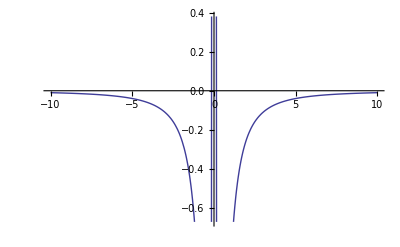

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=0.001,V0=0.00005,S0=0.0001,T=5,λS=0.15,KList={-0.005,0,0.005}},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,ω+ⅈ λS,0][[1,2]],
{ω,-10,10}]]
```

#### Derivée par rapport a V de l' Integrand en fonction de ω

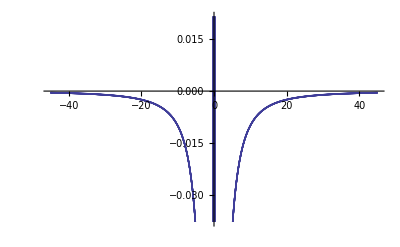

```mathematica
Module[{ρ=-0.000094075283,λ=0.1,L=0.5,ν=0.000148511498,V0=0.000000103958,S0=0.002786743,k=0.005,T=4.41369863,KList={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},ω=0.5,λS=0.15},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,ω+ⅈ λS,0][[1]],{ω,-45,45}]]
```

#### Derivée par rapport a V de l' Integrand en fonction de ω

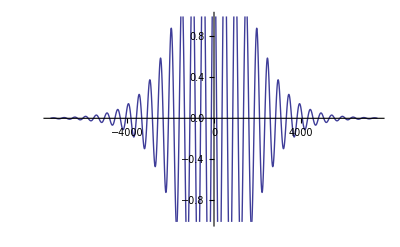

```mathematica
Module[{ρ=-0.000094075283,λ=0.1,L=0.5,ν=0.000148511498,V0=0.000000103958,S0=0.002786743,k=0.005,T=4.41369863,KList={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},ω=0.5,λS=0.15},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,ω+ⅈ λS,2][[2,1]],{ω,-7500,7500}]]
```

#### Derivée par rapport a ν de l' Integrand en fonction de ω

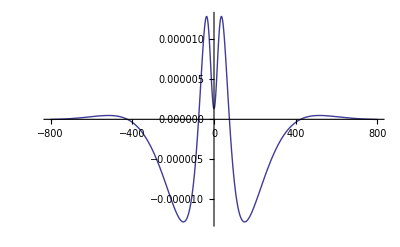

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=0.01,V0=0.00005,S0=0.0001,k=0.005,T=5,KList={-0.005,0,0.005},λS=0.5},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,ω+ⅈ λS,2][[3,1]],{ω,-800,800},PlotRange->All]]
```

#### Derivée par rapport a ρ de l' Integrand en fonction de ω

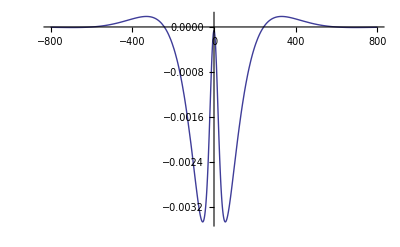

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=0.01,V0=0.00005,S0=0.0001,k=0.005,T=5,KList={-0.005,0,0.005},λS=0.5},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,ω+ⅈ λS,2][[4,1]],{ω,-800,800},PlotRange->All]]
```

#### Pour Fixer les constantes :

prices={6.76752,4.5951,3.533,2.50075,1.91898,1.16435,0.835524,0.558122,0.355561,0.150286,0.0877301,0.0380476,0.0173051,0.00375252}

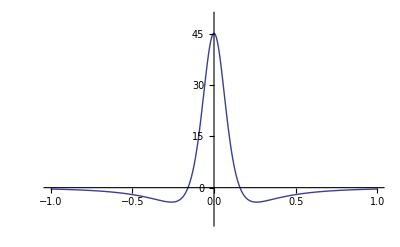
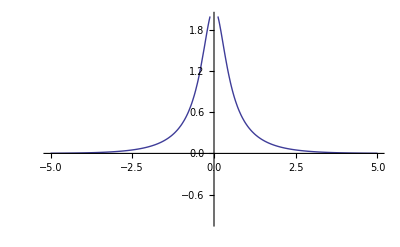
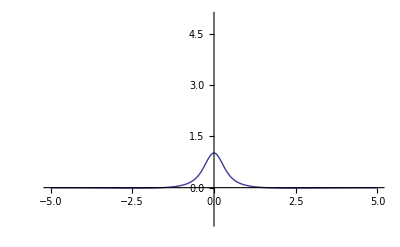
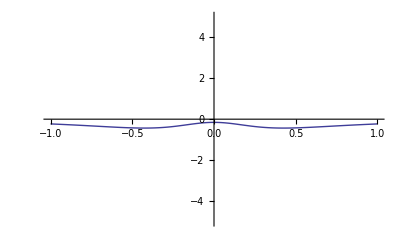
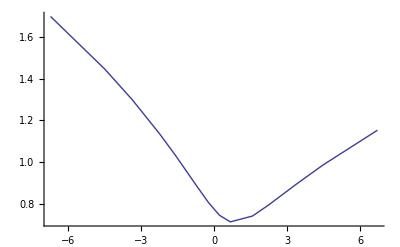

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=1.54,V=1,S0=0.0001,τ=5,nbsteps=20,scale=10,microratio=10,KList,ω=0.5,λS=0.15,prices,ll,homotheticRatio},KList={-3 √τ,-2 √τ,-1.5 √τ,-1 √τ,-0.707 √τ,-0.3 √τ,-0.1 √τ,0.1 √τ,0.3 √τ,0.707 √τ,1 √τ,1.5 √τ,2 √τ,3 √τ};
homotheticRatio=1;
prices=DerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio,0][[1]];
Print["prices=",prices];
{Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[1,8]],{ω,-1/homotheticRatio,1/homotheticRatio},PlotRange->{-10,50}],
Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[2,8]],{ω,-5/homotheticRatio,5/homotheticRatio},PlotRange->{-1,2}],
Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[3,8]],{ω,-5/homotheticRatio,5/homotheticRatio},PlotRange->{-1,5}],
Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[4,8]],{ω,-1/homotheticRatio,1/homotheticRatio},PlotRange->{-5,5}],
ll=Map[(NormalImplicitVol[S0,#[[1]],τ,#[[2]]])&,Transpose[{KList,prices}]];
ListPlot[Transpose[{KList,ll}],Joined->True]}]
```

prices={19.1453,12.9882,9.97127,7.03879,5.3906,3.26681,2.34895,1.5737,0.994722,0.39042,0.215312,0.0881445,0.0397121,0.00937873}

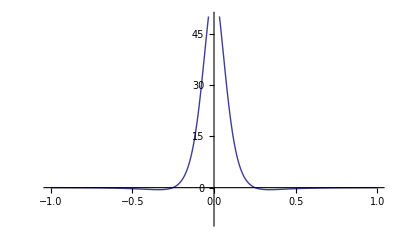
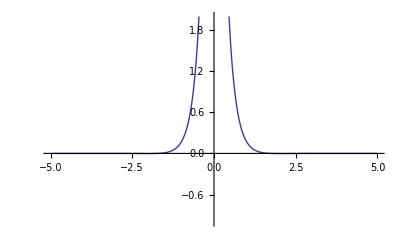
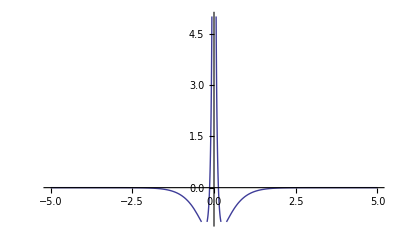
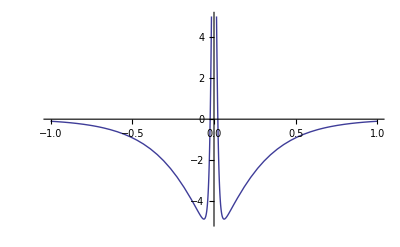
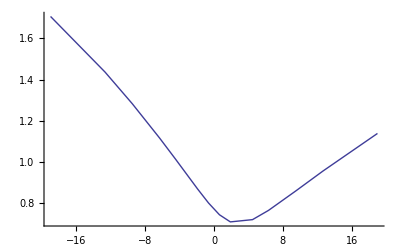

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=1.54,V=1,S0=0.0001,τ=40,nbsteps=20,scale=10,microratio=10,KList,ω=0.5,λS=0.15,prices,ll,homotheticRatio},KList={-3 √τ,-2 √τ,-1.5 √τ,-1 √τ,-0.707 √τ,-0.3 √τ,-0.1 √τ,0.1 √τ,0.3 √τ,0.707 √τ,1 √τ,1.5 √τ,2 √τ,3 √τ};
homotheticRatio=1;
prices=DerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio,0][[1]];
Print["prices=",prices];
{Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[1,8]],{ω,-1/homotheticRatio,1/homotheticRatio},PlotRange->{-10,50}],
Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[2,8]],{ω,-5/homotheticRatio,5/homotheticRatio},PlotRange->{-1,2}],
Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[3,8]],{ω,-5/homotheticRatio,5/homotheticRatio},PlotRange->{-1,5}],
Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[4,8]],{ω,-1/homotheticRatio,1/homotheticRatio},PlotRange->{-5,5}],
ll=Map[(NormalImplicitVol[S0,#[[1]],τ,#[[2]]])&,Transpose[{KList,prices}]];
ListPlot[Transpose[{KList,ll}],Joined->True]}]
```

```mathematica
Le microratio est le ratio entre la period initiale et la periode principale
```

```mathematica
On en deduit Qu'il faut augmenter le microratio avec la maturité pour mieux traiter les derivée par rapport a rho et nu , sans doute par une mumtiplication  par 0.5  τ^(1/4)
```

#### Implementation de Normale Heston Call avec ses derivées

```mathematica
DerivativeHestonNormalCallAux[ρ_,λ_,LT_,ν_,V_,S0_,k_,T_,nbsteps_,scale_,microratio_]:=Module[{res,λs=NormalHestonOptimalShift[λ,ρ,ν],LegendreCoef0,LegendreCoefn,period0,periodn,ϵ,imax,initialperiod,LegendreCoefn2,ω},
λs=0.15;LegendreCoef0=LegendreCoeffs[nbsteps];LegendreCoefn=LegendreCoeffs[Floor[nbsteps/7]];
period0=scale;periodn=scale/5;ϵ=10^(-10);imax=1000;initialperiod=scale/microratio;
LegendreCoefn2=LegendreCoeffs[nbsteps];
res=Re[MatrixAdaptativeIntegrate[Function[ω,DerivativeNormalHestonCallIntegrand[ρ,λ,LT,ν,V,S0,k,T,ω +λs ⅈ]],LegendreCoef0,LegendreCoefn,
period0,periodn,ϵ,imax,initialperiod,LegendreCoefn2]];
{res[[1]],1/π res[[2]]}]
```

```mathematica
DerivativeHestonNormalCallAux[ρ_,λ_,LT_,ν_,V_,S0_,k_,T_,nbsteps_,scale_,microratio_,flag_]:=Module[{res,λs=NormalHestonOptimalShift[λ,ρ,ν],LegendreCoef0,LegendreCoefn,period0,periodn,ϵ,imax,initialperiod,LegendreCoefn2,ω},
λs=0.15;LegendreCoef0=LegendreCoeffs[nbsteps];LegendreCoefn=LegendreCoeffs[Floor[nbsteps/7]];
period0=scale;periodn=scale/5;ϵ=10^(-10);imax=1000;initialperiod=scale/microratio;
LegendreCoefn2=LegendreCoeffs[nbsteps];
res=Re[MatrixAdaptativeIntegrate[Function[ω,DerivativeNormalHestonCallIntegrand[ρ,λ,LT,ν,V,S0,k,T,ω +λs ⅈ,flag]],LegendreCoef0,LegendreCoefn,
period0,periodn,ϵ,imax,initialperiod,LegendreCoefn2]];
{res[[1]],1/π res[[2]]}]
```

```mathematica
DerivativeHestonNormalCall[ρ_,λ_,LT_,ν1_,V01_,S1_,k1_List,T_,nbsteps_,scale_,microratio_]:=
Module[{optlist,L,ν,V0,F,k},
L=1/√V01;ν=L ν1;V0=1.;F=L S1;k=Table[k1[[i]] L,{i,1,Length[k1]}];
optlist=DerivativeHestonNormalCallAux[ρ,λ,LT,ν,V0,F,k,T,nbsteps,scale,microratio];
{Table[Max[{optlist⟦2,1,i⟧/L,S1-k1⟦i⟧,1.*^-12}],{i,1,Length[optlist⟦2,1⟧]}],
Table[optlist⟦2,2,i⟧ L,{i,1,Length[optlist⟦2,2⟧]}],
Table[optlist⟦2,3,i⟧/L,{i,1,Length[optlist⟦2,3⟧]}],
Table[optlist⟦2,4,i⟧,{i,1,Length[optlist⟦2,4⟧]}]}
]
```

```mathematica
DerivativeHestonNormalCall[ρ_,λ_,LT_,ν1_,V01_,S1_,k1_List,T_,nbsteps_,scale_,microratio_,flag_]:=
Module[{optlist,L,ν,V0,F,k},
L=1/√V01;ν=L ν1;V0=1.;F=L S1;k=Table[k1[[i]] L,{i,1,Length[k1]}];
optlist=DerivativeHestonNormalCallAux[ρ,λ,LT,ν,V0,F,k,T,nbsteps,scale,microratio,flag];
If[flag==0,
{Table[Max[{optlist⟦2,1,i⟧/L,S1-k1⟦i⟧,1.*^-12}],{i,1,Length[optlist⟦2,1⟧]}]},
{Table[Max[{optlist⟦2,1,i⟧/L,S1-k1⟦i⟧,1.*^-12}],{i,1,Length[optlist⟦2,1⟧]}],
Table[optlist⟦2,2,i⟧ L,{i,1,Length[optlist⟦2,2⟧]}],
Table[optlist⟦2,3,i⟧/L,{i,1,Length[optlist⟦2,3⟧]}],
Table[optlist⟦2,4,i⟧,{i,1,Length[optlist⟦2,4⟧]}]}
]]
```

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=0.001,V=0.00005,S0=0.0001,τ=5,KList={-0.005,0,0.005},ω=0.5,λS=0.1,nbsteps=120,scale=10,microratio=75,flag=0},
DerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio,flag]]
```

{{0.00923346,0.00634141,0.00407765}}

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=0.001,V=0.00005,S0=0.0001,τ=5,KList={-0.005,0,0.005},ω=0.5,λS=0.1,nbsteps=120,scale=10,microratio=75,flag=2},
DerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio,flag]]
```

{{0.00923346,0.00634141,0.00407765},{59.4119,63.2427,60.8397},{-0.000127682,-4.33049×10^-6,0.000128479},{0.0344685,-0.0344987,-0.0975885}}

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=0.2,V=0.00005,S0=0.0001,τ=5,KList={-0.005,0,0.005},ω=0.5,λS=0.15,δV,δν,δρ,nbsteps=120,scale=10,microratio=75},
δV=0.01 δρ;δν=0.01 ν;δρ=0.0001;
{DerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio],
{DerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio][[1]],(DerivativeHestonNormalCall[ρ,λ,L,ν,V+δV,S0,KList,τ,nbsteps,scale,microratio][[1]]-DerivativeHestonNormalCall[ρ,λ,L,ν,V-δV,S0,KList,τ,nbsteps,scale,microratio][[1]])/(2δV),
(DerivativeHestonNormalCall[ρ,λ,L,ν+δν,V,S0,KList,τ,nbsteps,scale,microratio][[1]]-DerivativeHestonNormalCall[ρ,λ,L,ν-δν,V,S0,KList,τ,nbsteps,scale,microratio][[1]])/(2δν),
(DerivativeHestonNormalCall[ρ+δρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio][[1]]-DerivativeHestonNormalCall[ρ-δρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio][[1]])/(2δρ)}
}
]
```

{{{0.00543347,0.000726774,0.000177958},{6.58686,11.0089,3.63169},{-0.000194148,0.0000740601,0.000171297},{-0.00126997,-0.002413,-0.000609176}},{{0.00543347,0.000726774,0.000177958},{6.97969,11.363,3.9493},{-0.00127006,-0.00241317,-0.000609221},{-0.000194148,0.0000740601,0.000171297}}}

## Normal 1 Facteur : Derivées seconde utiles pour le calcul des digitales

```mathematica
DerKDerivativeNormalHestonCallIntegrand[ρ_,λ_,L_,ν_,V0_,S0_,K_List,T_,ω_]:=Re[-ⅇ^(-ⅈ ω  S0) Outer[Times,DerivativeNormalHestonFondamentalTransform[ρ,λ,L,ν,V0,ω,T],Table[ⅈ Exp[ⅈ*K[[i]]ω]/ω,{i,1,Length[K]}]]]
```

```mathematica
DerKDerivativeNormalHestonCallIntegrand[ρ_,λ_,L_,ν_,V0_,S0_,K_List,T_,ω_,flag_]:=Re[-ⅇ^(-ⅈ ω  S0) Outer[Times,DerivativeNormalHestonFondamentalTransform[ρ,λ,L,ν,V0,ω,T,flag],Table[ⅈ Exp[ⅈ*K[[i]]ω]/ω,{i,1,Length[K]}]]]
```

prices={6.76752,4.5951,3.533,2.50075,1.91898,1.16435,0.835524,0.558122,0.355561,0.150286,0.0877301,0.0380476,0.0173051,0.00375252}

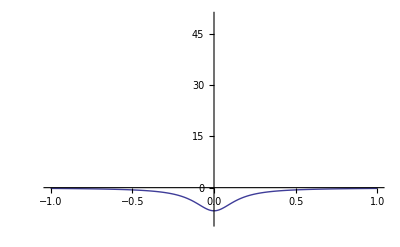
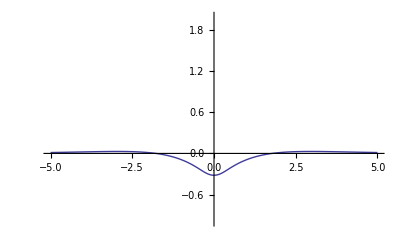
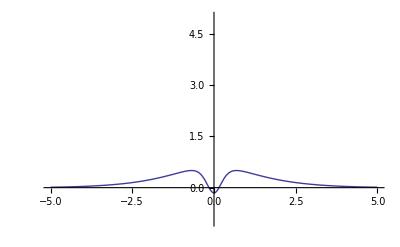
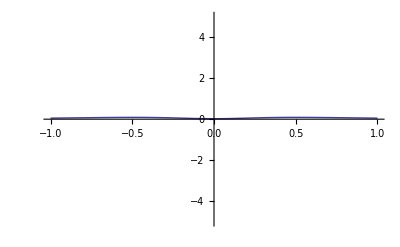
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=1.54,V=1,S0=0.0001,τ=5,nbsteps=20,scale=10,microratio=10,KList,ω=0.5,λS=0.15,prices,ll,homotheticRatio},KList={-3 √τ,-2 √τ,-1.5 √τ,-1 √τ,-0.707 √τ,-0.3 √τ,-0.1 √τ,0.1 √τ,0.3 √τ,0.707 √τ,1 √τ,1.5 √τ,2 √τ,3 √τ};
homotheticRatio=1;
prices=DerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio,0][[1]];
Print["prices=",prices];
{Plot[DerKDerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[1,8]],{ω,-1/homotheticRatio,1/homotheticRatio},PlotRange->{-10,50}],
Plot[DerKDerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[2,8]],{ω,-5/homotheticRatio,5/homotheticRatio},PlotRange->{-1,2}],
Plot[DerKDerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[3,8]],{ω,-5/homotheticRatio,5/homotheticRatio},PlotRange->{-1,5}],
Plot[DerKDerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[4,8]],{ω,-1/homotheticRatio,1/homotheticRatio},PlotRange->{-5,5}],
ll=Map[(NormalImplicitVol[S0,#[[1]],τ,#[[2]]])&,Transpose[{KList,prices}]];
ListPlot[Transpose[{KList,ll}],Joined->True]}]
```

```mathematica
DerKDerivativeHestonNormalCallAux[ρ_,λ_,LT_,ν_,V_,S0_,k_,T_,nbsteps_,scale_,microratio_]:=Module[{res,λs=NormalHestonOptimalShift[λ,ρ,ν],LegendreCoef0,LegendreCoefn,period0,periodn,ϵ,imax,initialperiod,LegendreCoefn2,ω},
λs=0.15;LegendreCoef0=LegendreCoeffs[nbsteps];LegendreCoefn=LegendreCoeffs[Floor[nbsteps/7]];
period0=scale;periodn=scale/5;ϵ=10^(-10);imax=1000;initialperiod=scale/microratio;
LegendreCoefn2=LegendreCoeffs[nbsteps];
res=Re[MatrixAdaptativeIntegrate[Function[ω,DerKDerivativeNormalHestonCallIntegrand[ρ,λ,LT,ν,V,S0,k,T,ω +λs ⅈ]],LegendreCoef0,LegendreCoefn,
period0,periodn,ϵ,imax,initialperiod,LegendreCoefn2]];
{res[[1]],1/π res[[2]]}]
```

```mathematica
DerKDerivativeHestonNormalCallAux[ρ_,λ_,LT_,ν_,V_,S0_,k_,T_,nbsteps_,scale_,microratio_,flag_]:=Module[{res,λs=NormalHestonOptimalShift[λ,ρ,ν],LegendreCoef0,LegendreCoefn,period0,periodn,ϵ,imax,initialperiod,LegendreCoefn2,ω},
λs=0.15;LegendreCoef0=LegendreCoeffs[nbsteps];LegendreCoefn=LegendreCoeffs[Floor[nbsteps/7]];
period0=scale;periodn=scale/5;ϵ=10^(-10);imax=1000;initialperiod=scale/microratio;
LegendreCoefn2=LegendreCoeffs[nbsteps];
res=Re[MatrixAdaptativeIntegrate[Function[ω,DerKDerivativeNormalHestonCallIntegrand[ρ,λ,LT,ν,V,S0,k,T,ω +λs ⅈ,flag]],LegendreCoef0,LegendreCoefn,
period0,periodn,ϵ,imax,initialperiod,LegendreCoefn2]];
{res[[1]],1/π res[[2]]}]
```

```mathematica
DerKDerivativeHestonNormalCall[ρ_,λ_,LT_,ν1_,V01_,S1_,k1_List,T_,nbsteps_,scale_,microratio_]:=
Module[{optlist,L,ν,V0,F,k},
L=1/√V01;ν=L ν1;V0=1.;F=L S1;k=Table[k1[[i]] L,{i,1,Length[k1]}];
optlist=DerKDerivativeHestonNormalCallAux[ρ,λ,LT,ν,V0,F,k,T,nbsteps,scale,microratio];
{Table[Max[{optlist⟦2,1,i⟧/L,S1-k1⟦i⟧,1.*^-12}],{i,1,Length[optlist⟦2,1⟧]}],
Table[optlist⟦2,2,i⟧ L,{i,1,Length[optlist⟦2,2⟧]}],
Table[optlist⟦2,3,i⟧/L,{i,1,Length[optlist⟦2,3⟧]}],
Table[optlist⟦2,4,i⟧,{i,1,Length[optlist⟦2,4⟧]}]}
]
```

```mathematica
DerKDerivativeHestonNormalCall[ρ_,λ_,LT_,ν1_,V01_,S1_,k1_List,T_,nbsteps_,scale_,microratio_,flag_]:=
Module[{optlist,L,ν,V0,F,k},
L=1/√V01;ν=L ν1;V0=1.;F=L S1;k=Table[k1[[i]] L,{i,1,Length[k1]}];
optlist=DerKDerivativeHestonNormalCallAux[ρ,λ,LT,ν,V0,F,k,T,nbsteps,scale,microratio,flag];
If[flag==0,
{Table[Max[{optlist⟦2,1,i⟧/L,S1-k1⟦i⟧,1.*^-12}],{i,1,Length[optlist⟦2,1⟧]}]},
{Table[Max[{optlist⟦2,1,i⟧/L,S1-k1⟦i⟧,1.*^-12}],{i,1,Length[optlist⟦2,1⟧]}],
Table[optlist⟦2,2,i⟧ L,{i,1,Length[optlist⟦2,2⟧]}],
Table[optlist⟦2,3,i⟧/L,{i,1,Length[optlist⟦2,3⟧]}],
Table[optlist⟦2,4,i⟧,{i,1,Length[optlist⟦2,4⟧]}]}
]]
```

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=0.2,V=0.00005,S0=0.0001,τ=5,KList={-0.005,0,0.005},ω=0.5,λS=0.15,δV,δν,δρ,nbsteps=120,scale=10,microratio=75},
δV=0.01 δρ;δν=0.01 ν;δρ=0.0001;
{DerKDerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio],
{DerKDerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio][[1]],(DerKDerivativeHestonNormalCall[ρ,λ,L,ν,V+δV,S0,KList,τ,nbsteps,scale,microratio][[1]]-DerKDerivativeHestonNormalCall[ρ,λ,L,ν,V-δV,S0,KList,τ,nbsteps,scale,microratio][[1]])/(2δV),
(DerKDerivativeHestonNormalCall[ρ,λ,L,ν+δν,V,S0,KList,τ,nbsteps,scale,microratio][[1]]-DerKDerivativeHestonNormalCall[ρ,λ,L,ν-δν,V,S0,KList,τ,nbsteps,scale,microratio][[1]])/(2δν),
(DerKDerivativeHestonNormalCall[ρ+δρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio][[1]]-DerKDerivativeHestonNormalCall[ρ-δρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio][[1]])/(2δρ)}
}
]
```

{{{0.0051,0.0001,1.×10^-12},{2.95975,8.02546,-2.86118},{0.000102674,0.00221002,-0.0000933514},{-0.000793628,-0.0020633,0.000662546}},{{0.0051,0.0001,1.×10^-12},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}}

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=0.2,V=0.00005,S0=0.0001,τ=5,KList={-0.005,0,0.005},ω=0.5,λS=0.15,δV,δν,δρ,nbsteps=120,scale=10,microratio=50},
δV=0.01 δρ;δν=0.01 ν;δρ=0.0001;
{DerKDerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio],
{DerKDerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio][[1]],(DerKDerivativeHestonNormalCall[ρ,λ,L,ν,V+δV,S0,KList,τ,nbsteps,scale,microratio][[1]]-DerKDerivativeHestonNormalCall[ρ,λ,L,ν,V-δV,S0,KList,τ,nbsteps,scale,microratio][[1]])/(2δV),
(DerKDerivativeHestonNormalCall[ρ,λ,L,ν+δν,V,S0,KList,τ,nbsteps,scale,microratio][[1]]-DerKDerivativeHestonNormalCall[ρ,λ,L,ν-δν,V,S0,KList,τ,nbsteps,scale,microratio][[1]])/(2δν),
(DerKDerivativeHestonNormalCall[ρ+δρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio][[1]]-DerKDerivativeHestonNormalCall[ρ-δρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio][[1]])/(2δρ)}
}
]
```

{{{0.0051,0.0001,1.×10^-12},{2.95975,8.02546,-2.86118},{0.000102674,0.00221002,-0.0000933514},{-0.000793628,-0.0020633,0.000662546}},{{0.0051,0.0001,1.×10^-12},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}}

## Normal 1 Facteur : Calibrateur

```mathematica
NormalHestonSmileCalibrate[KList_,PriceList_,WeightList_,S0_,λ_,LT_,T_,nbsteps_,scale_,microratio_]:=Module[{func,gradfunc,V0,rho,nu},
func=Function[{V,ρ,ν},Module[{ff=DerivativeHestonNormalCall[ρ,λ,LT,ν,V,S0,KList,T,nbsteps,scale,microratio,0]},
Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])^2,{i,1,Length[KList]}]]];
gradfunc=Function[{V,ρ,ν},Module[{ff=DerivativeHestonNormalCall[ρ,λ,LT,ν,V,S0,KList,T,nbsteps,scale,microratio]},
{Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[2,i]],{i,1,Length[KList]}],
Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[3,i]],{i,1,Length[KList]}],
Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[4,i]],{i,1,Length[KList]}]
}]];
FindMinimum[func[V0,rho,nu],{{V0,0.00003,0.000001,0.001},{nu,0.001,0.000001,0.01},{rho,0,-0.9,0.9}},
MaxIterations->200,AccuracyGoal->8,Method->"LevenbergMarquardt",
Gradient->gradfunc[V0,rho,nu]] 
]
```

```mathematica
Module[{ρ=0.1,λ=0.1,L=1,ν=0.008,V=7 10^(-6),S0=0.0001,τ=5,nbsteps=120,scale=10,microratio=75,KList={-0.02,-0.0175,-0.015,-0.0125,-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.0125,0.015,0.0175,0.02}},
DerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio]]//MatrixForm
```

(0.0201836 | 0.0177071 | 0.015238 | 0.0127794 | 0.0103367 | 0.00791957 | 0.00554948 | 0.0032907 | 0.00147827 | 0.000792118 | 0.000539315 | 0.000397885 | 0.000304737 | 0.00023836 | 0.000188891 | 0.000150981 | 0.000121391
12.8343 | 16.3626 | 20.9937 | 27.1867 | 35.7036 | 47.9459 | 66.902 | 100.366 | 150.08 | 110.074 | 77.5963 | 57.9676 | 44.7326 | 35.1924 | 28.0298 | 22.5095 | 18.1796
-0.000171494 | -0.000201284 | -0.000235397 | -0.000274152 | -0.00031757 | -0.000364574 | -0.000409382 | -0.00041706 | -0.0000783304 | 0.000310948 | 0.000349262 | 0.000332053 | 0.000302881 | 0.000271499 | 0.000240991 | 0.000212485 | 0.000186392
0.00856074 | 0.00830545 | 0.00734027 | 0.00525604 | 0.00137368 | -0.00555176 | -0.0181749 | -0.0434669 | -0.084066 | -0.0501253 | -0.0243968 | -0.0102618 | -0.00181273 | 0.00340834 | 0.00660924 | 0.00847369 | 0.00942911)

```mathematica
Timing[Module[{ρ=-0.51,λ=0.1,L=1,ν=0.002,V=0.00005,S0=0.0001,T=5,nbsteps=120,scale=10,microratio=75,KList={-0.005,-0.0025,0,0.0025,0.005},PriceList={0.00925563132870,0.007697476807935,0.00629203396078,0.00504696425226,0.00396598409559},WeightList={1,1,1,1,1}},
NormalHestonSmileCalibrate[KList,PriceList,WeightList,S0,λ,L,T,nbsteps,scale,microratio]
]]
```

{48.078,{2.22142×10^-17,{V0$1977930→0.0000500752,nu$1977930→0.00202212,rho$1977930→-0.504624}}}

```mathematica
Timing[Module[{ρ=-0.51,λ=0.1,L=1,ν=0.002,V=0.00005,S0=0.0001,T=5,nbsteps=12,scale=5,microratio=20,KList={-0.005,-0.0025,0,0.0025,0.005},PriceList={0.00925563132870,0.007697476807935,0.00629203396078,0.00504696425226,0.00396598409559},WeightList={1,1,1,1,1}},
NormalHestonSmileCalibrate[KList,PriceList,WeightList,S0,λ,L,T,nbsteps,scale,microratio]
]]
```

{1.,{5.40653×10^-17,{V0$2116103→0.0000501197,nu$2116103→0.00203505,rho$2116103→-0.501523}}}

```mathematica
Timing[Module[{ρ=-0.2,λ=0.1,L=1,ν=0.01,V=0.00002,S0=0.0001,T=5,nbsteps=10,scale=8,microratio=20,
PriceList,WeightList,KList={-0.005,-0.0025,0,0.0025,0.005}},
WeightList=Table[1,{i,1,Length[KList]}];
PriceList=DerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,T,nbsteps,scale,microratio,0][[1]];
NormalHestonSmileCalibrate[KList,PriceList,WeightList,S0,λ,L,T,nbsteps,scale,microratio]
]]
```

{0.719,{5.1904×10^-15,{V0$11034→0.0000199993,nu$11034→0.0099995,rho$11034→-0.199886}}}

## Normal 1,2 et 3 Facteurs de vol : Integrands

#### Cas scalaire pour 1, 2 et 3 facteurs

```mathematica
NormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,S0_,K_,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  S0) NormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ω,T]NormalCallPayOffFourierTransform[K,α,a,ω]]
```

```mathematica
NormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,S0_,K_List,T_,ω_]:=Re[ⅇ^(-ⅈ ω  S0) NormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ω,T]Table[NormalCallPayOffFourierTransform[K[[i]],ω],{i,1,Length[K]}]]
```

```mathematica
NormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,K_,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  S0) NormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ω,T]NormalCallPayOffFourierTransform[K,α,a,ω]]
```

```mathematica
NormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,K_,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  S0) NormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ω,T]NormalCallPayOffFourierTransform[K,α,a,ω]]
```

#### Cas vectoriel pour 1, 2 et 3 facteurs

```mathematica
NormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,S0_,K_List,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  S0) NormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ω,T]Table[NormalCallPayOffFourierTransform[K[[i]],α,a,ω],{i,1,Length[K]}]]
```

```mathematica
NormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,K_List,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  S0) NormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ω,T]Table[NormalCallPayOffFourierTransform[K[[i]],α,a,ω],{i,1,Length[K]}]]
```

```mathematica
NormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,K_List,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  S0) NormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ω,T]Table[NormalCallPayOffFourierTransform[K[[i]],α,a,ω],{i,1,Length[K]}]]
```

## Phenomene de resonance avec le shift complexe

```mathematica
Module[{ρ=0.300322,λv=0.387,θv=1,κ=0.8944,V=1,S0=0.53,T=11.7371,k=-4,ω},
NormalHestonFondamentalTransform[ρ,λv,θv,κ,V,0+0.5 ⅈ,T]]
```

η=0.252696

ψm+ψp ⅇ^(-ζ  τ)=0.00447286-0.00302389 ⅈ

A=6.19292-2.14841×10^-15 ⅈ B=76.7205-1.63043×10^-13 ⅈ

1.02059×10^36-1.68592×10^23 ⅈ

```mathematica
Module[{ρ=0.300322,λv=0.387,θv=1,κ=0.8944,V=1,S0=0.53,T=11.7371,k=-4,ω},
NormalHestonFondamentalTransform[ρ,λv,θv,κ,V,0+0.4 ⅈ,T]]
```

5.40868+1.88589×10^-17 ⅈ

```mathematica
NormalHestonShiftDiscriminator[ρ_,λv_,θv_,κ_,V_,τ_,λ_]:=(λv-ρ κ λ)+√((λv-ρ κ λ)^2-κ^2 λ^2)+(-(λv-ρ κ λ)+√((λv-ρ κ λ)^2-κ^2 λ^2))ⅇ^(-√((λv-ρ κ λ)^2-κ^2 λ^2) τ)
```

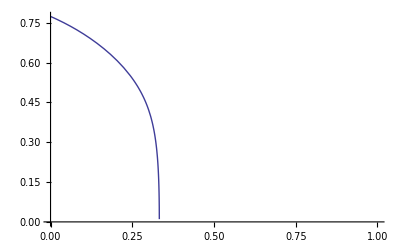

```mathematica
Module[{ρ=0.300322,λv=0.387,θv=1,κ=0.8944,V=1,S0=0.53,T=10.7371,k=-4,,λ},
Plot[NormalHestonShiftDiscriminator[ρ,λv,θv,κ,V,T,λ],{λ,0,1}]]
```

λv/κ=0.2

NormalHestonOptimalShift[λv,ρ,κ]=0.0995

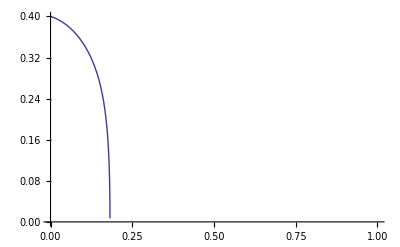

```mathematica
Module[{ρ=0.1,λv,θv=1,κ=1,V=1,S0=0.53,T=11.7371,k=-4,λ},κ=1.;λv=0.2;
Print["λv/κ=",λv/κ];
Print["NormalHestonOptimalShift[λv,ρ,κ]=",NormalHestonOptimalShift[λv,ρ,κ]];
Plot[NormalHestonShiftDiscriminator[ρ,λv,θv,κ,V,T,λ],{λ,0,1}]]
```

```mathematica
donc le shift doit etre dependant de la vol de vol et du λv, en fait de leur ratio ,
si ρ est <0, pas de probleme, si ρ>0, on doit raprocher le shift de 0 suivant λv/κ
```

```mathematica
experimentalement , un shift egal a Max[0.5, λv/κ (1-ρ^2/2)/2] parait optimal
```

```mathematica
NormalHestonOptimalShift[λv_,ρ_,κ_]:=Min[0.5, (λv(1-ρ^2/2))/(2κ)]
```

## Shift et parametres d' integration

le shift ici sera pris a 0.5. A ce shift sera adapté les constante de la procedure d' integration.

Exemple d' integrand pour des shift differents

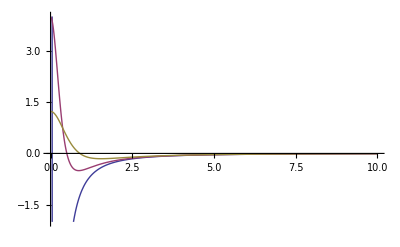
{0.219,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.01,κ=0.5,V=0.01,S0=0,λ1=0.05,λ2=0.5,λ3=0.9,T=0.5,k=0.01,ω},
Plot[{NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ1 ⅈ],
NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ2 ⅈ],
NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ3 ⅈ]},{ω,0,10},PlotRange->{-2,4}]
]]
```

## Normal 1,2 et 3 Facteurs de vol : Implementations

on voit que le shift determine a lui tout seul les parametre

### Implementation mathematica de reference

```mathematica
HestonNormalCallN[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=1/π Re[Module[{λ=0.5,ω},
NIntegrate[NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
HestonNormalCallN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=1/π Re[Module[{λ=0.5,ω},
NIntegrate[NormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,1,1,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
HestonNormalCallN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=1/π Re[Module[{λ=0.5,ω},
NIntegrate[NormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,1,1,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

### Implementation Operationnelle

```mathematica
Print["ω=",ω," integrand=",NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ ⅈ]];
```

```mathematica
HestonNormalCallAux[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=1/π Re[Module[{λ=NormalHestonOptimalShift[λv,ρ,κ],ω},
AdaptativeIntegrate[Function[ω,NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[8],
20λ,3λ,10^(-10),1000,2λ,LegendreCoeffs[20]][[2]]]]
```

```mathematica
HestonNormalCallAux[ρ_,λv_,θv_,κ_,V_,S0_,k_List,T_]:=1/π Re[Module[{λ=NormalHestonOptimalShift[λv,ρ,κ],ω},
AdaptativeIntegrate[Function[ω,NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[8],
20λ,3λ,10^(-10),1000,2λ,LegendreCoeffs[20]][[2]]]]
```

```mathematica
HestonNormalCallAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=1/π Re[Module[{λ=0.5,ω},
AdaptativeIntegrate[Function[ω,NormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
HestonNormalCallAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=1/π Re[Module[{λ=0.5,ω},
AdaptativeIntegrate[Function[ω,NormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
(*version Vecteur *)
```

### Implementation Normalisée

```mathematica
HestonNormalCall[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{θv1,κ1,V1,S01,k1,L},
L=√(1./V);θv1=L^2 θv;κ1=L κ;V1=1.0;S01=L S0;k1=L k;
HestonNormalCallAux[ρ,λv,θv1,κ1,V1,S01,k1,T]/L
]
```

```mathematica
HestonNormalCall[ρ_,λv_,θv_,κ_,V_,S0_,k_List,T_]:=Module[{θv1,κ1,V1,S01,k1,L},
L=√(1./V);θv1=L^2 θv;κ1=L κ;V1=1.0;S01=L S0;k1=L k;
HestonNormalCallAux[ρ,λv,θv1,κ1,V1,S01,k1,T]/L
]
```

```mathematica
HestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=Module[{θv1a,κ1a,V1a,θv2a,κ2a,V2a,S0a,ka,L},
L=√(1./(V1+V2));θv1a=L^2 θv1;θv2a=L^2 θv2;κ1a=L κ1;κ2a=L κ2;V1a=L^2 V1;V2a=L^2 V2;S0a=L S0;ka=L k;
HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,S0,ka,T]/L
]
```

```mathematica
HestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=Module[{θv1a,κ1a,V1a,θv2a,κ2a,V2a,θv3a,κ3a,V3a,S0a,ka,L},
L=√(1./(V1+V2+V3));θv1a=L^2 θv1;θv2a=L^2 θv2;θv3a=L^2 θv3;κ1a=L κ1;κ2a=L κ2;κ3a=L κ3;V1a=L^2 V1;V2a=L^2 V2;V3a=L^2 V3;S0a=L S0;ka=L k;
HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,ρ3,λv3,θv3a,κ3a,V3a,S0,ka,T]/L
]
```

### Implementation Normalisée qui permet de tracer la normalisation

```mathematica
HestonNormalCallTrace[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{θva,κa,Va,S0a,ka,L},
L=√(1./V);θva=L^2 θv;κa=L κ;Va=L^2 V;S0a=L S0;ka=L k;Print["L=",L," κa=",κa," S0a=",S0a," ka=",ka];
HestonNormalCallAux[ρ,λv,θva,κa,Va,S0a,ka,T]/L
]
```

```mathematica
HestonNormalCallTrace[ρ_,λv_,θv_,κ_,V_,S0_,k_List,T_]:=Module[{θva,κa,Va,S0a,ka,L},
L=√(1./V);θva=L^2 θv;κa=L κ;Va=L^2 V;S0a=L S0;ka=L k;Print["L=",L," κa=",κa," S0a=",S0a," ka=",ka];
(HestonNormalCallAux[ρ,λv,θva,κa,Va,S0a,#,T]/L)& /@ ka
]
```

```mathematica
HestonNormalCallTrace[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=Module[{θv1a,κ1a,V1a,S0a,ka,θv2a,κ2a,V2a,L},
L=√(1./(V1+V2));θv1a=L^2 θv1;θv2a=L^2 θv2;κ1a=L κ1;κ2a=L κ2;V1a=L^2 V1;V2a=L^2 V2;S0a=L S0;ka=L k;Print["L=",L," V1a=",V1a," κa1=",κ1a," V2a=",V2a," κa2=",κ2a," S0a=",S0a," ka=",ka];
HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,S0a,ka,T]/L
]
```

```mathematica
HestonNormalCallTrace[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=Module[{θv1a,κ1a,V1a,S0a,ka,θv2a,κ2a,V2a,L},
L=√(1./(V1+V2));θv1a=L^2 θv1;θv2a=L^2 θv2;κ1a=L κ1;κ2a=L κ2;V1a=L^2 V1;V2a=L^2 V2;S0a=L S0;ka=L k;Print["L=",L," V1a=",V1a," κa1=",κ1a," V2a=",V2a," κa2=",κ2a," S0a=",S0a," ka=",ka];
(HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,S0a,#,T]/L)& /@ ka
]
```

```mathematica
HestonNormalCallTrace[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=Module[{θv1a,κ1a,V1a,θv3a,κ3a,V3a,S0a,ka,θv2a,κ2a,V2a,L},
L=√(1./(V1+V2+V3));θv1a=L^2 θv1;θv2a=L^2 θv2;θv3a=L^2 θv3;κ1a=L κ1;κ2a=L κ2;κ3a=L κ3;V1a=L^2 V1;V2a=L^2 V2;V3a=L^2 V3;S0a=L S0;ka=L k;Print["L=",L," V1a=",V1a," κa1=",κ1a," V2a=",V2a," κa2=",κ2a," V3a=",V3a," κa3=",κ3a," S0a=",S0a," ka=",ka];
HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,S0a,ka,T]/L
]
```

```mathematica
HestonNormalCallTrace[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=Module[{θv1a,κ1a,V1a,θv3a,κ3a,V3a,S0a,ka,θv2a,κ2a,V2a,L},
L=√(1./(V1+V2+V3));θv1a=L^2 θv1;θv2a=L^2 θv2;θv3a=L^2 θv3;κ1a=L κ1;κ2a=L κ2;κ3a=L κ3;V1a=L^2 V1;V2a=L^2 V2;V3a=L^2 V3;S0a=L S0;ka=L k;Print["L=",L," V1a=",V1a," κa1=",κ1a," V2a=",V2a," κa2=",κ2a," V3a=",V3a," κa3=",κ3a," S0a=",S0a," ka=",ka];
(HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,S0a,#,T]/L)& /@ ka
]
```

## Normal : Implementation traversant la barriere de Gindinkin

```mathematica
ThInterpolator[x1_,y1_,x2_,y2_,x_]:=Module[{a},
a=ArcTanh[1-y2/y1]/(x2-x1);
y1(1-Tanh[a(x-y1)])]
```

```mathematica
LinInterpolator[x1_,y1_,x2_,y2_,x_]:=Module[{a},
a=(y2-y1)/(x2-x1);
y2+a(x-x2)]
```

```mathematica
QuadInterpolator[x1_,y1_,x2_,y2_,x3_,y3_,x_]:=Module[{a,b},
a=-(x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3)/((x1-x2) (x1-x3) (-x2+x3));
b=-(-2 x1 x2 y1+x2^2 y1+2 x1 x3 y1-x3^2 y1+x1^2 y2-2 x1 x3 y2+x3^2 y2-x1^2 y3+2 x1 x2 y3-x2^2 y3)/((x2-x3) (x1^2-x1 x2-x1 x3+x2 x3));
a(x-x1)^2+b(x-x1)+y1]
```

```mathematica
PowerInterpolator[x1_,y1_,x2_,y2_,x3_,y3_,x_]:=Module[{a,b},
b=Log[(y3-y1)/(y2-y1)]/Log[(x3-x1)/(x2-x1)];
a=(y3-y1)/(x3-x1)^b;
y1+a (x-x1)^b
]
```

```mathematica
(* interpolateur qui interpole une variable >0 par exemple la vol implicite en fonction de la vol de vol *)
```

```mathematica
SmartInterpolator[x1_,y1_,x2_,y2_,x3_,y3_,x_]:=Module[{a1,a2},
a1=(y2-y1)/(x2-x1);a2=(y3-y2)/(x3-x2);
Which[
a1>0&&a2<0,LinInterpolator[x1,y1,x3,y3,x],
a1>0&&a2≥0,PowerInterpolator[x1,y1,x2,y2,x3,y3,x],
a1<0&&a2>0,LinInterpolator[x1,y1,x3,y3,x],
a1<0&&a2≤0&&a2>a1, PowerInterpolator[x1,y1,x2,y2,x3,y3,x],
a1<0&&a2≤0&&a2≤a1,ThInterpolator[x1,y1,x3,y3,x]
]]
```

```mathematica
Solve[{y3==a(x3-x1)^2+b(x3-x1)+y1,y2==a(x2-x1)^2+b(x2-x1)+y1},{a,b}]
```

{{a→-(x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3)/((x1-x2) (x1-x3) (-x2+x3)),b→-(-2 x1 x2 y1+x2^2 y1+2 x1 x3 y1-x3^2 y1+x1^2 y2-2 x1 x3 y2+x3^2 y2-x1^2 y3+2 x1 x2 y3-x2^2 y3)/((x2-x3) (x1^2-x1 x2-x1 x3+x2 x3))}}

```mathematica
TransHestonNormalCall[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_,LimitGindinkin_]:=Module[{θv1,κ1,V1,S01,k1,L,κ1Limit,κ1test1,κ1test2,vol1,vol2,vol},
L=√(1./V);θv1=L^2 θv;κ1=L κ;V1=1.0;S01=L S0;k1=L k;
κ1Limit=LimitGindinkin √(2 λv θv1);
If[κ1<0.9 κ1Limit,
HestonNormalCallAux[ρ,λv,θv1,κ1,V1,S01,k1,T]/L,
κ1test1=0.8 κ1Limit;
κ1test2=0.9 κ1Limit;
vol1=NormalImplicitVol[S01,k1,T,HestonNormalCallAux[ρ,λv,θv1,κ1test1,V1,S01,k1,T]];
vol2=NormalImplicitVol[S01,k1,T,HestonNormalCallAux[ρ,λv,θv1,κ1test2,V1,S01,k1,T]];
If[vol2<vol1,
vol=ThInterpolator[κ1test1,vol1,κ1test2,vol2,κ1],
vol=LinInterpolator[κ1test1,vol1,κ1test2,vol2,κ1]
];
NormalCall[S01,vol,k1,T]/L
]
]
```

```mathematica
TransHestonNormalCall[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_,LimitGindinkin_,order_]:=Module[{θv1,κ1,V1,S01,k1,L,κ1Limit,κ1test1,κ1test2,κ1test3,vol1,vol2,vol3,vol},
L=√(1./V);θv1=L^2 θv;κ1=L κ;V1=1.0;S01=L S0;k1=L k;
κ1Limit=LimitGindinkin √(2 λv θv1);
Print["LimitGindinkin=",κ1Limit," κ1=",κ1];
If[κ1<0.9 κ1Limit,
HestonNormalCallAux[ρ,λv,θv1,κ1,V1,S01,k1,T]/L,
If[order==1,
κ1test1=0.8 κ1Limit;
κ1test2=0.9 κ1Limit;
vol1=NormalImplicitVol[S01,k1,T,HestonNormalCallAux[ρ,λv,θv1,κ1test1,V1,S01,k1,T]];
vol2=NormalImplicitVol[S01,k1,T,HestonNormalCallAux[ρ,λv,θv1,κ1test2,V1,S01,k1,T]];
If[vol2<vol1,
vol=ThInterpolator[κ1test1,vol1,κ1test2,vol2,κ1],
vol=LinInterpolator[κ1test1,vol1,κ1test2,vol2,κ1]
]
];
If[order==2,
κ1test1=0.8 κ1Limit;
κ1test2=0.85 κ1Limit;
κ1test3=0.9 κ1Limit;
vol1=NormalImplicitVol[S01,k1,T,HestonNormalCallAux[ρ,λv,θv1,κ1test1,V1,S01,k1,T]];
vol2=NormalImplicitVol[S01,k1,T,HestonNormalCallAux[ρ,λv,θv1,κ1test2,V1,S01,k1,T]];
vol3=NormalImplicitVol[S01,k1,T,HestonNormalCallAux[ρ,λv,θv1,κ1test3,V1,S01,k1,T]];
Print["κ1test1=",κ1test1," κ1test2=",κ1test2," κ1test3=",κ1test3," vol1=",vol1," vol2=",vol2," vol3=",vol3];
vol=SmartInterpolator[κ1test1,vol1,κ1test2,vol2,κ1test3,vol3,κ1];
Print["vol=",vol]
];
NormalCall[S01,vol,k1,T]/L
]]
```

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=3,V=1,S0=-0.1,T=5},TransHestonNormalCall[ρ,λv,θv,κ,V,S0,1,T,8]]]
```

{0.313,0.0747721}

```mathematica
TransHestonNormalCall[ρ_,λv_,θv_,κ_,V_,S0_,k_List,T_,LimitGindinkin_]:=Module[{θv1,κ1,V1,S01,k1,L,κ1Limit,κ1test1,κ1test2,vol1,vol2,vol},
L=√(1./V);θv1=L^2 θv;κ1=L κ;V1=1.0;S01=L S0;k1=L k;
κ1Limit=LimitGindinkin √(2 λv θv1);
Table[
If[κ1<0.9 κ1Limit,
HestonNormalCallAux[ρ,λv,θv1,κ1,V1,S01,k1[[i]],T]/L,
κ1test1=0.8 κ1Limit;
κ1test2=0.9 κ1Limit;
vol1=NormalImplicitVol[S01,k1[[i]],T,HestonNormalCallAux[ρ,λv,θv1,κ1test1,V1,S01,k1[[i]],T]];
vol2=NormalImplicitVol[S01,k1[[i]],T,HestonNormalCallAux[ρ,λv,θv1,κ1test2,V1,S01,k1[[i]],T]];
If[vol2<vol1,
vol=ThInterpolator[κ1test1,vol1,κ1test2,vol2,κ1],
vol=LinInterpolator[κ1test1,vol1,κ1test2,vol2,κ1]
];
NormalCall[S01,vol,k1[[i]],T]/L
],{i,1,Length[k]}]
]
```

κ gindinkin=0.632456

FindRoot::reged: The point {0.0001} is at the edge of the search region {0.0001, 15.} in coordinate 1 and the computed search direction points outside the region.

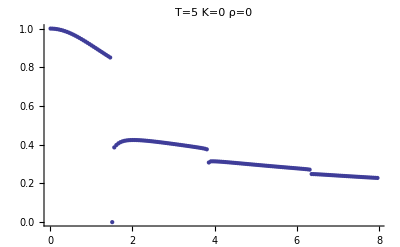

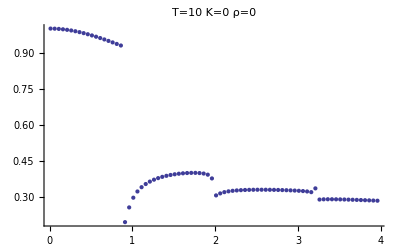

FindRoot::reged: The point {0.0001} is at the edge of the search region {0.0001, 15.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot :: "reged" will be suppressed during this calculation.

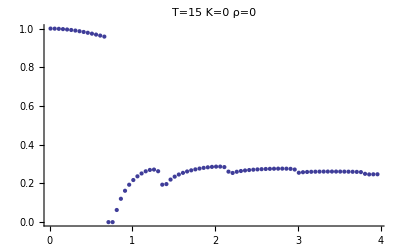

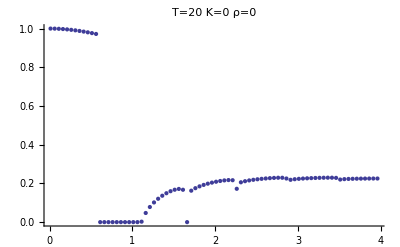

{77.719,Null}

```mathematica
Timing[Module[{ρ=0,λv=0.2,θv=1,κ,V=1,S0=0,k=0,T1=5,T2=10,T3=15,T4=20},
Print["κ gindinkin=",√(2λv θv)];
Print[ListPlot[
Table[{κ,NormalImplicitVol[S0,k,T1,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T1]]},{κ,0.01,8,0.05}],PlotLabel->"T="<>ToString[T1]<>" K="<>ToString[k]<>" ρ="<>ToString[ρ],PlotRange->All]];
Print[ListPlot[
Table[{κ,NormalImplicitVol[S0,k,T2,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T2]]},{κ,0.01,4,0.05}],PlotLabel->"T="<>ToString[T2]<>" K="<>ToString[k]<>" ρ="<>ToString[ρ],PlotRange->All]];
Print[ListPlot[
Table[{κ,NormalImplicitVol[S0,k,T3,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T3]]},{κ,0.01,4,0.05}],PlotLabel->"T="<>ToString[T3]<>" K="<>ToString[k]<>" ρ="<>ToString[ρ],PlotRange->All]];
Print[ListPlot[
Table[{κ,NormalImplicitVol[S0,k,T4,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T4]]},{κ,0.01,4,0.05}],PlotLabel->"T="<>ToString[T4]<>" K="<>ToString[k]<>" ρ="<>ToString[ρ],PlotRange->All]];
]]
```

κ gindinkin=0.632456

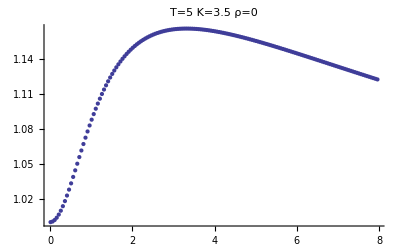

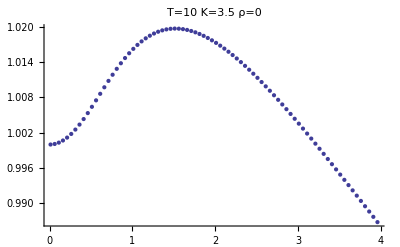

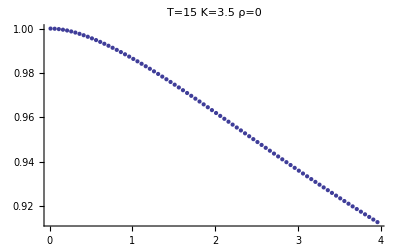

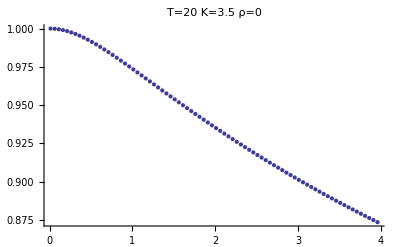

{166.094,Null}

```mathematica
Timing[Module[{ρ=0,λv=0.2,θv=1,κ,V=1,S0=0,k=3.5,T1=5,T2=10,T3=15,T4=20},
Print["κ gindinkin=",√(2λv θv)];
Print[ListPlot[
Table[{κ,NormalImplicitVol[S0,k,T1,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T1]]},{κ,0.01,8,0.05}],PlotLabel->"T="<>ToString[T1]<>" K="<>ToString[k]<>" ρ="<>ToString[ρ],PlotRange->All]];
Print[ListPlot[
Table[{κ,NormalImplicitVol[S0,k,T2,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T2]]},{κ,0.01,4,0.05}],PlotLabel->"T="<>ToString[T2]<>" K="<>ToString[k]<>" ρ="<>ToString[ρ],PlotRange->All]];
Print[ListPlot[
Table[{κ,NormalImplicitVol[S0,k,T3,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T3]]},{κ,0.01,4,0.05}],PlotLabel->"T="<>ToString[T3]<>" K="<>ToString[k]<>" ρ="<>ToString[ρ],PlotRange->All]];
Print[ListPlot[
Table[{κ,NormalImplicitVol[S0,k,T4,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T4]]},{κ,0.01,4,0.05}],PlotLabel->"T="<>ToString[T4]<>" K="<>ToString[k]<>" ρ="<>ToString[ρ],PlotRange->All]];
]]
```

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=2,V=1,S0=0.1,T=5},TransHestonNormalCall[ρ,λv,θv,κ,V,S0,1,T,5]]]
```

{0.36,0.0901133}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=2,V=1,S0=0.1,k=0.1,T=5,LimitGindinkin=10},{HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T],TransHestonNormalCall[ρ,λv,θv,κ,V,S0,{k},T,LimitGindinkin]}]]
```

{9.094,{0.653306,0.653306,0.227783,{0.653306}}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=2,V=1,S0=0.1,k=0.1,T=5,LimitGindinkin=10},{HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T],TransHestonNormalCall[ρ,λv,θv,κ,V,S0,{k},T,LimitGindinkin]}]]
```

{6.781,{0.653306,0.653306,0.227783,{0.653306}}}

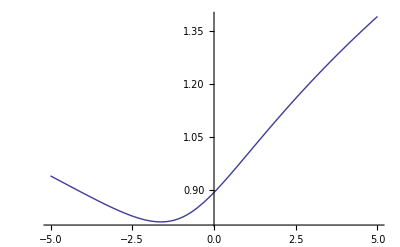
{48.39,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=1,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T]]},{k,-5,5}]]]
```

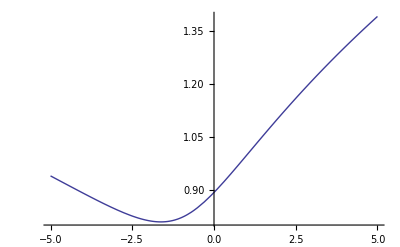
{40.984,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=1,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T]]},{k,-5,5}]]]
```

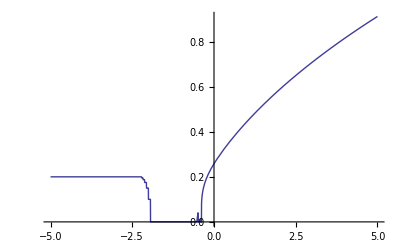
{76.469,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=3,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T]]},{k,-5,5}]]]
```

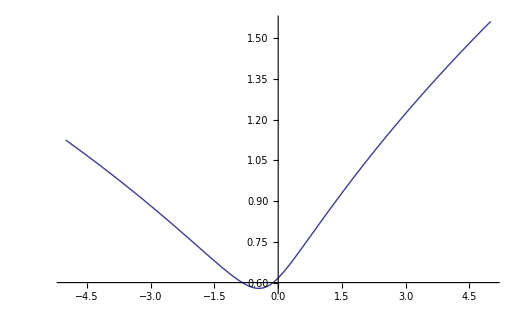
{153.64,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=3,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T]]},{k,-5,5}]]]
```

```mathematica
(*     Prolongation lineaire  des prix options : non effectif     *)
```

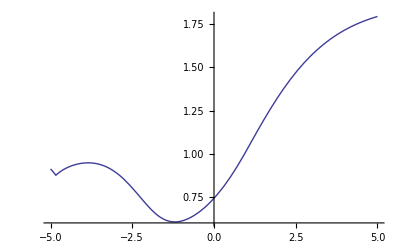
{89.562,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=3,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T]]},{k,-5,5}]]]
```

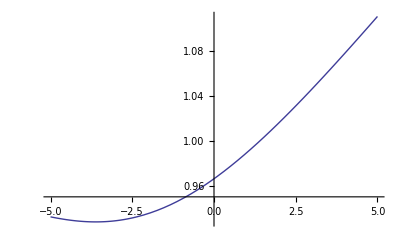
{4.187,-Graphics-}

```mathematica
Timing[Module[{ρ=0.300322,λv=0.4,θv=1,κ=0.8944,V=1,S0=0,T=11.7371,strikes,prices,inter},
strikes=Table[i,{i,-5,5,0.25}];
prices=(HestonNormalCallAux[ρ,λv,θv,κ,V,S0,#,T])& /@ strikes;
inter=Interpolation[Table[{strikes[[i]],NormalImplicitVol[S0,strikes[[i]],T,prices[[i]]]},{i,1,Length[strikes]}]];
Plot[{inter[k]},{k,-5,5},
PlotLegend->{"L=1","L=2","L=2.5","L=3"},LegendPosition->{1,0},PlotRange->All]]]
```

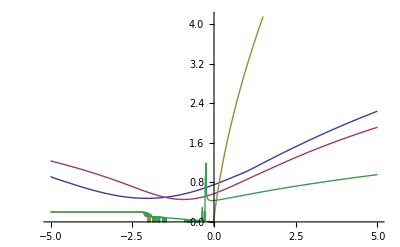
{514.593,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=3,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,1]],NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,2]],
NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,2.5]],NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,3]]},{k,-5,5},
PlotLegend->{"L=1","L=2","L=2.5","L=3"},LegendPosition->{1,0}]]]
```

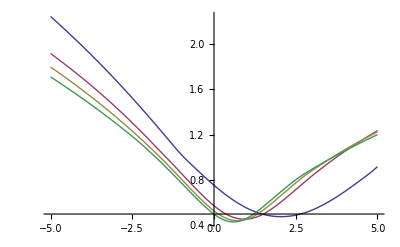
{256.5,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=1,κ=3,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,1]],NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,2]],
NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,2.5]],NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,3]]},{k,-5,5},
PlotLegend->{"L=1","L=2","L=2.5","L=3"},LegendPosition->{1,0}]]]
```

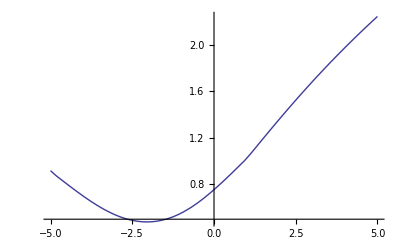
{53.937,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=3,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,2]]},{k,-5,5}]]]
```

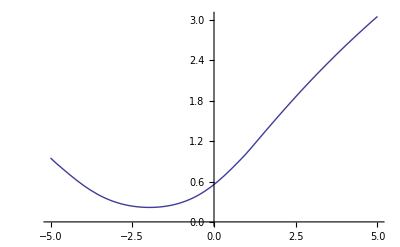
{64.594,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=5,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T]]},{k,-5,5}]]]
```

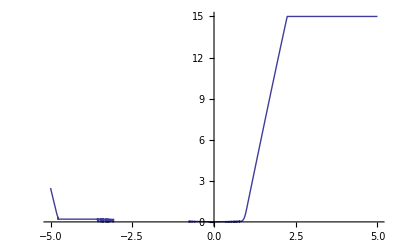
{181.172,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=100,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T]]},{k,-5,5}]]]
```

```mathematica
TransHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=Module[{θv1a,κ1a,V1a,θv2a,κ2a,V2a,S0a,ka,L},
L=√(1./(V1+V2));θv1a=L^2 θv1;θv2a=L^2 θv2;κ1a=L κ1;κ2a=L κ2;V1a=L^2 V1;V2a=L^2 V2;S0a=L S0;ka=L k;
HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,S0,ka,T]/L
]
```

```mathematica
TransHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_List,T_]:=Module[{θv1a,κ1a,V1a,θv2a,κ2a,V2a,S0a,ka,L},
L=√(1./(V1+V2));θv1a=L^2 θv1;θv2a=L^2 θv2;κ1a=L κ1;κ2a=L κ2;V1a=L^2 V1;V2a=L^2 V2;S0a=L S0;ka=L k;
(HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,S0,#,T]/L)& /@ ka
]
```

```mathematica
TransHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=Module[{θv1a,κ1a,V1a,θv2a,κ2a,V2a,θv3a,κ3a,V3a,S0a,ka,L},
L=√(1./(V1+V2+V3));θv1a=L^2 θv1;θv2a=L^2 θv2;θv3a=L^2 θv3;κ1a=L κ1;κ2a=L κ2;κ3a=L κ3;V1a=L^2 V1;V2a=L^2 V2;V3a=L^2 V3;S0a=L S0;ka=L k;
HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,ρ3,λv3,θv3a,κ3a,V3a,S0,ka,T]/L
]
```

```mathematica
TransHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_List,T_]:=Module[{θv1a,κ1a,V1a,θv2a,κ2a,V2a,θv3a,κ3a,V3a,S0a,ka,L},
L=√(1./(V1+V2+V3));θv1a=L^2 θv1;θv2a=L^2 θv2;θv3a=L^2 θv3;κ1a=L κ1;κ2a=L κ2;κ3a=L κ3;V1a=L^2 V1;V2a=L^2 V2;V3a=L^2 V3;S0a=L S0;ka=L k;
(HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,ρ3,λv3,θv3a,κ3a,V3a,S0,#,T]/L)& /@ ka
]
```

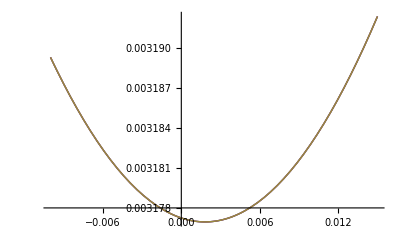
{15.047,-Graphics-}

```mathematica
Timing[Module[{ρ=0.0125053,λv=0.2,θv=0.0000101805,κ=0.0006281,V=0.0000101805,S0=0.003362,T=15,LimitGindinkin1=1,LimitGindinkin2=2,LimitGindinkin3=3},
vol1=Table[{k,NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,LimitGindinkin1]]},{k,-0.01,0.015,0.0005}];
vol2=Table[{k,NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,LimitGindinkin2]]},{k,-0.01,0.015,0.0005}];
vol3=Table[{k,NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,LimitGindinkin3]]},{k,-0.01,0.015,0.0005}];
inter1=Interpolation[vol1];inter2=Interpolation[vol2];inter3=Interpolation[vol3];
Plot[{inter1[k],inter2[k],inter3[k]},{k,-0.01,0.015}]]]
```

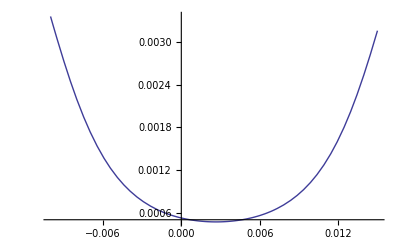
{10.266,-Graphics-}

```mathematica
Timing[Module[{ρ=0.0125053,λv=2,θv=0.0000101805,κ=0.6281,V=0.0000101805,S0=0.003362,T=15,LimitGindinkin1=1,LimitGindinkin2=1,LimitGindinkin3=1},
vol1=Table[{k,NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,LimitGindinkin1]]},{k,-0.01,0.015,0.0005}];
inter1=Interpolation[vol1];
Plot[{inter1[k]},{k,-0.01,0.015}]]]
```

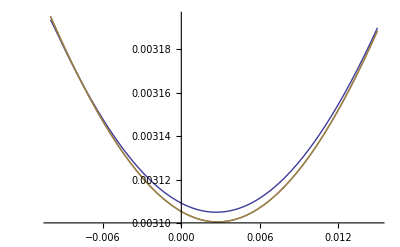
{20.453,-Graphics-}

```mathematica
Timing[Module[{ρ=0.0125053,λv=0.95,θv=0.0000101805,κ=0.006281,V=0.0000101805,S0=0.003362,T=15,LimitGindinkin1=1,LimitGindinkin2=2,LimitGindinkin3=3},
vol1=Table[{k,NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,LimitGindinkin1]]},{k,-0.01,0.015,0.0005}];
vol2=Table[{k,NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,LimitGindinkin2]]},{k,-0.01,0.015,0.0005}];
vol3=Table[{k,NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,LimitGindinkin3]]},{k,-0.01,0.015,0.0005}];
inter1=Interpolation[vol1];inter2=Interpolation[vol2];inter3=Interpolation[vol3];
Plot[{inter1[k],inter2[k],inter3[k]},{k,-0.01,0.015}]]]
```

## Verification

#### Standard

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.004,κ=0.02,V=0.004,S0=0,k={0.01,0.02},T=5},{HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T]}]]
```

{20.562,{{0.0511539,0.0468632},{{0.0542045,0.0497371},{0.0542045,0.0497371}},{{0.0511539,0.0468632},{0.0511539,0.0468632}}}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.0004,κ=0.02,V=0.0004,S0=0,k=0.01,T=5},{HestonNormalCall[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallN[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T]}]]
```

{5.609,{0.0197207,0.0197207,0.0197207}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.0004,κ=0.02,V=0.0004,S0=0,k=0.01,T=5},{HestonNormalCall[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallN[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T]}]]
```

{5.641,{0.0254532,0.0254532,0.0254532}}

#### preuve que la normalisation doit marcher

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.004,κ=0.02,V=0.004,S0=0,k=0.01,T=5,m={1,3,5,7,9,10}},(HestonNormalCallN[ρ,λv,#^2 θv,# κ,#^2 V,#S0,# k,T]/#)& /@m]]
```

{30.188,{0.0511539,0.0511539,0.0511539,0.0511539,0.0511539,0.0511539}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.004,κ=0.02,V=0.004,S0=0,k=0.01,T=5,m={1,2,3,4,5,6,7,8,9,10}},(HestonNormalCallTrace[ρ,λv,#^2 θv,# κ,#^2 V,#S0,# k,T]/#)& /@m]]
```

L=15.8114 κ1=0.316228 S01=0 k1=0.158114

L=7.90569 κ1=0.316228 S01=0 k1=0.158114

L=5.27046 κ1=0.316228 S01=0 k1=0.158114

L=3.95285 κ1=0.316228 S01=0 k1=0.158114

L=3.16228 κ1=0.316228 S01=0 k1=0.158114

L=2.63523 κ1=0.316228 S01=0 k1=0.158114

L=2.25877 κ1=0.316228 S01=0 k1=0.158114

L=1.97642 κ1=0.316228 S01=0 k1=0.158114

L=1.75682 κ1=0.316228 S01=0 k1=0.158114

L=1.58114 κ1=0.316228 S01=0 k1=0.158114

{0.094,{0.0511539,0.0511539,0.0511539,0.0511539,0.0511539,0.0511539,0.0511539,0.0511539,0.0511539,0.0511539}}

### Exploration des basse volatilités

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.01,κ=0.01,V=0.01,S0=0,k=0.01,T=5,m={0.1,0.01,0.005,0.001}},{HestonNormalCallTrace[ρ,λv,#θv,κ,#V,S0,k,T],HestonNormalCallN[ρ,λv,#θv,κ,#V,S0,k,T]}& /@m]]
```

L=31.6228 κ1=0.316228 S01=0 k1=0.316228

L=100. κ1=1. S01=0 k1=1.

L=141.421 κ1=1.41421 S01=0 k1=1.41421

L=316.228 κ1=3.16228 S01=0 k1=3.16228

{21.013,{{0.0234316,0.0234316},{0.00475905,0.0047787},{0.000368875,0.00263289},{0.0000517425,0.000567671}}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.55,θv=0.01,κ=0.01,V=0.01,S0=0,k=0.01,T=5,m={0.1,0.01,0.005,0.001}},{HestonNormalCallTrace[ρ,λv,#θv,κ,#V,S0,k,T],HestonNormalCallN[ρ,λv,#θv,κ,#V,S0,k,T]}& /@m]]
```

L=31.6228 κ1=0.316228 S01=0 k1=0.316228

L=100. κ1=1. S01=0 k1=1.

L=141.421 κ1=1.41421 S01=0 k1=1.41421

L=316.228 κ1=3.16228 S01=0 k1=3.16228

{20.249,{{0.0235315,0.0235315},{0.00494927,0.00494927},{0.00273352,0.00275524},{0.0000970247,0.000574895}}}

```mathematica
Timing[Module[{ρ=0.5,λv=2.1,θv=0.01,κ=0.01,V=0.01,S0=0,k=0.01,T=5,m={0.1,0.01,0.005,0.001}},{HestonNormalCallTrace[ρ,λv,#θv,κ,#V,S0,k,T],HestonNormalCallN[ρ,λv,#θv,κ,#V,S0,k,T]}& /@m]]
```

L=31.6228 κ1=0.316228 S01=0 k1=0.316228

L=100. κ1=1. S01=0 k1=1.

L=141.421 κ1=1.41421 S01=0 k1=1.41421

L=316.228 κ1=3.16228 S01=0 k1=3.16228

{20.514,{{0.0235347,0.0235347},{0.00492665,0.00492665},{0.00269693,0.00269693},{0.000452245,0.000452258}}}

on voit que le probleme provient du kappa et de k qui sont trop elevé. ce probleme est stabilise par la mean reversion

(ν normalisé | 0.0141421 | 0.0707107 | 0.212132 | 0.424264
√(2  λv θv/V) | 0.547723 | 0.547723 | 0.547723 | 0.547723)

FindRoot::jsing: Encountered a singular Jacobian at the point {u} = {0.0001}. Try perturbing the initial point(s).

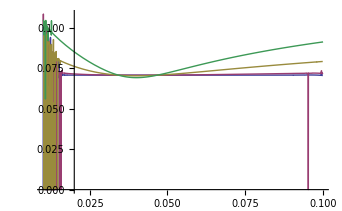
{290.328,-Graphics-}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.005,κ1=0.001,κ2=0.005,κ3=0.015,κ4=0.03,V=0.005,S0=0.04,k=0.05,T=5},
Print[{{"ν normalisé",ToString[κ1/√V],ToString[κ2/√V],ToString[κ3/√V],ToString[κ4/√V]},
{"√(2  λv θv/V)",ToString[√(2λv θv/V)],ToString[√(2λv θv/V)],ToString[√(2λv θv/V)],ToString[√(2λv θv/V)]}}//MatrixForm];
Plot[{
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,0.01,0.1},PlotRange->All]]]
```

(ν normalisé | 0.0141421 | 0.0707107 | 0.212132 | 0.424264
2 λ θ | 0.6 | 0.6 | 0.6 | 0.6)

FindRoot::jsing: Encountered a singular Jacobian at the point {u} = {0.0001}. Try perturbing the initial point(s).

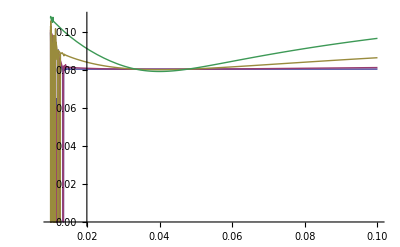
{176.047,-Graphics-}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.01,κ1=0.001,κ2=0.005,κ3=0.015,κ4=0.03,V=0.005,S0=0.04,k=0.05,T=5},
Print[{{"ν normalisé",ToString[κ1/√V],ToString[κ2/√V],ToString[κ3/√V],ToString[κ4/√V]},
{"√(2  λv θv/V)",ToString[√(2λv θv/V)],ToString[√(2λv θv/V)],ToString[√(2λv θv/V)],ToString[√(2λv θv/V)]}}//MatrixForm];
Plot[{
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,0.01,0.1},PlotRange->All]]]
```

(ν normalisé | 0.0141421 | 0.0707107 | 0.212132 | 0.424264
2 λ θ | 3. | 3. | 3. | 3.)

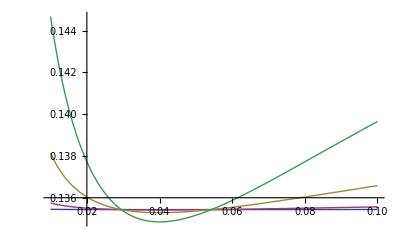
{71.219,-Graphics-}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.05,κ1=0.001,κ2=0.005,κ3=0.015,κ4=0.03,V=0.005,S0=0.04,k=0.05,T=5},
Print[{{"ν normalisé",ToString[κ1/√V],ToString[κ2/√V],ToString[κ3/√V],ToString[κ4/√V]},
{"√(2  λv θv/V)",ToString[√(2λv θv/V)],ToString[√(2λv θv/V)],ToString[√(2λv θv/V)],ToString[√(2λv θv/V)]}}//MatrixForm];
Plot[{
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,0.01,0.1},PlotRange->All]]]
```

#### Probleme non resolu

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.001,κ=0.2,V=0.001,S0=0,k=0.01,T=5},{HestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallTrace[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T]}]]
```

L=31.6228 κ1=6.32456 S01=0 k1=0.316228

{5.647,{0.00902545,0.00341168,0.00902545}}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.001,κ=0.01,V=0.001,S0=0,k=0.01,T=5},{HestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallTrace[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T]}]]
```

L=31.6228 κ1=0.316228 S01=0 k1=0.316228

{5.085,{0.0231591,0.0231591,0.0231591}}

```mathematica
(*version scalaire *)
```

#### Cas des tres petite vols

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.0000005,κ=0.0002,V=0.0000005,S0=-0.004,k=0.005,T=5},{HestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallTrace[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T]}]]
```

L=1414.21 κ1=0.282843 S01=-5.65685 k1=7.07107

{5.491,{2.12599×10^-10,2.18346×10^-10,-6.51397×10^-6}}

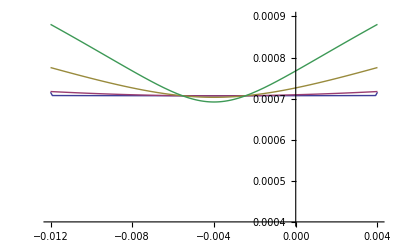
{11.747,-Graphics-}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.0000005,κ1=0.00001,κ2=0.00005,κ3=0.00015,κ4=0.0003,V=0.0000005,S0=-0.004,k=0.005,T=5},Plot[{
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,-0.012,0.004},PlotRange->{0.0004,0.0009}]]]
```

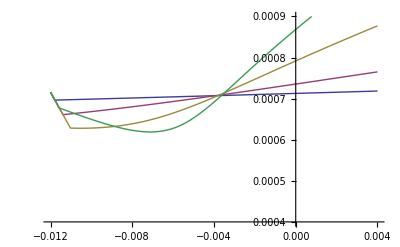
{9.251,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.0000005,κ1=0.00001,κ2=0.00005,κ3=0.00015,κ4=0.0003,V=0.0000005,S0=-0.004,k=0.005,T=5},Plot[{
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,-0.012,0.004},PlotRange->{0.0004,0.0009}]]]
```

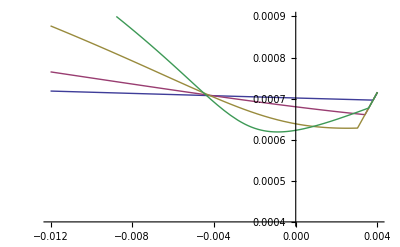
{9.953,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.0000005,κ1=0.00001,κ2=0.00005,κ3=0.00015,κ4=0.0003,V=0.0000005,S0=-0.004,k=0.005,T=5},Plot[{
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,-0.012,0.004},PlotRange->{0.0004,0.0009}]]]
```

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.001,κ=0.01,V=0.001,S0=0,k=0.01,T=5},{HestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallTrace[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T]}]]
```

L=31.6228 κ1=0.316228 S01=0 k1=0.316228

{6.022,{0.0231591,0.0231591,0.0231591}}

## LogNormal 1,2,3,4 et 5 Facteurs de vol

```mathematica
LogNormalHestonFondamentalTransform[ρ_,λv_,θv_,κ_,V_,ω_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ,η},
η=λv+ρ κ ⅈ ω;
argζ=η^2+κ^2(ω^2-ⅈ ω);
ζ=√argζ;
ψp =-η+ζ;
ψm =η+ζ;
A=-(θv λv (τ ψp+2 Log[(ψm+ⅇ^(-ζ τ) ψp)/(2ζ)]))/κ^2;
B=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
If[Re[A+B V]<-100,0,
ⅇ^(A+B V)]]
```

```mathematica
LogNormalHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ω_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,B1,argζ1,η1,ζ2,ψp2 ,ψm2,A2,B2,argζ2,η2,A},
η1=λv1+ρ1 κ1 ⅈ ω;
argζ1=η1^2+κ1^2(ω^2-ⅈ ω);
ζ1=√argζ1;
ψp1 =-η1+ζ1;
ψm1 =η1+ζ1;
B1=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
η2=λv2+ρ2 κ2 ⅈ ω;
argζ2=η2^2+κ2^2(ω^2-ⅈ ω);
ζ2=√argζ2;
ψp2 =-η2+ζ2;
ψm2 =η2+ζ2;
B2=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
A=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2;
If[Re[A+B1 V1+B2 V2]<-100,0,
ⅇ^(A+B1 V1+B2 V2)]
]
```

```mathematica
LogNormalHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ω_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,argζ1,η1,ζ2,ψp2 ,ψm2,argζ2,η2,ζ3,ψp3 ,ψm3,A3,argζ3,η3,B1,B2,B3,A},
η1=λv1+ρ1 κ1 ⅈ ω;
argζ1=(λv1+ρ1 κ1 ⅈ ω)^2+κ1^2(ω^2-ⅈ ω);
ζ1=√argζ1;
ψp1 =-η1+ζ1;
ψm1 =η1+ζ1;
B1=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
η2=λv2+ρ2 κ2 ⅈ ω;
argζ2=η2^2+κ2^2(ω^2-ⅈ ω);
ζ2=√argζ2;
ψp2 =-η2+ζ2;
ψm2 =η2+ζ2;
B2=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
η3=λv3+ρ3 κ3 ⅈ ω;
argζ3=η3^2+κ3^2(ω^2-ⅈ ω);
ζ3=√argζ3;
ψp3 =-η3+ζ3;
ψm3 =η3+ζ3;
B3=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ3  τ)))/(ψm3+ψp3 ⅇ^(-ζ3  τ));
A=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2-(θv3 λv3 (τ ψp3+2 Log[(ψm3+ⅇ^(-ζ3 τ) ψp3)/(2ζ3)]))/κ3^2;
If[Re[A+B1 V1+B2 V2+B3 V3]<-100,0,
ⅇ^(A+B1 V1+B2 V2+B3 V3)]
]
```

```mathematica
LogNormalHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ω_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,argζ1,η1,ζ2,ψp2 ,ψm2,argζ2,η2,ζ3,ψp3 ,ψm3,A3,argζ3,η3,ζ4,ψp4 ,ψm4,A4,argζ4,η4,B1,B2,B3,B4,A},
η1=λv1+ρ1 κ1 ⅈ ω;
argζ1=(λv1+ρ1 κ1 ⅈ ω)^2+κ1^2(ω^2-ⅈ ω);
ζ1=√argζ1;
ψp1 =-η1+ζ1;
ψm1 =η1+ζ1;
B1=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
η2=λv2+ρ2 κ2 ⅈ ω;
argζ2=η2^2+κ2^2(ω^2-ⅈ ω);
ζ2=√argζ2;
ψp2 =-η2+ζ2;
ψm2 =η2+ζ2;
B2=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
η3=λv3+ρ3 κ3 ⅈ ω;
argζ3=η3^2+κ3^2(ω^2-ⅈ ω);
ζ3=√argζ3;
ψp3 =-η3+ζ3;
ψm3 =η3+ζ3;
B3=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ3  τ)))/(ψm3+ψp3 ⅇ^(-ζ3  τ));
η4=λv4+ρ4 κ4 ⅈ ω;
argζ4=η4^2+κ4^2(ω^2-ⅈ ω);
ζ4=√argζ4;
ψp4 =-η4+ζ4;
ψm4 =η4+ζ4;
B4=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ4  τ)))/(ψm4+ψp4 ⅇ^(-ζ4  τ));
A=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2-(θv3 λv3 (τ ψp3+2 Log[(ψm3+ⅇ^(-ζ3 τ) ψp3)/(2ζ3)]))/κ3^2-(θv4 λv4 (τ ψp4+2 Log[(ψm4+ⅇ^(-ζ4 τ) ψp4)/(2ζ4)]))/κ4^2;
If[Re[A+B1 V1+B2 V2+B3 V3+B4 V4]<-100,0,
ⅇ^(A+B1 V1+B2 V2+B3 V3+B4 V4)]
]
```

```mathematica
LogNormalHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ρ5_,λv5_,θv5_,κ5_,V5_,ω_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,argζ1,η1,ζ2,ψp2 ,ψm2,argζ2,η2,ζ3,ψp3 ,ψm3,A3,argζ3,η3,ζ4,ψp4 ,ψm4,A4,argζ4,η4,ζ5,ψp5 ,ψm5,A5,argζ5,η5,B1,B2,B3,B4,B5,A},
η1=λv1+ρ1 κ1 ⅈ ω;
argζ1=(λv1+ρ1 κ1 ⅈ ω)^2+κ1^2(ω^2-ⅈ ω);
ζ1=√argζ1;
ψp1 =-η1+ζ1;
ψm1 =η1+ζ1;
B1=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
η2=λv2+ρ2 κ2 ⅈ ω;
argζ2=η2^2+κ2^2(ω^2-ⅈ ω);
ζ2=√argζ2;
ψp2 =-η2+ζ2;
ψm2 =η2+ζ2;
B2=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
η3=λv3+ρ3 κ3 ⅈ ω;
argζ3=η3^2+κ3^2(ω^2-ⅈ ω);
ζ3=√argζ3;
ψp3 =-η3+ζ3;
ψm3 =η3+ζ3;
B3=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ3  τ)))/(ψm3+ψp3 ⅇ^(-ζ3  τ));
η4=λv4+ρ4 κ4 ⅈ ω;
argζ4=η4^2+κ4^2(ω^2-ⅈ ω);
ζ4=√argζ4;
ψp4 =-η4+ζ4;
ψm4 =η4+ζ4;
B4=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ4  τ)))/(ψm4+ψp4 ⅇ^(-ζ4  τ));
η5=λv5+ρ5 κ5 ⅈ ω;
argζ5=η5^2+κ5^2(ω^2-ⅈ ω);
ζ5=√argζ5;
ψp5 =-η5+ζ5;
ψm5 =η5+ζ5;
B5=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ5  τ)))/(ψm5+ψp5 ⅇ^(-ζ5  τ));
A=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2-(θv3 λv3 (τ ψp3+2 Log[(ψm3+ⅇ^(-ζ3 τ) ψp3)/(2ζ3)]))/κ3^2-(θv4 λv4 (τ ψp4+2 Log[(ψm4+ⅇ^(-ζ4 τ) ψp4)/(2ζ4)]))/κ4^2-(θv5 λv5 (τ ψp5+2 Log[(ψm5+ⅇ^(-ζ5 τ) ψp5)/(2ζ5)]))/κ5^2;
If[Re[A+B1 V1+B2 V2+B3 V3+B4 V4+B5 V5]<-100,0,
ⅇ^(A+B1 V1+B2 V2+B3 V3+B4 V4+B5 V5)]
]
```

## LogNormal 1,2,3,4 et 5 Facteurs de vol : Integrands

#### Cas scalaire pour 1, 2,3,4 et 5 facteurs

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,S0_,K_,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0]) LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ω,T]LogNormalCallPayOffFourierTransform[K,α,a,ω]]
```

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,K_,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ω,T]LogNormalCallPayOffFourierTransform[K,α,a,ω]]
```

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,K_,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ω,T]LogNormalCallPayOffFourierTransform[K,α,a,ω]]
```

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,S0_,K_,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ω,T]LogNormalCallPayOffFourierTransform[K,α,a,ω]]
```

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ρ5_,λv5_,θv5_,κ5_,V5_,S0_,K_,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ρ5,λv5,θv5,κ5,V5,ω,T]LogNormalCallPayOffFourierTransform[K,α,a,ω]]
```

#### Cas vectoriel pour 1,2,3,4 et 5 facteurs

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,S0_,K_List,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ω,T]Table[LogNormalCallPayOffFourierTransform[K,α,a,ω],{i,1,Length[K]}]]
```

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,K_List,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ω,T]Table[LogNormalCallPayOffFourierTransform[K,α,a,ω],{i,1,Length[K]}]]
```

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,K_List,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ω,T]Table[LogNormalCallPayOffFourierTransform[K,α,a,ω],{i,1,Length[K]}]]
```

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,S0_,K_List,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ω,T]LogNormalCallPayOffFourierTransform[K,α,a,ω]]
```

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ρ5_,λv5_,θv5_,κ5_,V5_,S0_,K_List,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ρ5,λv5,θv5,κ5,V5,ω,T]LogNormalCallPayOffFourierTransform[K,α,a,ω]]
```

```mathematica
Clear[LogNormalHestonCallIntegrand]
```

```mathematica
Module[{ρ=-0.5,λv=0.15,θv=0.01,κ=0.5,V=0.01,S0=0.05,λ1=0.05,λ2=0.5,λ3=0.9,T=0.5,k=0.01,ω=1.2},
LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω]]
```

0.00175681

```mathematica
Module[{ρ=-0.5,λv=0.15,θv=0.01,κ=0.5,V=0.01,S0=0.05,λ1=0.05,λ2=0.5,λ3=0.9,T=0.5,k=0.01,ω=1.2},
LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω,T]]
```

-0.003562-0.000259168 ⅈ

## Shift et parametres d' integration

le shift ici sera pris a 0.5. A ce shift sera adapté les constante de la procedure d' integration.

Exemple d' integrand pour des shift differents

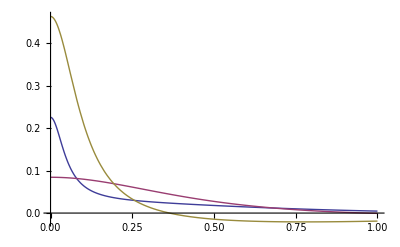
{0.203,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.01,κ=0.5,V=1,S0=0.05,λ1=0.05,λ2=0.5,λ3=0.9,T=0.5,k=0.01,ω},
Plot[{LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ1 ⅈ],
LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ2 ⅈ],
LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ3 ⅈ]},{ω,0,1},PlotRange->All]
]]
```

on voit que le shift determine a lui tout seul les parametre

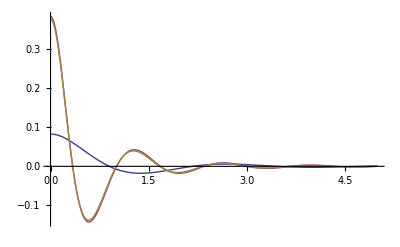
{1.328,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.01,κ=0.5,V=0.01,S0=1,λ1=0.05,λ2=0.5,λ3=0.9,T=30,k=0.01,ω},
Plot[{LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,2,T,ω +λ2 ⅈ],
LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ2 ⅈ],
LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ2 ⅈ]},{ω,0,5},PlotRange->All]
]]
```

#### Determination de parametres d' integration de la version normalisée

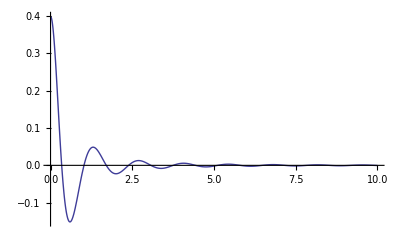
{0.344,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.1,λv=0.15,θv=0.01,κ=2,V=0.01,S0=1,λ1=0.5,T=10,k=0.01,ω},
Plot[{Re[ⅇ^(-ⅈ (ω+ⅈ λ1)  Log[S0])LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω+ⅈ λ1,T]LogNormalCallPayOffFourierTransform[k,ω+ⅈ λ1]]},{ω,0,10},PlotRange->All]
]]
```

## LogNormal 1,2,3,4 et 5 Facteurs de vol : Implementations

### Implementation mathematica de reference

```mathematica
LogHestonNormalCallN[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
LogHestonNormalCallN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,1,1,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
LogHestonNormalCallN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,1,1,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
LogHestonNormalCallN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,S0,k,1,1,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
LogHestonNormalCallN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ρ5_,λv5_,θv5_,κ5_,V5_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ρ5,λv5,θv5,κ5,V5,S0,k,1,1,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

### Implementation Operationnelle

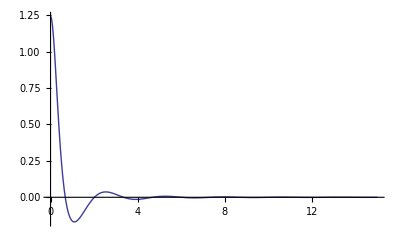
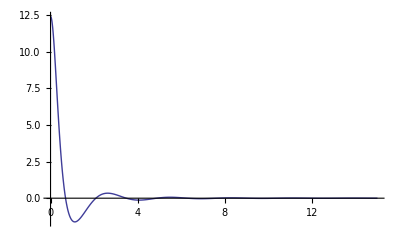
{0.687,{-Graphics-,-Graphics-}}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.01,κ=0.5,V=0.01,S0=1,T=30,k=0.01,ω},
{Plot[{LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,S0/10,1,1,T,ω +0.5 ⅈ]},{ω,0,15},PlotRange->All],
Plot[{LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,S0 10,1,1,T,ω +0.5 ⅈ]},{ω,0,15},PlotRange->All]}
]]
```

```mathematica
LogHestonNormalCallAux[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,2,10^(-10),1000,2,LegendreCoeffs[20]][[2]]]]
```

```mathematica
LogHestonNormalCallAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
LogHestonNormalCallAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
LogHestonNormalCallAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
LogHestonNormalCallAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ρ5_,λv5_,θv5_,κ5_,V5_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ρ5,λv5,θv5,κ5,V5,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
(*version Vecteur *)
```

### Implementation Normalisée

```mathematica
LogHestonNormalCall[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{},
S0 LogHestonNormalCallAux[ρ,λv,θv,κ,V,1,k/S0,T]
]
```

```mathematica
LogHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=Module[{},
S0 LogHestonNormalCallAux[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,1,k/S0,T]
]
```

```mathematica
LogHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=Module[{},
S0 LogHestonNormalCallAux[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,1,k/S0,T]
]
```

```mathematica
LogHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,S0_,k_,T_]:=Module[{},
S0 LogHestonNormalCallAux[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,1,k/S0,T]
]
```

```mathematica
LogHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ρ5_,λv5_,θv5_,κ5_,V5_,S0_,k_,T_]:=Module[{},
S0 LogHestonNormalCallAux[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ρ5,λv5,θv5,κ5,V5,1,k/S0,T]
]
```

## Implentation des densitée

```mathematica
LogHestonNormalDensité[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{shift=S0/1000},Max[0,(LogHestonNormalCall[ρ,λv,θv,κ,V,S0,k+shift,T]+LogHestonNormalCall[ρ,λv,θv,κ,V,S0,k-shift,T]-2LogHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T])/(shift^2)]]
```

```mathematica
LogHestonNormalDensité[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=Module[{shift=S0/1000},Max[0,(LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k+shift,T]+LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k-shift,T]-2LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,T])/(shift^2)]]
```

```mathematica
LogHestonNormalDensité[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=Module[{shift=S0/1000},Max[0,(LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k+shift,T]+LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k-shift,T]-2LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,T])/(shift^2)]]
```

```mathematica
LogHestonNormalDensité[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,S0_,k_,T_]:=Module[{shift=S0/1000},Max[0,(LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,S0,k+shift,T]+LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,S0,k-shift,T]-2LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,S0,k,T])/(shift^2)]]
```

```mathematica
LogHestonNormalDensité[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ρ5_,λv5_,θv5_,κ5_,V5_,S0_,k_,T_]:=Module[{shift=S0/1000},Max[0,(LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ρ5,λv5,θv5,κ5,V5,S0,k+shift,T]+LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ρ5,λv5,θv5,κ5,V5,S0,k-shift,T]-2LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ρ5,λv5,θv5,κ5,V5,S0,k,T])/(shift^2)]]
```

## Implementation des variances

### Variance par integration

```mathematica
CoeffBasedVariance[density_,coeffs_]:=Module[{n=Length[coeffs],densitytable,Expectation=0,variance=0,normalisation=0,i},
densitytable=Table[density[coeffs[[i,1]]],{i,1,n}];
Do[normalisation+= densitytable[[i]] coeffs[[i,2]],{i,1,n}];
Do[Expectation+=coeffs[[i,1]] densitytable[[i]] coeffs[[i,2]],{i,1,n}];Expectation/=normalisation;
Do[variance+=(coeffs[[i,1]]-Expectation)^2 densitytable[[i]] coeffs[[i,2]],{i,1,n}];
Print["normalisation=",normalisation," Expectation=",Expectation," variance=",variance];
variance/=normalisation;
variance]
```

```mathematica
CoeffBasedVariance[density_,coeffs_,Expectation_]:=Module[{n=Length[coeffs],densitytable,variance=0,i},
densitytable=Table[density[coeffs[[i,1]]],{i,1,n}];
Do[variance+=(coeffs[[i,1]]-Expectation)^2 densitytable[[i]] coeffs[[i,2]],{i,1,n}];
variance]
```

```mathematica
LogHestonNormalVariance2[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=CoeffBasedIntegrate[((#-S0)^2 LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,S0/5,6S0]]
```

```mathematica
LogHestonNormalVariance3[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=CoeffBasedVariance[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,S0/5,6S0]]
```

```mathematica
LogHestonNormalEsperance[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=CoeffBasedIntegrate[((#)LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,S0/5,6S0]]
```

```mathematica
LogHestonNormalNormalisation[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=CoeffBasedIntegrate[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,S0/5,6S0]]
```

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{LogHestonNormalEsperance[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalNormalisation[ρ,λv,θv,κ,V,S0,k,T]}]]
```

{2.636,{0.0489338,0.990318}}

### Variance du Heston normal a maturité

dV_s=λ(V_∞-V_s)ds+dM_s  donc V_s=∫_0^s (λ(V_∞-V_u)du+dM_u  )ⅆu

Soit  L_T=∫_0^T V_s ⅆs==

E[L_T]=∫_0^T E[V_s]ⅆs

or je sais que E[V_s]=V_∞+(V_0-V_∞)ⅇ^(-λ s)

donc

E[L_T]=∫_0^T (V_∞+(V_0-V_∞)ⅇ^(-λ s))ⅆs=T  V_∞ + (V_0-V_∞) ((1-ⅇ^(-λ T))/λ)

### Proxy de variance

```mathematica
Simplify[Integrate[ⅇ^x(ⅇ^(-(x-x0)^2/(2 σ^2)))/(√(2π)σ),{x,-∞,∞}],σ>0]
```

ⅇ^(x0+σ^2/2)

```mathematica
Simplify[Integrate[ⅇ^(2x)(ⅇ^(-(x-x0)^2/(2 σ^2)))/(√(2π)σ),{x,-∞,∞}],σ>0]
```

ⅇ^(2 (x0+σ^2))

donc variance=ⅇ^(2 (x0+σ^2))-(ⅇ^(x0+σ^2/2))^2=

```mathematica
Simplify[ⅇ^(2 (x0+σ^2))-(ⅇ^(x0+σ^2/2))^2]
```

ⅇ^(2 x0+σ^2) (-1+ⅇ^(σ^2))

```mathematica
LogHestonNormalVarianceProxy[ρ_,λv_,θv_,κ_,V_,S0_,T_]:=Module[{Vlog},
Vlog=θv T+(V -θv)((1-ⅇ^(-λv T))/λv);
S0^2 ⅇ^Vlog(ⅇ^Vlog-1)]
```

```mathematica
LogHestonNormalVarianceProxy[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,T_]:=Module[{Vlog1,Vlog2},
Vlog1=θv1 T+(V1 -θv1)((1-ⅇ^(-λv1 T))/λv1);
Vlog2=θv2 T+(V2 -θv2)((1-ⅇ^(-λv2 T))/λv2);
S0^2 ⅇ^(Vlog1+Vlog2)(ⅇ^(Vlog1+Vlog2)-1)
]
```

```mathematica
LogHestonNormalVarianceProxy[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,T_]:=Module[{Vlog1,Vlog2,Vlog3},
Vlog1=θv1 T+(V1 -θv1)((1-ⅇ^(-λv1 T))/λv1);
Vlog2=θv2 T+(V2 -θv2)((1-ⅇ^(-λv2 T))/λv2);
Vlog3=θv3 T+(V3 -θv3)((1-ⅇ^(-λv3 T))/λv3);
S0^2 ⅇ^(Vlog1+Vlog2+Vlog3)(ⅇ^(Vlog1+Vlog2+Vlog3)-1)
]
```

```mathematica
LogHestonNormalVarianceProxy[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,S0_,T_]:=Module[{Vlog1,Vlog2,Vlog3,Vlog4},
Vlog1=θv1 T+(V1 -θv1)((1-ⅇ^(-λv1 T))/λv1);
Vlog2=θv2 T+(V2 -θv2)((1-ⅇ^(-λv2 T))/λv2);
Vlog3=θv3 T+(V3 -θv3)((1-ⅇ^(-λv3 T))/λv3);
Vlog4=θv4 T+(V4 -θv4)((1-ⅇ^(-λv4 T))/λv4);
S0^2 ⅇ^(Vlog1+Vlog2+Vlog3+Vlog4)(ⅇ^(Vlog1+Vlog2+Vlog3+Vlog4)-1)
]
```

```mathematica
LogHestonNormalVarianceProxy[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ρ5_,λv5_,θv5_,κ5_,V5_,S0_,T_]:=Module[{Vlog1,Vlog2,Vlog3,Vlog4,Vlog5},
Vlog1=θv1 T+(V1 -θv1)((1-ⅇ^(-λv1 T))/λv1);
Vlog2=θv2 T+(V2 -θv2)((1-ⅇ^(-λv2 T))/λv2);
Vlog3=θv3 T+(V3 -θv3)((1-ⅇ^(-λv3 T))/λv3);
Vlog4=θv4 T+(V4 -θv4)((1-ⅇ^(-λv4 T))/λv4);
Vlog5=θv5 T+(V5 -θv5)((1-ⅇ^(-λv5 T))/λv5);
S0^2 ⅇ^(Vlog1+Vlog2+Vlog3+Vlog4+Vlog5)(ⅇ^(Vlog1+Vlog2+Vlog3+Vlog4+Vlog5)-1)
]
```

### Exemples

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{LogHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T]}]]
```

{5.07,{0.00681842,0.00681842,0.00681842}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{LogHestonNormalCall[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallAux[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallN[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T]}]]
```

{5.188,{0.0107732,0.0107732,0.0107732}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{LogHestonNormalCall[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallAux[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallN[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T]}]]
```

{4.765,{0.0182362,0.0182362,0.0182362}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{LogHestonNormalCall[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallAux[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallN[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T]}]]
```

{5.219,{0.0137363,0.0137363,0.0137363}}

#### Verification de la convergence des integrales

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{LogHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T]}]]
```

{5.07,{0.00681842,0.00681842,0.00681842}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,k,T]}]]
```

{0.203,{0.000362438,0.000362438,0.000362438}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,k,T]}]]
```

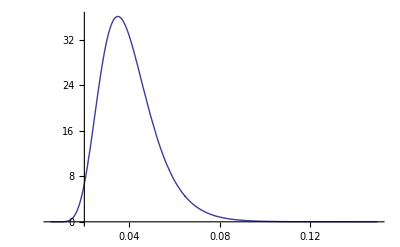
{30.81,-Graphics-}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.05,κ1=0.001,κ2=0.005,κ3=0.015,κ4=0.03,V=0.005,S0=0.04,k=0.05,T=5},Plot[{
LogHestonNormalDensité[ρ,λv,θv,κ1,V,S0,k,T]},{k,0.005,0.15},PlotRange->All]]]
```

```mathematica
LogHestonNormalVariance2[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_,n1_,n2_]:=CoeffBasedVariance[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[60,S0/n1,n2 S0]]
```

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{
LogHestonNormalVariance3[ρ,λv,θv,κ,V,S0,k,T,5,5],
LogHestonNormalVariance3[ρ,λv,θv,κ,V,S0,k,T,10,10],
LogHestonNormalVariance3[ρ,λv,θv,κ,V,S0,k,T,10,20], S0^2 V T,LogHestonNormalVarianceProxy[ρ,λv,θv,κ,V,S0,T]}]]
```

{1.35891×10^-13,{LogHestonNormalVariance3[0.5,0.15,0.04,0.2,0.04,0.05,0.055,5,5,5],LogHestonNormalVariance3[0.5,0.15,0.04,0.2,0.04,0.05,0.055,5,10,10],LogHestonNormalVariance3[0.5,0.15,0.04,0.2,0.04,0.05,0.055,5,10,20],0.0005,0.000676055}}

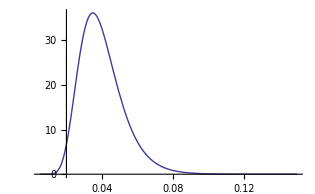
{30.81,-Graphics-}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.05,κ1=0.001,κ2=0.005,κ3=0.015,κ4=0.03,V=0.005,S0=0.04,k=0.05,T=5},Plot[{
LogHestonNormalDensité[ρ,λv,θv,κ1,V,S0,k,T]},{k,0.005,0.15},PlotRange->All]]]
```

normalisation=0.989834 Expectation=0.0494119 variance=0.000620144

normalisation=0.998193 Expectation=0.049213 variance=0.000623134

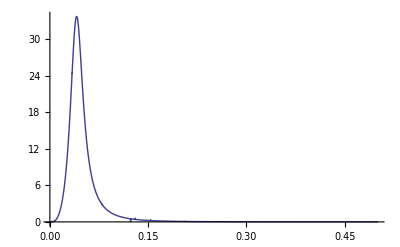
{256.156,{-Graphics-,0.000626514,0.000624262,0.00113072,0.000517143,0.0005,0.00268221}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,T=5},
{Plot[{LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,k,T]},{k,0.001,0.5},PlotRange->All],
CoeffBasedVariance[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,S0/5,6S0]],
CoeffBasedVariance[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[40,0.005,0.3]],
LogHestonNormalVariance[ρ,λv,θv,κ,V,S0,T],
CoeffBasedVariance[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,0.01,0.22],S0],
 S0^2 V T,
LogHestonNormalVarianceProxy[ρ,λv,θv,κ,V,S0,T]}]]
```

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.04,κ=0.4,V=0.04,S0=1,T=15},
√(LogHestonNormalVariance[ρ,λv,θv,κ,V,S0,T]/(S0 S0 T))]]
```

{0.219,0.14762}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.01,κ=0.5,V=0.01,S0=1,T=30,k=0.01,ω},
{Plot[{LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,S0/10,1,1,T,ω +0.5 ⅈ]},{ω,0,15},PlotRange->All],
Plot[{LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,S0 10,1,1,T,ω +0.5 ⅈ]},{ω,0,15},PlotRange->All]}
]]
```

{0.687,{-Graphics-,-Graphics-}}

```mathematica
LogHestonNormalCallAux[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[12],
10,2,10^(-10),1000,2,LegendreCoeffs[30]][[2]]]]
```

normalisation=0.999665 Expectation=0.0500096 variance=0.000554284

normalisation=0.96135 Expectation=0.0471624 variance=0.000331847

prixheston=0.00885103 prixBS=0.0191462 VarianceNaive=0.2 VarianceCorrigée=0.0427415

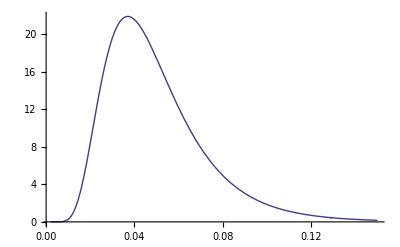
{44.469,{-Graphics-,0.00055447,0.000345189,0.000339588,0.0005,0.0427415}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.002,V=0.04,S0=0.05,T=5},
{Plot[{LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,k,T]},{k,0.002,0.15},PlotRange->All],
CoeffBasedVariance[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,S0/5,6S0]],
CoeffBasedVariance[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,0.01,0.1]],
CoeffBasedVariance[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,0.01,0.1],S0],
 S0^2 V T,LogHestonNormalVarianceProxy[ρ,λv,θv,κ,V,S0,T]}]]
```

#### ca s' ecroule a 30 ans !

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=30},{LogHestonNormalEsperance[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalNormalisation[ρ,λv,θv,κ,V,S0,k,T],
LogHestonNormalVariance[ρ,λv,θv,κ,V,S0,k,T]/LogHestonNormalNormalisation[ρ,λv,θv,κ,V,S0,k,T],
LogHestonNormalVariance2[ρ,λv,θv,κ,V,S0,k,T], S0^2 V T}]]
```

{3.494,{0.0370348,0.871985,0.00147998,0.00142331,0.003}}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.01,κ=0.5,V=0.01,S0=1,λ1=0.05,λ2=0.5,λ3=0.9,T=30,k=0.01,ω},
Plot[{LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,2,T,ω +λ2 ⅈ]},{ω,0,5},PlotRange->All]
]]
```

#### Verification du Smile

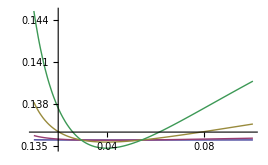
{42.109,-Graphics-}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.05,κ1=0.001,κ2=0.005,κ3=0.015,κ4=0.03,V=0.005,S0=0.04,k=0.05,T=5},Plot[{
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,0.01,0.1},PlotRange->All]]]
```

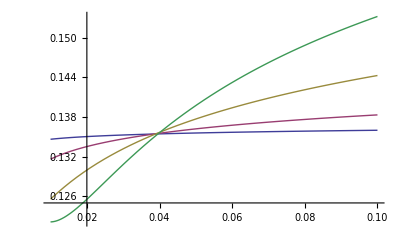
{14.625,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.05,κ1=0.001,κ2=0.005,κ3=0.015,κ4=0.03,V=0.005,S0=0.04,k=0.05,T=5},Plot[{
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,0.01,0.1},PlotRange->All]]]
```

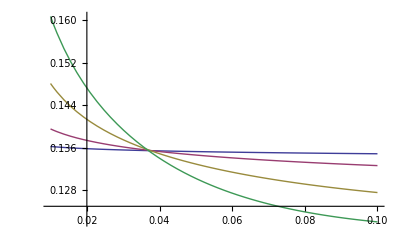
{11.75,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.05,κ1=0.001,κ2=0.005,κ3=0.015,κ4=0.03,V=0.005,S0=0.04,k=0.05,T=5},Plot[{
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,0.01,0.1},PlotRange->All]]]
```

## Lognormal Shifté

### Dynamique β>0

dF/(β F+(1-β )F_0)=∑_(i=1)^N √V_i dW_i

#### pricing

donc

dF/(F+(1-β )/β F_0)=∑_(i=1)^N √(β^2 V_i)dW_i

c'est donc un lognormal ou l'on decale F_0 ainsi que les strike de la valeur:(1-β )/β F_0  et on modifie le dynamique en multipliant V_(i,0)  et θ_i par β^2 ainsi que κ_i par β

Fonction de packaging

### Dynamique β<0 on cree β^*=-β

dF/((1+β^* )F_0-β^* F)=∑_(i=1)^N √V_i dW_i

donc

dF/(F-(1+β^* )/β^*F_0)=∑_(i=1)^N √(β^2 V_i)d(W̄)_i  (avec (W̄)_i=-W_i et ρ = -ρ_initial)

c'est donc un lognormal ou l'on decale F_0 ainsi que les strike de la valeur:-(1+β^* )/β^*F_0  et on modifie le dynamique en multipliant V_(i,0)  et θ_i par (β^*)^2 ainsi que κ_i par β^*

mais les decalage ameneront dans le territoire F < 0, donc on doit modeliser - F

Si on modelise (-F) on a :

(d(-F))/((1+β^* )(-F_0)-β^*(- F))=∑_(i=1)^N √V_i dW_i

Soit H = -F , on a donc

dH/((1+β^* )(H_0)-β^*(H))=∑_(i=1)^N √V_i dW_i

avec H_0=-F_0

c'est donc un lognormal ou l'on decale H_0 ainsi que les strike de la valeur:-(1+β^* )/β^*H_0  et on modifie le dynamique en multipliant V_(i,0)  et θ_i par (β^*)^2 ainsi que κ_i par β^*

#### Pricing

```mathematica
ShiftedLogHestonNormalCallAux[β_,ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{},
LogHestonNormalCall[ρ,λv,β^2 θv,Abs[β] κ,β^2 V,S0+(1-β )/β S0,k+(1-β )/β S0,T]] /; β>=0
```

```mathematica
ShiftedLogHestonNormalCallAux[β_,ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{},
LogHestonNormalCall[-ρ,λv,β^2 θv,Abs[β] κ,β^2 V,-S0-(1-β )/β S0,-k-(1-β )/β S0,T]] /; β<0
```

```mathematica
Timing[Module[{β=-0.03,ρ=-0.5,λv=0.15,θv=0.04,κ=1,V=0.04,S0=0.05,k=0.045,T=5},ShiftedLogHestonNormalCallAux[β,ρ,λv,θv,κ,V,S0,k,T]]]
```

sum initiale=2.65542

sum initiale=2.65542

{3.578,0.00316004}

### Visualisation des problemes au voisinage de β = 0

```mathematica
ShiftedLogHestonNormalCall0[β_,ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{},
If[β==0,HestonNormalCall[ρ,λv,S0^2 θv,S0 κ,S0^2 V,S0,k,T],ShiftedLogHestonNormalCallAux[β,ρ,λv,θv,κ,V,S0,k,T]]]
```

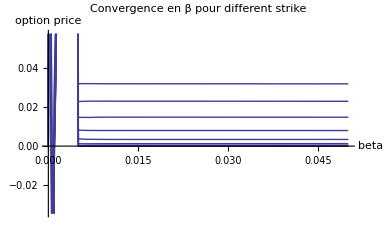
{247.485,-Graphics-}

```mathematica
Timing[Module[{β={-0.1,-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.001,-0.0005,-0.0001,0,0.0001,0.0005,0.001,0.005,0.006,0.007,0.008,0.009,0.01,0.015,0.02,.03,0.04,0.05,0.1},ρ=-0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=Table[0.01 i,{i,2,12}],T=5},res=Table[ShiftedLogHestonNormalCall0[β[[j]],ρ,λv,θv,κ,V,S0,k[[i]],T],{i,1,Length[k]},{j,1,Length[β]}];
res1=Table[Interpolation[Transpose[{β,res[[i]]}]],{i,1,Length[res]}];
Plot[Table[res1[[i]][x],{i,1,Length[res1]}],{x,-0.05,0.05},PlotLabel->"Convergence en β pour different strike",AxesLabel->{"beta","option price"}]]]
```

### Implementation integrant une interpolation lineaire

```mathematica
ShiftedLogHestonNormalCall1[β_,ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{βL=0.02},
If[(β<βL)&& (β>=0),
(βL-β)/βL HestonNormalCall[ρ,λv,S0^2 θv,S0 κ,S0^2 V,S0,k,T]+β/βL ShiftedLogHestonNormalCallAux[βL,ρ,λv,θv,κ,V,S0,k,T],
If[(β>-βL)&& (β<0),
(βL-Abs[β])/βL HestonNormalCall[ρ,λv,S0^2 θv,S0 κ,S0^2 V,S0,k,T]+Abs[β]/βL ShiftedLogHestonNormalCallAux[-βL,ρ,λv,θv,κ,V,S0,k,T],
ShiftedLogHestonNormalCallAux[β,ρ,λv,θv,κ,V,S0,k,T]]]]
```

```mathematica
Timing[Module[{β=-0.03,ρ=-0.5,λv=0.15,θv=0.04,κ=1,V=0.04,S0=0.05,k=0.045,T=5},ShiftedLogHestonNormalCallAux[β,ρ,λv,θv,κ,V,S0,k,T]]]
```

{3.61,0.00734534}

### volvol normalisée = 0.25 pour 2 λ θ = 0.3

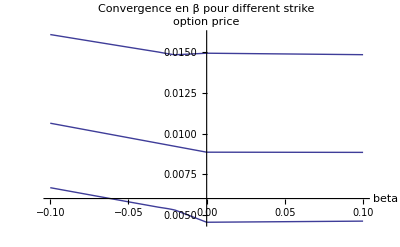
{75.375,-Graphics-}

```mathematica
Timing[Module[{β={-0.1,-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.001,-0.0005,-0.0001,0,0.0001,0.0005,0.001,0.005,0.006,0.007,0.008,0.009,0.01,0.015,0.02,.03,0.04,0.05,0.1},ρ=-0.5,λv=0.15,θv=0.04,κ=0.05,V=0.04,S0=0.05,k=Table[0.01 i,{i,4,6}],T=5},res=Table[ShiftedLogHestonNormalCall1[β[[j]],ρ,λv,θv,κ,V,S0,k[[i]],T],{i,1,Length[k]},{j,1,Length[β]}];
res1=Table[Interpolation[Transpose[{β,res[[i]]}]],{i,1,Length[res]}];
Plot[Table[res1[[i]][x],{i,1,Length[res1]}],{x,-0.1,0.1},PlotLabel->"Convergence en β pour different strike",AxesLabel->{"beta","option price"}]]]
```

```mathematica
0.2/√0.04
```

1.

### volvol normalisée = 1 pour 2 λ θ = 0.3

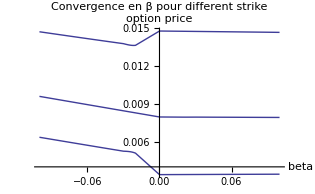
{143.906,-Graphics-}

```mathematica
Timing[Module[{β={-0.1,-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.001,-0.0005,-0.0001,0,0.0001,0.0005,0.001,0.005,0.006,0.007,0.008,0.009,0.01,0.015,0.02,.03,0.04,0.05,0.1},ρ=-0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=Table[0.01 i,{i,4,6}],T=5},res=Table[ShiftedLogHestonNormalCall1[β[[j]],ρ,λv,θv,κ,V,S0,k[[i]],T],{i,1,Length[k]},{j,1,Length[β]}];
res1=Table[Interpolation[Transpose[{β,res[[i]]}]],{i,1,Length[res]}];
Plot[Table[res1[[i]][x],{i,1,Length[res1]}],{x,-0.1,0.1},PlotLabel->"Convergence en β pour different strike",AxesLabel->{"beta","option price"}]]]
```

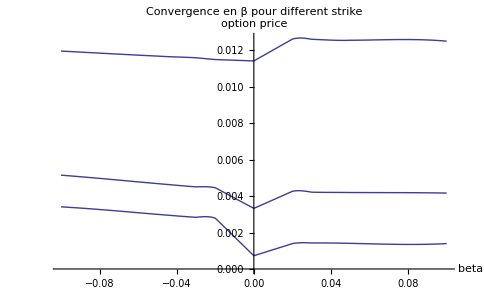
{81.656,-Graphics-}

```mathematica
Timing[Module[{β={-0.1,-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.001,-0.0005,-0.0001,0,0.0001,0.0005,0.001,0.005,0.006,0.007,0.008,0.009,0.01,0.015,0.02,.03,0.04,0.05,0.1},ρ=-0.5,λv=0.15,θv=0.04,κ=1,V=0.04,S0=0.05,k=Table[0.01 i,{i,4,6}],T=5},res=Table[ShiftedLogHestonNormalCall1[β[[j]],ρ,λv,θv,κ,V,S0,k[[i]],T],{i,1,Length[k]},{j,1,Length[β]}];
res1=Table[Interpolation[Transpose[{β,res[[i]]}]],{i,1,Length[res]}];
Plot[Table[res1[[i]][x],{i,1,Length[res1]}],{x,-0.1,0.1},PlotLabel->"Convergence en β pour different strike",AxesLabel->{"beta","option price"}]]]
```

### Implementation integrant une interpolation Th

```mathematica
BetaPositifApprox[βini_,βL_,force_]:=βL ⅇ^(-force βini)+(1-βL ⅇ^-force) βini
```

```mathematica
BetaNegatifApprox[βini_,βL_,force_]:=-βL ⅇ^(force βini)+(1-βL ⅇ^-force) βini
```

```mathematica
InterpolDenfer[x_,m_,q_]:=Module[{y,z},
y=2 (1.0-x)^q-1;
z= ArcTanh[y];
1-(Tanh[m z]+1)/2]
```

```mathematica
InterpolDenfer[0.5,2,1]
```

0.5

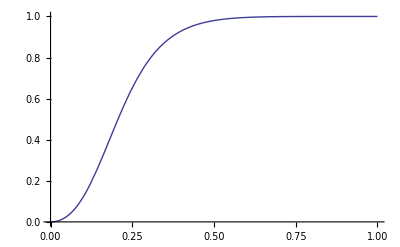

```mathematica
Plot[InterpolDenfer[x,2,3],{x,0,1}]
```

```mathematica
ShiftedLogHestonNormalCallAux[β_,ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{},
LogHestonNormalCall[ρ,λv,β^2 θv,Abs[β] κ,β^2 V,S0+(1-β )/β S0,k+(1-β )/β S0,T]] /; β>=0
```

```mathematica
ShiftedLogHestonNormalCallAux[β_,ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{},
LogHestonNormalCall[-ρ,λv,β^2 θv,Abs[β] κ,β^2 V,S0-(1-β )/β S0,k-(1-β )/β S0,T]] /; β<0
```

```mathematica
ShiftedLogHestonNormalCall2[β_,ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{βL=0.02,βeff,αN,αLN,force=1,m=2,q=3},
If[ (β>=0),αLN=InterpolDenfer[β,m,q];αN=1-αLN;
βeff=BetaPositifApprox[β,βL,force];
(*Print["β>0 : αLN=",αLN," βeff=",βeff," HestonNormalCall[ρ,λv,S0^2θv,S0 κ,S0^2V,S0,k,T]=", HestonNormalCall[ρ,λv,S0^2 θv,S0 κ,S0^2 V,S0,k,T],"  ShiftedLogHestonNormalCallAux[βeff,ρ,λv,θv,κ,V,S0,k,T]=", ShiftedLogHestonNormalCallAux[βeff,ρ,λv,θv,κ,V,S0,k,T]];*);
αN HestonNormalCall[ρ,λv,S0^2 θv,S0 κ,S0^2 V,S0,k,T]+αLN ShiftedLogHestonNormalCallAux[βeff,ρ,λv,θv,κ,V,S0,k,T],
If[ (β<0),αLN=InterpolDenfer[-β,m,q];αN=1-αLN;
βeff=BetaNegatifApprox[β,βL,force];
(* Print["β<0 : αLN=",αLN," βeff=",βeff];*)
αN HestonNormalCall[ρ,λv,S0^2 θv,S0 κ,S0^2 V,S0,k,T]+αLN ShiftedLogHestonNormalCallAux[βeff,ρ,λv,θv,κ,V,S0,k,T],
ShiftedLogHestonNormalCallAux[β,ρ,λv,θv,κ,V,S0,k,T]]]]
```

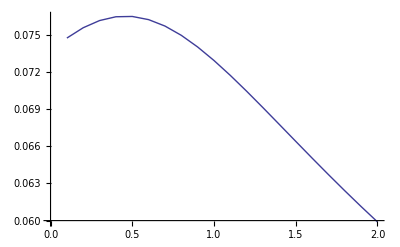

```mathematica
Module[{β=0,ρ=0.5,λv=0.15,θv=1,κ=2,V=1,S0=0.1,k=0.1,T=5,zz},
ListPlot[Table[{κ,ShiftedLogHestonNormalCallAux[β,ρ,λv,θv,κ,V,S0,k,T]},{κ,0.1,2,0.1}],Joined->True]]
```

```mathematica
Module[{β=0.5,ρ=0.5,λv=0.15,θv=1,κ=2,V=1,S0=0.1,k=0.1,T=5},ShiftedLogHestonNormalCall2[β,ρ,λv,θv,κ,V,S0,k,T]]
```

0.0693853

```mathematica
Module[{β=0.7,ρ=0.5,λv=0.15,θv=1,κ=2,V=1,S0=0.1,k=0.1,T=5},ShiftedLogHestonNormalCall2[β,ρ,λv,θv,κ,V,S0,k,T]]
```

0.066208

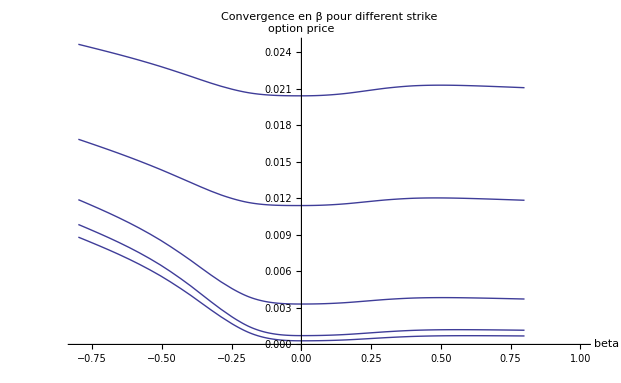
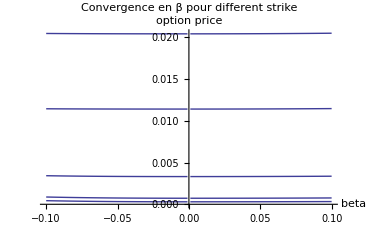
{588.,{-Graphics-,-Graphics-}}

```mathematica
(* q=2,m=2*)Timing[Module[{β={-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.001,-0.0005,-0.0001,0,0.0001,0.0005,0.001,0.005,0.006,0.007,0.008,0.009,0.01,0.015,0.02,.03,0.04,0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1},ρ=-0.5,λv=0.15,θv=0.04,κ=1,V=0.04,S0=0.05,k=Table[0.01 i,{i,3,7}],T=5,res,res1},res=Table[ShiftedLogHestonNormalCall2[β[[j]],ρ,λv,θv,κ,V,S0,k[[i]],T],{i,1,Length[k]},{j,1,Length[β]}];
res1=Table[Interpolation[Transpose[{β,res[[i]]}]],{i,1,Length[res]}];
{Plot[Table[res1[[i]][x],{i,1,Length[res1]}],{x,-0.8,1},PlotLabel->"Convergence en β pour different strike",AxesLabel->{"beta","option price"}],
Plot[Table[res1[[i]][x],{i,1,Length[res1]}],{x,-0.1,0.1},PlotLabel->"Convergence en β pour different strike",AxesLabel->{"beta","option price"}]}]]
```

```mathematica
(* q=2,m=2*)Timing[Module[{β={-.01},ρ=0.,λv=0.15,θv=0.04,κ=0.18,V=0.04,S0=0.0372,k=Table[0.0372 i,{i,1,1}],T=5.005479452,res,res1},res=Table[ShiftedLogHestonNormalCall2[β[[j]],ρ,λv,θv,κ,V,S0,k[[i]],T],{i,1,Length[k]},{j,1,Length[β]}]]]
```

{1.657,{{0.00608094}}}

```mathematica
(* q=2,m=2*)Timing[Module[{β={-.01},ρ=0.,λv=0.15,θv=0.04,κ=0.22,V=0.04,S0=0.0372,k=Table[0.0372 i,{i,1,1}],T=5.005479452,res,res1},res=Table[ShiftedLogHestonNormalCall2[β[[j]],ρ,λv,θv,κ,V,S0,k[[i]],T],{i,1,Length[k]},{j,1,Length[β]}]]]
```

{1.984,{{0.00587515}}}

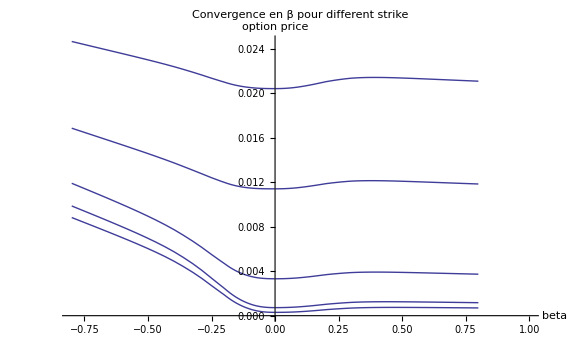
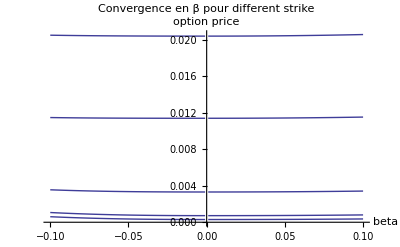
{603.531,{-Graphics-,-Graphics-}}

```mathematica
(* q=2,m=2*)Timing[Module[{β={-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.001,-0.0005,-0.0001,0,0.0001,0.0005,0.001,0.005,0.006,0.007,0.008,0.009,0.01,0.015,0.02,.03,0.04,0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1},ρ=-0.5,λv=0.15,θv=0.04,κ=1,V=0.04,S0=0.05,k=Table[0.01 i,{i,3,7}],T=5,res,res1},res=Table[ShiftedLogHestonNormalCall2[β[[j]],ρ,λv,θv,κ,V,S0,k[[i]],T],{i,1,Length[k]},{j,1,Length[β]}];
res1=Table[Interpolation[Transpose[{β,res[[i]]}]],{i,1,Length[res]}];
{Plot[Table[res1[[i]][x],{i,1,Length[res1]}],{x,-0.8,1},PlotLabel->"Convergence en β pour different strike",AxesLabel->{"beta","option price"}],
Plot[Table[res1[[i]][x],{i,1,Length[res1]}],{x,-0.1,0.1},PlotLabel->"Convergence en β pour different strike",AxesLabel->{"beta","option price"}]}]]
```

```mathematica
D[InterpolDenfer[x,m,q],x]
```

(m q x^(-1+q) Sech[m ArcTanh[1-2 x^q]]^2)/(1-(1-2 x^q)^2)

```mathematica
DInterpolDenfer[x_,m_,q_]:=(m q x^(-1+q) Sech[m ArcTanh[1-2 x^q]]^2)/(1-(1-2 x^q)^2)
```

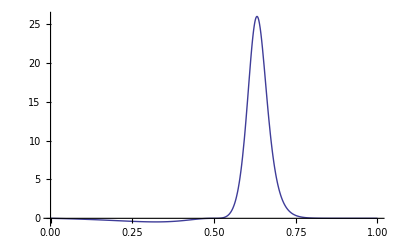

```mathematica
Module[{m=2,q=2},Plot[DInterpolDenfer[x,m,q],{x,0,1},PlotRange->All]]
```

## BiLognormale

#### Changement de measure : Cas lognormal

```mathematica
on veux que Subscript[S, i]/Subscript[S, 1] soit une martingale.
cela va induire une redefenition des browniens, et dons les deux process: Subscript[S, 1] et Subscript[S, i] recolte un drift.
```

```mathematica
Subscript[dS, 1]/Subscript[S, 1]=√Subscript[v, 1] Subscript[dW, 1]
Subscript[dS, i]/Subscript[S, i]=√Subscript[v, i](ρ  Subscript[dW, 1]+√(1-ρ^2)Subscript[dW, i])
```

```mathematica
en log
```

```mathematica
d(Log[Subscript[S, 1]])=√Subscript[v, 1] Subscript[dW, 1]-Subscript[v, 1]/2 dt
d(Log[Subscript[S, i]])=√Subscript[v, i](ρ  Subscript[dW, 1]+√(1-ρ^2)Subscript[dW, i])-Subscript[v, i]/2 dt
```

```mathematica
le quotient
```

```mathematica
d(Log[Subscript[S, i]/Subscript[S, 1]])=√Subscript[v, i](ρ  Subscript[dW, 1]+√(1-ρ^2)Subscript[dW, i])-Subscript[v, i]/2 dt-√Subscript[v, 1] Subscript[dW, 1]+Subscript[v, 1]/2 dt
```

```mathematica
d(Log[Subscript[S, i]/Subscript[S, 1]])=(√Subscript[v, i] ρ  -√Subscript[v, 1])Subscript[dW, 1]+√Subscript[v, i] √(1-ρ^2)Subscript[dW, i]+1/2(Subscript[v, 1]-Subscript[v, i])dt
```

```mathematica
on reexponencie
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=(√Subscript[v, i] ρ  -√Subscript[v, 1])Subscript[dW, 1]+√Subscript[v, i] √(1-ρ^2)Subscript[dW, i]+1/2(Subscript[v, 1]-Subscript[v, i])dt+1/2((√Subscript[v, i] ρ  -√Subscript[v, 1])^2+Subscript[v, i](1-ρ^2))dt
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=(√Subscript[v, i] ρ  -√Subscript[v, 1])Subscript[dW, 1]+√Subscript[v, i] √(1-ρ^2)Subscript[dW, i]+(-ρ √Subscript[v, i]  √Subscript[v, 1] +(Subscript[v, 1]+Subscript[v, i])/2+1/2(Subscript[v, 1]-Subscript[v, i]))dt
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=(√Subscript[v, i] ρ  -√Subscript[v, 1])Subscript[dW, 1]+√Subscript[v, i] √(1-ρ^2)Subscript[dW, i]-√Subscript[v, 1](   ρ √Subscript[v, i]-√Subscript[v, 1])dt
```

```mathematica
on distribue les shift:
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=(√Subscript[v, i] ρ  -√Subscript[v, 1])(Subscript[dW, 1]-√Subscript[v, 1])+√Subscript[v, i] √(1-ρ^2)Subscript[dW, i]
```

```mathematica
on a donc les redefinition suivantes:
```

```mathematica
OverBar[Subscript[dW, 1]]=Subscript[dW, 1]-√Subscript[v, 1]
```

```mathematica
OverBar[Subscript[dW, i]]=Subscript[dW, i]
```

```mathematica
donc les nouveau process a analyser sont:
```

```mathematica
Subscript[dS, 1]/Subscript[S, 1]=√Subscript[v, 1](OverBar[Subscript[dW, 1]]+√Subscript[v, 1] dt)
Subscript[dS, i]/Subscript[S, i]=√Subscript[v, i](ρ  (OverBar[Subscript[dW, 1]]+√Subscript[v, 1] dt)+√(1-ρ^2)(OverBar[Subscript[dW, i]]))
```

```mathematica
soit
```

```mathematica
Subscript[dS, 1]/Subscript[S, 1]=√Subscript[v, 1](OverBar[Subscript[dW, 1]])+Subscript[v, 1] dt
Subscript[dS, i]/Subscript[S, i]=√Subscript[v, i](ρ  OverBar[Subscript[dW, 1]]+√(1-ρ^2)OverBar[Subscript[dW, i]])+ρ √Subscript[v, i] √Subscript[v, 1] dt
```

#### Integrand de la digitale spreadoption bilog

```mathematica
phi[x_]:=Exp[-x^2/2]/Sqrt[2Pi]
```

```mathematica
Nd[x_]:=(Erf[x/(√2)]+1)/2
```

```mathematica
LogNormalSpreadDigitaleCall[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=NIntegrate[phi[x]Nd[-(Log[(k+S2 E^(-1/2 sig2^2 t+sig2 Sqrt[t] x))/(S1 E^(-1/2 sig1^2 t))]-rho sig1 Sqrt[t] x)/(√(1-rho^2) sig1 √t)],{x,-∞,-1,+∞}]
```

```mathematica
LogNormalSpreadDigitaleCallN[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=CoeffBasedIntegrate[(Nd[-(Log[(k+S2 E^(-1/2 sig2^2 t+sig2 Sqrt[t] #))/(S1 E^(-1/2 sig1^2 t))]-rho sig1 Sqrt[t] #)/(√(1-rho^2) sig1 √t)])&,ModifiedHermiteCoeffs[20]]
```

```mathematica
LogNormalSpreadDigitaleCallN[S1_,S2_,sig1_,sig2_,rho_,k_,t_,nbsteps_]:=CoeffBasedIntegrate[(Nd[-(Log[(k+S2 E^(-1/2 sig2^2 t+sig2 Sqrt[t] #))/(S1 E^(-1/2 sig1^2 t))]-rho sig1 Sqrt[t] #)/(√(1-rho^2) sig1 √t)])&,ModifiedHermiteCoeffs[nbsteps]]
```

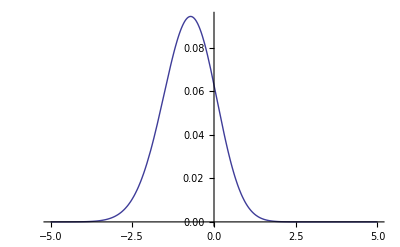

```mathematica
Module[{S1=0.05,S2=0.045,sig1=0.2,sig2=0.3,k=0.01,rho=0.92,t=1},Plot[phi[x]Nd[-(Log[(k+S2 E^(-1/2 sig2^2 t+sig2 Sqrt[t] x))/(S1 E^(-1/2 sig1^2 t))]-rho sig1 Sqrt[t] x)/(√(1-rho^2) sig1 √t)],{x,-5,5}]]
```

```mathematica
Module[{S1=0.05,S2=0.045,sig1=0.2,sig2=0.3,k=0.01,rho=0.2,t=1},LogNormalSpreadDigitaleCall2[S1,S2,sig1,sig2,rho,k,t]]
```

0.385161

```mathematica
Module[{S1=0.05,S2=0.045,sig1=0.2,sig2=0.3,k=0.01,rho=0.2,t=1,nb=20},LogNormalSpreadDigitaleCall[S1,S2,sig1,sig2,rho,k,t,nb]]
```

0.385162

```mathematica
Positive
```

#### Formule des digitales : Cas nb = 20 (default)

```mathematica
LogNormalSpreadDigitaleCall[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=If[k>=0,LogNormalSpreadDigitaleCallN[S1 ,S2 ,sig1,sig2,rho,k,t],1-LogNormalSpreadDigitaleCallN[S2 ,S1 ,sig2,sig1,rho,-k,t]]
```

```mathematica
MesureQTLogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=LogNormalSpreadDigitaleCall[S1 ,S2 ,sig1,sig2,rho,k,t]
```

```mathematica
MesureQ1LogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=LogNormalSpreadDigitaleCall[S1 Exp[sig1^2 t],S2 Exp[rho sig1 sig2 t],sig1,sig2,rho,k,t]
```

```mathematica
MesureQ2LogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=LogNormalSpreadDigitaleCall[S1 Exp[rho sig1 sig2 t],S2 Exp[sig2^2 t],sig1,sig2,rho,k,t]
```

#### Formule des digitales : Cas nb customisable

```mathematica
LogNormalSpreadDigitaleCall[S1_,S2_,sig1_,sig2_,rho_,k_,t_,nb_]:=If[k>=0,LogNormalSpreadDigitaleCallN[S1 ,S2 ,sig1,sig2,rho,k,t,nb],1-LogNormalSpreadDigitaleCallN[S2 ,S1 ,sig2,sig1,rho,-k,t,nb]]
```

```mathematica
MesureQTLogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_,nb_]:=LogNormalSpreadDigitaleCall[S1 ,S2 ,sig1,sig2,rho,k,t,nb]
```

```mathematica
MesureQ1LogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_,nb_]:=LogNormalSpreadDigitaleCall[S1 Exp[sig1^2 t],S2 Exp[rho sig1 sig2 t],sig1,sig2,rho,k,t,nb]
```

```mathematica
MesureQ2LogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_,nb_]:=LogNormalSpreadDigitaleCall[S1 Exp[rho sig1 sig2 t],S2 Exp[sig2^2 t],sig1,sig2,rho,k,t,nb]
```

#### Verificationd de la parité entre les deux measures

```mathematica
E[S2 Subscript[1, S1-S2>K]]=S2-E[S2 Subscript[1, S1-S2<K]]=S2-E[S2 Subscript[1, S2-S1>-K]]
```

```mathematica
MesureQ2LogNormalSpreadDigitaleZ[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=1-MesureQ1LogNormalSpreadDigitale[S2,S1,sig2,sig1,rho,-k,t]
```

```mathematica
Module[{S1=0.05,S2=0.051,sig1=0.2,sig2=0.3,rho=0.9,k=0.004,t=10},{MesureQ2LogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t],MesureQ2LogNormalSpreadDigitaleZ[S1,S2,sig1,sig2,rho,k,t]}]
```

{0.326645,0.326645}

#### Spreadoption

```mathematica
LogNormalSpreadOption[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=S1 MesureQ1LogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t]-S2 MesureQ2LogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t]-k MesureQTLogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t]
```

```mathematica
LogNormalSpreadOption[S1_,S2_,sig1_,sig2_,rho_,k_,t_,nb_]:=S1 MesureQ1LogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t,nb]-S2 MesureQ2LogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t,nb]-k MesureQTLogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t,nb]
```

#### Exemples

```mathematica
MesureQTLogNormalSpreadDigitale[0.05,0.051,0.2,0.3,0.9,0.02,10,12]
```

0.123138

```mathematica
Module[{S1=0.05,S2=0.051,sig1=0.2,sig2=0.3,rho=0.9,k=0.02,t=10},LogNormalSpreadOption[S1,S2,sig1,sig2,rho,k,t,12]]
```

0.00361177-0.02 MesureQTLogNormalSpreadDigitale[0.05,0.051,0.2,0.3,0.9,0.02,10,12]

#### Smile normal du bilog spreadoption

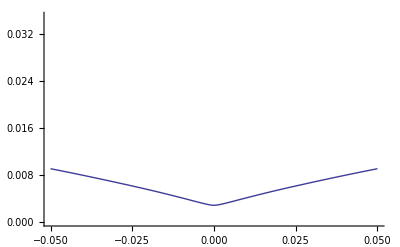

```mathematica
Module[{S1=0.05,S2=0.05,sig1=0.4,sig2=0.4,rho=0.99,k=0.02,t=10,strikes=Table[0.01i,{i,-5,5,0.1}]},ListPlot[Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],t,LogNormalSpreadOption[S1,S2,sig1,sig2,rho,strikes[[i]],t]]},{i,1,Length[strikes]}],PlotRange->{0,0.035},Joined->True]]
```

#### Effet de mean reversion des underlyings

Introduction de la mean reversion  pour expliquer l' effet moustache

d[Log[x]] = λ (A - Log[x]) dt + σ dW

y = Log[x]

dy = λ (A - y) dt + σ dW

y(T)=A+(y(0)-A)ⅇ^(-λ t)+ⅇ^-at W̄((ⅇ^(2 a t)-1)/(2a)σ^2)

si je suppose y (0) - A

y(T)=A+W̄((1-ⅇ^(-2 a_1 t))/(2 a_1)σ^2)

si on se donne deux variables

y_1(T)=A_1+ⅇ^-a_1t OverBar[W_1]((1-ⅇ^(-2 a_1 t))/(2 a_1)σ_1^2)

y_2(T)=A_2+ⅇ^-a_2t OverBar[W_2]((1-ⅇ^(-2 a_2 t))/(2 a_2)σ_2^2)

on suppose en plus que OverBar[W_1].OverBar[W_2]=ρ_eff dt

ⅇ^y_1-ⅇ^y_2 revient a examiner deux processus lognormaux avec une  vol_i = √((1-ⅇ^(-2 a_i T))/(2 a_i T))σ_i

Donc pas d' effet moustache (diminution de la pente de smile pour les strike loin de la monaie) a priori

```mathematica
Densité
```

```mathematica
Simplify[D[phi[x]Nd[-(Log[(k+S2 E^(-1/2 sig2^2 t+sig2 Sqrt[t] x))/(S1 E^(-1/2 sig1^2 t))]-rho sig1 Sqrt[t] x)/(√(1-rho^2) sig1 √t)],{k,1}]]
```

-(ⅇ^(1/2 (-x^2+((-rho sig1 √t x+Log[(ⅇ^((sig1^2 t)/2) (k+ⅇ^(-(sig2^2 t)/2+sig2 √t x) S2))/S1])^2)/((-1+rho^2) sig1^2 t))))/(2 π √(1-rho^2) (k+ⅇ^(-(sig2^2 t)/2+sig2 √t x) S2) sig1 √t)

```mathematica
LogNormalSpreadDensity[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=CoeffBasedIntegrate[((ⅇ^(1/2 (-#^2+((-rho sig1 √t #+Log[(ⅇ^((sig1^2 t)/2) (k+ⅇ^(-(sig2^2 t)/2+sig2 √t#) S2))/S1])^2)/((-1+rho^2) sig1^2 t))))/(2 π √(1-rho^2) (k+ⅇ^(-(sig2^2 t)/2+sig2 √t #) S2) sig1 √t))&,ModifiedHermiteCoeffs[20]]
```

```mathematica
Module[{S1=0.05,S2=0.048,τ=5,
VolS1=0.01,VolS2=0.01,Correl12=0.9,k=0.001},LogNormalSpreadDensity[S1,S2,√VolS1,√VolS2,Correl12,k,τ]]
```

23.6713

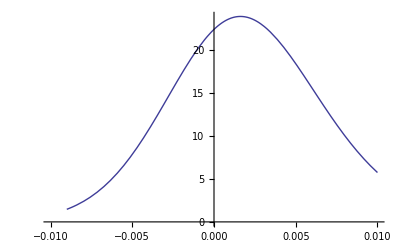

```mathematica
Module[{S1=0.05,S2=0.048,τ=5,
VolS1=0.01,VolS2=0.01,Correl12=0.9},Plot[LogNormalSpreadDensity[S1,S2,√VolS1,√VolS2,Correl12,k,τ],{k,-0.01,0.01}]]
```

#### Proxy simple pour la vol de vol minimale du bilog

Si on calcule de maniere instantanée

d(σ1^2 S1^2+σ2^2 S2^2-2ρ σ1 σ2 S1 S2)==(2 σ1^2 S1 dS1+σ2^2 S2 dS2-2ρ σ1 σ2 S1 dS2-22ρ σ1 σ2 S2 dS1 )+drifts

donc partie martingale  ==2( σ1^2 S1 -ρ σ1 σ2 S2 )dS1+2(σ2^2 S2 -ρ σ1 σ2 S1)dS2

==2( σ1^2 S1 -ρ σ1 σ2 S2 )dS1+2(σ2^2 S2 -ρ σ1 σ2 S1)dS2

donc varvar=4( σ1^2 S1 -ρ σ1 σ2 S2 )^2 σ1^2+4(σ2^2 S2 -ρ σ1 σ2 S1)^2 σ2^2+8ρ ( σ1^2 S1 -ρ σ1 σ2 S2 )(σ2^2 S2 -ρ σ1 σ2 S1) σ1 σ2

```mathematica
Simplify[4( σ1^2 S1 -Correl12 σ1 σ2 S2 )^2 σ1^2+4(σ2^2 S2 -Correl12 σ1 σ2 S1 )^2 σ2^2+8Correl12 ( σ1^2 S1 -Correl12 σ1 σ2 S2 )(σ2^2 S2 -Correl12 σ1 σ2 S1) σ1 σ2]
```

```mathematica
4 σ2^4 (Correl12 S1 σ1-S2 σ2)^2+4 σ1^4 (S1 σ1-Correl12 S2 σ2)^2+8 Correl12 σ1^2 σ2^2 (Correl12 S1 σ1-S2 σ2) (-S1 σ1+Correl12 S2 σ2)
```

```mathematica
ModeMoins3NuMinimunNormalHestonFromBilogProxy[S1_,S2_,σ1_,σ2_,Correl12_,T_]:=
Module[{varvar,VS},
VS=(σ1^2 S1^2+σ2^2 S2^2-2Correl12 σ1 σ2 S1 S2);
varvar=4 σ1^4 (S1 σ1-Correl12 S2 σ2)^2+4 σ2^4 (Correl12 S1 σ1-S2 σ2)^2+8 Correl12 σ1^2 σ2^2 (Correl12 S1 σ1-S2 σ2) (Correl12 S2 σ2-S1 σ1);
{VS,√varvar/√VS}]
```

attention VolS1 = σ1^2 et pareil pour VolS2

```mathematica
Module[{S1=0.05399906,S2=0.05268318,τ=11.737166,
VolS1=0.0251,VolS2=0.024,Correl12=0.9},ModeMoins3NuMinimunNormalHestonFromBilogProxy[S1,S2,√VolS1,√VolS2,Correl12,τ]]
```

{0.0000141194,0.0216257}

#### Optimisation des parametre Heston du bilog : NormalHestonSmileCalibrate et HestonFromBilog

```mathematica
NormalHestonSmileCalibrate[KList_,PriceList_,WeightList_,S0_,λ_,LT_,T_,nbsteps_,scale_,microratio_]:=Module[{func,gradfunc,V0,rho,nu,ss,NewWeightList},
V0=10^(-5);
NewWeightList=Table[WeightList[[i]]/NormalCallVega[S0,KList[[i]],T,√V0],{i,1,Length[WeightList]}];
func=Function[{V,ρ,ν},Module[{ff=DerivativeHestonNormalCall[ρ,λ,LT,ν,V,S0,KList,T,nbsteps,scale,microratio,0]},
Sum[NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])^2,{i,1,Length[KList]}]]];
gradfunc=Function[{V,ρ,ν},Module[{ff=DerivativeHestonNormalCall[ρ,λ,LT,ν,V,S0,KList,T,nbsteps,scale,microratio]},
{Sum[NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[2,i]],{i,1,Length[KList]}],
Sum[NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[3,i]],{i,1,Length[KList]}],
Sum[NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[4,i]],{i,1,Length[KList]}]
}]];
ss=FindMinimum[func[V0,rho,nu],{{V0,0.00003,0.0000001,0.001},{nu,0.001,0.000001,0.1},{rho,0,-0.9,0.9}},
MaxIterations->200,AccuracyGoal->7,Method->"LevenbergMarquardt",
Gradient->gradfunc[V0,rho,nu]] ;
{ss[[1]],{V0,rho,nu}} /. ss[[2]]
]
```

```mathematica
NormalHestonSmileCalibrateV0Fixed[KList_,PriceList_,WeightList_,S0_,V0_,λ_,LT_,T_,nbsteps_,scale_,microratio_]:=Module[{func,gradfunc,rho,nu,ss,NewWeightList},
NewWeightList=Table[WeightList[[i]]/NormalCallVega[S0,KList[[i]],T,√V0],{i,1,Length[WeightList]}];
func=Function[{ρ,ν},Module[{ff=DerivativeHestonNormalCall[ρ,λ,LT,ν,V0,S0,KList,T,nbsteps,scale,microratio,0]},
Sum[NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])^2,{i,1,Length[KList]}]]];
gradfunc=Function[{ρ,ν},Module[{ff=DerivativeHestonNormalCall[ρ,λ,LT,ν,V0,S0,KList,T,nbsteps,scale,microratio]},
{Sum[NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[3,i]],{i,1,Length[KList]}],
Sum[NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[4,i]],{i,1,Length[KList]}]
}]];
ss=FindMinimum[{func[rho,nu],(rho>-1)&&(rho<1)},{{nu,0.001,0.000001,0.01},{rho,0,-0.9,0.9}},
MaxIterations->200,AccuracyGoal->8,
Gradient->gradfunc[rho,nu]] ;
{ss[[1]],{V0,rho,nu}} /. ss[[2]]
]
```

```mathematica
NormalHestonSmileCalibrateV0Controlled[KList_,PriceList_,WeightList_,S0_,V0_,λ_,LT_,T_,nbsteps_,scale_,microratio_]:=Module[{func,gradfunc,V,rho,nu,ss},
func=Function[{V,ρ,ν},Module[{ff=DerivativeHestonNormalCall[ρ,λ,LT,ν,V,S0,KList,T,nbsteps,scale,microratio,0]},
Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])^2,{i,1,Length[KList]}]]];
gradfunc=Function[{V,ρ,ν},Module[{ff=DerivativeHestonNormalCall[ρ,λ,LT,ν,V,S0,KList,T,nbsteps,scale,microratio]},
{Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[2,i]],{i,1,Length[KList]}],
Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[3,i]],{i,1,Length[KList]}],
Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[4,i]],{i,1,Length[KList]}]
}]];
ss=FindMinimum[{func[V,rho,nu],(rho>-1)&&(rho<1)&&(V>1.05V0)&&(V<1.5V0)&&(nu>0)},{{V,V0,0.000001,0.01},{nu,0.001,0.000001,0.01},{rho,0,-0.9,0.9}},
MaxIterations->200,AccuracyGoal->8,
Gradient->gradfunc[V,rho,nu]] ;
{ss[[1]],{V,rho,nu}} /. ss[[2]]
]
```

```mathematica
HestonFromBilog[S1_,S2_,σ1_,σ2_,Correl12_,T_,λ_,LT_]:=
Module[{strikes,Stdev,pricegoaltable,WeightList,nbsteps,scale,microratio,nbstrike,ss,V0,ρ,ν},
Stdev=√T √(S1^2 σ1^2+S2^2 σ2^2-2Correl12 S1 S2 σ1 σ2);
Print["Stdev(pour le calcul des strike)=",Stdev];
strikes={- Stdev/3,-Stdev/6,0,Stdev/6,Stdev/3};
Print["strikes=",strikes];
nbstrike=Length[strikes];
pricegoaltable=Table[LogNormalSpreadOption[S1,S2,σ1,σ2,Correl12,strikes[[i]],T,12],{i,1,nbstrike}];
Print["pricegoaltable=",pricegoaltable];
WeightList=Table[1,{i,1,nbstrike}];nbsteps=40;scale=8;
microratio=5 T^(1/2);
ss=NormalHestonSmileCalibrate[strikes,pricegoaltable,WeightList,S1-S2,λ,LT,T,nbsteps,scale,microratio];
Print["optimisation results:",ss];
ss[[2]]
]
```

```mathematica
HestonFromBilogV0Fixed[S1_,S2_,σ1_,σ2_,Correl12_,T_,λ_,LT_,Vmultiplicator_]:=
Module[{V,strikes,Stdev,pricegoaltable,WeightList,nbsteps,scale,microratio,nbstrike,ss,V0,ρ,ν},
V=S1^2 σ1^2+S2^2 σ2^2-2Correl12 S1 S2 σ1 σ2;
V0=Vmultiplicator V;
Stdev=√(V0 T);
Print["Stdev(pour le calcul des strike)=",Stdev];
strikes={- Stdev/3,-Stdev/6,0,Stdev/6,Stdev/3};
Print["strikes=",strikes];
nbstrike=Length[strikes];
pricegoaltable=Table[LogNormalSpreadOption[S1,S2,σ1,σ2,Correl12,strikes[[i]],T,12],{i,1,nbstrike}];
Print["pricegoaltable=",pricegoaltable];
WeightList=Table[1,{i,1,nbstrike}];nbsteps=40;scale=8;microratio=5 T^(1/2);
ss=NormalHestonSmileCalibrateV0Fixed[strikes,pricegoaltable,WeightList,S1-S2,V0,λ,LT,T,nbsteps,scale,microratio];
Print["optimisation results:",ss];
ss[[2]]
]
```

```mathematica
HestonFromBilogV0Controlled[S1_,S2_,σ1_,σ2_,Correl12_,T_,λ_,LT_]:=
Module[{strikes,Stdev,volgoaltable,WeightList,nbsteps,scale,microratio,nbstrike,ss,V0,ρ,ν},
V0=S1^2 σ1^2+S2^2 σ2^2-2Correl12 S1 S2 σ1 σ2;
Stdev=√(V0 T);Print[Stdev];
strikes={- Stdev/3,-Stdev/6,0,Stdev/6,Stdev/3};Print["strikes=",strikes];
nbstrike=Length[strikes];
volgoaltable=Table[LogNormalSpreadOption[S1,S2,σ1,σ2,Correl12,strikes[[i]],T,12],{i,1,nbstrike}];
WeightList=Table[1,{i,1,nbstrike}];nbsteps=40;scale=8;microratio=5 T^(1/2);
ss=NormalHestonSmileCalibrateV0Controlled[strikes,volgoaltable,WeightList,S1-S2,V0,λ,LT,T,nbsteps,scale,microratio];
Print["optimisation results:",ss];
ss[[2]]
]
```

#### Packaging Des fonction de facon a controler leur domaine

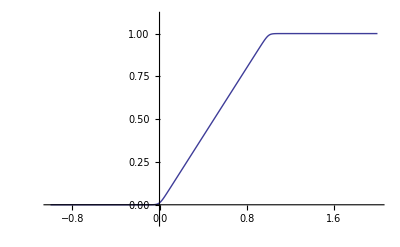

```mathematica
Module[{λ=30},Plot[1/(2λ)Log[Cosh[x λ]/Cosh[λ-x λ]]+0.5,{x,-1,2},PlotRange->{-0.1,1.1}]]
```

```mathematica
ΦControle[x_,λ_]:=1/(2λ)Log[Cosh[x λ]/Cosh[λ-x λ]]+1/2
```

```mathematica
Solve[1/(2λ)Log[z]+1/2==y,z]
```

{{z→ⅇ^(-λ+2 y λ)}}

```mathematica
Solve[Cosh[x λ]/Cosh[λ-x λ]==z,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-ArcCosh[(z √(-1+2 z Cosh[λ]-z^2 Cosh[λ]^2) Sinh[λ])/((1-z Cosh[λ]) √(1-2 z Cosh[λ]+z^2 Cosh[λ]^2-z^2 Sinh[λ]^2))]/λ},{x→ArcCosh[(z √(-1+2 z Cosh[λ]-z^2 Cosh[λ]^2) Sinh[λ])/((1-z Cosh[λ]) √(1-2 z Cosh[λ]+z^2 Cosh[λ]^2-z^2 Sinh[λ]^2))]/λ},{x→-ArcCosh[(z √(-1+2 z Cosh[λ]-z^2 Cosh[λ]^2) Sinh[λ])/((-1+z Cosh[λ]) √(1-2 z Cosh[λ]+z^2 Cosh[λ]^2-z^2 Sinh[λ]^2))]/λ},{x→ArcCosh[(z √(-1+2 z Cosh[λ]-z^2 Cosh[λ]^2) Sinh[λ])/((-1+z Cosh[λ]) √(1-2 z Cosh[λ]+z^2 Cosh[λ]^2-z^2 Sinh[λ]^2))]/λ}}

```mathematica
ΦControleInverse[y_,λ_]:=Module[{z=ⅇ^(-λ+2 y λ)},ArcCosh[(z √(-1+2 z Cosh[λ]-z^2 Cosh[λ]^2) Sinh[λ])/((-1+z Cosh[λ]) √(1-2 z Cosh[λ]+z^2 Cosh[λ]^2-z^2 Sinh[λ]^2))]/λ]
```

```mathematica
ΦControleInverse2[y_,λ_]:=Module[{z=ⅇ^(-λ+2 y λ)},ArcCosh[(z Abs[1-z Cosh[λ]] Sinh[λ])/((-1+z Cosh[λ]) √(2 z Cosh[λ]-1-z^2))]/λ]
```

```mathematica
en fait
```

```mathematica
ΦControleInverse2[y_,λ_]:=Module[{z=ⅇ^(-λ+2 y λ)},ArcCosh[(z  Sinh[λ])/(√(2 z Cosh[λ]-1-z^2))]/λ]
```

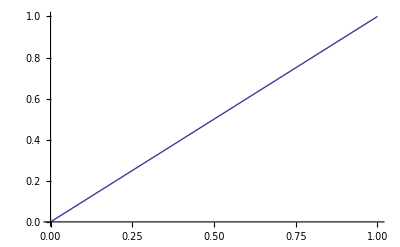

```mathematica
Plot[ΦControleInverse2[ΦControle[x,10],10],{x,0,1}]
```

```mathematica
ControleVariable[x_,Limdown_,Limup_,λ_]:=(Limup-Limdown)ΦControle[(x-Limdown)/(Limup-Limdown),λ]+Limdown
```

```mathematica
ControleVariableInverse[x_,Limdown_,Limup_,λ_]:=Re[Module[{r=(Limdown-x)/(Limdown-Limup)},  Limdown+(Limup-Limdown) ΦControleInverse[r,λ]]]
```

```mathematica
ControleVariableInverse[ControleVariable[0.0005,0.0001,0.001,10],0.0001,0.001,10]
```

0.0005+0. ⅈ

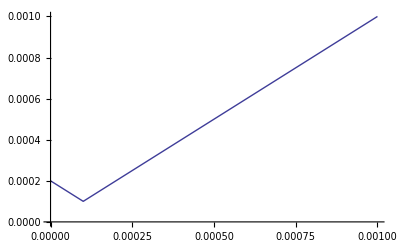

```mathematica
Plot[ControleVariableInverse[ControleVariable[x,0.0001,0.001,10],0.0001,0.001,10],{x,0.000,0.001},PlotRange->{0,0.001}]
```

```mathematica
Solve[(Limup-Limdown)r+Limdown==x,r]
```

{{r→(Limdown-x)/(Limdown-Limup)}}

```mathematica
Solve[(y-Limdown)/(Limup-Limdown)==z,y]
```

{{y→Limdown-Limdown z+Limup z}}

```mathematica
Simplify[D[ControleVariable[x,Limdown,Limup,λ],x]]
```

1/2 (Tanh[((Limdown-x) λ)/(Limdown-Limup)]+Tanh[((-Limup+x) λ)/(Limdown-Limup)])

```mathematica
DControleVariable[x_,Limdown_,Limup_,λ_]:=1/2 (Tanh[((Limdown-x) λ)/(Limdown-Limup)]+Tanh[((-Limup+x) λ)/(Limdown-Limup)])
```

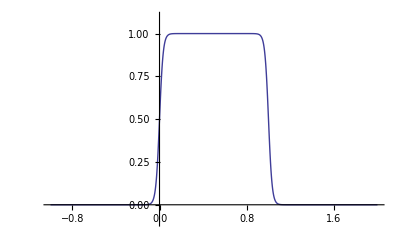

```mathematica
Module[{λ=30},Plot[1/2 (Tanh[x λ]+Tanh[(1-x) λ]),{x,-1,2},PlotRange->{-0.1,1.1}]]
```

#### Definition de HestonFromBilogPackaged

```mathematica
NormalHestonSmileCalibratePackaged[KList_,PriceList_,WeightList_,S0_,λ_,LT_,T_,nbsteps_,scale_,microratio_,InitialV0_,StandardizedNuMax_,λsmooth_]:=Module[{func,gradfunc,V0,rho,nu,ss,NewWeightList,ρdown=-0.9,ρup=0.9,νdown=0.000001,νup,V0down,V0up,StartingV0},
Print["args=",{KList,PriceList,WeightList,S0,λ,LT,T,nbsteps,scale,microratio,InitialV0,StandardizedNuMax,λsmooth}];
V0down=InitialV0 0.95;V0up=10 InitialV0;νup=StandardizedNuMax √InitialV0;
NewWeightList=Table[WeightList[[i]]/NormalCallVega[S0,KList[[i]],T,√InitialV0],{i,1,Length[WeightList]}];
func=Function[{V,ρ,ν},Module[{ff=DerivativeHestonNormalCall[
ControleVariable[ρ,ρdown,ρup,λsmooth],λ,LT,
ControleVariable[ν,νdown,νup,λsmooth],
ControleVariable[V,V0down,V0up,λsmooth],S0,KList,T,nbsteps,scale,microratio,0]},
Sum[NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])^2,{i,1,Length[KList]}]]];
gradfunc=Function[{V,ρ,ν},Module[{ff=DerivativeHestonNormalCall[
ControleVariable[ρ,ρdown,ρup,λsmooth],λ,LT,
ControleVariable[ν,νdown,νup,λsmooth],
ControleVariable[V,V0down,V0up,λsmooth],S0,KList,T,nbsteps,scale,microratio]},
{DControleVariable[V,V0down,V0up,λsmooth] Sum[NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[2,i]],{i,1,Length[KList]}],
DControleVariable[ρ,ρdown,ρup,λsmooth]Sum[NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[3,i]],{i,1,Length[KList]}],
DControleVariable[ν,νdown,νup,λsmooth]Sum[NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[4,i]],{i,1,Length[KList]}]
}]];
StartingV0=InitialV0 1.05;
ss=FindMinimum[func[V0,rho,nu],{{V0,StartingV0,V0down,V0up},{nu,0.5 √InitialV0,νdown,νup},{rho,0,ρdown,ρup}},
MaxIterations->200,AccuracyGoal->7,Method->"LevenbergMarquardt",
Gradient->gradfunc[V0,rho,nu]] ;
{ss[[1]],{V0,rho,nu}} /. ss[[2]]
]
```

```mathematica
NewWeightList=Table[WeightList[[i]]/NormalCallVega[S0,KList[[i]],T,√InitialV0],{i,1,Length[WeightList]}];
```

```mathematica
ShowProblemsNormalHestonSmileCalibratePackaged[KList_,PriceList_,WeightList_,S0_,λ_,LT_,T_,nbsteps_,scale_,microratio_,InitialV0_,StandardizedNuMax_,λsmooth_]:=Module[
{func,gradfunc,V0,rho,nu,ss,NewWeightList,ρdown=-0.9,ρup=0.9,νdown=0.000001,νup,V0down,V0up,StartingV0},
V0down=InitialV0 0.5;V0up=10 InitialV0;νup=StandardizedNuMax √InitialV0;
NewWeightList=Table[WeightList[[i]]/NormalCallVega[S0,KList[[i]],T,√InitialV0],{i,1,Length[WeightList]}];
func=Function[{V,ρ,ν},Module[{ff=DerivativeHestonNormalCall[
ControleVariable[ρ,ρdown,ρup,λsmooth],λ,LT,
ControleVariable[ν,νdown,νup,λsmooth],
ControleVariable[V,V0down,V0up,λsmooth],S0,KList,T,nbsteps,scale,microratio,0]},
Sum[NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])^2,{i,1,Length[KList]}]]];
gradfunc=Function[{V,ρ,ν},Module[{ff=DerivativeHestonNormalCall[
ControleVariable[ρ,ρdown,ρup,λsmooth],λ,LT,
ControleVariable[ν,νdown,νup,λsmooth],
ControleVariable[V,V0down,V0up,λsmooth],S0,KList,T,nbsteps,scale,microratio]},
{DControleVariable[V,V0down,V0up,λsmooth] Sum[NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[2,i]],{i,1,Length[KList]}],
DControleVariable[ρ,ρdown,ρup,λsmooth]Sum[NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[3,i]],{i,1,Length[KList]}],
DControleVariable[ν,νdown,νup,λsmooth]Sum[NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[4,i]],{i,1,Length[KList]}]
}]];
StartingV0=InitialV0 1.05;
{Plot3D[func[V0,0,nu],{V0,V0down,V0up/4},{nu,νdown,νup},AxesLabel->{"V0","nu"}] ,
Plot3D[func[StartingV0,rho,nu],{nu,νdown,νup},{rho,ρdown,ρup},AxesLabel->{"nu","rho"}],
Plot3D[func[V0,rho,√InitialV0],{V0,V0down,V0up/4},{rho,ρdown,ρup},AxesLabel->{"V0","rho"}]}
]
```

```mathematica
Module[{S1=0.0505,S2=0.0507,T=10,VolS1=0.101489,VolS2=0.101489,Correl12=0.951456,λ=0.1,LT=1.,ss,V0,ρ,ν,
nbstrike,strikes,bilogvols,hestonprices,hestonvols,bilogprices,smooth=10},
Timing[HestonFromBilogPackaged[S1,S2,VolS1,VolS2,Correl12,T,λ,LT,smooth]]]
```

*****************Inside HestonFromBilogPackaged

InitialV0=2.56078×10^-6 νup=0.00320049 Stdev(pour le calcul des strike)=0.00506042

strikes={-0.00168681,-0.000843403,0,0.000843403,0.00168681}

pricegoaltable={0.00285907,0.00235878,0.00191939,0.0015418,0.00122416}

args={{-0.00168681,-0.000843403,0,0.000843403,0.00168681},{0.00285907,0.00235878,0.00191939,0.0015418,0.00122416},{1,1,1,1,1},-0.0002,0.1,1.,10,40,8,5 √10,2.56078×10^-6,2,10}

HestonFromBilogPackaged: optimisation results:{1.06879×10^-16,{1.32967×10^-6,-0.0148867,0.000819572}}

{36.937,{2.81098×10^-6,-0.0148854,0.000820528}}

```mathematica
Module[{S1=0.0505,S2=0.0507,T=10,VolS1=0.101489,VolS2=0.101489,Correl12=0.951456,λ=0.1,LT=1.,ss,V0,rho0,nu0,V01,rho01,nu01,V02,rho02,nu02,V0r,rho0r,nu0r,dVol=0.01,drho=.01,s,smooth=10},
Timing[{V0,rho0,nu0}=HestonFromBilogPackaged[S1,S2,VolS1,VolS2,Correl12,T,λ,LT,smooth];
{V01,rho01,nu01}=HestonFromBilogPackaged[S1,S2,VolS1+dVol,VolS2,Correl12,T,λ,LT,smooth];
{V02,rho02,nu02}=HestonFromBilogPackaged[S1,S2,VolS1,VolS2+dVol,Correl12,T,λ,LT,smooth];
{V0r,rho0r,nu0r}=HestonFromBilogPackaged[S1,S2,VolS1,VolS2,Correl12+drho,T,λ,LT,smooth];
Print["parametres de base=",{V0,rho0,nu0}];
Print["Derivée sigma1=",{(V01-V0)/dVol,(rho01-rho0)/dVol,(nu01-nu0)/dVol}];
Print["Derivée sigma2=",{(V02-V0)/dVol,(rho02-rho0)/dVol,(nu02-nu0)/dVol}];
Print["Derivée rho=",{(V0r-V0)/drho,(rho0r-rho0)/drho,(nu0r-nu0)/drho}];]]
```

*****************Inside HestonFromBilogPackaged

InitialV0=2.56078×10^-6 νup=0.00320049 Stdev(pour le calcul des strike)=0.00506042

strikes={-0.00168681,-0.000843403,0,0.000843403,0.00168681}

pricegoaltable={0.00285907,0.00235878,0.00191939,0.0015418,0.00122416}

args={{-0.00168681,-0.000843403,0,0.000843403,0.00168681},{0.00285907,0.00235878,0.00191939,0.0015418,0.00122416},{1,1,1,1,1},-0.0002,0.1,1.,10,40,8,5 √10,2.56078×10^-6,2,10}

HestonFromBilogPackaged: optimisation results:{1.06879×10^-16,{1.32967×10^-6,-0.0148867,0.000819572}}

*****************Inside HestonFromBilogPackaged

InitialV0=3.04759×10^-6 νup=0.00349147 Stdev(pour le calcul des strike)=0.0055205

strikes={-0.00184017,-0.000920083,0,0.000920083,0.00184017}

pricegoaltable={0.00306956,0.00255537,0.00211031,0.00173146,0.00141345}

args={{-0.00184017,-0.000920083,0,0.000920083,0.00184017},{0.00306956,0.00255537,0.00211031,0.00173146,0.00141345},{1,1,1,1,1},-0.0002,0.1,1.,10,40,8,5 √10,3.04759×10^-6,2,10}

HestonFromBilogPackaged: optimisation results:{1.44135×10^-14,{1.7688×10^-6,0.308657,0.00096977}}

*****************Inside HestonFromBilogPackaged

InitialV0=3.09069×10^-6 νup=0.00351607 Stdev(pour le calcul des strike)=0.0055594

strikes={-0.00185313,-0.000926567,0,0.000926567,0.00185313}

pricegoaltable={0.00321233,0.00262964,0.00211031,0.00165905,0.00127784}

args={{-0.00185313,-0.000926567,0,0.000926567,0.00185313},{0.00321233,0.00262964,0.00211031,0.00165905,0.00127784},{1,1,1,1,1},-0.0002,0.1,1.,10,40,8,5 √10,3.09069×10^-6,2,10}

HestonFromBilogPackaged: optimisation results:{1.07424×10^-14,{1.77479×10^-6,-0.335969,0.000964846}}

*****************Inside HestonFromBilogPackaged

InitialV0=2.03335×10^-6 νup=0.00285191 Stdev(pour le calcul des strike)=0.00450927

strikes={-0.00150309,-0.000751545,0,0.000751545,0.00150309}

pricegoaltable={0.00253445,0.00209003,0.00169993,0.00136491,0.00108325}

args={{-0.00150309,-0.000751545,0,0.000751545,0.00150309},{0.00253445,0.00209003,0.00169993,0.00136491,0.00108325},{1,1,1,1,1},-0.0002,0.1,1.,10,40,8,5 √10,2.03335×10^-6,2,10}

HestonFromBilogPackaged: optimisation results:{1.05462×10^-16,{1.05973×10^-6,-0.016723,0.000731832}}

parametres de base={2.81098×10^-6,-0.0148854,0.000820528}

Derivée sigma1={0.0000588848,32.3416,0.0149918}

Derivée sigma2={0.0000631133,-32.0913,0.0145047}

Derivée rho={-0.0000577869,-0.183608,-0.00878529}

{167.532,Null}

```mathematica
ShowProblemsNormalHestonSmileCalibratePackaged[st,pr,wei=Table[1,{i,1,Length[st]}],s0,0.1,1,T,40,8,5 √5,0.000025,2,10]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
HestonFromBilogPackaged[S1_,S2_,σ1_,σ2_,Correl12_,T_,λ_,LT_,λsmooth_]:=
Module[{strikes,Stdev,pricegoaltable,WeightList,nbsteps,scale,microratio,nbstrike,ss,ρ,ν,InitialV0,
ρdown=-0.9,ρup=0.9,νdown=0.000001,νup,V0down,V0up,StandardizedNuMax=2},
InitialV0=S1^2 σ1^2+S2^2 σ2^2-2Correl12 S1 S2 σ1 σ2;
V0down=InitialV0 0.95;V0up=10 InitialV0;νup=StandardizedNuMax √InitialV0;;
Stdev=√(InitialV0 T);
Print["*****************Inside HestonFromBilogPackaged"];
Print["InitialV0=",InitialV0," νup=",νup," Stdev(pour le calcul des strike)=",Stdev];
strikes={- Stdev/3,-Stdev/6,0,Stdev/6,Stdev/3};
Print["strikes=",strikes];
nbstrike=Length[strikes];
pricegoaltable=Table[LogNormalSpreadOption[S1,S2,σ1,σ2,Correl12,strikes[[i]],T,12],{i,1,nbstrike}];
Print["pricegoaltable=",pricegoaltable];
WeightList=Table[1,{i,1,nbstrike}];nbsteps=40;scale=8;
microratio=5 T^(1/2);
ss=NormalHestonSmileCalibratePackaged[strikes,pricegoaltable,WeightList,S1-S2,λ,LT,T,nbsteps,scale,microratio,InitialV0,StandardizedNuMax,λsmooth];
Print["  HestonFromBilogPackaged: optimisation results:",ss];
{ControleVariable[ss[[2,1]],V0down,V0up,λsmooth],ControleVariable[ss[[2,2]],ρdown,ρup,λsmooth],ControleVariable[ss[[2,3]],νdown,νup,λsmooth]}
]
```

```mathematica
Module[{S1=0.055,S2=0.051,T=5,VolS1=0.15,VolS2=0.2,Correl12=0.9,λ=0.1,LT=1.,ss,V0,ρ,ν,
nbstrike,strikes,bilogvols,hestonprices,hestonvols,bilogprices},
Timing[HestonFromBilog[S1,S2,VolS1,VolS2,Correl12,T,λ,LT]]]
```

Stdev(pour le calcul des strike)=0.0101569

strikes={-0.00338563,-0.00169282,0,0.00169282,0.00338563}

pricegoaltable={0.00923005,0.00789705,0.00663868,0.00546949,0.00440527}

optimisation results:{1.37769×10^-12,{0.0000250255,-0.402808,0.0042073}}

{8.375,{0.0000250255,-0.402808,0.0042073}}

```mathematica
Module[{S1=0.055,S2=0.051,T=5,VolS1=0.15,VolS2=0.2,Correl12=0.9,λ=0.1,LT=1.,ss,V0,ρ,ν,
nbstrike,strikes,bilogvols,hestonprices,hestonvols,bilogprices,λsmooth=10},
Timing[HestonFromBilogPackaged[S1,S2,VolS1,VolS2,Correl12,T,λ,LT,λsmooth]]]
```

Stdev(pour le calcul des strike)=0.0101569

strikes={-0.00338563,-0.00169282,0,0.00169282,0.00338563}

pricegoaltable={0.00923005,0.00789705,0.00663868,0.00546949,0.00440527}

optimisation results:{1.227×10^-12,{-0.0000221902,-0.403991,0.00419998}}

{40.593,{0.0000207242,-0.403628,0.00420141}}

```mathematica
Module[{S1=0.055,S2=0.051,T=5,VolS1=0.15,VolS2=0.2,Correl12=0.,λ=0.1,LT=1.,ss,V0,ρ,ν,
nbstrike,strikes,bilogvols,hestonprices,hestonvols,bilogprices},
Timing[HestonFromBilog[S1,S2,VolS1,VolS2,Correl12,T,λ,LT]]]
```

Stdev(pour le calcul des strike)=0.0293345

strikes={-0.00977816,-0.00488908,0,0.00488908,0.00977816}

pricegoaltable={0.0201399,0.0167976,0.0137704,0.0110904,0.00877401}

optimisation results:{2.99013×10^-12,{0.000185549,0.210741,-0.00816331}}

{8.234,{0.000185549,0.210741,-0.00816331}}

```mathematica
Module[{S1=0.055,S2=0.051,T=5,VolS1=0.15,VolS2=0.2,Correl12=-0.,λ=0.1,LT=1.,ss,V0,ρ,ν,
nbstrike,strikes,bilogvols,hestonprices,hestonvols,bilogprices,λsmooth=10},
Timing[HestonFromBilogPackaged[S1,S2,VolS1,VolS2,Correl12,T,λ,LT,λsmooth]]]
```

Stdev(pour le calcul des strike)=0.0293345

strikes={-0.00977816,-0.00488908,0,0.00488908,0.00977816}

pricegoaltable={0.0201399,0.0167976,0.0137704,0.0110904,0.00877401}

optimisation results:{9.17614×10^-9,{-0.00299487,-0.0988256,0.0134674}}

{40.641,{0.000172103,-0.0988148,0.0134695}}

```mathematica
0.05,0.051,0.03741657386773942,0.03741657386773942,0.,5
```

```mathematica
Module[{S1=0.05,S2=0.051,T=5,VolS1=0.03741657386773942,VolS2=0.03741657386773942,Correl12=0.,λ=0.1,LT=1.,ss,V0,ρ,ν,
nbstrike,strikes,bilogvols,hestonprices,hestonvols,bilogprices},
Timing[HestonFromBilog[S1,S2,VolS1,VolS2,Correl12,T,λ,LT]]]
```

Stdev(pour le calcul des strike)=0.00597553

strikes={-0.00199184,-0.000995922,0,0.000995922,0.00199184}

pricegoaltable={0.0029117,0.00238046,0.00191563,0.0015163,0.00117977}

optimisation results:{3.30978×10^-18,{7.16632×10^-6,-0.0145711,0.000338385}}

{8.453,{7.16632×10^-6,-0.0145711,0.000338385}}

```mathematica
Module[{S1=0.05,S2=0.051,T=5,VolS1=0.03741657386773942,VolS2=0.03741657386773942,Correl12=0.,λ=0.1,LT=1.,ss,V0,ρ,ν,
nbstrike,strikes,bilogvols,hestonprices,hestonvols,bilogprices,λsmooth=200},
Timing[HestonFromBilogPackaged[S1,S2,VolS1,VolS2,Correl12,T,λ,LT,λsmooth]]]
```

InitialV0=7.1414×10^-6 νup=0.00534468 Stdev(pour le calcul des strike)=0.00597553

strikes={-0.00199184,-0.000995922,0,0.000995922,0.00199184}

pricegoaltable={0.0029117,0.00238046,0.00191563,0.0015163,0.00117977}

InitialV0=7.1414×10^-6 StartingV0=7.49847×10^-6

optimisation results:{3.35891×10^-18,{7.69795×10^-8,-0.0145724,0.000249538}}

{40.578,{6.78433×10^-6,-0.0145724,0.000249538}}

```mathematica
Module[{S1=0.05,S2=0.051,T=5,VolS1=0.02,VolS2=0.02,Correl12=0.5,λ=0.1,LT=1.,ss,V0,ρ,ν,
nbstrike,strikes,bilogvols,hestonprices,hestonvols,bilogprices,λsmooth=200},
Timing[HestonFromBilogPackaged[S1,S2,VolS1,VolS2,Correl12,T,λ,LT,λsmooth]]]
```

InitialV0=1.0204×10^-6 νup=0.0020203 Stdev(pour le calcul des strike)=0.00225876

strikes={-0.00075292,-0.00037646,0,0.00037646,0.00075292}

pricegoaltable={0.00078282,0.000623261,0.000487796,0.000375025,0.000283045}

optimisation results:{3.40846×10^-22,{-7.56334×10^-9,-0.0215182,0.0000114991}}

{40.188,{9.6938×10^-7,-0.0215182,0.0000120935}}

#### Visualization des problemes associée a HestonFromBilog

```mathematica
HestonFromBilogViewPb[S1_,S2_,σ1_,σ2_,Correl12_,T_,λ_,LT_,λsmooth_]:=
Module[{strikes,Stdev,pricegoaltable,WeightList,nbsteps,scale,microratio,nbstrike,ss,ρ,ν,NewWeightList,func,Vn,ρn,νn,InitialV0,func1,
ρdown=-0.9,ρup=0.9,νdown=0.000001,νup=0.1,V0down=0.0000001,V0up=0.1},
InitialV0=S1^2 σ1^2+S2^2 σ2^2-2Correl12 S1 S2 σ1 σ2;
Stdev=√(InitialV0 T);
Print["InitialV0=",InitialV0,"  Stdev(pour le calcul des strike)=",Stdev];
strikes={- Stdev/3,-Stdev/6,0,Stdev/6,Stdev/3};
strikes={0};
Print["strikes=",strikes];
nbstrike=Length[strikes];
pricegoaltable=Table[LogNormalSpreadOption[S1,S2,σ1,σ2,Correl12,strikes[[i]],T,12],{i,1,nbstrike}];
Print["pricegoaltable=",pricegoaltable];
WeightList=Table[1,{i,1,nbstrike}];nbsteps=40;scale=8;
microratio=5 T^(1/2);
NewWeightList=Table[WeightList[[i]]/NormalCallVega[S1-S2,strikes[[i]],T,√InitialV0],{i,1,Length[WeightList]}];
Print["NewWeightList=",NewWeightList];
func=Function[{V1,ρ1,ν1},Module[{ff=DerivativeHestonNormalCall[ρ1,λ,LT,ν1,V1,S1-S2,strikes,T,nbsteps,scale,microratio,0]},
Sum[NewWeightList[[i]](pricegoaltable[[i]]-ff[[1,i]])^2,{i,1,Length[strikes]}]]];
func1=Function[{V1,ρ1,ν1},Module[{ff=DerivativeHestonNormalCall[ρ1,λ,LT,ν1,V1,S1-S2,strikes,T,nbsteps,scale,microratio,0]},
Sum[ff[[1,i]],{i,1,Length[strikes]}]]];
Vn=InitialV0;
{{Plot3D[func[InitialV0/3,ρn,νn],{ρn,-0.9,0.9},{νn,0.0000001,0.1}],Plot3D[func[InitialV0,ρn,νn],{ρn,-0.9,0.9},{νn,0.0000001,0.1}],Plot3D[func[3 InitialV0,ρn,νn],{ρn,-0.9,0.9},{νn,0.0000001,0.1}]},
{Plot3D[func1[InitialV0/3,ρn,νn],{ρn,-0.9,0.9},{νn,0.0000001,0.1}],Plot3D[func1[InitialV0,ρn,νn],{ρn,-0.9,0.9},{νn,0.0000001,0.1}],Plot3D[func1[3 InitialV0,ρn,νn],{ρn,-0.9,0.9},{νn,0.0000001,0.1}]}}
]
```

```mathematica
HestonFromBilogMiniViewPb[S1_,S2_,σ1_,σ2_,Correl12_,T_,λ_,LT_,λsmooth_]:=
Module[{strikes,Stdev,pricegoaltable,WeightList,nbsteps,scale,microratio,nbstrike,ss,ρ,ν,NewWeightList,func,Vn,ρn,νn,InitialV0,func1,
ρdown=-0.9,ρup=0.9,νdown=0.000001,νup=0.1,V0down=0.0000001,V0up=0.1},
InitialV0=S1^2 σ1^2+S2^2 σ2^2-2Correl12 S1 S2 σ1 σ2;
Stdev=√(InitialV0 T);
Print["InitialV0=",InitialV0,"  Stdev(pour le calcul des strike)=",Stdev];
strikes={- Stdev/3,-Stdev/6,0,Stdev/6,Stdev/3};
strikes={0};
Print["strikes=",strikes];
nbstrike=Length[strikes];
pricegoaltable=Table[LogNormalSpreadOption[S1,S2,σ1,σ2,Correl12,strikes[[i]],T,12],{i,1,nbstrike}];
Print["pricegoaltable=",pricegoaltable];
WeightList=Table[1,{i,1,nbstrike}];nbsteps=40;scale=8;
microratio=5 T^(1/2);
NewWeightList=Table[WeightList[[i]]/NormalCallVega[S1-S2,strikes[[i]],T,√InitialV0],{i,1,Length[WeightList]}];
Print["NewWeightList=",NewWeightList];
func=Function[{V1,ρ1,ν1},Module[{ff=DerivativeHestonNormalCall[ρ1,λ,LT,ν1,V1,S1-S2,strikes,T,nbsteps,scale,microratio,0]},
Sum[ff[[1,i]],{i,1,Length[strikes]}]]];
Vn=InitialV0;
Plot3D[func[1.1InitialV0,ρn,νn],{ρn,-0.9,0.9},{νn,0.0000001,0.1}]
]
```

```mathematica
Module[{ρ1=0,ν1=0.01,V1=0.00206325,λ=0.1,LT=1,S0=0.004,strikes={0},T=5,nbsteps=40,scale=8,microratio},microratio=5 T^(1/2);DerivativeHestonNormalCall[ρ1,λ,LT,ν1,V1,S0,strikes,T,nbsteps,scale,microratio,0]]
```

{{0.0422676}}

```mathematica
0.010156894210338122^2/5
```

0.0000206325

```mathematica
Module[{S1=0.055,S2=0.051,T=5,VolS1=0.15,VolS2=0.2,Correl12=0.9,λ=0.1,LT=1.,ss,V0,ρ,ν,
nbstrike,strikes,bilogvols,hestonprices,hestonvols,bilogprices},
HestonFromBilog[S1,S2,VolS1,VolS2,Correl12,T,λ,LT]]
```

Stdev(pour le calcul des strike)=0.0101569

strikes={-0.00338563,-0.00169282,0,0.00169282,0.00338563}

pricegoaltable={0.00923005,0.00789705,0.00663868,0.00546949,0.00440527}

optimisation results:{1.37769×10^-12,{0.0000250255,-0.402808,0.0042073}}

{0.0000250255,-0.402808,0.0042073}

```mathematica
Timing[Module[{S1=0.055,S2=0.051,T=5,VolS1=0.15,VolS2=0.2,Correl12=0.9,λ=0.1,LT=1.,ss,V0,ρ,ν,
nbstrike,strikes,bilogvols,hestonprices,hestonvols,bilogprices,λsmooth=3},
HestonFromBilogViewPb[S1,S2,VolS1,VolS2,Correl12,T,λ,LT,λsmooth]]]
```

InitialV0=0.0000206325  Stdev(pour le calcul des strike)=0.0101569

strikes={0}

pricegoaltable={0.00663868}

NewWeightList={1.21139}

{1748.19,{{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-}}}

```mathematica
Timing[Module[{S1=0.055,S2=0.051,T=5,VolS1=0.15,VolS2=0.2,Correl12=0.9,λ=0.1,LT=1.,ss,V0,ρ,ν,
nbstrike,strikes,bilogvols,hestonprices,hestonvols,bilogprices,λsmooth=3},
HestonFromBilogMiniViewPb[S1,S2,VolS1,VolS2,Correl12,T,λ,LT,λsmooth]]]
```

InitialV0=0.0000206325  Stdev(pour le calcul des strike)=0.0101569

strikes={0}

pricegoaltable={0.00663868}

NewWeightList={1.21139}

{51.906,-Graphics3D-}

#### Optimisation du parametre Vmultiplicator a travers les maturités

0.0296568

strikes={-0.0098856,-0.0049428,0,0.0049428,0.0098856}

optimisation results:{5.75723×10^-13,{0.000111066,-0.25764,0.00923251}}

timing for the HestonFromBilog:8.5 sec.

V0=0.000111066 ρ=-0.25764 ν=0.00923251

strikes={-0.0112152,-0.0056076,0,0.0056076,0.0112152}

optimisation results:{2.4111×10^-10,{0.000113203,-0.244707,0.00980084}}

timing for the HestonFromBilogV0Fixed:7.39 sec.

V0=0.000113203 ρ=-0.244707 ν=0.00980084

bilogprices={0.0246717,0.0208228,0.0172431,0.0146143,0.0139939,0.0133894,0.011137,0.00871638,0.00673763}

hestonprices={0.0246629,0.020817,0.0172386,0.01461,0.0139897,0.0133851,0.0111326,0.00871342,0.00674296}

hestonpricesV0Fixed={0.0246813,0.0208246,0.0172368,0.0146035,0.0139826,0.0133777,0.0111276,0.00871935,0.00676677}

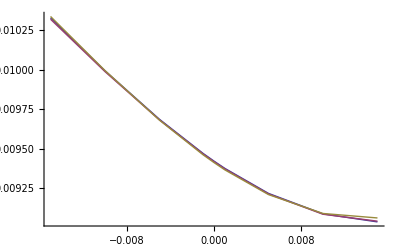
{19.531,-Graphics-}

```mathematica
Timing[Module[{S1=0.055,S2=0.051,T=10,VolS1=0.15,VolS2=0.2,Correl12=0.5,λ=0.1,LT=1.,ss,V0,ρ,ν,ss1,V01,ρ1,ν1,
nbstrike,strikes,bilogvols,hestonprices,hestonvols,hestonprices1,hestonvols1,bilogprices,nbsteps=10,scale=8,microratio=20,Vmultiplicator},
ss=Timing[HestonFromBilog[S1,S2,VolS1,VolS2,Correl12,T,λ,LT]];
V0=ss[[2,1]];ρ=ss[[2,2]];ν=ss[[2,3]];
Print["timing for the HestonFromBilog:",ss[[1]]," sec."];
Print["V0=",V0," ρ=",ρ," ν=",ν];
Vmultiplicator=Exp[0.026958633519421456 T-0.017202498337524928];
ss1=Timing[HestonFromBilogV0Fixed[S1,S2,VolS1,VolS2,Correl12,T,λ,LT,Vmultiplicator]];
V01=ss1[[2,1]];ρ1=ss1[[2,2]];ν1=ss1[[2,3]];
Print["timing for the HestonFromBilogV0Fixed:",ss1[[1]]," sec."];
Print["V0=",V01," ρ=",ρ1," ν=",ν1];
strikes={-0.015,-0.01,-0.005,-0.001,0,0.001,0.005,0.01,0.015};nbstrike=Length[strikes];
bilogprices=Table[LogNormalSpreadOption[S1,S2,VolS1,VolS2,Correl12,strikes[[i]],T,12],{i,1,nbstrike}];
bilogvols=Table[NormalImplicitVol[S1-S2,strikes[[i]],T,bilogprices[[i]]],{i,1,nbstrike}];
hestonprices=DerivativeHestonNormalCall[ρ,λ,LT,ν,V0,S1-S2,strikes,T,nbsteps,scale,microratio,0][[1]];
hestonvols=Table[NormalImplicitVol[S1-S2,strikes[[i]],T,hestonprices[[i]]],{i,1,nbstrike}];
hestonprices1=DerivativeHestonNormalCall[ρ1,λ,LT,ν1,V01,S1-S2,strikes,T,nbsteps,scale,microratio,0][[1]];
hestonvols1=Table[NormalImplicitVol[S1-S2,strikes[[i]],T,hestonprices1[[i]]],{i,1,nbstrike}];
Print["bilogprices=",bilogprices];Print["hestonprices=",hestonprices];Print["hestonpricesV0Fixed=",hestonprices1];
ListPlot[{Transpose[{strikes,bilogvols}],Transpose[{strikes,hestonvols}],Transpose[{strikes,hestonvols1}]},Joined->True, PlotLegend->{"bilog", "heston", "hestonV0Fixed"}]
]]
```

```mathematica
FindFit[{{2,0.9259933363933275},{3,0.946488},{5,0.987108},{10,1.11066},{15,1.28078},{20,1.49869}},0.879525 Exp[a x+b],{a,b},x]
```

{a→0.0269586,b→-0.0172025}

## Pricing du SpreadOption et du digital 1 - i Modele a 4 facteurs de vol + residus specifiques: dynamique

## Encodage de la dynamique pour le calcul du spreadoption

```mathematica
les browniens : {Subscript[W, 1],Subscript[W, 2],Subscript[W, 3],Subscript[W, 4],Subscript[W, 5],Subscript[W, i],Subscript[W̄, 1],Subscript[W̄, 2],Subscript[W̄, 3],Subscript[W̄, 4],Subscript[W̄, 5],Subscript[W̄, i]}
```

dS_1/S_1=∑_(j=1)^4 α_(1,j) √v_j dW_j+ √v_5 dW_5
dS_i/S_i=∑_(j=1)^4 α_(2,j) √v_j dW_j+√v_i dW_i
dv_1=λ_1(θ_1-v_1)dt+κ_1 √v_1 d(W̄)_1;
dv_2=λ_2(θ_2-v_2)dt+κ_2 √v_2 d(W̄)_2
dv_3=λ_3(θ_3-v_3)dt+κ_3 √v_3 d(W̄)_3
dv_4=λ_4(θ_4-v_4)dt+κ_4 √v_4 d(W̄)_4
dv_5=λ_5(θ_5-v_5)dt+κ_5 √v_5 d(W̄)_5
dv_i=λ_i(θ_i-v_i)dt+κ_i √v_i d(W̄)_i
 dW_1 d(W̄)_1=ρ_1 dt;
 dW_2 d(W̄)_2=ρ_2 dt;
 dW_3 d(W̄)_3=ρ_3 dt;
 dW_4 d(W̄)_4=ρ_4 dt;
 dW_5 d(W̄)_5=ρ_5 dt;
 dW_i d(W̄)_i=ρ_i dt;

```mathematica
AlphaDigitaleCorr={
{1,0,0,0,0,0,rho1,0,0,0,0,0},
{0,1,0,0,0,0,0,rho2,0,0,0,0},
{0,0,1,0,0,0,0,0,rho3,0,0,0},
{0,0,0,1,0,0,0,0,0,rho4,0,0},
{0,0,0,0,1,0,0,0,0,0,rho5,0},
{0,0,0,0,0,1,0,0,0,0,0,rhoi},
{rho1,0,0,0,0,0,1,0,0,0,0,0},
{0,rho2,0,0,0,0,0,1,0,0,0,0},
{0,0,rho3,0,0,0,0,0,1,0,0,0},
{0,0,0,rho4,0,0,0,0,0,1,0,0},
{0,0,0,0,rho5,0,0,0,0,0,1,0},
{0,0,0,0,0,rhoi,0,0,0,0,0,1}
};
```

```mathematica
AlphaDigitaleDiff[x_]:=
D[x,S1]{alpha11 √V1 S1,alpha12 √V2 S1,alpha13 √V3 S1,alpha14 √V4 S1,√V5 S1,0,0,0,0,0,0,0}+
D[x,Si]{alphai1 √V1 Si,alphai2 √V2 Si,alphai3 √V3 Si,alphai4 √V4 Si,0,√Vi Si,0,0,0,0,0,0}+
D[x,V1]{0,0,0,0,0,0,kappaV1 √V1,0,0,0,0,0}+
D[x,V2]{0,0,0,0,0,0,0,kappaV2 √V2,0,0,0,0}+
D[x,V3]{0,0,0,0,0,0,0,0,kappaV3 √V3,0,0,0}+
D[x,V4]{0,0,0,0,0,0,0,0,0,kappaV4 √V4,0,0}+
D[x,V5]{0,0,0,0,0,0,0,0,0,0,kappaV5 √V5,0}+
D[x,Vi]{0,0,0,0,0,0,0,0,0,0,0,kappaVi √Vi}
```

```mathematica
dans une autre measure ( la mesure Subscript[S, 1] pour  le calcul de E[Subscript[1, Subscript[S, 1]-Subscript[S, 2]>K]]) seul le drift differe
```

## Calcul des observables (VS, VarVS, COVarSVS) incrementale

```mathematica
zeroRuleU1i={kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaVi->0};
```

```mathematica
CompuputePureFunctionQuadriBiSuperHestonSpreadU1iObservable[spread_]:=
Module[{VS,VarVS,VarVS0,CoVarVS,CoVarVS0},
VS=Simplify[AlphaDigitaleDiff[spread].(AlphaDigitaleCorr.AlphaDigitaleDiff[spread])];
VarVS=Simplify[AlphaDigitaleDiff[VS].(AlphaDigitaleCorr.AlphaDigitaleDiff[VS])];
VarVS0=VarVS/.zeroRuleU1i;
CoVarVS=Simplify[AlphaDigitaleDiff[VS].(AlphaDigitaleCorr.AlphaDigitaleDiff[spread])];
CoVarVS0=CoVarVS /.zeroRuleU1i;
Apply[Function,{{S1,Si,
alpha11,alpha12,alpha13,alpha14,
alphai1,alphai2,alphai3,alphai4,
rho1,kappaV1,V1,
rho2,kappaV2,V2,
rho3,kappaV3,V3,
rho4,kappaV4,V4,
rho5,kappaV5,V5,
rhoi,kappaVi,Vi},
{VS,Simplify[VarVS-VarVS0],Simplify[CoVarVS-CoVarVS0],Simplify[VarVS0],Simplify[CoVarVS0]}}]];
```

```mathematica
On a aucune raison de penser que Subscript[ΔV, α]  est different de zero car VS= (alpha11 S1-alphai1 Si)^2 V1+(alpha12 S1-alphai2 Si)^2 V2+(alpha13 S1-alphai3 Si)^2 V3+(alpha14 S1-alphai4 Si)^2 V4+S1^2 V5+Si^2 Vi
```

```mathematica
et donc ne depends pas de la vol de vol.
```

```mathematica
?AlphaDigitaleObservable1iz
```

```mathematica
AlphaDigitaleObservable1iz=CompuputePureFunctionQuadriBiSuperHestonSpreadU1iObservable[(Si-S1)];
```

```mathematica
VSSpread1iz[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρi_,νi_,V0i_]:=AlphaDigitaleObservable1iz[S1,Si,
alpha11,alpha12,alpha13,alpha14,
alphai1,alphai2,alphai3,alphai4,
rho1,kappaV1,V1,
rho2,kappaV2,V2,
rho3,kappaV3,V3,
rho4,kappaV4,V4,
rho5,kappaV5,V5,
rhoi,kappaVi,Vi][[1]]
```

```mathematica
VarVSSpread1iz[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρi_,νi_,V0i_]:=AlphaDigitaleObservable1iz[S1,Si,
alpha11,alpha12,alpha13,alpha14,
alphai1,alphai2,alphai3,alphai4,
rho1,kappaV1,V1,
rho2,kappaV2,V2,
rho3,kappaV3,V3,
rho4,kappaV4,V4,
rho5,kappaV5,V5,
rhoi,kappaVi,Vi][[2]]
```

```mathematica
CoVarVSSpread1iz[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρi_,νi_,V0i_]:=AlphaDigitaleObservable1iz[S1,Si,
alpha11,alpha12,alpha13,alpha14,
alphai1,alphai2,alphai3,alphai4,
rho1,kappaV1,V1,
rho2,kappaV2,V2,
rho3,kappaV3,V3,
rho4,kappaV4,V4,
rho5,kappaV5,V5,
rhoi,kappaVi,Vi][[3]]
```

```mathematica
AlphaDigitaleObservable1iz[S1,Si,
alpha11,alpha12,alpha13,alpha14,
alphai1,alphai2,alphai3,alphai4,
rho1,kappaV1,V1,
rho2,kappaV2,V2,
rho3,kappaV3,V3,
rho4,kappaV4,V4,
rho5,kappaV5,V5,
rhoi,kappaVi,Vi][[4]]
```

4 S1^2 V5 (alpha11^2 S1 V1-alpha11 alphai1 Si V1+alpha12^2 S1 V2-alpha12 alphai2 Si V2+alpha13^2 S1 V3-alpha13 alphai3 Si V3+alpha14^2 S1 V4-alpha14 alphai4 Si V4+S1 V5)^2+4 Si^2 Vi (-alpha11 alphai1 S1 V1+alphai1^2 Si V1-alpha12 alphai2 S1 V2+alphai2^2 Si V2-alpha13 alphai3 S1 V3+alphai3^2 Si V3-alpha14 alphai4 S1 V4+alphai4^2 Si V4+Si Vi)^2+V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alphai1 Si V1+alpha12^2 S1 V2-alpha12 alphai2 Si V2+alpha13^2 S1 V3-alpha13 alphai3 Si V3+alpha14^2 S1 V4-alpha14 alphai4 Si V4+S1 V5)+2 alphai1 Si (-alpha11 alphai1 S1 V1+alphai1^2 Si V1-alpha12 alphai2 S1 V2+alphai2^2 Si V2-alpha13 alphai3 S1 V3+alphai3^2 Si V3-alpha14 alphai4 S1 V4+alphai4^2 Si V4+Si Vi))^2+V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alphai1 Si V1+alpha12^2 S1 V2-alpha12 alphai2 Si V2+alpha13^2 S1 V3-alpha13 alphai3 Si V3+alpha14^2 S1 V4-alpha14 alphai4 Si V4+S1 V5)+2 alphai2 Si (-alpha11 alphai1 S1 V1+alphai1^2 Si V1-alpha12 alphai2 S1 V2+alphai2^2 Si V2-alpha13 alphai3 S1 V3+alphai3^2 Si V3-alpha14 alphai4 S1 V4+alphai4^2 Si V4+Si Vi))^2+V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alphai1 Si V1+alpha12^2 S1 V2-alpha12 alphai2 Si V2+alpha13^2 S1 V3-alpha13 alphai3 Si V3+alpha14^2 S1 V4-alpha14 alphai4 Si V4+S1 V5)+2 alphai3 Si (-alpha11 alphai1 S1 V1+alphai1^2 Si V1-alpha12 alphai2 S1 V2+alphai2^2 Si V2-alpha13 alphai3 S1 V3+alphai3^2 Si V3-alpha14 alphai4 S1 V4+alphai4^2 Si V4+Si Vi))^2+V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alphai1 Si V1+alpha12^2 S1 V2-alpha12 alphai2 Si V2+alpha13^2 S1 V3-alpha13 alphai3 Si V3+alpha14^2 S1 V4-alpha14 alphai4 Si V4+S1 V5)+2 alphai4 Si (-alpha11 alphai1 S1 V1+alphai1^2 Si V1-alpha12 alphai2 S1 V2+alphai2^2 Si V2-alpha13 alphai3 S1 V3+alphai3^2 Si V3-alpha14 alphai4 S1 V4+alphai4^2 Si V4+Si Vi))^2

```mathematica
AlphaDigitaleObservable1iz[S1,Si,
alpha11,alpha12,alpha13,alpha14,
alphai1,alphai2,alphai3,alphai4,
rho1,kappaV1,V1,
rho2,kappaV2,V2,
rho3,kappaV3,V3,
rho4,kappaV4,V4,
rho5,kappaV5,V5,
rhoi,kappaVi,Vi][[5]]
```

2 S1^2 V5 (alpha11^2 S1 V1-alpha11 alphai1 Si V1+alpha12^2 S1 V2-alpha12 alphai2 Si V2+alpha13^2 S1 V3-alpha13 alphai3 Si V3+alpha14^2 S1 V4-alpha14 alphai4 Si V4+S1 V5)-2 Si^2 Vi (-alpha11 alphai1 S1 V1+alphai1^2 Si V1-alpha12 alphai2 S1 V2+alphai2^2 Si V2-alpha13 alphai3 S1 V3+alphai3^2 Si V3-alpha14 alphai4 S1 V4+alphai4^2 Si V4+Si Vi)+(alpha11 S1-alphai1 Si) V1 (2 alpha11 S1 (alpha11^2 S1 V1-alpha11 alphai1 Si V1+alpha12^2 S1 V2-alpha12 alphai2 Si V2+alpha13^2 S1 V3-alpha13 alphai3 Si V3+alpha14^2 S1 V4-alpha14 alphai4 Si V4+S1 V5)+2 alphai1 Si (-alpha11 alphai1 S1 V1+alphai1^2 Si V1-alpha12 alphai2 S1 V2+alphai2^2 Si V2-alpha13 alphai3 S1 V3+alphai3^2 Si V3-alpha14 alphai4 S1 V4+alphai4^2 Si V4+Si Vi))+(alpha12 S1-alphai2 Si) V2 (2 alpha12 S1 (alpha11^2 S1 V1-alpha11 alphai1 Si V1+alpha12^2 S1 V2-alpha12 alphai2 Si V2+alpha13^2 S1 V3-alpha13 alphai3 Si V3+alpha14^2 S1 V4-alpha14 alphai4 Si V4+S1 V5)+2 alphai2 Si (-alpha11 alphai1 S1 V1+alphai1^2 Si V1-alpha12 alphai2 S1 V2+alphai2^2 Si V2-alpha13 alphai3 S1 V3+alphai3^2 Si V3-alpha14 alphai4 S1 V4+alphai4^2 Si V4+Si Vi))+(alpha13 S1-alphai3 Si) V3 (2 alpha13 S1 (alpha11^2 S1 V1-alpha11 alphai1 Si V1+alpha12^2 S1 V2-alpha12 alphai2 Si V2+alpha13^2 S1 V3-alpha13 alphai3 Si V3+alpha14^2 S1 V4-alpha14 alphai4 Si V4+S1 V5)+2 alphai3 Si (-alpha11 alphai1 S1 V1+alphai1^2 Si V1-alpha12 alphai2 S1 V2+alphai2^2 Si V2-alpha13 alphai3 S1 V3+alphai3^2 Si V3-alpha14 alphai4 S1 V4+alphai4^2 Si V4+Si Vi))+(alpha14 S1-alphai4 Si) V4 (2 alpha14 S1 (alpha11^2 S1 V1-alpha11 alphai1 Si V1+alpha12^2 S1 V2-alpha12 alphai2 Si V2+alpha13^2 S1 V3-alpha13 alphai3 Si V3+alpha14^2 S1 V4-alpha14 alphai4 Si V4+S1 V5)+2 alphai4 Si (-alpha11 alphai1 S1 V1+alphai1^2 Si V1-alpha12 alphai2 S1 V2+alphai2^2 Si V2-alpha13 alphai3 S1 V3+alphai3^2 Si V3-alpha14 alphai4 S1 V4+alphai4^2 Si V4+Si Vi))

## Pricing du SpreadOption 1 - i Modele a 2 facteurs de vol + residus specifiques

## Encodage de la dynamique pour le calcul du spreadoption

```mathematica
les browniens : {Subscript[W, 1],Subscript[W, 2],Subscript[W, 3],Subscript[W̄, 1],Subscript[W̄, 2],Subscript[W̄, 3]}
```

(dS_(1,t))/(S_(1,t))=α √(v_(2,t)) dW_(2,t)+√(v_(1,t)) dW_(1,t);
(dS_(2,t))/(S_(2,t))=β √(v_(2,t)) dW_(2,t)+√(v_(3,t)) dW_(3,t);
dv_(1,t)=λ_1(θ_1-v_(1,t))dt+κ_1 √(v_(1,t)) d(W̄)_(1,t);
dv_(2,t)=λ_2(θ_2-v_(2,t))dt+κ_2 √(v_(2,t)) d(W̄)_(2,t);
dv_(3,t)=λ_3(θ_3-v_(3,t))dt+κ_3 √(v_(3,t)) d(W̄)_(3,t)
 dW_(1,t)d(W̄)_(1,t)=ρ_1 dt;dW_(2,t)d(W̄)_(2,t)=ρ_2 dt; dW_(3,t)d(W̄)_(3,t)=ρ_3 dt

```mathematica
BiSuperDigitaleCorr={
{1,0,0,rho1,0,0},
{0,1,0,0,rho2,0},
{0,0,1,0,0,rho3},
{rho1,0,0,1,0,0},
{0,rho2,0,0,1,0},
{0,0,rho3,0,0,1}
};
```

```mathematica
BiSuperDigitaleDiff[x_]:=
D[x,S1]{√V1 S1,alpha √V2 S1,0,0,0,0}+
D[x,S2]{0,beta √V2 S2, √V3 S2,0,0,0}+
D[x,V1]{0,0,0,kappaV1 √V1,0,0}+
D[x,V2]{0,0,0,0,kappaV2 √V2,0}+
D[x,V3]{0,0,0,0,0,kappaV3 √V3}
```

```mathematica
dans une autre measure ( la mesure Subscript[S, 1] pour  le calcul de E[Subscript[1, Subscript[S, 1]-Subscript[S, 2]>K]]) seul le drift differe
```

## Calcul des observables (VS, VarVS, COVarSVS) incrementale

```mathematica
zeroRule={kappaV1->0,kappaV2->0,kappaV3->0};
```

```mathematica
CompuputePureFunctionBiSuperHestonSpreadU1iObservable[spread_]:=
Module[{VS,VarVS,VarVS0,CoVarVS,CoVarVS0},
VS=Simplify[BiSuperDigitaleDiff[spread].(BiSuperDigitaleCorr.BiSuperDigitaleDiff[spread])];
VarVS=Simplify[BiSuperDigitaleDiff[VS].(BiSuperDigitaleCorr.BiSuperDigitaleDiff[VS])];
VarVS0=VarVS/.zeroRule;
CoVarVS=Simplify[BiSuperDigitaleDiff[VS].(BiSuperDigitaleCorr.BiSuperDigitaleDiff[spread])];
CoVarVS0=CoVarVS /.zeroRule;
Apply[Function,{{S1,S2,
alpha,beta,
rho1,kappaV1,V1,
rho2,kappaV2,V2,
rho3,kappaV3,V3},
{VS,Simplify[VarVS-VarVS0],Simplify[CoVarVS-CoVarVS0],Simplify[VarVS0],Simplify[CoVarVS0]}}]];
```

```mathematica
BiSuperDigitaleObservable1iz=CompuputePureFunctionBiSuperHestonSpreadU1iObservable[(S2-S1)];
```

```mathematica
CForm[BiSuperDigitaleObservable1iz[S1,S2,
alpha2,beta2,
rho1,kappaV1,V1,
rho2,kappaV2,V2,
rho3,kappaV3,V3][[1]]]
```

Power(S1,2)*V1 + Power(alpha2*S1 - beta2*S2,2)*V2 + Power(S2,2)*V3

```mathematica
CForm[BiSuperDigitaleObservable1iz[S1,S2,
alpha2,beta2,
rho1,kappaV1,V1,
rho2,kappaV2,V2,
rho3,kappaV3,V3][[2]]]
```

Power(kappaV1,2)*Power(S1,4)*V1 + 4*Power(alpha2,5)*kappaV2*rho2*Power(S1,4)*Power(V2,2) + 
   Power(alpha2,4)*kappaV2*Power(S1,3)*V2*(kappaV2*S1 - 12*beta2*rho2*S2*V2) - 
   4*Power(alpha2,3)*kappaV2*Power(S1,2)*V2*(beta2*kappaV2*S1*S2 - rho2*Power(S1,2)*V1 + Power(beta2,2)*rho2*(S1 - 3*S2)*S2*V2) + 
   4*kappaV1*rho1*Power(S1,3)*V1*(-(alpha2*beta2*S2*V2) + S1*(V1 + Power(alpha2,2)*V2)) + 
   Power(S2,4)*(Power(beta2,4)*Power(kappaV2,2)*V2 + 4*Power(beta2,5)*kappaV2*rho2*Power(V2,2) + 4*Power(beta2,3)*kappaV2*rho2*V2*V3 + 
      4*Power(beta2,2)*kappaV3*rho3*V2*V3 + kappaV3*V3*(kappaV3 + 4*rho3*V3)) + 
   2*Power(alpha2,2)*beta2*kappaV2*S1*S2*V2*(3*beta2*kappaV2*S1*S2 + 2*Power(beta2,2)*rho2*(3*S1 - S2)*S2*V2 + 2*rho2*S1*(-2*S1*V1 + S2*V3)) - 
   4*alpha2*beta2*S1*Power(S2,2)*V2*(Power(beta2,2)*Power(kappaV2,2)*S2 + 3*Power(beta2,3)*kappaV2*rho2*S2*V2 + kappaV3*rho3*S2*V3 + 
      beta2*kappaV2*rho2*(-(S1*V1) + 2*S2*V3))

```mathematica
CForm[BiSuperDigitaleObservable1iz[S1,S2,
alpha2,beta2,
rho1,kappaV1,V1,
rho2,kappaV2,V2,
rho3,kappaV3,V3][[3]]]
```

kappaV1*rho1*Power(S1,3)*V1 + kappaV2*rho2*Power(alpha2*S1 - beta2*S2,3)*V2 - kappaV3*rho3*Power(S2,3)*V3

```mathematica
CForm[BiSuperDigitaleObservable1iz[S1,S2,
alpha2,beta2,
rho1,kappaV1,V1,
rho2,kappaV2,V2,
rho3,kappaV3,V3][[4]]]
```

4*Power(S1,2)*V1*Power(alpha2*beta2*S2*V2 - S1*(V1 + Power(alpha2,2)*V2),2) + 4*Power(S2,2)*V3*Power(alpha2*beta2*S1*V2 - S2*(Power(beta2,2)*V2 + V3),2) + 
   V2*Power(2*alpha2*S1*(-(alpha2*beta2*S2*V2) + S1*(V1 + Power(alpha2,2)*V2)) + 2*beta2*S2*(-(alpha2*beta2*S1*V2) + S2*(Power(beta2,2)*V2 + V3)),2)

```mathematica
CForm[BiSuperDigitaleObservable1iz[S1,S2,
alpha2,beta2,
rho1,kappaV1,V1,
rho2,kappaV2,V2,
rho3,kappaV3,V3][[5]]]
```

2*Power(S1,3)*Power(V1 + Power(alpha2,2)*V2,2) - 2*alpha2*beta2*Power(S1,2)*S2*V2*(2*V1 + alpha2*(2*alpha2 + beta2)*V2) - 
   2*Power(S2,3)*Power(Power(beta2,2)*V2 + V3,2) + 2*alpha2*beta2*S1*Power(S2,2)*V2*(alpha2*beta2*V2 + 2*(Power(beta2,2)*V2 + V3))

## Implementation de SmileAlphaSpreadOption et de AlphaGenericComputeSpreadOption

```mathematica
ComputeEquivalentBilogFromAlpha[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,T_]:=
Module[{equivalentσ1,equivalentσ2,equivalentρ},
equivalentσ1=√(α11^2 V1+α12^2 V2+α13^2 V3+α14^2 V4+V5);
equivalentσ2=√(αi1^2 V1+αi2^2 V2+αi3^2 V3+αi4^2 V4+Vi);
equivalentρ=(α11 αi1 V1+α12 αi2 V2+α13 αi3 V3+α14 αi4 V4)/(equivalentσ1 equivalentσ2);
{equivalentσ1,equivalentσ2,equivalentρ}
]
```

```mathematica
AlphaGenericComputeSpreadOption[S1_,S2_,Sig1_,Sig2_,Correl12_,VS_,VarVSIncremental_,CoVarSVSIncremental_,LTFactorS_,λS_,SpreadStrikes_,τ_,LimitGindinkin_,printflag_]:=Module[{ρprojeté,numinimum,rhominimum,V0projeté,V0minimim,V0Effectif,VarVSTotal,CoVarSVSTotal,νprojeté,prices,
nbsteps=10,scale=8,microratio=20},
(* Calcul de l'equivalent lognormal *)
{V0minimim,rhominimum,numinimum}=HestonFromBilog[S1,S2,Sig1,Sig2,Correl12,τ,λS,LTFactorS];
If[printflag==1 || MemberQ[printflag,1] ,Print["Mode 2 :  Numinimum=",numinimum," rhominimum= ",rhominimum," V0minimim=",V0minimim]];
(* Calcul des parametres totaux *)
V0Effectif=V0minimim;
VarVSTotal=VarVSIncremental+numinimum^2 V0minimim;
CoVarSVSTotal=CoVarSVSIncremental+rhominimum V0minimim numinimum;
ρprojeté=CoVarSVSTotal/(√(V0minimim VarVSTotal));νprojeté=√(VarVSTotal/V0minimim);V0projeté=V0minimim;

If[printflag==1 || MemberQ[printflag,1] ,Print["Normal Heston Parameters=",{{"S0",S1-S2},{"V0",V0projeté},{"θ",V0projeté LTFactorS },{"λv",λS},{"ρ",ρprojeté},{"ν",νprojeté},
{"ν normalized",νprojeté/(√V0projeté)},{"standard dev equi.",√V0projeté}} //MatrixForm]];
prices=DerivativeHestonNormalCall[ρprojeté,λS,LTFactorS,νprojeté,V0Effectif,S1-S2,SpreadStrikes,τ,nbsteps,scale,microratio,0][[1]];
If[printflag==1 || MemberQ[printflag,1] ,Print["prices=",prices]];
prices
]
```

```mathematica
SmileAlphaSpreadOption[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_,T_,LimitGindinkin_,printflag_,bilogHestonFlag_]:=SmileAlphaSpreadOptionlist[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,{K},T,LimitGindinkin,printflag,bilogHestonFlag][[1]]
```

```mathematica
SmileAlphaSpreadOption[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_List,T_,LimitGindinkin_,printflag_,bilogHestonFlag_]:=SmileAlphaSpreadOptionlist[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,K,T,LimitGindinkin,printflag,bilogHestonFlag]
```

```mathematica
SmileAlphaSpreadOptionlist[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_List,T_,LimitGindinkin_,printflag_,bilogHestonFlag_]:=Module[{ρprojeté,νprojeté,prices,VarVSIncrementale,CoVarSVSIncrementale,VS,Sig1,Sig2,Correl12,numinimum,rhominimum,λsmooth,VarVSTotal,Vmultiplicator,CoVarSVSTotal,digitaleprices,forward,V0projeté,V0minimim,nbsteps=20,scale=10,microratio=20},
Sig1=√(α11^2 V1+α12^2 V2+α13^2 V3+α14^2 V4+V5);Sig2=√(αi1^2 V1+αi2^2 V2+αi3^2 V3+αi4^2 V4+Vi);Correl12= (α11 αi1  V1+α12 αi2  V2+α13 αi3  V3+α14 αi4  V4)/(Sig1 Sig2);Vmultiplicator=Exp[0.026958633519421456 T-0.017202498337524928];λsmooth=10;
Print["S1,Si,Sig1,Sig2,Correl12,T=",{S1,Si,Sig1,Sig2,Correl12,T}];
Switch[bilogHestonFlag,
0,
{V0minimim,rhominimum,numinimum}=HestonFromBilog[S1,Si,Sig1,Sig2,Correl12,T,λ,LT],
1,
{V0minimim,rhominimum,numinimum}=HestonFromBilogV0Fixed[S1,Si,Sig1,Sig2,Correl12,T,λ,LT,Vmultiplicator],
2,
{V0minimim,rhominimum,numinimum}=HestonFromBilogPackaged[S1,Si,Sig1,Sig2,Correl12,T,λ,LT,λsmooth]];
If[printflag==1 || MemberQ[printflag,1] ,Print["V0minimim=",V0minimim," rhominimum= ",rhominimum," Numinimum=",numinimum]];
If[printflag==1 || MemberQ[printflag,1] ,Print["VSminimale=",V0minimim," VarVSminimale=",numinimum^2 V0minimim," CoVarSVSminimale=",rhominimum V0minimim numinimum]];
{VS,VarVSIncrementale,CoVarSVSIncrementale}=AlphaDigitaleObservable1iz[S1,Si,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi];
If[printflag==1 || MemberQ[printflag,1] ,Print["VSBlack=",VS," VarVSIncrementale=",VarVSIncrementale," CoVarSVSIncrementale=",CoVarSVSIncrementale]];
VarVSTotal=VarVSIncrementale+numinimum^2 V0minimim;
CoVarSVSTotal=CoVarSVSIncrementale+rhominimum V0minimim numinimum;
If[printflag==1 || MemberQ[printflag,1] ,Print["VSTotal=",V0minimim," VarVSTotal=",VarVSTotal," CoVarSVSTotal= ",CoVarSVSTotal]];
ρprojeté=CoVarSVSTotal/(√(V0minimim VarVSTotal));νprojeté=√(VarVSTotal/V0minimim);V0projeté=V0minimim;
forward=S1-Si;
If[printflag==1 || MemberQ[printflag,1] ,Print["Normal Heston Parameters=",{{"S0",forward},{"V0",V0projeté},{"ρ",ρprojeté},{"ν",νprojeté},
{"standard dev equi.",√VS},{"ν normalized",νprojeté/(√VS)}} //MatrixForm]];
DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,V0projeté,S1-Si,K,T,nbsteps,scale,microratio,0][[1]]
]
```

## Exemples de spreadoption

S1,Si,Sig1,Sig2,Correl12,T={0.05,0.051,0.0374166,0.0374166,0.,5}

Stdev(pour le calcul des strike)=0.00597553

strikes={-0.00199184,-0.000995922,0,0.000995922,0.00199184}

pricegoaltable={0.0029117,0.00238046,0.00191563,0.0015163,0.00117977}

optimisation results:{3.30978×10^-18,{7.16632×10^-6,-0.0145711,0.000338385}}

V0minimim=7.16632×10^-6 rhominimum= -0.0145711 Numinimum=0.000338385

VSminimale=7.16632×10^-6 VarVSminimale=8.20576×10^-13 CoVarSVSminimale=-3.53346×10^-11

VSBlack=7.1414×10^-6 VarVSIncrementale=-2.19083×10^-25 CoVarSVSIncrementale=-1.20269×10^-21

VSTotal=7.16632×10^-6 VarVSTotal=8.20576×10^-13 CoVarSVSTotal= -3.53346×10^-11

Normal Heston Parameters=(S0 | -0.001
V0 | 7.16632×10^-6
ρ | -0.0145711
ν | 0.000338385
standard dev equi. | 0.00267234
ν normalized | 0.126625)

S1,Si,Sig1,Sig2,Correl12,T={0.05,0.051,0.0374166,0.0374166,0.,5}

Stdev(pour le calcul des strike)=0.00597553

strikes={-0.00199184,-0.000995922,0,0.000995922,0.00199184}

pricegoaltable={0.0029117,0.00238046,0.00191563,0.0015163,0.00117977}

optimisation results:{3.30978×10^-18,{7.16632×10^-6,-0.0145711,0.000338385}}

V0minimim=7.16632×10^-6 rhominimum= -0.0145711 Numinimum=0.000338385

VSminimale=7.16632×10^-6 VarVSminimale=8.20576×10^-13 CoVarSVSminimale=-3.53346×10^-11

VSBlack=7.1414×10^-6 VarVSIncrementale=2.05542×10^-10 CoVarSVSIncrementale=-1.50336×10^-8

VSTotal=7.16632×10^-6 VarVSTotal=2.06362×10^-10 CoVarSVSTotal= -1.5069×10^-8

Normal Heston Parameters=(S0 | -0.001
V0 | 7.16632×10^-6
ρ | -0.39185
ν | 0.00536621
standard dev equi. | 0.00267234
ν normalized | 2.00806)

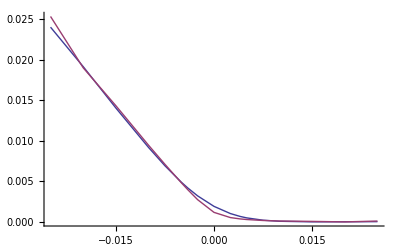
{17.031,-Graphics-}

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,S1=0.05,Si=0.051,
T=5,λ=0.1,LT=1,
KList={-0.025,-0.02,-0.015,-0.01,-0.0075,-0.005,-0.004,-0.0025,0,0.0025,0.004,0.005,0.0075,0.01,0.015,0.02,0.025},LimitGindinkin=5,printflag=1,prices,νcommun,νcommun1,bilogprices,bilogHestonFlag=0},
V1=1;V2=1;V3=1;V4=1;V5=0.001;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;
αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;
νcommun=0.0000000000004;
ρ1=-0.5;ν1=νcommun;ρ2=-0.5;ν2=νcommun;ρ3=-0.5;ν3=νcommun;ρ4=-0.5;ν4=νcommun;ρ5=-0.5;ν5=νcommun √V5;ρi=-0.5;νi=νcommun √Vi;
bilogprices=SmileAlphaSpreadOption[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,bilogHestonFlag];
νcommun1=5;
ρ1=-0.5;ν1=νcommun1;ρ2=-0.5;ν2=νcommun1;ρ3=-0.5;ν3=νcommun1;ρ4=-0.5;ν4=νcommun1;ρ5=-0.5;ν5=νcommun1 √V5;ρi=-0.5;νi=νcommun1 √Vi;
prices=SmileAlphaSpreadOption[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,bilogHestonFlag];
ListPlot[{Transpose[{KList,bilogprices}],Transpose[{KList,prices}]},Joined->True]
]]]
```

Stdev(pour le calcul des strike)=0.0063374

strikes={-0.00211247,-0.00105623,0,0.00105623,0.00211247}

pricegoaltable={0.00298053,0.00241074,0.00191563,0.00149417,0.00114308}

optimisation results:{4.09506×10^-10,{8.03253×10^-6,-0.0759145,0.00188537}}

V0minimim=8.03253×10^-6 rhominimum= -0.0759145 Numinimum=0.00188537

VSminimale=8.03253×10^-6 VarVSminimale=2.85525×10^-11 CoVarSVSminimale=-1.14967×10^-9

VSBlack=7.1414×10^-6 VarVSIncrementale=-2.19083×10^-25 CoVarSVSIncrementale=-1.20269×10^-21

VSTotal=8.03253×10^-6 VarVSTotal=2.85525×10^-11 CoVarSVSTotal= -1.14967×10^-9

Normal Heston Parameters=(S0 | -0.001
V0 | 8.03253×10^-6
ρ | -0.0759145
ν | 0.00188537
standard dev equi. | 0.00267234
ν normalized | 0.705511)

Stdev(pour le calcul des strike)=0.0063374

strikes={-0.00211247,-0.00105623,0,0.00105623,0.00211247}

pricegoaltable={0.00298053,0.00241074,0.00191563,0.00149417,0.00114308}

optimisation results:{4.09506×10^-10,{8.03253×10^-6,-0.0759145,0.00188537}}

V0minimim=8.03253×10^-6 rhominimum= -0.0759145 Numinimum=0.00188537

VSminimale=8.03253×10^-6 VarVSminimale=2.85525×10^-11 CoVarSVSminimale=-1.14967×10^-9

VSBlack=7.1414×10^-6 VarVSIncrementale=2.05542×10^-10 CoVarSVSIncrementale=-1.50336×10^-8

VSTotal=8.03253×10^-6 VarVSTotal=2.34094×10^-10 CoVarSVSTotal= -1.61833×10^-8

Normal Heston Parameters=(S0 | -0.001
V0 | 8.03253×10^-6
ρ | -0.373203
ν | 0.00539845
standard dev equi. | 0.00267234
ν normalized | 2.02012)

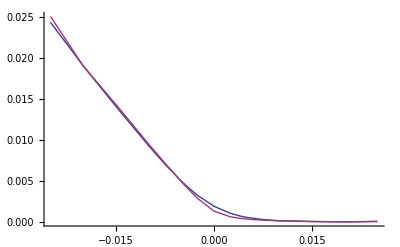
{91.203,-Graphics-}

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,S1=0.05,Si=0.051,
T=5,λ=0.1,LT=1,
KList={-0.025,-0.02,-0.015,-0.01,-0.0075,-0.005,-0.004,-0.0025,0,0.0025,0.004,0.005,0.0075,0.01,0.015,0.02,0.025},LimitGindinkin=5,printflag=1,prices,νcommun,νcommun1,bilogprices,bilogHestonFlag=1},
V1=1;V2=1;V3=1;V4=1;V5=0.001;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;
αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;
νcommun=0.0000000000004;
ρ1=-0.5;ν1=νcommun;ρ2=-0.5;ν2=νcommun;ρ3=-0.5;ν3=νcommun;ρ4=-0.5;ν4=νcommun;ρ5=-0.5;ν5=νcommun √V5;ρi=-0.5;νi=νcommun √Vi;
bilogprices=SmileAlphaSpreadOption[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,bilogHestonFlag];
νcommun1=5;
ρ1=-0.5;ν1=νcommun1;ρ2=-0.5;ν2=νcommun1;ρ3=-0.5;ν3=νcommun1;ρ4=-0.5;ν4=νcommun1;ρ5=-0.5;ν5=νcommun1 √V5;ρi=-0.5;νi=νcommun1 √Vi;
prices=SmileAlphaSpreadOption[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,bilogHestonFlag];
ListPlot[{Transpose[{KList,bilogprices}],Transpose[{KList,prices}]},Joined->True]
]]]
```

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,S1=0.05,Si=0.051,
T=5,λ=0.1,LT=1,
KList={-0.025,-0.02,-0.015,-0.01,-0.0075,-0.005,-0.004,-0.0025,0,0.0025,0.004,0.005,0.0075,0.01,0.015,0.02,0.025},LimitGindinkin=5,printflag=1,prices,νcommun,νcommun1,bilogprices,bilogHestonFlag=2},
V1=1;V2=1;V3=1;V4=1;V5=0.001;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;
αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;
νcommun=0.0000000000004;
ρ1=-0.5;ν1=νcommun;ρ2=-0.5;ν2=νcommun;ρ3=-0.5;ν3=νcommun;ρ4=-0.5;ν4=νcommun;ρ5=-0.5;ν5=νcommun √V5;ρi=-0.5;νi=νcommun √Vi;
bilogprices=SmileAlphaSpreadOption[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,bilogHestonFlag];
νcommun1=5;
ρ1=-0.5;ν1=νcommun1;ρ2=-0.5;ν2=νcommun1;ρ3=-0.5;ν3=νcommun1;ρ4=-0.5;ν4=νcommun1;ρ5=-0.5;ν5=νcommun1 √V5;ρi=-0.5;νi=νcommun1 √Vi;
prices=SmileAlphaSpreadOption[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,bilogHestonFlag];
ListPlot[{Transpose[{KList,bilogprices}],Transpose[{KList,prices}]},Joined->True]
]]]
```

S1,Si,Sig1,Sig2,Correl12,T={0.05,0.051,0.0374166,0.0374166,0.,5}

InitialV0=7.1414×10^-6 νup=0.00534468 Stdev(pour le calcul des strike)=0.00597553

strikes={-0.00199184,-0.000995922,0,0.000995922,0.00199184}

pricegoaltable={0.0029117,0.00238046,0.00191563,0.0015163,0.00117977}

optimisation results:{3.35891×10^-18,{7.69795×10^-8,-0.0145724,0.000249538}}

V0minimim=7.16632×10^-6 rhominimum= -0.0145711 Numinimum=0.00033838

VSminimale=7.16632×10^-6 VarVSminimale=8.20553×10^-13 CoVarSVSminimale=-3.5334×10^-11

VSBlack=7.1414×10^-6 VarVSIncrementale=-2.19083×10^-25 CoVarSVSIncrementale=-1.20269×10^-21

VSTotal=7.16632×10^-6 VarVSTotal=8.20553×10^-13 CoVarSVSTotal= -3.5334×10^-11

Normal Heston Parameters=(S0 | -0.001
V0 | 7.16632×10^-6
ρ | -0.0145711
ν | 0.00033838
standard dev equi. | 0.00267234
ν normalized | 0.126623)

S1,Si,Sig1,Sig2,Correl12,T={0.05,0.051,0.0374166,0.0374166,0.,5}

InitialV0=7.1414×10^-6 νup=0.00534468 Stdev(pour le calcul des strike)=0.00597553

strikes={-0.00199184,-0.000995922,0,0.000995922,0.00199184}

pricegoaltable={0.0029117,0.00238046,0.00191563,0.0015163,0.00117977}

optimisation results:{3.35891×10^-18,{7.69795×10^-8,-0.0145724,0.000249538}}

V0minimim=7.16632×10^-6 rhominimum= -0.0145711 Numinimum=0.00033838

VSminimale=7.16632×10^-6 VarVSminimale=8.20553×10^-13 CoVarSVSminimale=-3.5334×10^-11

VSBlack=7.1414×10^-6 VarVSIncrementale=2.05542×10^-10 CoVarSVSIncrementale=-1.50336×10^-8

VSTotal=7.16632×10^-6 VarVSTotal=2.06362×10^-10 CoVarSVSTotal= -1.5069×10^-8

Normal Heston Parameters=(S0 | -0.001
V0 | 7.16632×10^-6
ρ | -0.39185
ν | 0.00536621
standard dev equi. | 0.00267234
ν normalized | 2.00806)

{89.313,-Graphics-}

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.055,T=10,equivalentσ1,equivalentσi,equivalentρ,bilogdigitale,bilogtohestonflag,
bilogSpreadoptionGRAPH,alphaSpreadoptionGRAPH,paysS1GRAPH,paysSiGRAPH,paysKGRAPH,paysdigitaleGRAPH,priceSpreadoption,KList={-0.02,-0.015,-0.0125,-0.01,-0.0075,-0.005,-0.004,-0.0025,-0.001,0,0.001,0.0025,0.004,0.005,0.0075,0.01,0.0125,0.015,0.02},LimitGindinkin=10,printflag=1,prices1,pricesi,priced,priceK,commonν=0.01,bilogprices1,bilogpricesi,bilogpriceK,νcommun},τ=10;λ=0.1;LT=1;
V1=1;V2=1;V3=1;V4=1;V5=0.000001;Vi=0.000001;
α11=0.01;α12=0.01;α13=0.0001;α14=0.0001;
αi1=0.01;αi2=0.01;αi3=-0.0001;αi4=0.0001;
νcommun=2;bilogtohestonflag=2;
ρ1=-0.5;ν1=νcommun;ρ2=-0.5;ν2=νcommun;ρ3=-0.5;ν3=νcommun;ρ4=-0.5;ν4=νcommun;ρ5=-0.5;ν5=νcommun √V5;ρi=-0.5;νi=νcommun √Vi;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
priceSpreadoption= SmileAlphaSpreadOption[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,bilogtohestonflag]
]]]
```

S1,Si,Sig1,Sig2,Correl12,T={0.05,0.055,0.0141782,0.0141782,0.994926,10}

InitialV0=1.06355×10^-8 νup=0.000206257 Stdev(pour le calcul des strike)=0.000326121

strikes={-0.000108707,-0.0000543535,0,0.0000543535,0.000108707}

pricegoaltable={0.,0.,0.,0.,0.}

optimisation results:{1.65745×10^29,{2.58931×10^-8,0.0213979,0.0000252474}}

V0minimim=2.60707×10^-8 rhominimum= 0.0213959 Numinimum=0.0000261711

VSminimale=2.60707×10^-8 VarVSminimale=1.78565×10^-17 CoVarSVSminimale=1.45984×10^-14

VSBlack=1.06355×10^-8 VarVSIncrementale=7.34007×10^-17 CoVarSVSIncrementale=1.23843×10^-13

VSTotal=2.60707×10^-8 VarVSTotal=9.12572×10^-17 CoVarSVSTotal= 1.38441×10^-13

Normal Heston Parameters=(S0 | -0.005
V0 | 2.60707×10^-8
ρ | 0.0897541
ν | 0.0000591639
standard dev equi. | 0.000103129
ν normalized | 0.573691)

{38.844,{0.015,0.01,0.0075,0.00585737,0.00260184,0.00019816,8.11213×10^-6,1.×10^-12,1.×10^-12,8.01329×10^-8,1.×10^-12,1.90507×10^-8,1.×10^-12,1.77032×10^-10,1.×10^-12,4.87953×10^-11,7.73895×10^-12,1.×10^-12,1.×10^-12}}

## Pricing du SpreadOption 1 - i Modele a 2 facteurs de vol + residus specifiques : variance exacte

## Determinations des moments liés au normal Heston

```mathematica
NormalHestonFondamentalTransform[ρ_,λv_,θv_,κ_,V_,ω_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ},
ζ=√((λv+ρ κ ⅈ ω)^2+κ^2( ω^2));
ψp =-(λv+ρ κ  ⅈ ω)+ζ;
ψm =(λv+ρ κ  ⅈ ω)+ζ;
A=-(θv λv (τ ψp+2 Log[(ψm+ⅇ^(-ζ τ) ψp)/(2ζ)]))/κ^2;
B=(-( ω^2)(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
ⅇ^(A+B V)]
```

```mathematica
LogaritmOfNormalHestonFondamentalTransform[ρ_,λv_,θv_,κ_,V_,ω_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ},
ζ=√((λv+ρ κ ⅈ ω)^2+κ^2( ω^2));
ψp =-(λv+ρ κ  ⅈ ω)+ζ;
ψm =(λv+ρ κ  ⅈ ω)+ζ;
A=-(θv λv (τ ψp+2 Log[(ψm+ⅇ^(-ζ τ) ψp)/(2ζ)]))/κ^2;
B=(-( ω^2)(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
A+B V]
```

```mathematica
D2=D[LogaritmOfNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω,τ],{ω,2}];
D2LogNormalHestonFondamentalTransform=Function[{ρ,λv,θv,κ,V,τ},Evaluate[1/ⅈ^2 D2/. ω->0]];
```

```mathematica
D2LogNormalHestonFondamentalTransform=Function[{ρ,λv,θv,κ,V,τ},Evaluate[Simplify[D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,τ]]]];
```

```mathematica
Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.01,ω=0,τ=30},
{
D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,τ]}
]
```

{1.00222}

```mathematica
D2LogNormalHestonFondamentalTransform=Function[{ρ,λv,θv,κ,V,τ},Evaluate[Simplify[D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,τ]]]];
```

## Determinations des moments exacts du BiSuperHeston

```mathematica
LogBiSuperLogNormalHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,α2_,β2_,Z1_,Z2_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,A1,ζ2,ψp2 ,ψm2,A2,ζ3,ψp3 ,ψm3,A3,c},
ζ1=√((λv1+ρ1 κ1 ⅈ Z1)^2+κ1^2( Z1^2-ⅈ Z1));
ψp1 =-(λv1+ρ1 κ1 ⅈ Z1)+ζ1;
ψm1 =(λv1+ρ1 κ1  ⅈ Z1)+ζ1;
A1=(-( Z1^2-ⅈ Z1)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
ζ2=√((λv2+ρ2 κ2 ⅈ (Z1 α2+Z2 β2))^2+κ2^2( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2));
ψp2 =-(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
ψm2 =(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
A2=(-( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
ζ3=√((λv3+ρ3 κ3 ⅈ Z2)^2+κ3^2( Z2^2-ⅈ Z2));
ψp3 =-(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
ψm3 =(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
A3=(-( Z2^2-ⅈ Z2)(1-ⅇ^(-ζ3  τ)))/(ψm3+ψp3 ⅇ^(-ζ3  τ));

c=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2-(θv3 λv3 (τ ψp3+2 Log[(ψm3+ⅇ^(-ζ3 τ) ψp3)/(2ζ3)]))/κ3^2;
c+A1 V1+A2 V2+A3 V3]
```

```mathematica
Clear[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,Z1,Z2,τ]
```

```mathematica
D1X=D[LogBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,Z1,Z2,τ],Z1];
D1XBiSuperLogNormalHestonFondamentalTransform=Function[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ},Evaluate[Simplify[1/ⅈ D1X /.{Z1->0,Z2->0},λv1>0&&λv2>0&&λv3>0]]];
```

```mathematica
D1Y=D[LogBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,Z1,Z2,τ],Z2];
D1YBiSuperLogNormalHestonFondamentalTransform=Function[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ},Evaluate[Simplify[1/ⅈ D1Y/.{Z1->0,Z2->0},λv1>0&&λv2>0&&λv3>0]]];
```

```mathematica
D2XX=D[LogBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,Z1,Z2,τ],{Z1,2}];
D2XXBiSuperLogNormalHestonFondamentalTransform=Function[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ},Evaluate[Simplify[1/ⅈ^2 D2XX/.{Z1->0,Z2->0},λv1>0&&λv2>0&&λv3>0]]];
```

```mathematica
D2YY=D[LogBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,Z1,Z2,τ],{Z2,2}];
D2YYBiSuperLogNormalHestonFondamentalTransform=Function[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ},Evaluate[Simplify[1/ⅈ^2 D2YY/.{Z1->0,Z2->0},λv1>0&&λv2>0&&λv3>0]]];
```

```mathematica
D2XY=D[LogBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,Z1,Z2,τ],Z1,Z2];
D2XYBiSuperLogNormalHestonFondamentalTransform=Function[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ},Evaluate[Simplify[1/ⅈ^2 D2XY/.{Z1->0,Z2->0},λv1>0&&λv2>0&&λv3>0]]];
```

## Determination de la variance exacte du normal Heston

```mathematica
Simplify[D2LogNormalHestonFondamentalTransform[ρS,λS,θS,κS,VS,T],λS>0]
```

(VS-ⅇ^(-T λS) VS+θS (-1+ⅇ^(-T λS)+T λS))/λS

```mathematica
Solve [(VS-ⅇ^(-T λS) VS+VS LTfac (-1+ⅇ^(-T λS)+T λS))/λS==VarSpread,VS]
```

{{VS→(ⅇ^(T λS) VarSpread λS)/(-1+ⅇ^(T λS)+LTfac-ⅇ^(T λS) LTfac+ⅇ^(T λS) LTfac T λS)}}

#### Signification des dimensions

{Underlying1, Underlying2, Underlying3, VarianceUnder1, VarianceUnder2, VarianceUnder3}

## Pricing des digitales 1-i

## Calculs des digitale : formule affine pour le calcul du forward de S1 et Si dans la measure S1

```mathematica
En changeant de measure on recolte un drift. On doit tenir compte de celui-ci pour calculer le forward .
```

#### Cas lognormal

```mathematica
Subscript[dS, 1]/Subscript[S, 1]=√Subscript[v, 1] Subscript[dW, 1]
Subscript[dS, i]/Subscript[S, i]=√Subscript[v, i](ρ  Subscript[dW, 1]+√(1-ρ^2)Subscript[dW, i])
```

```mathematica
en log
```

```mathematica
d(Log[Subscript[S, 1]])=√Subscript[v, 1] Subscript[dW, 1]-Subscript[v, 1]/2 dt
d(Log[Subscript[S, i]])=√Subscript[v, i](ρ  Subscript[dW, 1]+√(1-ρ^2)Subscript[dW, i])-Subscript[v, i]/2 dt
```

```mathematica
le quotient
```

```mathematica
d(Log[Subscript[S, i]/Subscript[S, 1]])=√Subscript[v, i](ρ  Subscript[dW, 1]+√(1-ρ^2)Subscript[dW, i])-Subscript[v, i]/2 dt-√Subscript[v, 1] Subscript[dW, 1]+Subscript[v, 1]/2 dt
```

```mathematica
d(Log[Subscript[S, i]/Subscript[S, 1]])=(√Subscript[v, i] ρ  -√Subscript[v, 1])Subscript[dW, 1]+√Subscript[v, i] √(1-ρ^2)Subscript[dW, i]+1/2(Subscript[v, 1]-Subscript[v, i])dt
```

```mathematica
on reexponencie
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=(√Subscript[v, i] ρ  -√Subscript[v, 1])Subscript[dW, 1]+√Subscript[v, i] √(1-ρ^2)Subscript[dW, i]+1/2(Subscript[v, 1]-Subscript[v, i])dt+1/2((√Subscript[v, i] ρ  -√Subscript[v, 1])^2+Subscript[v, i](1-ρ^2))dt
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=(√Subscript[v, i] ρ  -√Subscript[v, 1])Subscript[dW, 1]+√Subscript[v, i] √(1-ρ^2)Subscript[dW, i]+(-ρ √Subscript[v, i]  √Subscript[v, 1] +(Subscript[v, 1]+Subscript[v, i])/2+1/2(Subscript[v, 1]-Subscript[v, i]))dt
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=(√Subscript[v, i] ρ  -√Subscript[v, 1])Subscript[dW, 1]+√Subscript[v, i] √(1-ρ^2)Subscript[dW, i]-√Subscript[v, 1](   ρ √Subscript[v, i]-√Subscript[v, 1])dt
```

```mathematica
on distribue les shift:
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=(√Subscript[v, i] ρ  -√Subscript[v, 1])(Subscript[dW, 1]-√Subscript[v, 1])+√Subscript[v, i] √(1-ρ^2)Subscript[dW, i]
```

```mathematica
on a donc les redefinition suivantes:
```

```mathematica
OverBar[Subscript[dW, 1]]=Subscript[dW, 1]-√Subscript[v, 1]
```

```mathematica
OverBar[Subscript[dW, i]]=Subscript[dW, i]
```

```mathematica
donc les nouveau process a analyser sont:
```

```mathematica
Subscript[dS, 1]/Subscript[S, 1]=√Subscript[v, 1](OverBar[Subscript[dW, 1]]+√Subscript[v, 1] dt)
Subscript[dS, i]/Subscript[S, i]=√Subscript[v, i](ρ  (OverBar[Subscript[dW, 1]]+√Subscript[v, 1] dt)+√(1-ρ^2)(OverBar[Subscript[dW, i]]))
```

```mathematica
soit
```

```mathematica
Subscript[dS, 1]/Subscript[S, 1]=√Subscript[v, 1](OverBar[Subscript[dW, 1]])+Subscript[v, 1] dt
Subscript[dS, i]/Subscript[S, i]=√Subscript[v, i](ρ  OverBar[Subscript[dW, 1]]+√(1-ρ^2)OverBar[Subscript[dW, i]])+ρ √Subscript[v, i] √Subscript[v, 1] dt
```

#### Cas du modele alpha

```mathematica
On veut calculer des options comme:
```

E[S_1 1_(S_1-S_2-K>0)]=E[S_1]E^S_1[1_(S_1-S_2-K>0)]

Principe : on change de numeraire :   On se place dans le numeraire S1

```mathematica
Il nous faut donc modifier les drift de Subscript[S, 2],Subscript[S, 3] et Subscript[S, 4] de telle sorte que Subscript[S, 2]/Subscript[S, 1] , Subscript[S, 3]/Subscript[S, 1] et Subscript[S, 4]/Subscript[S, 1] soient des martingales
```

```mathematica
or leur process sont:
```

dS_1/S_1=∑_(j=1)^4 α_(1,j) √v_j dW_j+ √v_5 dW_5
dS_i/S_i=∑_(j=1)^4 α_(i,j) √v_j dW_j+ √(v_(4+i))dW_(4+i)
mais si on modifie les drifts c'est que les browniens ont changé de definition.

```mathematica
On applique donc le lemme de Ito sur le quotient et on annule le drift.
```

```mathematica
on passe par les logs
```

```mathematica
d(Log[Subscript[S, 1]])=∑_(j=1)^4 Subscript[α, 1,j] √Subscript[v, j] Subscript[dW, j]+ √Subscript[v, 5] Subscript[dW, 5]-1/2(∑_(j=1)^4 Subscript[α, 1,j]^2 Subscript[v, j]+ Subscript[v, 5])dt
```

```mathematica
d(Log[Subscript[S, i]])=∑_(j=1)^4 Subscript[α, i,j] √Subscript[v, j] Subscript[dW, j]+ √Subscript[v, 4+i] Subscript[dW, 4+i]-1/2(∑_(j=1)^4 Subscript[α, i,j]^2 Subscript[v, j]+ Subscript[v, 4+i])dt
```

```mathematica
donc
```

```mathematica
d Log[(Subscript[S, i]/Subscript[S, 1])]=∑_(j=1)^4 (Subscript[α, i,j] -Subscript[α, 1,j])√Subscript[v, j] Subscript[dW, j]+ √Subscript[v, 4+i] Subscript[dW, 4+i]- √Subscript[v, 5] Subscript[dW, 5] +1/2(∑_(j=1)^4 {(Subscript[α, 1,j]^2 -Subscript[α, i,j]^2)Subscript[v, j]}+Subscript[v, 5]-Subscript[v, 4+i])dt
```

```mathematica
si on reexponencie:
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=∑_(j=1)^4 (Subscript[α, i,j] -Subscript[α, 1,j])√Subscript[v, j] Subscript[dW, j]+ √Subscript[v, 4+i] Subscript[dW, 4+i]- √Subscript[v, 5] Subscript[dW, 5]+1/2(∑_(j=1)^4 {(Subscript[α, 1,j]^2 -Subscript[α, i,j]^2)+(Subscript[α, i,j] -Subscript[α, 1,j])^2}Subscript[v, j]+Subscript[v, 5]-Subscript[v, 4+i]+Subscript[v, 5]+Subscript[v, 4+i])dt
```

```mathematica
soit en fait:
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=∑_(j=1)^4 (Subscript[α, i,j] -Subscript[α, 1,j])√Subscript[v, j] Subscript[dW, j]+ √Subscript[v, 4+i] Subscript[dW, 4+i]- √Subscript[v, 5] Subscript[dW, 5]+(∑_(j=1)^4 {-Subscript[α, 1,j] Subscript[α, i,j]+Subscript[α, 1,j]^2}Subscript[v, j]+Subscript[v, 5])dt
```

```mathematica
on change,
```

```mathematica
{{Subscript[dW, 1]=d Subscript[W̄, 1]+Subscript[Λ, 1] dt}, {Subscript[dW, 2]=d Subscript[W̄, 2]+Subscript[Λ, 2] dt}, {Subscript[dW, 3]=d Subscript[W̄, 3]+Subscript[Λ, 3] dt}, {{{{{Subscript[dW, 4]=d Subscript[W̄, 4]+Subscript[Λ, 4] dt}, {Subscript[dW, 5]=d Subscript[W̄, 5]+Subscript[Λ, 5] dt}}}, {Subscript[dW, 4+i]=d Subscript[W̄, 4+i]}}}}
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=∑_(j=1)^4 (Subscript[α, i,j] -Subscript[α, 1,j])√Subscript[v, j](d Subscript[W̄, j]+Subscript[Λ, j] dt)+ √Subscript[v, 4+i] Subscript[dW, 4+i]- √Subscript[v, 5](d Subscript[W̄, 5]+Subscript[Λ, 5] dt)+(∑_(j=1)^4 {-Subscript[α, 1,j] Subscript[α, i,j]+Subscript[α, 1,j]^2}Subscript[v, j]+Subscript[v, 5])dt
```

```mathematica
soit
```

```mathematica
(Subscript[α, i,j] -Subscript[α, 1,j])√Subscript[v, j] Subscript[Λ, j]+∑_(j=1)^4 {-Subscript[α, 1,j] Subscript[α, i,j]+Subscript[α, 1,j]^2}Subscript[v, j]=0
```

```mathematica
-√Subscript[v, 5] Subscript[Λ, 5]+Subscript[v, 5]=0
```

```mathematica
on remplace et annule le drift:
```

```mathematica
que l'on definit par
```

```mathematica
Subscript[Λ, j]=-({-Subscript[α, 1,j] Subscript[α, i,j]+Subscript[α, 1,j]^2}√Subscript[v, j])/(Subscript[α, i,j] -Subscript[α, 1,j])=Subscript[α, 1,j] √Subscript[v, j]
```

```mathematica
Subscript[Λ, 5]=√Subscript[v, 5]
```

```mathematica
ceci definit donc les dynamique de Subscript[S, 1] et Subscript[S, i] grace a une nouvelle definition  des brownien :
```

```mathematica
if faut donc propager ces nouvelles definitions de  dans Subscript[dS, 1] pour obtenir le drift sur Subscript[S, 1] induit par le changement de mesure
```

```mathematica
Subscript[dS, 1]/Subscript[S, 1]=∑_(j=1)^4 Subscript[α, 1,j] √Subscript[v, j](OverBar[Subscript[dW, j]]+Subscript[α, 1,j] √Subscript[v, j] dt)+ √Subscript[v, 5](OverBar[Subscript[dW, 5]]+√Subscript[v, 5] dt)
```

```mathematica
Subscript[dS, i]/Subscript[S, i]=∑_(j=1)^4 Subscript[α, i,j] √Subscript[v, j](Subscript[dW, j]+Subscript[α, 1,j] √Subscript[v, j] dt)+ √Subscript[v, 4+i](Subscript[dW, 4+i])
```

```mathematica
Que l'on reecrit:
```

```mathematica
Subscript[dS, 1]/Subscript[S, 1]=∑_(j=1)^4 Subscript[α, 1,j] √Subscript[v, j](OverBar[Subscript[dW, j]])+ √Subscript[v, 5](OverBar[Subscript[dW, 5]])+(∑_(j=1)^4 Subscript[α, 1,j]^2 Subscript[v, j]+Subscript[v, 5])dt
```

```mathematica
Subscript[dS, i]/Subscript[S, i]=∑_(j=1)^4 Subscript[α, i,j] √Subscript[v, j](Subscript[dW, j])+ √Subscript[v, 4+i](Subscript[dW, 4+i])+(∑_(j=1)^4 Subscript[α, i,j] Subscript[α, 1,j] Subscript[v, j])dt
```

```mathematica
Nous avons besoin de E[Subscript[S, i]] et E[Subscript[S, 1]]dans cette mesure, nous l'obtiendrons par :
```

```mathematica
E[Subscript[S, i]]=Call[atm]-Put[atm]
```

```mathematica
Nous avons donc besoin de passer en Log:
```

```mathematica
(d(Log[Subscript[S, 1]]))/Subscript[S, 1]=∑_(j=1)^4 Subscript[α, 1,j] √Subscript[v, j](OverBar[Subscript[dW, j]])+ √Subscript[v, 5](OverBar[Subscript[dW, 5]])+1/2(∑_(j=1)^4 Subscript[α, 1,j]^2 Subscript[v, j]+Subscript[v, 5])dt
```

```mathematica
(d(Log[Subscript[S, i]]))/Subscript[S, i]=∑_(j=1)^4 Subscript[α, i,j] √Subscript[v, j](Subscript[dW, j]+Subscript[α, 1,j] √Subscript[v, j] dt)+ √Subscript[v, 4+i](Subscript[dW, 4+i])+(∑_(j=1)^4 Subscript[α, i,j] (Subscript[α, 1,j]-1/2 Subscript[α, i,j])Subscript[v, j]-1/2 Subscript[v, 4+i])dt
```

```mathematica
le probleme se resume donc a :
```

dS_1/S_1=∑_(j=1)^4 α_(1,j) √v_j(OverBar[dW_j])+ √v_5(OverBar[dW_5])+(∑_(j=1)^4 (α_(1,j))^2 v_j+v_5)dt
dS_i/S_i=∑_(j=1)^4 α_(i,j) √v_j(dW_j+α_(1,j)√v_j dt)+ √(v_(4+i))(dW_(4+i))+(∑_(j=1)^4 α_(i,j) α_(1,j)v_j)dt

en utilisant les log :

(d(Log[S_1]))/S_1=∑_(j=1)^4 α_(1,j) √v_j(OverBar[dW_j])+ √v_5(OverBar[dW_5])+1/2(∑_(j=1)^4 (α_(1,j))^2 v_j+v_5)dt
(d(Log[S_i]))/S_i=∑_(j=1)^4 α_(i,j) √v_j(dW_j+α_(1,j)√v_j dt)+ √(v_(4+i))(dW_(4+i))+(∑_(j=1)^4 α_(i,j) (α_(1,j)-1/2 α_(i,j))v_j-1/2 v_(4+i))dt
dv_1=λ_1(θ_1-v_1)dt+κ_1 √v_1 d(W̄)_1;
dv_2=λ_2(θ_2-v_2)dt+κ_2 √v_2 d(W̄)_2
dv_3=λ_3(θ_3-v_3)dt+κ_3 √v_3 d(W̄)_3
dv_4=λ_4(θ_4-v_4)dt+κ_4 √v_4 d(W̄)_4
dv_5=λ_5(θ_5-v_5)dt+κ_5 √v_5 d(W̄)_5
dv_i=λ_i(θ_i-v_i)dt+κ_i √v_i d(W̄)_i
 dW_1 d(W̄)_1=ρ_1 dt;
 dW_2 d(W̄)_2=ρ_2 dt;
 dW_3 d(W̄)_3=ρ_3 dt;
 dW_4 d(W̄)_4=ρ_4 dt;
 dW_i d(W̄)_i=ρ_i dt;

```mathematica
donc deux jeux de Subscript[β, j]   ou  ils represente:
```

```mathematica
{{d(Log[Subscript[S, 1]])=∑_(j=1)^4 Subscript[α, 1,j] √Subscript[v, j](OverBar[Subscript[dW, j]])+ √Subscript[v, 5](OverBar[Subscript[dW, 5]])+(∑_(j=1)^6 Subscript[β, j] Subscript[v, j])}, {d(Log[Subscript[S, i]])=∑_(j=1)^4 (Subscript[α, i,j] )√Subscript[v, j] Subscript[dW, j]+ √Subscript[v, 6] Subscript[dW, 6] +(∑_(j=1)^6 Subscript[β, j] Subscript[v, j])dt}}
```

#### dans la measure S1

```mathematica
pour calculer E[Subscript[S, 1]]
```

```mathematica
Subscript[β, 1]=1/2 Subscript[α, 1,1]^2;
Subscript[β, 2]=1/2 Subscript[α, 1,2]^2;
Subscript[β, 3]=1/2 Subscript[α, 1,3]^2;
Subscript[β, 4]=1/2 Subscript[α, 1,4]^2;
Subscript[β, 5]=1/2;
Subscript[β, i]=0;
```

```mathematica
pour calculer E[Subscript[S, i]]
```

```mathematica
Subscript[β, 1]=-1/2 Subscript[α, i,1]^2+Subscript[α, 1,1] Subscript[α, i,1];
Subscript[β, 2]=-1/2 Subscript[α, i,2]^2+Subscript[α, 1,2] Subscript[α, i,2];
Subscript[β, 3]=-1/2 Subscript[α, i,3]^2+Subscript[α, 1,3] Subscript[α, i,3];
Subscript[β, 4]=-1/2 Subscript[α, i,4]^2+Subscript[α, 1,4] Subscript[α, i,4];
Subscript[β, 5]=0;
Subscript[β, i]=-1/2;
```

#### dans la measure Si

```mathematica
pour calculer E[Subscript[S, 1]]
```

```mathematica
Subscript[β, 1]=-1/2 Subscript[α, i,1]^2+Subscript[α, 1,1] Subscript[α, i,1];
Subscript[β, 2]=-1/2 Subscript[α, i,2]^2+Subscript[α, 1,2] Subscript[α, i,2];
Subscript[β, 3]=-1/2 Subscript[α, i,3]^2+Subscript[α, 1,3] Subscript[α, i,3];
Subscript[β, 4]=-1/2 Subscript[α, i,4]^2+Subscript[α, 1,4] Subscript[α, i,4];
Subscript[β, 5]=0;
Subscript[β, i]=-1/2;
```

```mathematica
pour calculer E[Subscript[S, i]]
```

```mathematica
Subscript[β, 1]=1/2 Subscript[α, i,1]^2;
Subscript[β, 2]=1/2 Subscript[α, i,2]^2;
Subscript[β, 3]=1/2 Subscript[α, i,3]^2;
Subscript[β, 4]=1/2 Subscript[α, i,4]^2;
Subscript[β, 5]=0;
Subscript[β, i]=1/2;
```

```mathematica
l'equation se resume donc a :
```

```mathematica
On a juste besoin de l'evaluation du call et du put sur Si donc on veut resoudre
```

```mathematica
Transformée fondamentale
```

```mathematica
dans le measure Subscript[S, 1]
```

```mathematica
Soit x=Log[Subscript[S, i]]  , on appelle 6 la coordonnée 4+i
```

```mathematica
soit p le prix d'une option vanille  sur x seulement
```

{-(∂ P)/(∂t)=(∑_(j=1)^4 (α_(i,j) )^2 v_j+v_6)/2(∂^2 P)/(∂x^2)+∑_(j=1)^6 (κ_j^2 V_j)/2(∂^2 P)/(∂V_j^2)+∑_(j=1)^4 ρ_j κ_j  v_j(∂^2 P)/(∂V_j ∂x)+ρ_6 κ_6  v_6(∂^2 P)/(∂V_6 ∂x)+∑_(j=1)^6 λ_j(θ_j-v_j)(∂ P)/(∂V_j)+∑_(j=1)^6 β_j v_j(∂ P)/(∂x)
P(0)=(S_0 ⅇ^x-K)^+

```mathematica
soit q la transformé de fourier par rapport a x
```

q[z]=∫_(-∞)^∞ ⅇ^(ⅈ z  x)P[x]ⅆx

∫_(-∞)^∞ ⅇ^(ⅈ z  x)(∂ P)/(∂x)ⅆx=([ⅇ^(ⅈ z  x)P]^∞)_(-∞)-∫_(-∞)^∞ ⅈ Z ⅇ^(ⅈ z x)Pⅆx=∫_(-∞)^∞ (-ⅈ Z )ⅇ^(ⅈ z  x)Pⅆx

τ = T - t

{(∂ q)/(∂τ)=-(∑_(j=1)^4 (α_(i,j) )^2 v_j+v_6)/2 Z^2 q+∑_(j=1)^6 (κ_j^2 V_j)/2(∂^2 q)/(∂V_j^2)-ⅈ Z ∑_(j=1)^4 ρ_j κ_j  v_j(∂ q)/(∂V_j)-ⅈ Z ρ_6 κ_6  v_6(∂ q)/(∂V_6)+∑_(j=1)^6 λ_j(θ_j-v_j)(∂ q)/(∂V_j) -ⅈ Z∑_(j=1)^6 β_j v_j q
q(0)=∫_(-∞)^∞ ⅇ^(ⅈ ω x)(S_0 ⅇ^x-K)^+ⅆx

```mathematica
q[Z,Subscript[V, 1],Subscript[V, 2],Subscript[V, 3],Subscript[V, 4],Subscript[V, 5],Subscript[V, 6],t]=Subscript[q, 1][Z,Subscript[V, 1],Subscript[V, 2],Subscript[V, 3],Subscript[V, 4],Subscript[V, 5],Subscript[V, 6],t]Subscript[q, 0][Z]
```

```mathematica
ou        Subscript[q, 0](ω) ≡(K (K/Subscript[S, 0])^(ⅈ ω))/(ⅈ  ω-ω^2)  ≡Simplify[∫_Log[K/Subscript[S, 0]]^∞ ⅇ^(ⅈ ω x)(Subscript[S, 0] ⅇ^x-K)ⅆx]≡ Fourier  transform [ SuperPlus[(Subscript[S, 0] ⅇ^x-K)]]
```

```mathematica
on retrouve le call par
```

Call=1/(2π)∫_(ⅈ z_i-∞)^(ⅈ z_i+∞) ⅇ^(-ⅈ ω  Log[S_0])q_1[ω,V_1,V_2,V_3,V_4,V_5,V_6,t]q_0[ω]ⅆω=-1/(2π)∫_(ⅈ z_i-∞)^(ⅈ z_i+∞) ⅇ^(-ⅈ ω  Log[S_0])(K)^(1+ⅈ ω)/(ⅈ  ω-ω^2)q_1[ω,V_1,V_2,V_3,V_4,V_5,V_6,t]ⅆω             z_i>1

```mathematica
et le put par
```

Put=1/(2π)∫_(ⅈ z_i-∞)^(ⅈ z_i+∞) ⅇ^(-ⅈ ω  Log[S_0])q_1[ω,V_1,V_2,V_3,V_4,V_5,V_6,t]q_0[ω]ⅆω=-1/(2π)∫_(ⅈ z_i-∞)^(ⅈ z_i+∞) ⅇ^(-ⅈ ω  Log[S_0])(K)^(1+ⅈ ω)/(ⅈ  ω-ω^2)q_1[ω,V_1,V_2,V_3,V_4,V_5,V_6,t]ⅆω             z_i<0

```mathematica
donc maintenant il faut resoudre:
```

{(∂ q_1)/(∂τ)=(-(∑_(j=1)^4 (α_(i,j) )^2 v_j+v_6)/2 Z^2-ⅈ Z∑_(j=1)^6 β_j v_j)q_1+∑_(j=1)^6 (κ_j^2 V_j)/2(∂^2 q_1)/(∂V_j^2)-ⅈ Z ∑_(j=1)^4 ρ_j κ_j  v_j(∂ q_1)/(∂V_j)-ⅈ Z ρ_6 κ_6  v_6(∂ q_1)/(∂V_6)+∑_(j=1)^6 λ_j(θ_j-v_j)(∂ q_1)/(∂V_j) 
q_1(0)=1

On fait ensuite l' hypothese affine

q_1[V_1,V_2,τ]=ⅇ^(A[τ]+∑_(j=1)^6 B_j[τ] V_j)

```mathematica
afin de resoudre l'equation differentielle qui nous reste
```

```mathematica
( (∂A[τ])/(∂τ)+∑_(j=1)^6 (∂Subscript[B, j][τ])/(∂τ) Subscript[V, j])Subscript[q, 1]=(-(∑_(j=1)^4 (Subscript[α, i,j] )^2 Subscript[v, j]+Subscript[v, 6])/2 Z^2-ⅈ Z∑_(j=1)^6 Subscript[β, j] Subscript[v, j])Subscript[q, 1]+∑_(j=1)^6 (Subscript[κ, j]^2 Subscript[V, j])/2(Subscript[B, j][τ])^2 Subscript[q, 1]-ⅈ Z ∑_(j=1)^4 Subscript[ρ, j] Subscript[κ, j]  Subscript[v, j] Subscript[B, j][τ] Subscript[q, 1]-ⅈ Z Subscript[ρ, 6] Subscript[κ, 6]  Subscript[v, 6] Subscript[B, 6][τ] Subscript[q, 1]+∑_(j=1)^6 Subscript[λ, j](Subscript[θ, j]-Subscript[v, j])Subscript[B, j][τ] Subscript[q, 1]
```

```mathematica
ce qui se resume en
```

{(∂A[τ])/(∂τ)=∑_(j=1)^6 λ_j θ_j B_j[τ]
(∂B_1[τ])/(∂τ)=κ_1^2/2 B_1[τ]^2- ( λ_1+ⅈ ρ_1 Z κ_1)B_1[τ]-((α_(i,1) )^2 Z^2+ⅈ 2 β_1 Z)/2
(∂B_2[τ])/(∂τ)=κ_2^2/2 B_2[τ]^2- ( λ_2+ⅈ ρ_2 Z κ_2)B_2[τ]-((α_(i,2) )^2 Z^2+ⅈ 2 β_2 Z)/2
(∂B_3[τ])/(∂τ)=κ_3^2/2 B_3[τ]^2- ( λ_3+ⅈ ρ_3 Z κ_3)B_3[τ]-((α_(i,3) )^2 Z^2+ⅈ 2 β_3 Z)/2
(∂B_4[τ])/(∂τ)=κ_4^2/2 B_4[τ]^2- ( λ_4+ⅈ ρ_4 Z κ_4)B_4[τ]-((α_(i,4) )^2 Z^2+ⅈ 2 β_4 Z)/2
(∂B_5[τ])/(∂τ)=κ_5^2/2 B_5[τ]^2-  λ_5 B_5[τ]-(ⅈ 2 β_5 Z)/2
(∂B_6[τ])/(∂τ)=κ_6^2/2 B_6[τ]^2- ( λ_6+ⅈ ρ_6 Z κ_6)B_6[τ]-(Z^2+ⅈ 2 β_6 Z)/2

```mathematica
comme Subscript[q, 1](0)=1 on a les conditions initiales:Subscript[B, 1][0]=Subscript[B, 2][0]=Subscript[B, 3][0]=Subscript[B, 4][0]=Subscript[B, 5][0]=Subscript[B, 6][0]=A[0]=0
```

```mathematica
nous notons la solution de
```

```mathematica
df/dτ=κ^2/2 f^2-b f+c/2     avec f[0]=0
```

```mathematica
par   RiccatiSolve[κ,b,c,λ,θ,τ]
```

```mathematica
avec des notation evidente  on a:
```

```mathematica
{Subscript[A, 1][τ],Subscript[B, 1][τ]}=RiccatiSolve[Subscript[κ, 1],Subscript[λ, 1]+ⅈ Subscript[ρ, 1] Z Subscript[κ, 1],-ⅈ 2 Subscript[β, 1] Z-(Subscript[α, i,1] )^2 Z^2,Subscript[λ, 1],Subscript[θ, 1],τ]
```

```mathematica
{Subscript[A, 2][τ],Subscript[B, 2][τ]}=RiccatiSolve[Subscript[κ, 2],Subscript[λ, 2]+ⅈ Subscript[ρ, 2] Z Subscript[κ, 2],-ⅈ 2 Subscript[β, 2] Z-(Subscript[α, i,2] )^2 Z^2,Subscript[λ, 2],Subscript[θ, 2],τ]
```

```mathematica
{Subscript[A, 3][τ],Subscript[B, 3][τ]}=RiccatiSolve[Subscript[κ, 3],Subscript[λ, 3]+ⅈ Subscript[ρ, 3] Z Subscript[κ, 3],-ⅈ 2 Subscript[β, 3] Z-(Subscript[α, i,3] )^2 Z^2,Subscript[λ, 3],Subscript[θ, 3],τ]
```

```mathematica
{Subscript[A, 4][τ],Subscript[B, 4][τ]}=RiccatiSolve[Subscript[κ, 4],Subscript[λ, 4]+ⅈ Subscript[ρ, 4] Z Subscript[κ, 4],-ⅈ 2 Subscript[β, 4] Z-(Subscript[α, i,4] )^2 Z^2,Subscript[λ, 4],Subscript[θ, 4],τ]
```

```mathematica
{Subscript[A, 5][τ],Subscript[B, 5][τ]}=RiccatiSolve[Subscript[κ, 5],Subscript[λ, 5],-ⅈ 2 Subscript[β, 5] Z,Subscript[λ, 4],Subscript[θ, 5],τ]
```

```mathematica
{Subscript[A, 6][τ],Subscript[B, 6][τ]}=RiccatiSolve[Subscript[κ, 6],Subscript[λ, 6]+ⅈ Subscript[ρ, 6] Z Subscript[κ, 6],-ⅈ 2 Subscript[β, 6] Z-Z^2,Subscript[λ, 6],Subscript[θ, 6],τ]
```

```mathematica
la  solution reduite de la transformée fondamentale est alors donnée par:
```

```mathematica
Subscript[q, 1][Subscript[V, 1],Subscript[V, 2],Subscript[V, 3],Subscript[V, 4],Subscript[V, 5],Subscript[V, 6],τ]=ⅇ^((∑_(j=1)^6 Subscript[A, j][τ]) +∑_(j=1)^6 Subscript[B, j][τ] Subscript[V, j])
```

#### preuve dans le cas lognormal

```mathematica
Subscript[β, i]=-1/2
```

```mathematica
Simplify[Module[{ζ,ψp ,ψm,A,B,argζ,η},
η=λ+ρ κ ⅈ ω;
argζ=η^2+κ^2(ω^2-ⅈ ω);
ζ=√argζ;
ψp =-η+ζ;
ψm =η+ζ;
A=-(θ λ(τ ψp+2 Log[(ψm+ⅇ^(-ζ τ) ψp)/(2ζ)]))/κ^2;
B=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
{A,B}]-RiccatiSolve[κ,(λ +  ⅈ ω κ ρ),(ⅈ ω-ω^2),λ,θ,τ]]
```

{0,0}

## Implementation des digitale d' option vanille afin de calculer le forward

### Dans la measure S_1

```mathematica
AlphaDigitaleMeasureS1U1FondamentalTransform[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,
α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,z_,λ_,LT_,τ_]:=
Module[{A1,B1,A2,B2,A3,B3,A4,B4,A5,B5,Ai,Bi,θ1,θ2,θ3,θ4,θ5,θi,β1,β2,β3,β4,β5,βi},
θ1= V1 LT;θ2=V2  LT;θ3=V3  LT;θ4= V4 LT;θ5=V5 LT;θi=Vi LT;
β1=α11^2/2;
β2=α12^2/2;
β3=α13^2/2;
β4=α14^2/2;
β5=1/2;
βi=0;
{A1,B1}=RiccatiSolve[κ1,(λ +  ⅈ z κ1 ρ1),(-ⅈ 2β1 z-α11^2 z^2),λ,θ1,τ];
{A2,B2}=RiccatiSolve[κ2,(λ +  ⅈ z κ2 ρ2),(-ⅈ 2β2 z-α12^2 z^2),λ,θ2,τ];
{A3,B3}=RiccatiSolve[κ3,(λ +  ⅈ z κ3 ρ3),(-ⅈ 2β3 z-α13^2 z^2),λ,θ3,τ];
{A4,B4}=RiccatiSolve[κ4,(λ+  ⅈ z κ4 ρ4),(-ⅈ 2β4 z-α14^2 z^2),λ,θ4,τ];
{A5,B5}=RiccatiSolve[κ5,(λ),(-ⅈ 2β5 z),λ,θ5,τ];
{Ai,Bi}=RiccatiSolve[κi,(λ+  ⅈ z κi ρi),(-ⅈ 2βi z-z^2),λ,θi,τ];
ⅇ^(A1+A2+A3+A4+A5+Ai+B1 V1+B2 V2 +B3 V3 +B4 V4+B5 V5+Bi Vi)]
```

```mathematica
AlphaDigitaleMeasureS1UiFondamentalTransform[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,
α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,z_,λ_,LT_,τ_]:=
Module[{A1,B1,A2,B2,A3,B3,A4,B4,A5,B5,Ai,Bi,θ1,θ2,θ3,θ4,θ5,θi,β1,β2,β3,β4,β5,βi},
θ1= V1 LT;θ2=V2  LT;θ3=V3  LT;θ4= V4 LT;θ5=V5 LT;θi=Vi LT;
β1=-αi1^2/2+α11 αi1;
β2=-αi2^2/2+α12 αi2;
β3=-αi3^2/2+α13 αi3;
β4=-αi4^2/2+α14 αi4;
β5=0;
βi=-1/2;
{A1,B1}=RiccatiSolve[κ1,(λ +  ⅈ z κ1 ρ1),(-ⅈ 2 β1 z-αi1^2 z^2),λ,θ1,τ];
{A2,B2}=RiccatiSolve[κ2,(λ +  ⅈ z κ2 ρ2),(-ⅈ 2β2 z-αi2^2 z^2),λ,θ2,τ];
{A3,B3}=RiccatiSolve[κ3,(λ +  ⅈ z κ3 ρ3),(-ⅈ 2β3 z-αi3^2 z^2),λ,θ3,τ];
{A4,B4}=RiccatiSolve[κ4,(λ+  ⅈ z κ4 ρ4),(-ⅈ 2β4 z-αi4^2 z^2),λ,θ4,τ];
{A5,B5}=RiccatiSolve[κ5,(λ+  ⅈ z κ5 ρ4),(-ⅈ 2β5 z-z^2),λ,θ5,τ];
{Ai,Bi}=RiccatiSolve[κi,(λ),(-ⅈ 2βi z),λ,θi,τ];
ⅇ^(A1+A2+A3+A4+A5+Ai+B1 V1+B2 V2 +B3 V3 +B4 V4+B5 V5+Bi Vi)]
```

```mathematica
Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT},
ρ1=-0.5;κ1=0.2;V1=0.1;ρ2=-0.5;κ2=0.2;V2=0.1;ρ3=-0.5;κ3=0.2;V3=0.1;ρ4=-0.5;κ4=0.2;V4=0.1;ρ5=-0.5;κ5=0.2;V5=0.1;ρi=-0.5;κi=0.2;Vi=0.1;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
AlphaDigitaleMeasureS1U1FondamentalTransform[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,0.1,λ,LT,τ]]
```

0.992938-0.0498698 ⅈ

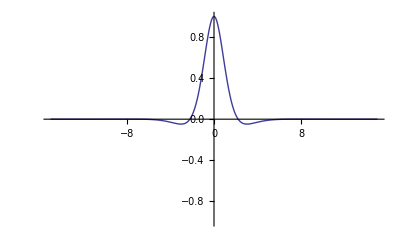

```mathematica
Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT},
ρ1=-0.5;κ1=0.2;V1=0.1;ρ2=-0.5;κ2=0.2;V2=0.1;ρ3=-0.5;κ3=0.2;V3=0.1;ρ4=-0.5;κ4=0.2;V4=0.1;ρ5=-0.5;κ5=0.2;V5=0.1;ρi=-0.5;κi=0.2;Vi=0.1;
α11=0.001;α12=0.001;α13=0.001;α14=0.001;αi1=0.001;αi2=-0.001;αi3=-0.001;αi4=0.001;τ=10;λ=0.1;LT=1;
Plot[Re[AlphaDigitaleMeasureS1U1FondamentalTransform[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,z,λ,LT,τ]],{z,-15,15},PlotRange->{-1,1}]]
```

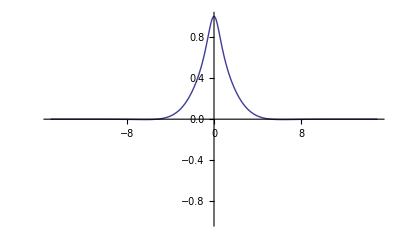

```mathematica
Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT},
ρ1=-0.5;κ1=0.2;V1=0.1;ρ2=-0.5;κ2=0.2;V2=0.1;ρ3=-0.5;κ3=0.2;V3=0.1;ρ4=-0.5;κ4=0.2;V4=0.1;ρ5=-0.5;κ5=0.2;V5=0.1;ρi=-0.5;κi=0.2;Vi=0.1;
α11=0.001;α12=0.001;α13=0.001;α14=0.001;αi1=0.001;αi2=-0.001;αi3=-0.001;αi4=0.001;τ=10;λ=0.1;LT=1;
Plot[Re[AlphaDigitaleMeasureS1UiFondamentalTransform[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,z,λ,LT,τ]],{z,-15,15},PlotRange->{-1,1}]]
```

```mathematica
LogNormalCallPayOffFourierTransform[K,ω]
```

K^(1+ⅈ ω)/(ω (-ⅈ+ω))

```mathematica
(K)^(1+ⅈ ω)/(ⅈ  ω-ω^2)
```

```mathematica
AlphaDigitaleMeasureS1U1CallIntegrand[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,
α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0]) AlphaDigitaleMeasureS1U1FondamentalTransform[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ω,λ,LT,T]LogNormalCallPayOffFourierTransform[K,ω]]
```

```mathematica
AlphaDigitaleMeasureS1UiCallIntegrand[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,
α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0]) AlphaDigitaleMeasureS1UiFondamentalTransform[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ω,λ,LT,T]LogNormalCallPayOffFourierTransform[K,ω]]
```

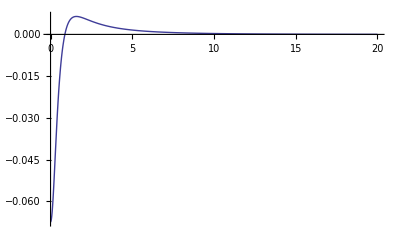
{0.61,-Graphics-}

```mathematica
Timing[Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.052,T=5,K,equivalentσ1,equivalentσi,equivalentρ,S1Mesure1,SiMesure1,S1Mesurei,SiMesurei,
alphaS1Mesure1,alphaSiMesure1,alphaS1Mesurei,alphaSiMesurei,vcommun=0.000001},
ρ1=-0.5;κ1=vcommun;V1=1;ρ2=-0.5;κ2=vcommun;V2=1;ρ3=-0.5;κ3=vcommun;V3=1;ρ4=-0.5;κ4=vcommun;V4=1;ρ5=-0.5;V5=0.0001;κ5=vcommun √V5;ρi=-0.5;Vi=0.0001;κi=vcommun √Vi;K=S1;
α11=0.01;α12=0.005;α13=0.01;α14=0.01;αi1=0.02;αi2=0.03;αi3=-0.01;αi4=0.01;λ=0.1;LT=1;
Plot[{AlphaDigitaleMeasureS1U1CallIntegrand[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,
α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1,K,T,ω +1.5 ⅈ]},{ω,0,20},PlotRange->All]
]]
```

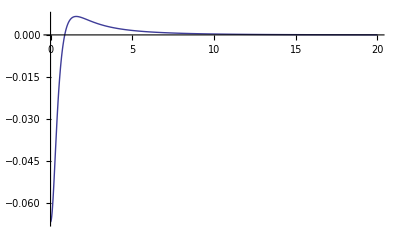
{0.563,-Graphics-}

```mathematica
Timing[Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.052,T=5,K,equivalentσ1,equivalentσi,equivalentρ,S1Mesure1,SiMesure1,S1Mesurei,SiMesurei,
alphaS1Mesure1,alphaSiMesure1,alphaS1Mesurei,alphaSiMesurei,vcommun=0.000001},
ρ1=-0.5;κ1=vcommun;V1=1;ρ2=-0.5;κ2=vcommun;V2=1;ρ3=-0.5;κ3=vcommun;V3=1;ρ4=-0.5;κ4=vcommun;V4=1;ρ5=-0.5;V5=0.0001;κ5=vcommun √V5;ρi=-0.5;Vi=0.0001;κi=vcommun √Vi;K=S1;
α11=0.01;α12=0.005;α13=0.01;α14=0.01;αi1=0.02;αi2=0.03;αi3=-0.01;αi4=0.01;λ=0.1;LT=1;
Plot[{AlphaDigitaleMeasureS1U1CallIntegrand[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,
α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1,K,T,ω -.5 ⅈ]},{ω,0,20},PlotRange->All]
]]
```

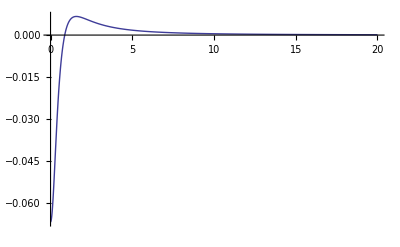
{0.562,-Graphics-}

```mathematica
Timing[Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.052,T=5,K,equivalentσ1,equivalentσi,equivalentρ,S1Mesure1,SiMesure1,S1Mesurei,SiMesurei,
alphaS1Mesure1,alphaSiMesure1,alphaS1Mesurei,alphaSiMesurei,vcommun=1},
ρ1=-0.5;κ1=vcommun;V1=1;ρ2=-0.5;κ2=vcommun;V2=1;ρ3=-0.5;κ3=vcommun;V3=1;ρ4=-0.5;κ4=vcommun;V4=1;ρ5=-0.5;V5=0.0001;κ5=vcommun √V5;ρi=-0.5;Vi=0.0001;κi=vcommun √Vi;K=S1;
α11=0.01;α12=0.005;α13=0.01;α14=0.01;αi1=0.02;αi2=0.03;αi3=-0.01;αi4=0.01;λ=0.1;LT=1;
Plot[{AlphaDigitaleMeasureS1UiCallIntegrand[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,
α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1,K,T,ω +1.5 ⅈ]},{ω,0,20},PlotRange->All]
]]
```

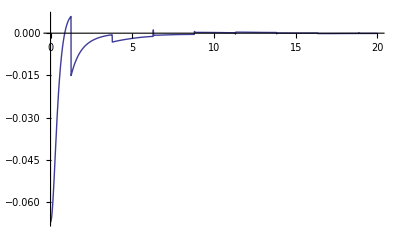
{1.484,-Graphics-}

```mathematica
Timing[Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.052,T=5,K,equivalentσ1,equivalentσi,equivalentρ,S1Mesure1,SiMesure1,S1Mesurei,SiMesurei,
alphaS1Mesure1,alphaSiMesure1,alphaS1Mesurei,alphaSiMesurei,vcommun=1},
ρ1=-0.5;κ1=vcommun;V1=1;ρ2=-0.5;κ2=vcommun;V2=1;ρ3=-0.5;κ3=vcommun;V3=1;ρ4=-0.5;κ4=vcommun;V4=1;ρ5=-0.5;V5=0.0001;κ5=vcommun √V5;ρi=-0.5;Vi=0.0001;κi=vcommun √Vi;K=S1;
α11=0.01;α12=0.005;α13=0.01;α14=0.01;αi1=0.02;αi2=0.03;αi3=-0.01;αi4=0.01;λ=0.1;LT=1;
Plot[{AlphaDigitaleMeasureS1UiCallIntegrand[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,
α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1,K,T,ω -0.5 ⅈ]},{ω,0,20},PlotRange->All]
]]
```

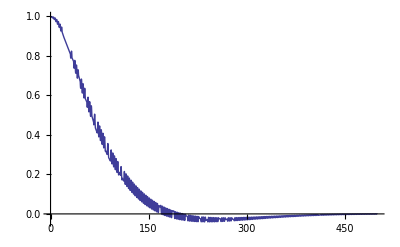
{3.422,-Graphics-}

```mathematica
Timing[Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.052,T=5,K,equivalentσ1,equivalentσi,equivalentρ,S1Mesure1,SiMesure1,S1Mesurei,SiMesurei,
alphaS1Mesure1,alphaSiMesure1,alphaS1Mesurei,alphaSiMesurei,vcommun=1},
ρ1=-0.5;κ1=vcommun;V1=1;ρ2=-0.5;κ2=vcommun;V2=1;ρ3=-0.5;κ3=vcommun;V3=1;ρ4=-0.5;κ4=vcommun;V4=1;ρ5=-0.5;V5=0.0001;κ5=vcommun √V5;ρi=-0.5;Vi=0.0001;κi=vcommun √Vi;K=S1;
α11=0.01;α12=0.005;α13=0.01;α14=0.01;αi1=0.02;αi2=0.03;αi3=-0.01;αi4=0.01;λ=0.1;LT=1;
Plot[{Re[AlphaDigitaleMeasureS1UiFondamentalTransform[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,
α11,α12,α13,α14,αi1,αi2,αi3,αi4,ω -0.005 ⅈ,λ,LT,T]]},{ω,0,500},PlotRange->All]
]]
```

```mathematica
Timing[Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.052,T=5,K,equivalentσ1,equivalentσi,equivalentρ,S1Mesure1,SiMesure1,S1Mesurei,SiMesurei,
alphaS1Mesure1,alphaSiMesure1,alphaS1Mesurei,alphaSiMesurei,vcommun=1},
ρ1=-0.5;κ1=vcommun;V1=1;ρ2=-0.5;κ2=vcommun;V2=1;ρ3=-0.5;κ3=vcommun;V3=1;ρ4=-0.5;κ4=vcommun;V4=1;ρ5=-0.5;V5=0.0001;κ5=vcommun √V5;ρi=-0.5;Vi=0.0001;κi=vcommun √Vi;K=S1;
α11=0.01;α12=0.005;α13=0.01;α14=0.01;αi1=0.02;αi2=0.03;αi3=-0.01;αi4=0.01;λ=0.1;LT=1;
Plot[{Re[AlphaDigitaleMeasureS1UiFondamentalTransform[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,
α11,α12,α13,α14,αi1,αi2,αi3,αi4,ω -0.5 ⅈ,λ,LT,T]]},{ω,0,20},PlotRange->All]
]]
```

```mathematica
AlphaDigitaleMeasureS1U1CallN[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=
-1/π Re[Module[{λs=1.25,ω},
NIntegrate[AlphaDigitaleMeasureS1U1CallIntegrand[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T,ω +λs ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
AlphaDigitaleMeasureS1UiCallN[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=
-1/π Re[Module[{λs=1.25,ω},
NIntegrate[AlphaDigitaleMeasureS1UiCallIntegrand[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T,ω +λs ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
AlphaDigitaleMeasureS1U1PutN[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=
-1/π Re[Module[{λs=-0.025,ω},
NIntegrate[AlphaDigitaleMeasureS1U1CallIntegrand[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T,ω +λs ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
AlphaDigitaleMeasureS1UiPutN[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=
-1/π Re[Module[{λs=-0.025,ω},
NIntegrate[AlphaDigitaleMeasureS1UiCallIntegrand[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T,ω +λs ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
La fonction suivante calcule le forward dans ce nouveau numeraire, il est evidement different de Subscript[S, 0] car nous ne sommes plus dans la mesure de martingale !
```

```mathematica
AlphaDigitaleMeasureS1ForwardU1N[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=AlphaDigitaleMeasureS1U1CallN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T]-AlphaDigitaleMeasureS1U1PutN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T]+K
```

```mathematica
AlphaDigitaleMeasureS1ForwardUiN[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=AlphaDigitaleMeasureS1UiCallN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T]-AlphaDigitaleMeasureS1UiPutN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T]+K
```

```mathematica
Timing[Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0=0.05,T=10,K=0.04,ω},
ρ1=-0.5;κ1=0.2;V1=1;ρ2=-0.5;κ2=0.2;V2=1;ρ3=-0.5;κ3=0.2;V3=1;ρ4=-0.5;κ4=0.2;V4=1;ρ5=-0.5;κ5=0.2;V5=0.001;ρi=-0.5;κi=0.2;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
{AlphaDigitaleMeasureS1U1CallN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T],
AlphaDigitaleMeasureS1U1PutN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T],
AlphaDigitaleMeasureS1ForwardU1N[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T]}]]
```

{0.656,{0.0108087,0.000153344,0.0506554}}

```mathematica
AlphaDigitaleMeasureS1U1CallAux[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=
-1/π Re[Module[{λs=1.5,ω},
AdaptativeIntegrate[Function[ω,AlphaDigitaleMeasureS1U1CallIntegrand[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T,ω +λs ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
AlphaDigitaleMeasureS1U1PutAux[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=
-1/π Re[Module[{λs=-0.5,ω},
AdaptativeIntegrate[Function[ω,AlphaDigitaleMeasureS1U1CallIntegrand[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T,ω +λs ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
AlphaMeasureS1ForwardU1Aux[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=AlphaDigitaleMeasureS1U1CallAux[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T]-AlphaDigitaleMeasureS1U1PutAux[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T]+K
```

```mathematica
Timing[Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0=0.05,T=10,K=0.04,ω},
ρ1=-0.5;κ1=0.2;V1=1;ρ2=-0.5;κ2=0.2;V2=1;ρ3=-0.5;κ3=0.2;V3=1;ρ4=-0.5;κ4=0.2;V4=1;ρ5=-0.5;κ5=0.2;V5=0.001;ρi=-0.5;κi=0.2;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
{AlphaDigitaleMeasureS1U1CallAux[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T],
AlphaDigitaleMeasureS1U1PutAux[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T],
AlphaMeasureS1ForwardU1Aux[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T]}]]
```

{4.547,{0.0108088,0.000153372,0.0506555}}

```mathematica
Timing[Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.051,T=10,K=0.04,equivalentσ1,equivalentσi,equivalentρ,S1Mesure1,SiMesure1,vcommun=0.0001},
ρ1=-0.5;κ1=vcommun;V1=1;ρ2=-0.5;κ2=vcommun;V2=1;ρ3=-0.5;κ3=vcommun;V3=1;ρ4=-0.5;κ4=vcommun;V4=1;ρ5=-0.5;V5=0.001;κ5=vcommun √V5;ρi=-0.5;Vi=0.001;κi=vcommun √Vi;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
S1Mesure1=S1 Exp[equivalentσ1^2 T];SiMesure1=Si Exp[equivalentρ equivalentσ1 equivalentσi T];
{{AlphaDigitaleMeasureS1ForwardU1N[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1,K,T],
AlphaDigitaleMeasureS1ForwardUiN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,Si,K,T]},
{S1Mesure1,SiMesure1}}]]
```

{0.094,{{0.0507049,0.051},{0.0507049,0.051}}}

```mathematica
Donc Le forward semble tres sympathique par rapport a ce qu'il doit etre  .
Au approximation pres nous admetrons donc que le changement de measure lognormal s'applique
```

### Dans la measure S_i

```mathematica
Nous appliquons la symetrie Subscript[S, 1]  < - > Subscript[S, i]
```

```mathematica
AlphaDigitaleMeasureSiForwardU1N[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S1_,K_,T_]:=AlphaDigitaleMeasureS1ForwardUiN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρi,κi,Vi,ρ5,κ5,V5,αi1,αi2,αi3,αi4,α11,α12,α13,α14,λ,LT,S1,K,T]
```

```mathematica
AlphaDigitaleMeasureSiForwardUiN[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,Si_,K_,T_]:=AlphaDigitaleMeasureS1ForwardU1N[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρi,κi,Vi,ρ5,κ5,V5,αi1,αi2,αi3,αi4,α11,α12,α13,α14,λ,LT,Si,K,T]
```

### exemples de forward dans les measure S_1 et S_i

```mathematica
Timing[Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.052,T=5,K,equivalentσ1,equivalentσi,equivalentρ,S1Mesure1,SiMesure1,S1Mesurei,SiMesurei,
alphaS1Mesure1,alphaSiMesure1,alphaS1Mesurei,alphaSiMesurei,vcommun=0.000001},
ρ1=-0.5;κ1=vcommun;V1=1;ρ2=-0.5;κ2=vcommun;V2=1;ρ3=-0.5;κ3=vcommun;V3=1;ρ4=-0.5;κ4=vcommun;V4=1;ρ5=-0.5;V5=0.0001;κ5=vcommun √V5;ρi=-0.5;Vi=0.0001;κi=vcommun √Vi;K=S1;
α11=0.01;α12=0.005;α13=0.01;α14=0.01;αi1=0.02;αi2=0.03;αi3=-0.01;αi4=0.01;λ=0.1;LT=1;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
S1Mesure1=S1 Exp[equivalentσ1^2 T];SiMesure1=Si Exp[equivalentρ equivalentσ1 equivalentσi T];
alphaS1Mesure1=AlphaDigitaleMeasureS1ForwardU1N[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1,K,T];
alphaSiMesure1=AlphaDigitaleMeasureS1ForwardUiN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,Si,K,T];
S1Mesurei=S1 Exp[equivalentρ equivalentσ1 equivalentσi T];SiMesurei=Si Exp[ equivalentσi^2 T];
alphaS1Mesurei=AlphaDigitaleMeasureS1ForwardU1N[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1,K,T];
alphaSiMesurei=AlphaDigitaleMeasureS1ForwardUiN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,Si,K,T];
Print[{equivalentσ1,equivalentρ  equivalentσi}];
Print["equivalentσ1=",equivalentσ1," equivalentσi=",equivalentσi,"  equivalentρ=",equivalentρ];
Print["alpha: S1Mesure1=",alphaS1Mesure1," LN : S1Mesure1=",S1Mesure1];
Print["alpha: SiMesure1=",alphaSiMesure1," LN : SiMesure1=",SiMesure1];
Print["alpha: S1Mesurei=",alphaS1Mesurei," LN : S1Mesurei=",S1Mesurei];
Print["alpha: SiMesurei=",alphaSiMesurei," LN : SiMesurei=",SiMesurei];
]]
```

{0.0206155,0.0169775}

equivalentσ1=0.0206155 equivalentσi=0.04  equivalentρ=0.424437

alpha: S1Mesure1=0.0501064 LN : S1Mesure1=0.0501064

alpha: SiMesure1=0.0520909 LN : SiMesure1=0.0520911

alpha: S1Mesurei=0.0501064 LN : S1Mesurei=0.0500876

alpha: SiMesurei=0.0520909 LN : SiMesurei=0.0524177

{12.438,Null}

```mathematica
Timing[Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.052,T=5,K,equivalentσ1,equivalentσi,equivalentρ,S1Mesure1,SiMesure1,S1Mesurei,SiMesurei,
alphaS1Mesure1,alphaSiMesure1,alphaS1Mesurei,alphaSiMesurei,vcommun=2},
ρ1=-0.5;κ1=vcommun;V1=1;ρ2=-0.5;κ2=vcommun;V2=1;ρ3=-0.5;κ3=vcommun;V3=1;ρ4=-0.5;κ4=vcommun;V4=1;ρ5=-0.5;V5=0.00001;κ5=vcommun √V5;ρi=-0.5;Vi=0.00001;κi=vcommun √Vi;K=S1;
α11=0.01;α12=0.005;α13=0.01;α14=0.01;
αi1=0.01;αi2=0.005;αi3=0.01;αi4=0.01;λ=0.1;LT=1;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
S1Mesure1=S1 Exp[equivalentσ1^2 T];SiMesure1=Si Exp[equivalentρ equivalentσ1 equivalentσi T];
alphaS1Mesure1=AlphaDigitaleMeasureS1ForwardU1N[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1,K,T];
alphaSiMesure1=AlphaDigitaleMeasureS1ForwardUiN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,Si,K,T];
S1Mesurei=S1 Exp[equivalentρ equivalentσ1 equivalentσi T];SiMesurei=Si Exp[ equivalentσi^2 T];
alphaS1Mesurei=AlphaDigitaleMeasureS1ForwardU1N[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1,K,T];
alphaSiMesurei=AlphaDigitaleMeasureS1ForwardUiN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,Si,K,T];
Print[{equivalentσ1,equivalentρ  equivalentσi}];
Print["equivalentσ1=",equivalentσ1," equivalentσi=",equivalentσi,"  equivalentρ=",equivalentρ];
Print["alpha: S1Mesure1=",alphaS1Mesure1," LN : S1Mesure1=",S1Mesure1];
Print["alpha: SiMesure1=",alphaSiMesure1," LN : SiMesure1=",SiMesure1];
Print["alpha: S1Mesurei=",alphaS1Mesurei," LN : S1Mesurei=",S1Mesurei];
Print["alpha: SiMesurei=",alphaSiMesurei," LN : SiMesurei=",SiMesurei];
]]
```

{0.018303,0.0177566}

equivalentσ1=0.018303 equivalentσi=0.018303  equivalentρ=0.970149

alpha: S1Mesure1=0.0500233 LN : S1Mesure1=0.0500838

alpha: SiMesure1=0.0520216 LN : SiMesure1=0.0520846

alpha: S1Mesurei=0.0500233 LN : S1Mesurei=0.0500813

alpha: SiMesurei=0.0520216 LN : SiMesurei=0.0520872

{11.156,Null}

```mathematica
ceci tendrait a prouver que l'approximation lognormale est suffisante
```

## Implementation d'une pure digitale de spreadoption

```mathematica
IntercalePrice[K1List_,K2List_]:=Module[{nb1=Length[K1List],nb2=Length[K2List],tab,j=1,itab=1,j1=1,j2=1},
tab=Table[0,{i,1,nb1+nb2}];
While[((j1≤nb1)||(j2≤nb2))&&j<=nb1+nb2,
If[itab==1,tab[[j]]=K1List[[j1]]];If[itab==2,tab[[j]]=K2List[[j2]]];
If[itab==1,j1=j1+1;If[j2<=nb2,itab=2],
j2=j2+1;If[j1<=nb1,itab=1]];
j++
];
tab]
```

```mathematica
IntercalePrice[KList1_,KList2_,KList3_]:=Module[{m=Length[KList1],list=Table[0,{i,1,3 Length[KList1]}]},
Do[list[[1+3i]]=KList1[[i+1]];list[[2+3i]]=KList2[[i+1]];list[[3+3i]]=KList3[[i+1]];,{i,0,m-1}];
list]
```

```mathematica
IntercalePrice[{1-0.1,2-0.1,3-0.1},{1,2,3},{1+0.1,2+0.1,3+0.1}]
```

{0.9,1,1.1,1.9,2,2.1,2.9,3,3.1}

```mathematica
IntercalePrice[{a1,a2,a3,a4,a5},{b1,b2,b3,b4,b5}]
```

{a1,b1,a2,b2,a3,b3,a4,b4,a5,b5}

```mathematica
SmileAlphaDigitale[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_,T_,LimitGindinkin_,printflag_,bilogHestonFlag_]:=SmileAlphaDigitalelist[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,{K},T,LimitGindinkin,printflag,bilogHestonFlag][[1]]
```

```mathematica
SmileAlphaDigitale[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_List,T_,LimitGindinkin_,printflag_,bilogHestonFlag_]:=SmileAlphaDigitalelist[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,K,T,LimitGindinkin,printflag,bilogHestonFlag]
```

```mathematica
SmileAlphaDigitalelist[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_List,T_,LimitGindinkin_,printflag_,bilogHestonFlag_]:=Module[{ρprojeté,νprojeté,prices,VarVSIncrementale,CoVarSVSIncrementale,VS,Sig1,Sig2,Correl12,numinimum,rhominimum,VarVSTotal,λsmooth,Vmultiplicator,CoVarSVSTotal,digitaleprices,forward,shiftL,CompoundK,V0projeté,V0minimim,nbsteps=10,scale=8,microratio=20},

Sig1=√(α11^2 V1+α12^2 V2+α13^2 V3+α14^2 V4+V5);Sig2=√(αi1^2 V1+αi2^2 V2+αi3^2 V3+αi4^2 V4+Vi);Correl12= (α11 αi1  V1+α12 αi2  V2+α13 αi3  V3+α14 αi4  V4)/(Sig1 Sig2);
Vmultiplicator=Exp[0.026958633519421456 T-0.017202498337524928];λsmooth=20;
Switch[bilogHestonFlag,
0,
{V0minimim,rhominimum,numinimum}=HestonFromBilog[S1,Si,Sig1,Sig2,Correl12,T,λ,LT],
1,
{V0minimim,rhominimum,numinimum}=HestonFromBilogV0Fixed[S1,Si,Sig1,Sig2,Correl12,T,λ,LT,Vmultiplicator],
2,
{V0minimim,rhominimum,numinimum}=HestonFromBilogPackaged[S1,Si,Sig1,Sig2,Correl12,T,λ,LT,λsmooth]];
If[printflag==1 || MemberQ[printflag,1] ,Print["V0minimim=",V0minimim," rhominimum= ",rhominimum," Numinimum=",numinimum]];
If[printflag==1 || MemberQ[printflag,1] ,Print["VSminimale=",V0minimim," VarVSminimale=",numinimum^2 V0minimim," CoVarSVSminimale=",rhominimum V0minimim numinimum]];
{VS,VarVSIncrementale,CoVarSVSIncrementale}=AlphaDigitaleObservable1iz[S1,Si,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi];
If[printflag==1 || MemberQ[printflag,1] ,Print["VSBlack=",VS," VarVSIncrementale=",VarVSIncrementale," CoVarSVSIncrementale=",CoVarSVSIncrementale]];
VarVSTotal=VarVSIncrementale+numinimum^2 V0minimim;
CoVarSVSTotal=CoVarSVSIncrementale+rhominimum V0minimim numinimum;
If[printflag==1 || MemberQ[printflag,1] ,Print["VSTotal=",V0minimim," VarVSTotal=",VarVSTotal," CoVarSVSTotal= ",CoVarSVSTotal]];
ρprojeté=CoVarSVSTotal/(√(V0minimim VarVSTotal));νprojeté=√(VarVSTotal/V0minimim);V0projeté=V0minimim;
forward=S1-Si;
If[printflag==1 || MemberQ[printflag,1] ,Print["Normal Heston Parameters=",{{"S0",forward},{"V0",V0projeté},{"ρ",ρprojeté},{"ν",νprojeté},
{"standard dev equi.",√VS},{"ν normalized",νprojeté/(√VS)}} //MatrixForm]];
shiftL=0.0001;
CompoundK=IntercalePrice[K-shiftL,K+shiftL];
prices=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,V0projeté,S1-Si,CompoundK,T,nbsteps,scale,microratio,0][[1]];
If[printflag==1 || MemberQ[printflag,1] ,Print["spreadoption prices=",prices]];
digitaleprices=Table[(prices[[2i-1]]-prices[[2i]])/(2shiftL),{i,1,Length[K]}];
If[printflag==1 || MemberQ[printflag,1] ,Print["digitale prices=",digitaleprices]];
digitaleprices
]
```

## Exemple de pure digitale de spreadoption

Stdev(pour le calcul des strike)=0.00845068

strikes={-0.00281689,-0.00140845,0,0.00140845,0.00281689}

pricegoaltable={0.00435516,0.00357581,0.00289073,0.00229942,0.00179869}

optimisation results:{1.29475×10^-8,{0.0000311067,-0.187789,0.0164364}}

V0minimim=0.0000311067 rhominimum= -0.187789 Numinimum=0.0164364

VSminimale=0.0000311067 VarVSminimale=8.40363×10^-9 CoVarSVSminimale=-9.60132×10^-8

VSBlack=7.1414×10^-6 VarVSIncrementale=-2.19083×10^-25 CoVarSVSIncrementale=-1.20269×10^-21

VSTotal=0.0000311067 VarVSTotal=8.40363×10^-9 CoVarSVSTotal= -9.60132×10^-8

Normal Heston Parameters=(S0 | -0.001
V0 | 0.0000311067
ρ | -0.187789
ν | 0.0164364
standard dev equi. | 0.00267234
ν normalized | 6.15057)

spreadoption prices={0.0193391,0.019155,0.0147724,0.0145917,0.010328,0.0101545,0.0081959,0.00802941,0.00617899,0.00602507,0.00542399,0.00527777,0.00437623,0.0042463,0.00297219,0.00288261,0.00208242,0.00202987,0.00173642,0.00169761,0.00155602,0.00152371,0.00122011,0.00119845,0.000987441,0.000971889,0.00068672,0.000677641,0.000502251,0.000496382}

digitale prices={0.920373,0.903746,0.867553,0.832463,0.769602,0.731075,0.649693,0.447906,0.262744,0.194095,0.161551,0.108312,0.0777601,0.0453939,0.029344}

Stdev(pour le calcul des strike)=0.00845068

strikes={-0.00281689,-0.00140845,0,0.00140845,0.00281689}

pricegoaltable={0.00435516,0.00357581,0.00289073,0.00229942,0.00179869}

optimisation results:{1.29475×10^-8,{0.0000311067,-0.187789,0.0164364}}

V0minimim=0.0000311067 rhominimum= -0.187789 Numinimum=0.0164364

VSminimale=0.0000311067 VarVSminimale=8.40363×10^-9 CoVarSVSminimale=-9.60132×10^-8

VSBlack=7.1414×10^-6 VarVSIncrementale=7.33379×10^-11 CoVarSVSIncrementale=-9.02017×10^-9

VSTotal=0.0000311067 VarVSTotal=8.47697×10^-9 CoVarSVSTotal= -1.05033×10^-7

Normal Heston Parameters=(S0 | -0.001
V0 | 0.0000311067
ρ | -0.204541
ν | 0.016508
standard dev equi. | 0.00267234
ν normalized | 6.17735)

spreadoption prices={0.0196521,0.0194665,0.0150482,0.014866,0.0105692,0.0103943,0.00841987,0.00825197,0.00638468,0.00622922,0.00562176,0.00547389,0.00456102,0.00442925,0.00313345,0.00304207,0.00222478,0.00217106,0.00187093,0.00183119,0.00168615,0.00165302,0.00134103,0.0013187,0.00110048,0.00108434,0.000786018,0.00077643,0.000589578,0.000583262}

digitale prices={0.928191,0.910861,0.874379,0.839485,0.777344,0.739316,0.658887,0.456856,0.268599,0.198681,0.16563,0.111637,0.0807358,0.0479405,0.0315776}

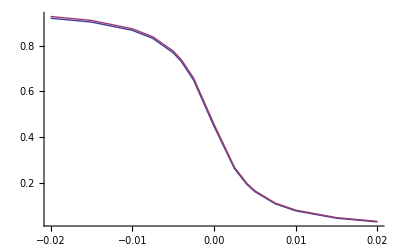
{17.828,-Graphics-}

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,S1=0.05,Si=0.051,
T=10,λ=0.1,LT=1,
KList={-0.02,-0.015,-0.01,-0.0075,-0.005,-0.004,-0.0025,0,0.0025,0.004,0.005,0.0075,0.01,0.015,0.02},LimitGindinkin=5,printflag=1,prices,νcommun,νcommun1,bilogprices,bilogtohestonflag=0},
V1=1;V2=1;V3=1;V4=1;V5=0.001;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;
αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;
νcommun=0.0000000000004;
ρ1=-0.5;ν1=νcommun;ρ2=-0.5;ν2=νcommun;ρ3=-0.5;ν3=νcommun;ρ4=-0.5;ν4=νcommun;ρ5=-0.5;ν5=νcommun √V5;ρi=-0.5;νi=νcommun √Vi;
bilogprices=SmileAlphaDigitale[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,bilogtohestonflag];
νcommun1=3;
ρ1=-0.5;ν1=νcommun1;ρ2=-0.5;ν2=νcommun1;ρ3=-0.5;ν3=νcommun1;ρ4=-0.5;ν4=νcommun1;ρ5=-0.5;ν5=νcommun1 √V5;ρi=-0.5;νi=νcommun1 √Vi;
prices=SmileAlphaDigitale[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,bilogtohestonflag];
ListPlot[{Transpose[{KList,bilogprices}],Transpose[{KList,prices}]},Joined->True]
]]]
```

InitialV0=7.1414×10^-6 νup=0.00534468 Stdev(pour le calcul des strike)=0.00845068

strikes={-0.00281689,-0.00140845,0,0.00140845,0.00281689}

pricegoaltable={0.00435516,0.00357581,0.00289073,0.00229942,0.00179869}

optimisation results:{3.06803×10^-18,{2.90908×10^-7,-0.0144053,0.000330027}}

V0minimim=6.81311×10^-6 rhominimum= -0.0144053 Numinimum=0.000340948

VSminimale=6.81311×10^-6 VarVSminimale=7.91994×10^-13 CoVarSVSminimale=-3.34623×10^-11

VSBlack=7.1414×10^-6 VarVSIncrementale=-2.19083×10^-25 CoVarSVSIncrementale=-1.20269×10^-21

VSTotal=6.81311×10^-6 VarVSTotal=7.91994×10^-13 CoVarSVSTotal= -3.34623×10^-11

Normal Heston Parameters=(S0 | -0.001
V0 | 6.81311×10^-6
ρ | -0.0144053
ν | 0.000340948
standard dev equi. | 0.00267234
ν normalized | 0.127584)

spreadoption prices={0.0191,0.0189002,0.0142757,0.0140849,0.00967735,0.00950401,0.00759584,0.00743815,0.00573521,0.00559743,0.00506402,0.00493519,0.00414324,0.00402853,0.00284929,0.00275895,0.00185692,0.00179003,0.00139749,0.00134337,0.0011427,0.00109635,0.000662335,0.000632401,0.000361504,0.00034355,0.0000935969,0.0000885749,0.0000285736,0.0000276085}

digitale prices={0.999005,0.954079,0.866701,0.788463,0.688879,0.644184,0.573535,0.451706,0.334474,0.270595,0.231739,0.149671,0.0897702,0.02511,0.00482552}

InitialV0=7.1414×10^-6 νup=0.00534468 Stdev(pour le calcul des strike)=0.00845068

strikes={-0.00281689,-0.00140845,0,0.00140845,0.00281689}

pricegoaltable={0.00435516,0.00357581,0.00289073,0.00229942,0.00179869}

optimisation results:{3.06803×10^-18,{2.90908×10^-7,-0.0144053,0.000330027}}

V0minimim=6.81311×10^-6 rhominimum= -0.0144053 Numinimum=0.000340948

VSminimale=6.81311×10^-6 VarVSminimale=7.91994×10^-13 CoVarSVSminimale=-3.34623×10^-11

VSBlack=7.1414×10^-6 VarVSIncrementale=7.33379×10^-11 CoVarSVSIncrementale=-9.02017×10^-9

VSTotal=6.81311×10^-6 VarVSTotal=7.41299×10^-11 CoVarSVSTotal= -9.05363×10^-9

Normal Heston Parameters=(S0 | -0.001
V0 | 6.81311×10^-6
ρ | -0.402859
ν | 0.00329856
standard dev equi. | 0.00267234
ν normalized | 1.23433)

spreadoption prices={0.0195393,0.0193154,0.0145747,0.0143905,0.00993147,0.00974933,0.00769413,0.00751942,0.00557408,0.00541171,0.00477621,0.0046212,0.00365946,0.00351965,0.00212352,0.00202387,0.00115131,0.0010971,0.000809161,0.0007733,0.000647661,0.000620185,0.000386054,0.000371151,0.000239913,0.000231265,0.000101448,0.0000980097,0.0000276787,0.0000272946}

digitale prices={1.11956,0.920952,0.910679,0.873555,0.811859,0.775061,0.699049,0.49826,0.27103,0.179305,0.137379,0.0745118,0.0432381,0.017192,0.00192074}

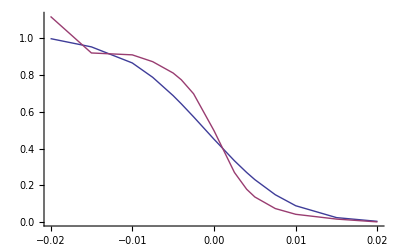
{79.703,-Graphics-}

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,S1=0.05,Si=0.051,
T=10,λ=0.1,LT=1,
KList={-0.02,-0.015,-0.01,-0.0075,-0.005,-0.004,-0.0025,0,0.0025,0.004,0.005,0.0075,0.01,0.015,0.02},LimitGindinkin=5,printflag=1,prices,νcommun,νcommun1,bilogprices,bilogtohestonflag=2},
V1=1;V2=1;V3=1;V4=1;V5=0.001;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;
αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;
νcommun=0.0000000000004;
ρ1=-0.5;ν1=νcommun;ρ2=-0.5;ν2=νcommun;ρ3=-0.5;ν3=νcommun;ρ4=-0.5;ν4=νcommun;ρ5=-0.5;ν5=νcommun √V5;ρi=-0.5;νi=νcommun √Vi;
bilogprices=SmileAlphaDigitale[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,bilogtohestonflag];
νcommun1=3;
ρ1=-0.5;ν1=νcommun1;ρ2=-0.5;ν2=νcommun1;ρ3=-0.5;ν3=νcommun1;ρ4=-0.5;ν4=νcommun1;ρ5=-0.5;ν5=νcommun1 √V5;ρi=-0.5;νi=νcommun1 √Vi;
prices=SmileAlphaDigitale[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,bilogtohestonflag];
ListPlot[{Transpose[{KList,bilogprices}],Transpose[{KList,prices}]},Joined->True]
]]]
```

## Implementation des digitale de spreadoption Paying S1 et Si

On pourrait se servir de

E[S2 1_(S1-S2>K)]=S2-E[S2 1_(S1-S2<K)]=S2-E[S2 1_(S2-S1>-K)]

on prefere definir directement

```mathematica
SmileAlphaDigitaleU1[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_,T_,LimitGindinkin_,printflag_,bilogtohestonflag_]:=
Module[{equivalentσ1,equivalentσi,equivalentρ},
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
Print["equivalentσ1",equivalentσ1," equivalentσi",equivalentσi," equivalentρ",equivalentρ];
SmileAlphaDigitale[S1  Exp[equivalentσ1^2 T],Si Exp[equivalentρ equivalentσ1 equivalentσi T], ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,K,T,LimitGindinkin,printflag,bilogtohestonflag]
]
```

```mathematica
SmileAlphaDigitaleUi[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_,T_,LimitGindinkin_,printflag_,bilogtohestonflag_]:=
Module[{equivalentσ1,equivalentσi,equivalentρ},
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
Print["equivalentσ1",equivalentσ1," equivalentσi",equivalentσi," equivalentρ",equivalentρ];
SmileAlphaDigitale[S1   Exp[equivalentρ equivalentσ1 equivalentσi T],Si Exp[equivalentσi^2 T], ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,K,T,LimitGindinkin,printflag,bilogtohestonflag]
]
```

## Exemple de digitale Paying S1 et Si

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.051,T=10,K=0.04,LimitGindinkin=2,printflag=1},
ρ1=-0.5;ν1=0.2;V1=1;ρ2=-0.5;ν2=0.2;V2=1;ρ3=-0.5;ν3=0.2;V3=1;ρ4=-0.5;ν4=0.2;V4=1;ρ5=-0.5;ν5=0.2;V5=0.001;ρi=-0.5;νi=0.2;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
SmileAlphaDigitaleU1[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,K,T,LimitGindinkin,printflag]]]]
```

equivalentσ10.0374166 equivalentσi0.0374166 equivalentρ0.

strikes={-0.00321793,-0.00160896,0,0.00160896,0.00321793}

optimisation results:{3.57672×10^-9,{9.31954×10^-6,-0.0240514,0.0028149}}

V0minimim=9.31954×10^-6 rhominimum= -0.0240514 Numinimum=0.0028149

VSminimale=9.31954×10^-6 VarVSminimale=7.38451×10^-11 CoVarSVSminimale=-6.30956×10^-10

VSBlack=7.24078×10^-6 VarVSIncrementale=2.60784×10^-10 CoVarSVSIncrementale=1.32466×10^-8

VSTotal=9.31954×10^-6 VarVSTotal=3.34629×10^-10 CoVarSVSTotal= 1.26156×10^-8

Normal Heston Parameters=(S0 | -0.000295077
V0 | 9.31954×10^-6
ρ | 0.225907
ν | 0.00599217
standard dev equi. | 0.00269087
ν normalized | 2.22685)

spreadoption prices={0.0000678181,0.0000494759}

digitale prices={0.0114639}

{7.016,0.0114639}

#### Paying Si

```mathematica
On se sert de
```

```mathematica
E[S2 Subscript[1, S1-S2>K]]=S2-E[S2 Subscript[1, S1-S2<K]]=S2-E[S2 Subscript[1, S2-S1>-K]]
```

#### Consistence

```mathematica
(* consistence bilog *)
```

```mathematica
Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.055,T=10,equivalentσ1,equivalentσi,equivalentρ,bilogdigitale,
bilogSpreadoptionGRAPH,alphaSpreadoptionGRAPH,paysS1GRAPH,paysSiGRAPH,paysKGRAPH,paysdigitaleGRAPH,priceSpreadoption,BilogToHestonFlag,
KList={-0.02,-0.015,-0.0125,-0.01,-0.0075,-0.005,-0.004,-0.0025,-0.001,0,0.001,0.0025,0.004,0.005,0.0075,0.01,0.0125,0.015,0.02},LimitGindinkin=10,printflag=0,prices1,pricesi,priced,priceK,commonν=0.01,bilogprices1,bilogpricesi,bilogpriceK,νcommun},τ=10;λ=0.1;LT=1;
V1=1;V2=1;V3=1;V4=1;V5=0.00001;Vi=0.00001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;
αi1=0.01;αi2=0.01;αi3=0.01;αi4=0.01;
νcommun=0.001;BilogToHestonFlag=2;
ρ1=-0.5;ν1=νcommun;ρ2=-0.5;ν2=νcommun;ρ3=-0.5;ν3=νcommun;ρ4=-0.5;ν4=νcommun;ρ5=-0.5;ν5=νcommun √V5;ρi=-0.5;νi=νcommun √Vi;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T]]
```

{0.0202485,0.0202485,0.97561}

equivalentσ10.0202485 equivalentσi0.0202485 equivalentρ0.

InitialV0=2.27369×10^-6 νup=0.00301575 Stdev(pour le calcul des strike)=0.00476832

strikes={-0.00158944,-0.00079472,0,0.00079472,0.00158944}

pricegoaltable={0.000711248,0.000532342,0.000390752,0.000281147,0.000198195}

optimisation results:{1.93221×10^-18,{-3.45381×10^-9,-0.0665009,0.0000331728}}

equivalentσ10.0202485 equivalentσi0.0202485 equivalentρ0.

InitialV0=2.27546×10^-6 νup=0.00301693 Stdev(pour le calcul des strike)=0.00477018

strikes={-0.00159006,-0.00079503,0,0.00079503,0.00159006}

pricegoaltable={0.000609583,0.000451408,0.00032772,0.000233145,0.000162463}

optimisation results:{1.0504×10^-18,{-2.64095×10^-9,-0.0725576,0.0000338319}}

InitialV0=2.26525×10^-6 νup=0.00301015 Stdev(pour le calcul des strike)=0.00475946

strikes={-0.00158649,-0.000793244,0,0.000793244,0.00158649}

pricegoaltable={0.000657566,0.000489558,0.000357384,0.000255695,0.000179216}

optimisation results:{1.47381×10^-18,{-2.99819×10^-9,-0.0695403,0.0000334788}}

S1,Si,Sig1,Sig2,Correl12,T={0.05,0.055,0.0202485,0.0202485,0.,10}

InitialV0=2.26525×10^-6 νup=0.00301015 Stdev(pour le calcul des strike)=0.00475946

strikes={-0.00158649,-0.000793244,0,0.000793244,0.00158649}

pricegoaltable={0.000657566,0.000489558,0.000357384,0.000255695,0.000179216}

optimisation results:{1.47381×10^-18,{-2.99819×10^-9,-0.0695403,0.0000334788}}

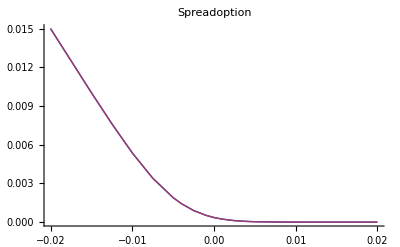
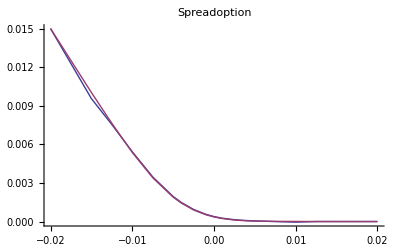
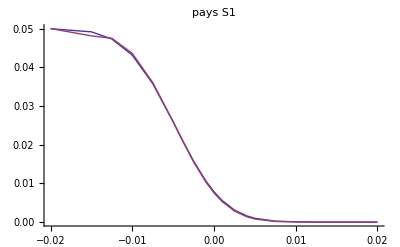
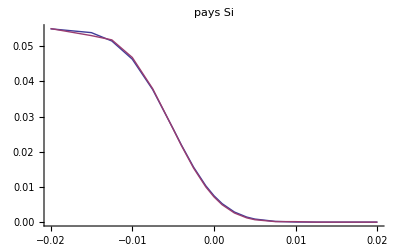
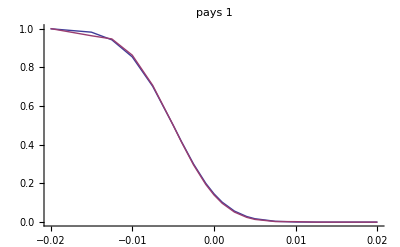
{183.89,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.055,T=10,equivalentσ1,equivalentσi,equivalentρ,bilogdigitale,
bilogSpreadoptionGRAPH,alphaSpreadoptionGRAPH,paysS1GRAPH,paysSiGRAPH,paysKGRAPH,paysdigitaleGRAPH,priceSpreadoption,BilogToHestonFlag,
KList={-0.02,-0.015,-0.0125,-0.01,-0.0075,-0.005,-0.004,-0.0025,-0.001,0,0.001,0.0025,0.004,0.005,0.0075,0.01,0.0125,0.015,0.02},LimitGindinkin=10,printflag=0,prices1,pricesi,priced,priceK,commonν=0.01,bilogprices1,bilogpricesi,bilogpriceK,νcommun},τ=10;λ=0.1;LT=1;
V1=1;V2=1;V3=1;V4=1;V5=0.00001;Vi=0.00001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;
αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;
νcommun=0.001;BilogToHestonFlag=2;
ρ1=-0.5;ν1=νcommun;ρ2=-0.5;ν2=νcommun;ρ3=-0.5;ν3=νcommun;ρ4=-0.5;ν4=νcommun;ρ5=-0.5;ν5=νcommun √V5;ρi=-0.5;νi=νcommun √Vi;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
bilogprices1=Table[S1 MesureQ1LogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
bilogpricesi=Table[Si MesureQ2LogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
bilogpriceK=Table[KList[[i]] MesureQTLogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
bilogdigitale=Table[ MesureQTLogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
prices1=S1 SmileAlphaDigitaleU1[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,BilogToHestonFlag];
pricesi=Si SmileAlphaDigitaleUi[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,BilogToHestonFlag];
priced=SmileAlphaDigitale[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,BilogToHestonFlag];
priceK=Table[priced[[i]] KList[[i]],{i,Length[KList]}];
priceSpreadoption= SmileAlphaSpreadOption[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,BilogToHestonFlag];
bilogSpreadoptionGRAPH=ListPlot[{Transpose[{KList,bilogprices1-bilogpricesi-bilogpriceK}],Transpose[{KList,priceSpreadoption}]},Joined->True,PlotLabel->"Spreadoption",PlotLegend->{"bilog","alpha"}];
alphaSpreadoptionGRAPH=ListPlot[{Transpose[{KList,prices1-pricesi-priceK}],Transpose[{KList,priceSpreadoption}]},Joined->True,PlotLabel->"Spreadoption",PlotLegend->{"reconstitued alpha","authentic alpha"}];
paysS1GRAPH=ListPlot[{Transpose[{KList,bilogprices1}],Transpose[{KList,prices1}]},Joined->True,PlotLabel->"pays S1",PlotLegend->{"bilog","alpha"}];
paysSiGRAPH=ListPlot[{Transpose[{KList,bilogpricesi}],Transpose[{KList,pricesi}]},Joined->True,PlotLabel->"pays Si",PlotLegend->{"bilog","alpha"}];
paysdigitaleGRAPH=ListPlot[{Transpose[{KList,bilogdigitale}],Transpose[{KList,priced}]},Joined->True,PlotLabel->"pays 1",PlotLegend->{"bilog","alpha"}];
{bilogSpreadoptionGRAPH,alphaSpreadoptionGRAPH,paysS1GRAPH,paysSiGRAPH,paysdigitaleGRAPH}
]]]
```

equivalentσ10.0202485 equivalentσi0.0202485 equivalentρ0.97561

InitialV0=6.5759×10^-8 νup=0.00051287 Stdev(pour le calcul des strike)=0.000810919

strikes={-0.000270306,-0.000135153,0,0.000135153,0.000270306}

pricegoaltable={1.07342×10^-14,3.12989×10^-15,8.85419×10^-16,2.46065×10^-16,6.63305×10^-17}

optimisation results:{2.02197×10^-15,{-2.5332×10^-7,-1.74529,0.0000291599}}

equivalentσ10.0202485 equivalentσi0.0202485 equivalentρ0.97561

InitialV0=6.58024×10^-8 νup=0.00051304 Stdev(pour le calcul des strike)=0.000811187

strikes={-0.000270396,-0.000135198,0,0.000135198,0.000270396}

pricegoaltable={9.76891×10^-15,2.84227×10^-15,8.02175×10^-16,2.21133×10^-16,5.91045×10^-17}

optimisation results:{2.16991×10^-15,{-2.62566×10^-7,-1.7501,0.0000277558}}

InitialV0=6.525×10^-8 νup=0.000510882 Stdev(pour le calcul des strike)=0.000807775

strikes={-0.000269258,-0.000134629,0,0.000134629,0.000269258}

pricegoaltable={1.02025×10^-14,2.96351×10^-15,8.39604×10^-16,2.32133×10^-16,6.17342×10^-17}

optimisation results:{2.09463×10^-15,{-2.31282×10^-7,-1.72977,0.0000331386}}

S1,Si,Sig1,Sig2,Correl12,T={0.05,0.055,0.0202485,0.0202485,0.97561,10}

InitialV0=6.525×10^-8 νup=0.000510882 Stdev(pour le calcul des strike)=0.000807775

strikes={-0.000269258,-0.000134629,0,0.000134629,0.000269258}

pricegoaltable={1.02025×10^-14,2.96351×10^-15,8.39604×10^-16,2.32133×10^-16,6.17342×10^-17}

optimisation results:{2.09463×10^-15,{-2.31282×10^-7,-1.72977,0.0000331386}}

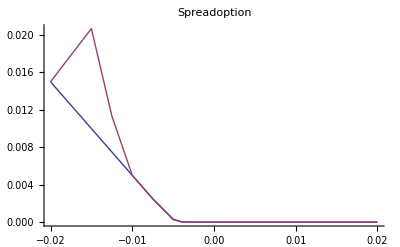
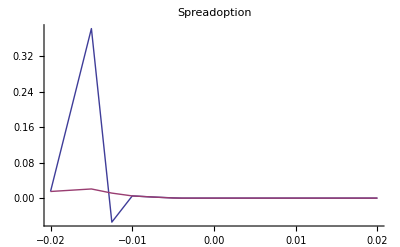
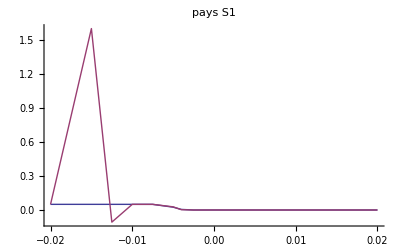
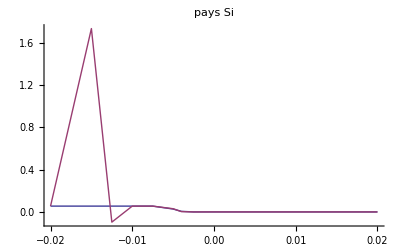
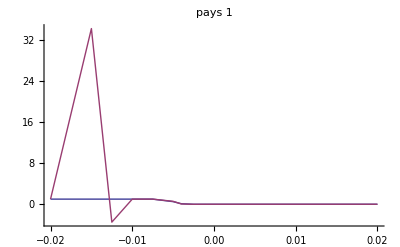
{181.375,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.055,T=10,equivalentσ1,equivalentσi,equivalentρ,bilogdigitale,
bilogSpreadoptionGRAPH,alphaSpreadoptionGRAPH,paysS1GRAPH,paysSiGRAPH,paysKGRAPH,paysdigitaleGRAPH,priceSpreadoption,BilogToHestonFlag,
KList={-0.02,-0.015,-0.0125,-0.01,-0.0075,-0.005,-0.004,-0.0025,-0.001,0,0.001,0.0025,0.004,0.005,0.0075,0.01,0.0125,0.015,0.02},LimitGindinkin=10,printflag=0,prices1,pricesi,priced,priceK,commonν=0.01,bilogprices1,bilogpricesi,bilogpriceK,νcommun},τ=10;λ=0.1;LT=1;
V1=1;V2=1;V3=1;V4=1;V5=0.00001;Vi=0.00001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;
αi1=0.01;αi2=0.01;αi3=0.01;αi4=0.01;
νcommun=2;BilogToHestonFlag=2;
ρ1=-0.5;ν1=νcommun;ρ2=-0.5;ν2=νcommun;ρ3=-0.5;ν3=νcommun;ρ4=-0.5;ν4=νcommun;ρ5=-0.5;ν5=νcommun √V5;ρi=-0.5;νi=νcommun √Vi;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
bilogprices1=Table[S1 MesureQ1LogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
bilogpricesi=Table[Si MesureQ2LogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
bilogpriceK=Table[KList[[i]] MesureQTLogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
bilogdigitale=Table[ MesureQTLogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
prices1=S1 SmileAlphaDigitaleU1[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,BilogToHestonFlag];
pricesi=Si SmileAlphaDigitaleUi[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,BilogToHestonFlag];
priced=SmileAlphaDigitale[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,BilogToHestonFlag];
priceK=Table[priced[[i]] KList[[i]],{i,Length[KList]}];
priceSpreadoption= SmileAlphaSpreadOption[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag,BilogToHestonFlag];
bilogSpreadoptionGRAPH=ListPlot[{Transpose[{KList,bilogprices1-bilogpricesi-bilogpriceK}],Transpose[{KList,priceSpreadoption}]},Joined->True,PlotLabel->"Spreadoption",PlotLegend->{"bilog","alpha"}];
alphaSpreadoptionGRAPH=ListPlot[{Transpose[{KList,prices1-pricesi-priceK}],Transpose[{KList,priceSpreadoption}]},Joined->True,PlotLabel->"Spreadoption",PlotLegend->{"reconstitued alpha","authentic alpha"}];
paysS1GRAPH=ListPlot[{Transpose[{KList,bilogprices1}],Transpose[{KList,prices1}]},Joined->True,PlotLabel->"pays S1",PlotLegend->{"bilog","alpha"}];
paysSiGRAPH=ListPlot[{Transpose[{KList,bilogpricesi}],Transpose[{KList,pricesi}]},Joined->True,PlotLabel->"pays Si",PlotLegend->{"bilog","alpha"}];
paysdigitaleGRAPH=ListPlot[{Transpose[{KList,bilogdigitale}],Transpose[{KList,priced}]},Joined->True,PlotLabel->"pays 1",PlotLegend->{"bilog","alpha"}];
{bilogSpreadoptionGRAPH,alphaSpreadoptionGRAPH,paysS1GRAPH,paysSiGRAPH,paysdigitaleGRAPH}
]]]
```

## Equation dynamique d' absence d' arbitrage des digitales

### Cas Bilog / normal Heston

```mathematica
E[SuperPlus[(Subscript[S, 1]-Subscript[S, 2]-K)]]=E[Subscript[S, 1] Subscript[1, Subscript[S, 1]-Subscript[S, 2]-K≥0]]-E[Subscript[S, 2] Subscript[1, Subscript[S, 1]-Subscript[S, 2]-K≥0]]-K E[Subscript[1, Subscript[S, 1]-Subscript[S, 2]-K≥0]]
```

```mathematica
Soit ϕ[Subscript[S, 0],Subscript[V, 0],ρ,ν,K] le prix d'un normal Heston pour la maturité T , et avec les parametres λ et Subscript[L, T]
```

```mathematica
soit Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]  et Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]   les resultat de l'optimisation de la normal heston sur le bilog toujours pour la maturité T  et avec les parametres λ et Subscript[L, T]
```

```mathematica
on a les evaluations suivantes :
```

```mathematica
E[SuperPlus[(Subscript[S, 1]-Subscript[S, 2]-K)]]=ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[ΔV, α] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δρ, α],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δν, α],K]
```

```mathematica
E[Subscript[1, Subscript[S, 1]-Subscript[S, 2]-K≥0]]=D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[ΔV, α] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δρ, α],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δν, α],K], K]
```

```mathematica
E[Subscript[S, 1] Subscript[1, Subscript[S, 1]-Subscript[S, 2]-K≥0]]=Subscript[S, 1](E^Subscript[Q, Subscript[S, 1]])[Subscript[1, Subscript[S, 1]-Subscript[S, 2]-K≥0]]=Subscript[S, 1] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T)-Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[ΔV^1, α] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δρ^1, α],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δν^1, α],K], K]
```

```mathematica
E[Subscript[S, 2] Subscript[1, Subscript[S, 1]-Subscript[S, 2]-K≥0]]=Subscript[S, 2](E^Subscript[Q, Subscript[S, 2]])[Subscript[1, Subscript[S, 1]-Subscript[S, 2]-K≥0]]=Subscript[S, 2] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[ΔV^2, α] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δρ^2, α],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δν^2, α],K], K]
```

```mathematica
E[Subscript[S, 2] Subscript[1, Subscript[S, 1]-Subscript[S, 2]-K≥0]]=Subscript[S, 2](E^Subscript[Q, Subscript[S, 2]])[Subscript[1, Subscript[S, 1]-Subscript[S, 2]-K≥0]]=S2-E[S2 Subscript[1, S2-S1>-K]]
```

```mathematica
ou Subscript[ΔV^1, α]   ,Subscript[Δρ^1, α] and Subscript[Δν^1, α]   represent the dynamic specific to the digitals, (same for Subscript[ΔV^2, α]   ,Subscript[Δρ^2, α] and Subscript[Δν^2, α]) in addition of the shift of the forward
```

```mathematica
l'equation s'ecrit:
```

```mathematica
ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[ΔV, α] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δρ, α],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δν, α],K]=
Subscript[S, 1] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T)-Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[ΔV^1, α] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δρ^1, α],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δν^1, α],K], K]-
Subscript[S, 2] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[ΔV^2, α] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δρ^2, α],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δν^2, α],K], K]-
K D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[ΔV, α] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δρ, α],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δν, α],K], K]
```

```mathematica
that we know it is true for Subscript[ΔV, α]=Subscript[Δρ, α]=Subscript[Δν, α]=Subscript[ΔV^1, α]=Subscript[Δρ^1, α]=Subscript[Δν^1, α]=Subscript[ΔV^2, α] =Subscript[Δρ^2, α]=Subscript[Δν^2, α]=0   bicause it is just the bilog exact relationship
```

```mathematica
we therfore make a first order developement around this exact case:
```

```mathematica
(D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], V]+K D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,V])Subscript[ΔV, α]+
(D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], ρ]+K D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ρ])Subscript[Δρ, α]+
(D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], ν]+K D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ν])Subscript[Δν, α]=
Subscript[S, 1] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T)-Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,V] Subscript[ΔV^1, α]+
Subscript[S, 1] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T)-Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ρ] Subscript[Δρ^1, α]+
Subscript[S, 1] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T)-Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ν] Subscript[Δν^1, α]-
Subscript[S, 2] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,V] Subscript[ΔV^2, α]-
Subscript[S, 2] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ρ] Subscript[Δρ^2, α]-Subscript[S, 2] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ν] Subscript[Δν^2, α]
```

```mathematica
we choose at that point to separate the effect of the different dimensions of the deformation by postulating:
```

```mathematica
(D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], V]+K D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,V])Subscript[ΔV, α]=
Subscript[S, 1] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T)-Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,V] Subscript[ΔV^1, α]-
Subscript[S, 2] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,V] Subscript[ΔV^2, α]
```

```mathematica
and
```

```mathematica
(D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], ρ]+K D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ρ])Subscript[Δρ, α]=
Subscript[S, 1] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T)-Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ρ] Subscript[Δρ^1, α]-
Subscript[S, 2] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ρ] Subscript[Δρ^2, α]
```

```mathematica
and
```

```mathematica
(D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], ν]+K D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ν])Subscript[Δν, α]=
Subscript[S, 1] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T)-Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ν] Subscript[Δν^1, α]-
Subscript[S, 2] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ν] Subscript[Δν^2, α]
```

```mathematica
From   the parity relationship   E[S2 Subscript[1, S1-S2>K]]=S2-E[S2 Subscript[1, S1-S2<K]]=S2-E[S2 Subscript[1, S2-S1>-K]]
```

```mathematica
we deduce that
```

```mathematica
D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[ΔV^2, α] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δρ^2, α],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δν^2, α],K], K]=
-D[ϕ[Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T)-Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 2],Subscript[σ, 1],Subscript[ρ, S]]+Subscript[ΔV^1, α] ,Subscript[ρ, b][Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 2],Subscript[σ, 1],Subscript[ρ, S]]+Subscript[Δρ^1, α],Subscript[ν, b][Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 2],Subscript[σ, 1],Subscript[ρ, S]]+Subscript[Δν^1, α],-K], K]
```

```mathematica
with
```

```mathematica
{{{{Subscript[V, b][Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 2],Subscript[σ, 1],Subscript[ρ, S]]=Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]}, {Subscript[ρ, b][Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 2],Subscript[σ, 1],Subscript[ρ, S]]=-Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]}}}, {Subscript[ν, b][Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 2],Subscript[σ, 1],Subscript[ρ, S]]=Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]}}
```

```mathematica
therefore:
```

```mathematica
D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 2],Subscript[σ, 1],Subscript[ρ, S]]+Subscript[ΔV^2, α] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δρ^2, α],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δν^2, α],K], K]=
-D[ϕ[Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T)-Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[ΔV^1, α] ,-Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δρ^1, α],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]]+Subscript[Δν^1, α],-K], K]
```

```mathematica
Now we reinject the preceding relationship in our 3 equations describing the arbitrage freeness:
```

```mathematica
(D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], V]+K D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,V])Subscript[ΔV, α]=
(Subscript[S, 1] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T)-Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,V]+
Subscript[S, 2] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,-Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],-K], K,V])Subscript[ΔV^1, α]
```

```mathematica
and
```

```mathematica
(D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], ρ]+K D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ρ])Subscript[Δρ, α]=
(Subscript[S, 1] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T)-Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ρ]+
Subscript[S, 2] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,-Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],-K], K,ρ])Subscript[Δρ^1, α]
```

```mathematica
and
```

```mathematica
(D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], ν]+K D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ν])Subscript[Δν, α]=
(Subscript[S, 1] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T)-Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ν]+
Subscript[S, 2] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,-Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],-K], K,ν])Subscript[Δν^1, α]
```

```mathematica
ceci nous permet de conclure :
```

```mathematica
Subscript[ΔV^1, α]=Subscript[ΔV, α](D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], V]+K D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,V])/(Subscript[S, 1] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T)-Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,V]+
Subscript[S, 2] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,-Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],-K], K,V])
```

```mathematica
Subscript[Δρ^1, α]=Subscript[Δρ, α] (D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], ρ]+K D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ρ])/(Subscript[S, 1] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T)-Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ρ]+
Subscript[S, 2] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,-Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],-K], K,ρ])
```

```mathematica
Subscript[Δν^1, α]=Subscript[Δν, α](D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], ν]+K D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ν])/(Subscript[S, 1] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T)-Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ν]+
Subscript[S, 2] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,-Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],-K], K,ν])
```

```mathematica
de meme un raisonement dual nous permet de conclure:
```

```mathematica
Subscript[ΔV^2, α]=Subscript[ΔV, α](D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], V]+K D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,V])/(Subscript[S, 1] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T)-Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,-Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],-K], K,V]+
Subscript[S, 2] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,V])
```

```mathematica
Subscript[Δρ^2, α]=Subscript[Δρ, α] (D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], ρ]+K D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ρ])/(Subscript[S, 1] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T)-Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,-Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],-K], K,ρ]+
Subscript[S, 2] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ρ])
```

```mathematica
Subscript[Δν^2, α]=Subscript[Δν, α](D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], ν]+K D[ϕ[Subscript[S, 1]-Subscript[S, 2],Subscript[V, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1],Subscript[S, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ν])/(Subscript[S, 1] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T)-Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,-Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1]^2 T),Subscript[S, 2] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],-K], K,ν]+
Subscript[S, 2] D[ϕ[Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T)-Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[V, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]] ,Subscript[ρ, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],Subscript[ν, b][Subscript[S, 1] ⅇ^(Subscript[σ, 1] Subscript[σ, 2] T),Subscript[S, 2] ⅇ^(Subscript[σ, 2]^2 T),Subscript[σ, 1],Subscript[σ, 2],Subscript[ρ, S]],K], K,ν])
```

```mathematica
Dans les formules (ci-dessus et ci-dessous) on utilise Subscript[ΔV, α] pour des raison de completude du raisonement, mais dans les fait, Subscript[ΔV, α]=0
```

### Exemple 1

```mathematica
AlphaDigitalDeltaRatios[S1_,S2_,σ1_,σ2_,ρ_,Vb_,rhob_,nub_,VbS1_,rhobS1_,nubS1_,VbS2_,rhobS2_,nubS2_,λ_,L_,T_,nbsteps_,scale_,microratio_,flag_]:=Module[{S0=S1-S2,KList={S1-S2},der,derK,derKS1,derKS2,dermoinsKS1,dermoinsKS2,nuratioS1,nuratioS2,rhoratioS1,rhoratioS2},
der=DerivativeHestonNormalCall[rhob,λ,L,nub,Vb,S1-S2,{S1-S2},T,nbsteps,scale,microratio,flag];
derK=DerKDerivativeHestonNormalCall[rhob,λ,L,nub,Vb,S1-S2,{S1-S2},T,nbsteps,scale,microratio,flag];
derKS1=DerKDerivativeHestonNormalCall[rhobS1,λ,L,nubS1,VbS1,S1 ⅇ^(σ1^2 T)-S2 ⅇ^(ρ σ1 σ2 T),{S1-S2},T,nbsteps,scale,microratio,flag];
derKS2=DerKDerivativeHestonNormalCall[rhobS2,λ,L,nubS2,VbS2,S1 ⅇ^(ρ σ1 σ2 T)-S2 ⅇ^(σ2^2 T),{S1-S2},T,nbsteps,scale,microratio,flag];
Print["der=",der," derK=",derK," derKS1=",derKS1," derKS2=",derKS2];
dermoinsKS1=DerKDerivativeHestonNormalCall[-rhobS1,λ,L,nubS1,VbS1,S1 ⅇ^(σ1^2 T)-S2 ⅇ^(ρ σ1 σ2 T),{-S1+S2},T,nbsteps,scale,microratio,flag];
dermoinsKS2=DerKDerivativeHestonNormalCall[-rhobS2,λ,L,nubS2,VbS2,S1 ⅇ^(ρ σ1 σ2 T)-S2 ⅇ^(σ2^2 T),{-S1+S2},T,nbsteps,scale,microratio,flag];
Print["dermoinsKS1=",dermoinsKS1,"  dermoinsKS2=",dermoinsKS2];
rhoratioS1=(der[[3,1]]+(S1-S2) derK[[3,1]])/(derKS1[[3,1]]+dermoinsKS2[[3,1]]);
nuratioS1=(der[[4,1]]+(S1-S2) derK[[4,1]])/(derKS1[[4,1]]+dermoinsKS2[[4,1]]);
rhoratioS2=(der[[3,1]]+(S1-S2) derK[[3,1]])/(dermoinsKS1[[3,1]]+derKS2[[3,1]]);
nuratioS2=(der[[4,1]]+(S1-S2) derK[[4,1]])/(dermoinsKS1[[4,1]]+derKS2[[4,1]]);
{{rhoratioS1,nuratioS1},{rhoratioS2,nuratioS2}}
]
```

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,
S1,Si,T,equivalentσ1,equivalentσi,equivalentρ,bilogdigitale,
bilogSpreadoptionGRAPH,alphaSpreadoptionGRAPH,paysS1GRAPH,paysSiGRAPH,paysKGRAPH,paysdigitaleGRAPH,priceSpreadoption,BilogToHestonFlag,
Vb,rhob,nub,VbS1,rhobS1,nubS1,VbS2,rhobS2,nubS2,smoothFactor,commonν,bilogprices1,bilogpricesi,bilogpriceK,νcommun,
nbsteps,scale,microratio,flag},
nbsteps=120;scale=10;microratio=75;flag=2;λ=0.1;LT=1;S1=0.05;Si=0.051;T=10;smoothFactor=20;commonν=0.01;
V1=1;V2=1;V3=1;V4=1;V5=0.00001;Vi=0.00001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;
αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;
νcommun=0.001;BilogToHestonFlag=2;
ρ1=-0.5;ν1=νcommun;ρ2=-0.5;ν2=νcommun;ρ3=-0.5;ν3=νcommun;ρ4=-0.5;ν4=νcommun;ρ5=-0.5;ν5=νcommun √V5;ρi=-0.5;νi=νcommun √Vi;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
Print["equivalentσ1=",equivalentσ1,"  equivalentσi=",equivalentσi,"  equivalentρ=",equivalentρ];
{Vb,rhob,nub}=HestonFromBilogPackaged[S1,Si,equivalentσ1,equivalentσi,equivalentρ,T,λ,LT,smoothFactor];
Print["{Vb,rhob,nub}=",{Vb,rhob,nub}];
{VbS1,rhobS1,nubS1}=HestonFromBilogPackaged[S1  Exp[equivalentσ1^2 T],Si Exp[equivalentρ equivalentσ1 equivalentσi T],equivalentσ1,equivalentσi,equivalentρ,T,λ,LT,smoothFactor];
Print["{VbS1,rhobS1,nubS1}=",{VbS1,rhobS1,nubS1}];
{VbS2,rhobS2,nubS2}=HestonFromBilogPackaged[S1 Exp[equivalentρ equivalentσ1 equivalentσi T],Si  Exp[equivalentσi^2 T],equivalentσ1,equivalentσi,equivalentρ,T,λ,LT,smoothFactor];
Print["{VbS2,rhobS2,nubS2}=",{VbS2,rhobS2,nubS2}];
AlphaDigitalDeltaRatios[S1,Si,equivalentσ1,equivalentσi,equivalentρ,Vb,rhob,nub,VbS1,rhobS1,nubS1,VbS2,rhobS2,nubS2,λ,LT,T,nbsteps,scale,microratio,flag]
]]]
```

equivalentσ1=0.0202485  equivalentσi=0.0202485  equivalentρ=0.

InitialV0=2.09141×10^-6 νup=0.00289234 Stdev(pour le calcul des strike)=0.00457319

strikes={-0.0015244,-0.000762199,0,0.000762199,0.0015244}

pricegoaltable={0.00209817,0.00170732,0.00136713,0.00107646,0.000832888}

optimisation results:{1.98801×10^-18,{-4.69625×10^-9,-0.0142833,0.0000309295}}

{Vb,rhob,nub}={1.99382×10^-6,-0.0142833,0.000067606}

InitialV0=2.09985×10^-6 νup=0.00289817 Stdev(pour le calcul des strike)=0.00458241

strikes={-0.00152747,-0.000763735,0,0.000763735,0.00152747}

pricegoaltable={0.00221749,0.0018121,0.00145753,0.00115303,0.000896489}

optimisation results:{1.69094×10^-18,{-4.54111×10^-9,-0.011333,0.0000313568}}

{VbS1,rhobS1,nubS1}={2.00187×10^-6,-0.011333,0.0000679615}

InitialV0=2.10019×10^-6 νup=0.00289841 Stdev(pour le calcul des strike)=0.00458278

strikes={-0.00152759,-0.000763797,0,0.000763797,0.00152759}

pricegoaltable={0.00199119,0.0016133,0.001286,0.0010078,0.000775922}

optimisation results:{2.17413×10^-18,{-4.91402×10^-9,-0.0172293,0.0000305911}}

{VbS2,rhobS2,nubS2}={2.00219×10^-6,-0.0172293,0.0000675044}

der={{0.00178051},{446.936},{1.30819×10^-9},{-0.0253501}} derK={{1.×10^-12},{0.0562757},{0.0000156959},{-0.00331934}} derKS1={{0.000205421},{6.53843},{0.000015727},{-0.00373522}} derKS2={{1.×10^-12},{-6.55546},{0.0000156225},{-0.00286668}}

dermoinsKS1={{1.×10^-12},{-52.3878},{0.0000121917},{0.0105046}}  dermoinsKS2={{1.×10^-12},{-61.8349},{0.000010455},{0.0123057}}

{120.984,{{-0.000549525,-2.95744},{-0.000517278,-3.31856}}}

```mathematica
Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,
S1,Si,T,equivalentσ1,equivalentσi,equivalentρ,bilogdigitale,K,
bilogSpreadoptionGRAPH,alphaSpreadoptionGRAPH,paysS1GRAPH,paysSiGRAPH,paysKGRAPH,paysdigitaleGRAPH,priceSpreadoption,BilogToHestonFlag,
Vb,rhob,nub,VbS1,rhobS1,nubS1,VbS2,rhobS2,nubS2,smoothFactor,commonν,bilogprices1,bilogpricesi,bilogpriceK,νcommun,V0x,
der,derK,derKS1,derKS2,dermoinsKS1,dermoinsKS2,VS,VarVSIncrementale,CoVarSVSIncrementale,VarVSTotal,CoVarSVSTotal,ρprojeté,νprojeté,V0projeté,forward,shiftL,CompoundK,price,priceBilog,prices,digitaleprice,pricesBilog,digitalepriceBilog,Δnu,Δprice,Δdigitaleprice,pricesS1,digitalepriceS1,pricesBilogS1,digitalepriceBilogS1,Δrho,digitalepriceSi,ΔdigitalepriceS1,pricesSi,pricesBilogSi,digitalepriceBilogSi,
ΔdigitalepriceSi,ByDualitypricesBilogSi,ByDualitydigitalepriceBilogSi,ByDualitypricesSi,ByDualitydigitalepriceSi,Δrhoprojeté,Δnuprojeté,tryfunc3,
nbsteps,scale,microratio,flag},nbsteps=120;scale=10;microratio=75;flag=2;λ=0.1;LT=1;S1=0.05;Si=0.0505;T=10;smoothFactor=20;
V1=1;V2=1;V3=1;V4=1;V5=0.00001;Vi=0.00001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;
αi1=0.01;αi2=0.01;αi3=0.01;αi4=0.01;
νcommun=2;BilogToHestonFlag=2;
ρ1=-0.5;ν1=νcommun;ρ2=-0.5;ν2=νcommun;ρ3=-0.5;ν3=νcommun;ρ4=-0.5;ν4=νcommun;ρ5=-0.5;ν5=νcommun √V5;ρi=-0.5;νi=νcommun √Vi;
K=S1-Si;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
Print["equivalentσ1=",equivalentσ1,"  equivalentσi=",equivalentσi,"  equivalentρ=",equivalentρ];
{Vb,rhob,nub}=HestonFromBilogPackaged[S1,Si,equivalentσ1,equivalentσi,equivalentρ,T,λ,LT,smoothFactor];
Print["{Vb,rhob,nub}=",{Vb,rhob,nub}];
{VbS1,rhobS1,nubS1}=HestonFromBilogPackaged[S1  Exp[equivalentσ1^2 T],Si Exp[equivalentρ equivalentσ1 equivalentσi T],equivalentσ1,equivalentσi,equivalentρ,T,λ,LT,smoothFactor];
Print["{VbS1,rhobS1,nubS1}=",{VbS1,rhobS1,nubS1}];
{VbS2,rhobS2,nubS2}=HestonFromBilogPackaged[S1 Exp[equivalentρ equivalentσ1 equivalentσi T],Si  Exp[equivalentσi^2 T],equivalentσ1,equivalentσi,equivalentρ,T,λ,LT,smoothFactor];
Print["{VbS2,rhobS2,nubS2}=",{VbS2,rhobS2,nubS2}];
der=DerivativeHestonNormalCall[rhob,λ,LT,nub,Vb,S1-Si,{S1-Si},T,nbsteps,scale,microratio,flag];
derK=DerKDerivativeHestonNormalCall[rhob,λ,LT,nub,Vb,S1-Si,{S1-Si},T,nbsteps,scale,microratio,flag];
derKS1=DerKDerivativeHestonNormalCall[rhobS1,λ,LT,nubS1,VbS1,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{S1-Si},T,nbsteps,scale,microratio,flag];
derKS2=DerKDerivativeHestonNormalCall[rhobS2,λ,LT,nubS2,VbS2,S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T),{S1-Si},T,nbsteps,scale,microratio,flag];
Print["der=",der," derK=",derK," derKS1=",derKS1," derKS2=",derKS2];
dermoinsKS1=DerKDerivativeHestonNormalCall[-rhobS1,λ,LT,nubS1,VbS1,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ  equivalentσ1 equivalentσi T),{-S1+Si},T,nbsteps,scale,microratio,flag];
dermoinsKS2=DerKDerivativeHestonNormalCall[-rhobS2,λ,LT,nubS2,VbS2,S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(σ2^2 T),{-S1+Si},T,nbsteps,scale,microratio,flag];
{VS,VarVSIncrementale,CoVarSVSIncrementale}=AlphaDigitaleObservable1iz[S1,Si,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi];
Print["VS=",VS," VarVSIncrementale=",VarVSIncrementale," CoVarSVSIncrementale=",CoVarSVSIncrementale];
VarVSTotal=nub^2 Vb+VarVSIncrementale;
CoVarSVSTotal=rhob Vb nub+CoVarSVSIncrementale;
Print["VSTotal=",Vb," VarVSTotal=",VarVSTotal," CoVarSVSTotal= ",CoVarSVSTotal];
ρprojeté=CoVarSVSTotal/(√(Vb VarVSTotal));νprojeté=√(VarVSTotal/Vb);V0projeté=Vb;
forward=S1-Si;
Print["Normal Heston Parameters=",{{"S0",forward},{"V0 Bilog",Vb},{"ρ Bilog",rhob},{"ν Bilog",nub},{"ν Bilog normalized",nub/(√Vb)},
{"V0 Bilog S1",VbS1},{"ρ Bilog S1",rhobS1},{"ν Bilog S1",nubS1},{"ν Bilog S1 normalized",nubS1/(√VbS1)},
{"V0 Bilog S2",VbS2},{"ρ Bilog S2",rhobS2},{"ν Bilog S2",nubS2},{"ν Bilog S2 normalized",nubS2/(√VbS2)},
{"V0",V0projeté},{"ρ",ρprojeté},{"ν",νprojeté},
{"standard dev equi.",√Vb},{"ν normalized",νprojeté/(√Vb)}} //MatrixForm];
shiftL=0.0001;
CompoundK={K-shiftL,K+shiftL};
price=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,V0projeté,S1-Si,{K},T,nbsteps,scale,microratio,0][[1,1]];
priceBilog=DerivativeHestonNormalCall[rhob,λ,LT,nub,Vb,S1-Si,{K},T,nbsteps,scale,microratio,0][[1,1]];
prices=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,V0projeté,S1-Si,{K-shiftL,K+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitaleprice=-(prices[[2]]-prices[[1]])/(2shiftL);
pricesBilog=DerivativeHestonNormalCall[rhob,λ,LT,nub,Vb,S1-Si,{K-shiftL,K+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceBilog=-(pricesBilog[[2]]-pricesBilog[[1]])/(2shiftL);
Print["Spreadoption=",price," Prix de la digitale=",digitaleprice];
Δnu=νprojeté-nub;Δrho=ρprojeté-rhob;
Δprice=price-priceBilog;Δdigitaleprice=digitaleprice-digitalepriceBilog;
pricesS1=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,V0projeté,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{K-shiftL,K+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
pricesBilogS1=DerivativeHestonNormalCall[rhobS1,λ,LT,nubS1,VbS1,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{K-shiftL,K+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceBilogS1=-(pricesBilogS1[[2]]-pricesBilogS1[[1]])/(2shiftL);
ΔdigitalepriceS1=digitalepriceS1-digitalepriceBilogS1;
pricesSi=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,V0projeté,S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T) ,{K-shiftL,K+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceSi=-(pricesSi[[2]]-pricesSi[[1]])/(2shiftL);
pricesBilogSi=DerivativeHestonNormalCall[rhobS2,λ,LT,nubS2,VbS2,S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T) ,{K-shiftL,K+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceBilogSi=-(pricesBilogSi[[2]]-pricesBilogSi[[1]])/(2shiftL);
ΔdigitalepriceSi=digitalepriceSi-digitalepriceBilogSi;
Print["priceBilog+K digitalepriceBilog=",priceBilog+K digitalepriceBilog];
Print["S1 digitalepriceBilogS1-Si digitalepriceBilogSi=",S1 digitalepriceBilogS1-Si digitalepriceBilogSi];
Print["price+K digitaleprice=",price+K digitaleprice];
Print["S1 digitalepriceS1-Si digitalepriceSi=",S1 digitalepriceS1-Si digitalepriceSi];

ByDualitypricesBilogSi=DerivativeHestonNormalCall[rhobS2,λ,LT,nubS2,VbS2,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-K-shiftL,-K+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceBilogSi=-(ByDualitypricesBilogSi[[2]]-ByDualitypricesBilogSi[[1]])/(2shiftL);

Print["digitale Bilog Si by duality=",1+ByDualitydigitalepriceBilogSi," digitalepriceBilogSi=",digitalepriceBilogSi];

ByDualitypricesSi=DerivativeHestonNormalCall[-ρprojeté,λ,LT,νprojeté,V0projeté,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-K-shiftL,-K+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);

Print["digitale Si by duality=",1-ByDualitydigitalepriceSi," digitalepriceSi=",digitalepriceSi];

Print["priceBilog+K digitalepriceBilog+Si=",priceBilog+K digitalepriceBilog+Si," S1 digitalepriceBilogS1+Si ByDualitydigitalepriceBilogSi=",S1 digitalepriceBilogS1+Si ByDualitydigitalepriceBilogSi];
Print["price+K digitaleprice+Si=",price+K digitaleprice+Si," S1 digitalepriceS1+Si ByDualitydigitalepriceSi =",S1 digitalepriceS1+Si ByDualitydigitalepriceSi ];
Δrhoprojeté=ρprojeté-rhob;
Δnuprojeté=νprojeté-nub;
Print["Δrhoprojeté=",Δrhoprojeté," Δnuprojeté=",Δnuprojeté];
tryfunc3=Function[{V0,rho,nu},Module[{pricesS1a,digitalepriceS1a,ByDualitypricesSia,ByDualitydigitalepriceSia},pricesS1a=DerivativeHestonNormalCall[rho,λ,LT,nu,V0,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{K-shiftL,K+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1a=-(pricesS1a[[2]]-pricesS1a[[1]])/(2shiftL);
ByDualitypricesSia=DerivativeHestonNormalCall[-rho,λ,LT,nu,V0,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-K-shiftL,-K+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSia=-(ByDualitypricesSia[[2]]-ByDualitypricesSia[[1]])/(2shiftL);
S1 digitalepriceS1a+Si ByDualitydigitalepriceSia]];
V0x=V0x/.FindRoot[tryfunc3[V0x,ρprojeté,νprojeté]==price+K digitaleprice+Si,{V0x,Vb,Vb/2,4Vb}];
Print[" V0x=",V0x," Marge d'arbitrage=",tryfunc3[V0x,ρprojeté,νprojeté]-(price+K digitaleprice+Si)];
]]
```

equivalentσ1=0.0202485  equivalentσi=0.0202485  equivalentρ=0.97561

InitialV0=5.06025×10^-8 νup=0.0004499 Stdev(pour le calcul des strike)=0.000711354

strikes={-0.000237118,-0.000118559,0,0.000118559,0.000237118}

pricegoaltable={0.0001713,0.000132682,0.000100917,0.0000753304,0.0000551593}

optimisation results:{8.79073×10^-19,{8.00935×10^-10,-0.0502193,0.0000110648}}

{Vb,rhob,nub}={4.82552×10^-8,-0.0502193,0.0000149036}

InitialV0=5.1012×10^-8 νup=0.000451717 Stdev(pour le calcul des strike)=0.000714227

strikes={-0.000238076,-0.000119038,0,0.000119038,0.000238076}

pricegoaltable={0.000173795,0.000134718,0.000102547,0.0000766104,0.0000561441}

optimisation results:{8.01582×10^-19,{8.07129×10^-10,-0.0497146,0.000011111}}

{VbS1,rhobS1,nubS1}={4.86457×10^-8,-0.0497146,0.0000149638}

InitialV0=5.10161×10^-8 νup=0.000451735 Stdev(pour le calcul des strike)=0.000714256

strikes={-0.000238085,-0.000119043,0,0.000119043,0.000238085}

pricegoaltable={0.000170209,0.000131735,0.000100117,0.0000746716,0.0000546305}

optimisation results:{8.05171×10^-19,{8.07605×10^-10,-0.0507241,0.000011113}}

{VbS2,rhobS2,nubS2}={4.86497×10^-8,-0.0507241,0.0000149655}

der={{0.000276861},{2874.26},{1.50516×10^-9},{-0.0358793}} derK={{1.×10^-12},{1.8048},{3.46181×10^-6},{-0.0116872}} derKS1={{3.01629×10^-6},{5.72454},{3.47552×10^-6},{-0.0117172}} derKS2={{1.×10^-12},{-7.43725},{3.47605×10^-6},{-0.0114563}}

VS=5.06025×10^-8 VarVSIncrementale=2.49506×10^-15 CoVarSVSIncrementale=-3.95235×10^-12

VSTotal=4.82552×10^-8 VarVSTotal=2.50578×10^-15 CoVarSVSTotal= -3.98846×10^-12

Normal Heston Parameters=(S0 | -0.0005
V0 Bilog | 4.82552×10^-8
ρ Bilog | -0.0502193
ν Bilog | 0.0000149036
ν Bilog normalized | 0.0678454
V0 Bilog S1 | 4.86457×10^-8
ρ Bilog S1 | -0.0497146
ν Bilog S1 | 0.0000149638
ν Bilog S1 normalized | 0.0678454
V0 Bilog S2 | 4.86497×10^-8
ρ Bilog S2 | -0.0507241
ν Bilog S2 | 0.0000149655
ν Bilog S2 normalized | 0.0678503
V0 | 4.82552×10^-8
ρ | -0.362712
ν | 0.000227876
standard dev equi. | 0.000219671
ν normalized | 1.03735)

Spreadoption=0.000233327 Prix de la digitale=0.570535

priceBilog+K digitalepriceBilog=0.0000264699

S1 digitalepriceBilogS1-Si digitalepriceBilogSi=0.0000392567

price+K digitaleprice=-0.0000519402

S1 digitalepriceS1-Si digitalepriceSi=0.000166866

digitale Bilog Si by duality=1.50484 digitalepriceBilogSi=0.496747

digitale Si by duality=0.564227 digitalepriceSi=0.564227

priceBilog+K digitalepriceBilog+Si=0.0505265 S1 digitalepriceBilogS1+Si ByDualitydigitalepriceBilogSi=0.0506192

price+K digitaleprice+Si=0.0504481 S1 digitalepriceS1+Si ByDualitydigitalepriceSi =0.0506669

```mathematica
SmileAlphaSpreadOption
```

Δrhoprojeté=-0.312493 Δnuprojeté=0.000212973

V0x=1.2426×10^-7 Marge d'arbitrage=-6.56751×10^-9

{127.391,Null}

```mathematica
tryfunc=Function[{rho,nu},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[rho,λ,LT,nu,V0projeté,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{K-shiftL,K+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-rho,λ,LT,nu,V0projeté,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-K-shiftL,-K+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
S1 digitalepriceS1+Si ByDualitydigitalepriceSi]];
```

```mathematica
Plot3D[tryfunc[rho,nu],{rho,-0.95,0.95},{nu,νprojeté/10,2νprojeté}]
```

-Graphics3D-

```mathematica
tryfunc3=Function[{V0,rho,nu},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[rho,λ,LT,nu,V0,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{K-shiftL,K+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-rho,λ,LT,nu,V0,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-K-shiftL,-K+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
S1 digitalepriceS1+Si ByDualitydigitalepriceSi]];
```

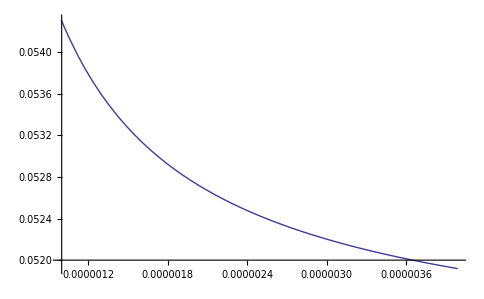

```mathematica
Plot[tryfunc3[V0,ρprojeté,νprojeté],{V0,V0projeté/2,2V0projeté}]
```

```mathematica
FindRoot[tryfunc3[V0x,ρprojeté,νprojeté]==price+K digitaleprice+Si,{V0x,Vb,Vb/2,2Vb}]
```

{V0x→3.54965×10^-6}

```mathematica
Vb
```

1.99382×10^-6

#### Tuning of the vol athe money

```mathematica
SmileAlphaDigitalesArbitrageFree[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_,T_,printflag_]:=
Module[{equivalentσ1,equivalentσi,equivalentρ,ρprojeté,νprojeté,VarVSTotal,CoVarSVSTotal,VarVSIncrementale,CoVarSVSIncrementale,VS,Vb,rhob,nub,smoothFactor=10,nbsteps=120,scale=10,microratio=75,shiftL=0.0001,
price,digitaleprice,tryfunc,Kc,VbS1,V0x,CompoundK,prices,digitaleprices,S1prices,S1digitaleprices,Siprices,Sidigitaleprices,spreadoptions},
Kc=S1-Si;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
Print["equivalentσ1",equivalentσ1," equivalentσi",equivalentσi," equivalentρ",equivalentρ];
{VS,VarVSIncrementale,CoVarSVSIncrementale}=AlphaDigitaleObservable1iz[S1,Si,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi];
If[printflag==1 || MemberQ[printflag,1] ,Print["{VS,VarVSIncrementale,CoVarSVSIncrementale}=",{VS,VarVSIncrementale,CoVarSVSIncrementale}]];
{Vb,rhob,nub}=HestonFromBilogPackaged[S1,Si,equivalentσ1,equivalentσi,equivalentρ,T,λ,LT,smoothFactor];
If[printflag==1 || MemberQ[printflag,1] ,Print["{Vb,rhob,nub}=",{Vb,rhob,nub}]];
VarVSTotal=nub^2 Vb+VarVSIncrementale;
CoVarSVSTotal=rhob Vb nub+CoVarSVSIncrementale;
ρprojeté=CoVarSVSTotal/(√(Vb VarVSTotal));νprojeté=√(VarVSTotal/Vb);
tryfunc=Function[{V0},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,V0,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-ρprojeté,λ,LT,νprojeté,V0,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc-shiftL,-Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
S1 digitalepriceS1+Si ByDualitydigitalepriceSi]];
price=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc},T,nbsteps,scale,microratio,0][[1,1]];
prices=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitaleprice=-(prices[[2]]-prices[[1]])/(2shiftL);
VbS1=V0x /. FindRoot[tryfunc[V0x]==price+Kc  digitaleprice+Si,{V0x,Vb,Vb/2,4Vb}];
If[printflag==1 || MemberQ[printflag,1] ,
Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,VbS1,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-ρprojeté,λ,LT,νprojeté,VbS1,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc-shiftL,-Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
Print["VbS1=",VbS1];
Print["spreadoption =",price];
Print["digitaleprice=",digitaleprice];
Print["Kc=",Kc];
Print["digitaleS1=",digitalepriceS1];
Print["digitaleSi=",1-ByDualitydigitalepriceSi];
Print["digitaleS1 paying float=",S1 digitalepriceS1];
Print["digitaleSi paying float=",Si(1-ByDualitydigitalepriceSi)];
Print["S1 digitalepriceS1-Si (1-ByDualitydigitalepriceSi)-Kc  digitaleprice=",S1 digitalepriceS1-Si (1-ByDualitydigitalepriceSi)-Kc  digitaleprice];
Print["marge d'arbitrage =",price+Kc  digitaleprice+Si-tryfunc[VbS1]];
Print["ρprojeté=",ρprojeté," forward=",(S1  Exp[equivalentσ1^2 T]-Si Exp[equivalentρ equivalentσ1 equivalentσi T])," ν standardize=",νprojeté/√VbS1]
]];
spreadoptions=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,K,T,nbsteps,scale,microratio,0][[1]];
CompoundK=IntercalePrice[K-shiftL,K+shiftL];
prices=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,CompoundK,T,nbsteps,scale,microratio,0][[1]];
digitaleprices=Table[(prices[[2i-1]]-prices[[2i]])/(2shiftL),{i,1,Length[K]}];
S1prices=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,VbS1,S1  ⅇ^(equivalentσ1^2 T) -Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T) ,CompoundK,T,nbsteps,scale,microratio,0][[1]];
S1digitaleprices=Table[(S1prices[[2i-1]]-S1prices[[2i]])/(2shiftL),{i,1,Length[K]}];
CompoundK=IntercalePrice[-K-shiftL,-K+shiftL];
Siprices=DerivativeHestonNormalCall[-ρprojeté,λ,LT,νprojeté,VbS1,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,CompoundK,T,nbsteps,scale,microratio,0][[1]];
Sidigitaleprices=1-Table[(Siprices[[2i-1]]-Siprices[[2i]])/(2shiftL),{i,1,Length[K]}];
If[printflag==1 || MemberQ[printflag,1] ,
Print["digitale prices=",digitaleprices];Print["digitale paying Strike=",K digitaleprices];
Print["digitale prices(for S1 dig.)=",S1digitaleprices];Print["digitale (for S1 dig.) paying float=",S1 S1digitaleprices];
Print["digitale prices(for Si dig.)=",Sidigitaleprices];Print["digitale (for Si dig.) paying float=",Si Sidigitaleprices]];
{spreadoptions,digitaleprices,S1digitaleprices,Sidigitaleprices}
]
```

#### Tuning of the vol and the rho athe money and another strike

```mathematica
SmileAlphaDigitalesArbitrageFree2[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_,T_,printflag_,otherstrike_]:=
Module[{equivalentσ1,equivalentσi,equivalentρ,ρprojeté,νprojeté,VarVSTotal,CoVarSVSTotal,VarVSIncrementale,CoVarSVSIncrementale,VS,Vb,rhob,nub,smoothFactor=10,nbsteps=120,scale=10,microratio=75,shiftL=0.0001,
price,digitaleprice,tryfunc,Kc,VbS1,V0x,CompoundK,prices,digitaleprices,S1prices,S1digitaleprices,Siprices,Sidigitaleprices,spreadoptions,
Kc2,tryfunc1,tryfunc2,price2,digitaleprice2,prices2,digitaleprices2,rhox,rhobS1,ss},
Kc=S1-Si;Kc2=otherstrike;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
Print["equivalentσ1",equivalentσ1," equivalentσi",equivalentσi," equivalentρ",equivalentρ];
{VS,VarVSIncrementale,CoVarSVSIncrementale}=AlphaDigitaleObservable1iz[S1,Si,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi];
If[printflag==1 || MemberQ[printflag,1] ,Print["{VS,VarVSIncrementale,CoVarSVSIncrementale}=",{VS,VarVSIncrementale,CoVarSVSIncrementale}]];
{Vb,rhob,nub}=HestonFromBilogPackaged[S1,Si,equivalentσ1,equivalentσi,equivalentρ,T,λ,LT,smoothFactor];
If[printflag==1 || MemberQ[printflag,1] ,Print["{Vb,rhob,nub}=",{Vb,rhob,nub}]];
VarVSTotal=nub^2 Vb+VarVSIncrementale;
CoVarSVSTotal=rhob Vb nub+CoVarSVSIncrementale;
ρprojeté=CoVarSVSTotal/(√(Vb VarVSTotal));νprojeté=√(VarVSTotal/Vb);
tryfunc1=Function[{V0,rho},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[rho,λ,LT,νprojeté,V0,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-rho,λ,LT,νprojeté,V0,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc-shiftL,-Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
S1 digitalepriceS1+Si ByDualitydigitalepriceSi]];
tryfunc2=Function[{V0,rho},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[rho,λ,LT,νprojeté,V0,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc2-shiftL,Kc2+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-rho,λ,LT,νprojeté,V0,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc2-shiftL,-Kc2+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
S1 digitalepriceS1+Si ByDualitydigitalepriceSi]];
price=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc},T,nbsteps,scale,microratio,0][[1,1]];
prices=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitaleprice=-(prices[[2]]-prices[[1]])/(2shiftL);
price2=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc2},T,nbsteps,scale,microratio,0][[1,1]];
prices2=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc2-shiftL,Kc2+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitaleprice2=-(prices2[[2]]-prices2[[1]])/(2shiftL);
ss= FindRoot[{tryfunc1[V0x,rhox]==price+Kc  digitaleprice+Si,tryfunc2[V0x,rhox]==price2+Kc2  digitaleprice2+Si},{V0x,Vb,Vb/2,4Vb},{rhox,ρprojeté,-0.9,0.9}];
VbS1=V0x /.ss;
rhobS1=rhox /.ss;
If[printflag==1 || MemberQ[printflag,1] ,
Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi,pricesS1a,digitalepriceS1a,ByDualitypricesSia,ByDualitydigitalepriceSia},pricesS1=DerivativeHestonNormalCall[rhobS1,λ,LT,νprojeté,VbS1,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-rhobS1,λ,LT,νprojeté,VbS1,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc-shiftL,-Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
pricesS1a=DerivativeHestonNormalCall[rhobS1,λ,LT,νprojeté,VbS1,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc2-shiftL,Kc2+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1a=-(pricesS1a[[2]]-pricesS1a[[1]])/(2shiftL);
ByDualitypricesSia=DerivativeHestonNormalCall[-rhobS1,λ,LT,νprojeté,VbS1,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc2-shiftL,-Kc2+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSia=-(ByDualitypricesSia[[2]]-ByDualitypricesSia[[1]])/(2shiftL);
Print["VbS1=",VbS1];Print["rhobS1=",rhobS1];
Print["spreadoption 1=",price];
Print["digitaleprice 1=",digitaleprice];
Print["Kc1 =",Kc];
Print["digitaleS1=",digitalepriceS1];
Print["digitaleSi=",1-ByDualitydigitalepriceSi];
Print["digitaleS1 paying float=",S1 digitalepriceS1];
Print["digitaleSi paying float=",Si(1-ByDualitydigitalepriceSi)];
Print["S1 digitalepriceS1-Si (1-ByDualitydigitalepriceSi)-Kc  digitaleprice=",S1 digitalepriceS1-Si (1-ByDualitydigitalepriceSi)-Kc  digitaleprice];
Print["marge d'arbitrage 1 =",price+Kc  digitaleprice+Si-tryfunc1[VbS1,rhobS1]];
Print["spreadoption 2=",price2];
Print["digitaleprice 2=",digitaleprice2];
Print["Kc2 =",Kc2];
Print["digitaleS1=",digitalepriceS1a];
Print["digitaleSi=",1-ByDualitydigitalepriceSia];
Print["digitaleS1 paying float=",S1 digitalepriceS1a];
Print["digitaleSi paying float=",Si(1-ByDualitydigitalepriceSia)];
Print["S1 digitalepriceS1-Si (1-ByDualitydigitalepriceSi)-Kc2  digitaleprice=",S1 digitalepriceS1a-Si (1-ByDualitydigitalepriceSia)-Kc  digitaleprice2];
Print["marge d'arbitrage 2 =",price2+Kc2  digitaleprice2+Si-tryfunc2[VbS1,rhobS1]];
]];
spreadoptions=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,K,T,nbsteps,scale,microratio,0][[1]];
CompoundK=IntercalePrice[K-shiftL,K+shiftL];
prices=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,CompoundK,T,nbsteps,scale,microratio,0][[1]];
digitaleprices=Table[(prices[[2i-1]]-prices[[2i]])/(2shiftL),{i,1,Length[K]}];
S1prices=DerivativeHestonNormalCall[rhobS1,λ,LT,νprojeté,VbS1,S1  ⅇ^(equivalentσ1^2 T) -Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T) ,CompoundK,T,nbsteps,scale,microratio,0][[1]];
S1digitaleprices=Table[(S1prices[[2i-1]]-S1prices[[2i]])/(2shiftL),{i,1,Length[K]}];
CompoundK=IntercalePrice[-K-shiftL,-K+shiftL];
Siprices=DerivativeHestonNormalCall[-rhobS1,λ,LT,νprojeté,VbS1,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,CompoundK,T,nbsteps,scale,microratio,0][[1]];
Sidigitaleprices=1-Table[(Siprices[[2i-1]]-Siprices[[2i]])/(2shiftL),{i,1,Length[K]}];
If[printflag==1 || MemberQ[printflag,1] ,
Print["digitale prices=",digitaleprices];
Print["digitale prices(for S1 dig.)=",S1digitaleprices];
Print["digitale prices(for Si dig.)=",Sidigitaleprices];];
{spreadoptions,digitaleprices,S1digitaleprices,Sidigitaleprices}
]
```

#### exemple simple de SmileAlphaDigitalesArbitrageFree2

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,
S1=0.0507,Si=0.0505,T=10,equivalentσ1,equivalentσi,equivalentρ,bilogdigitale,
bilogSpreadoptionGRAPH,alphaSpreadoptionGRAPH,paysS1GRAPH,paysSiGRAPH,paysKGRAPH,paysdigitaleGRAPH,priceSpreadoption,BilogToHestonFlag,
KList={-0.02,-0.015,-0.01,-0.0075,-0.005,-0.002,-0.0015,-0.00125,-0.001,-0.00075,-0.0005,-0.0004,-0.00025,-0.0001,0,0.0001,0.00025,0.0004,0.0005,0.00075,0.001,0.00125,0.0015,0.002,0.005,0.0075,0.01,0.015,0.02},LimitGindinkin=10,printflag=1,prices1,pricesi,priced,priceK,priceds1,pricedsi,commonν=0.01,bilogprices1,bilogpricesi,bilogpriceK,νcommun,otherK},τ=10;λ=0.1;LT=1;
V1=1;V2=1;V3=1;V4=1;V5=0.0005;Vi=0.0005;
α11=0.07;α12=0.06;α13=0.03;α14=0.02;
αi1=0.07;αi2=0.06;αi3=0.03;αi4=0.02;
νcommun=2;BilogToHestonFlag=2;
ρ1=-0.5;ν1=νcommun;ρ2=-0.5;ν2=νcommun;ρ3=-0.5;ν3=νcommun;ρ4=-0.5;ν4=νcommun;ρ5=-0.5;ν5=νcommun √V5;ρi=-0.5;νi=νcommun √Vi;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
otherK=0.01;
SmileAlphaDigitalesArbitrageFree2[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,printflag,otherK]
]]]
```

equivalentσ10.101489 equivalentσi0.101489 equivalentρ0.951456

{VS,VarVSIncrementale,CoVarSVSIncrementale}={2.56076×10^-6,6.44801×10^-12,-1.45707×10^-9}

InitialV0=2.56076×10^-6 νup=0.00320048 Stdev(pour le calcul des strike)=0.0050604

strikes={-0.0016868,-0.0008434,0,0.0008434,0.0016868}

pricegoaltable={0.00311095,0.0025852,0.00211938,0.00171537,0.00137226}

optimisation results:{1.06879×10^-16,{1.32966×10^-6,0.0148868,0.000819568}}

{Vb,rhob,nub}={2.81095×10^-6,0.0148854,0.000820524}

VbS1=5.27×10^-6

rhobS1=-0.716664

spreadoption 1=0.00179069

digitaleprice 1=0.558256

Kc1 =0.0002

digitaleS1=0.639607

digitaleSi=0.60447

digitaleS1 paying float=0.0324281

digitaleSi paying float=0.0305257

S1 digitalepriceS1-Si (1-ByDualitydigitalepriceSi)-Kc  digitaleprice=0.00179069

marge d'arbitrage 1 =-4.82687×10^-16

spreadoption 2=0.0000857237

digitaleprice 2=0.0237645

Kc2 =0.01

digitaleS1=0.0270067

digitaleSi=0.0207103

digitaleS1 paying float=0.00136924

digitaleSi paying float=0.00104587

S1 digitalepriceS1-Si (1-ByDualitydigitalepriceSi)-Kc2  digitaleprice=0.000318616

marge d'arbitrage 2 =1.59378×10^-16

digitale prices={0.988917,0.9771,0.951535,0.927975,0.889554,0.799065,0.774589,0.760728,0.745617,0.729107,0.711035,0.703329,0.691224,0.678424,0.669484,0.660205,0.645623,0.63021,0.619455,0.590822,0.559625,0.52586,0.489674,0.411635,0.075277,0.0175101,0.0046148,0.000368395,0.0000307996}

digitale prices(for S1 dig.)={0.978739,0.958831,0.919604,0.886729,0.838628,0.747009,0.726344,0.715265,0.703653,0.69148,0.678717,0.673441,0.665337,0.657001,0.651311,0.645514,0.636612,0.627459,0.621215,0.605097,0.588239,0.570627,0.552255,0.513252,0.244393,0.0872785,0.0270067,0.0025567,0.000246369}

digitale prices(for Si dig.)={0.977111,0.955657,0.913252,0.877536,0.82494,0.723755,0.700808,0.688497,0.67559,0.662059,0.647875,0.642013,0.633012,0.623758,0.617445,0.611016,0.601152,0.591021,0.584116,0.566324,0.547771,0.528463,0.508415,0.466238,0.199205,0.0674449,0.0207103,0.00196747,0.000189558}

{72.156,{{0.0202777,0.015359,0.010529,0.00817737,0.00590124,0.00334991,0.00295631,0.00276437,0.00257604,0.00239166,0.00221159,0.00214087,0.00203626,0.00193352,0.00186612,0.00179962,0.00170167,0.00160596,0.00154347,0.00139211,0.00124823,0.00111248,0.000985474,0.000759877,0.000130732,0.0000330661,9.07138×10^-6,7.41265×10^-7,6.21555×10^-8},{0.988917,0.9771,0.951535,0.927975,0.889554,0.799065,0.774589,0.760728,0.745617,0.729107,0.711035,0.703329,0.691224,0.678424,0.669484,0.660205,0.645623,0.63021,0.619455,0.590822,0.559625,0.52586,0.489674,0.411635,0.075277,0.0175101,0.0046148,0.000368395,0.0000307996},{0.978739,0.958831,0.919604,0.886729,0.838628,0.747009,0.726344,0.715265,0.703653,0.69148,0.678717,0.673441,0.665337,0.657001,0.651311,0.645514,0.636612,0.627459,0.621215,0.605097,0.588239,0.570627,0.552255,0.513252,0.244393,0.0872785,0.0270067,0.0025567,0.000246369},{0.977111,0.955657,0.913252,0.877536,0.82494,0.723755,0.700808,0.688497,0.67559,0.662059,0.647875,0.642013,0.633012,0.623758,0.617445,0.611016,0.601152,0.591021,0.584116,0.566324,0.547771,0.528463,0.508415,0.466238,0.199205,0.0674449,0.0207103,0.00196747,0.000189558}}}

#### Exemple complet de SmileAlphaDigitalesArbitrageFree2

equivalentσ10.101489 equivalentσi0.101489 equivalentρ0.951456

{VS,VarVSIncrementale,CoVarSVSIncrementale}={2.56076×10^-6,6.44801×10^-12,-1.45707×10^-9}

InitialV0=2.56076×10^-6 νup=0.00320048 Stdev(pour le calcul des strike)=0.0050604

strikes={-0.0016868,-0.0008434,0,0.0008434,0.0016868}

pricegoaltable={0.00311095,0.0025852,0.00211938,0.00171537,0.00137226}

optimisation results:{1.06879×10^-16,{1.32966×10^-6,0.0148868,0.000819568}}

{Vb,rhob,nub}={2.81095×10^-6,0.0148854,0.000820524}

VbS1=6.0412×10^-6

rhobS1=0.452815

spreadoption 1=0.00179069

digitaleprice 1=0.558256

Kc1 =0.0002

digitaleS1=0.449232

digitaleSi=0.413341

digitaleS1 paying float=0.022776

digitaleSi paying float=0.0208737

S1 digitalepriceS1-Si (1-ByDualitydigitalepriceSi)-Kc  digitaleprice=0.00179069

marge d'arbitrage 1 =1.43041×10^-14

spreadoption 2=0.000367797

digitaleprice 2=0.1148

Kc2 =0.005

digitaleS1=0.213592

digitaleSi=0.195788

digitaleS1 paying float=0.0108291

digitaleSi paying float=0.00988731

S1 digitalepriceS1-Si (1-ByDualitydigitalepriceSi)-Kc2  digitaleprice=0.000918838

marge d'arbitrage 2 =-2.72699×10^-15

digitale prices={0.993441,0.984102,0.959987,0.934358,0.887288,0.761017,0.725569,0.705621,0.684083,0.660906,0.636073,0.625682,0.609617,0.593002,0.581634,0.570047,0.552289,0.534127,0.521827,0.490566,0.458889,0.427215,0.395976,0.336376,0.1148,0.0503436,0.0237645,0.00590327,0.00154968}

digitale prices(for S1 dig.)={0.997219,0.988226,0.949991,0.8975,0.797439,0.604302,0.568098,0.550038,0.532091,0.514317,0.496768,0.489823,0.479495,0.469282,0.462541,0.455857,0.445942,0.436167,0.429731,0.413932,0.398567,0.383651,0.369193,0.341676,0.213592,0.145261,0.0996361,0.0476983,0.0230665}

digitale prices(for Si dig.)={0.996731,0.986161,0.941215,0.880021,0.766776,0.563793,0.527843,0.510118,0.492631,0.47543,0.458557,0.451908,0.442048,0.43233,0.425933,0.419603,0.410236,0.401027,0.394976,0.380168,0.365821,0.35194,0.338526,0.313095,0.195788,0.133415,0.091665,0.0439617,0.0212697}

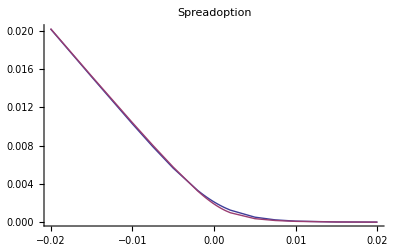
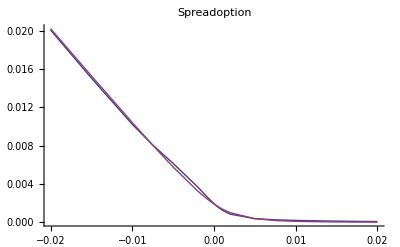
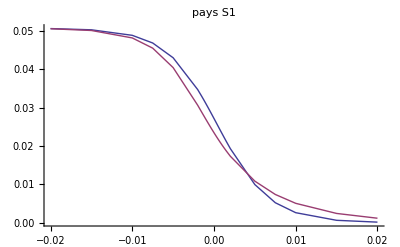
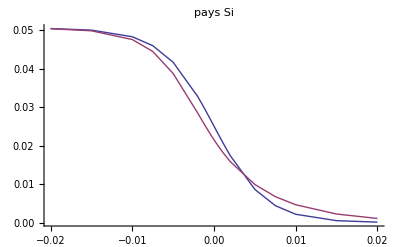
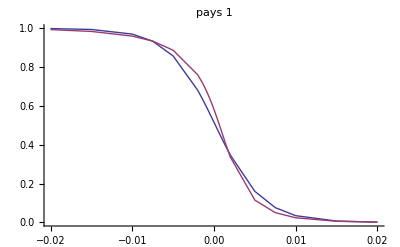
{121.625,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,{{-0.02,-0.015,-0.01,-0.0075,-0.005,-0.002,-0.0015,-0.00125,-0.001,-0.00075,-0.0005,-0.0004,-0.00025,-0.0001,0,0.0001,0.00025,0.0004,0.0005,0.00075,0.001,0.00125,0.0015,0.002,0.005,0.0075,0.01,0.015,0.02},{0.0202377,0.0152904,0.0104203,0.0080494,0.00576597,0.00326434,0.00289243,0.00271349,0.00253973,0.00237157,0.0022094,0.0021463,0.00205364,0.00196343,0.0019047,0.00184711,0.00176292,0.00168143,0.00162863,0.00150206,0.00138338,0.00127262,0.00116974,0.000986865,0.000367797,0.000173813,0.0000857237,0.0000221033,5.86684×10^-6},{0.993441,0.984102,0.959987,0.934358,0.887288,0.761017,0.725569,0.705621,0.684083,0.660906,0.636073,0.625682,0.609617,0.593002,0.581634,0.570047,0.552289,0.534127,0.521827,0.490566,0.458889,0.427215,0.395976,0.336376,0.1148,0.0503436,0.0237645,0.00590327,0.00154968},{0.997219,0.988226,0.949991,0.8975,0.797439,0.604302,0.568098,0.550038,0.532091,0.514317,0.496768,0.489823,0.479495,0.469282,0.462541,0.455857,0.445942,0.436167,0.429731,0.413932,0.398567,0.383651,0.369193,0.341676,0.213592,0.145261,0.0996361,0.0476983,0.0230665},{0.996731,0.986161,0.941215,0.880021,0.766776,0.563793,0.527843,0.510118,0.492631,0.47543,0.458557,0.451908,0.442048,0.43233,0.425933,0.419603,0.410236,0.401027,0.394976,0.380168,0.365821,0.35194,0.338526,0.313095,0.195788,0.133415,0.091665,0.0439617,0.0212697}}}}

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,
S1=0.0507,Si=0.0505,T=10,equivalentσ1,equivalentσi,equivalentρ,bilogdigitale,
bilogSpreadoptionGRAPH,alphaSpreadoptionGRAPH,paysS1GRAPH,paysSiGRAPH,paysKGRAPH,paysdigitaleGRAPH,priceSpreadoption,BilogToHestonFlag,
KList={-0.02,-0.015,-0.01,-0.0075,-0.005,-0.002,-0.0015,-0.00125,-0.001,-0.00075,-0.0005,-0.0004,-0.00025,-0.0001,0,0.0001,0.00025,0.0004,0.0005,0.00075,0.001,0.00125,0.0015,0.002,0.005,0.0075,0.01,0.015,0.02},LimitGindinkin=10,printflag=1,prices1,pricesi,priced,priceK,priceds1,pricedsi,commonν=0.01,bilogprices1,bilogpricesi,bilogpriceK,νcommun,otherK},τ=10;λ=0.1;LT=1;
V1=1;V2=1;V3=1;V4=1;V5=0.0005;Vi=0.0005;
α11=0.07;α12=0.06;α13=0.03;α14=0.02;
αi1=0.07;αi2=0.06;αi3=0.03;αi4=0.02;
νcommun=2;BilogToHestonFlag=2;otherK=0.005;
ρ1=-0.5;ν1=νcommun;ρ2=-0.5;ν2=νcommun;ρ3=-0.5;ν3=νcommun;ρ4=-0.5;ν4=νcommun;ρ5=-0.5;ν5=νcommun √V5;ρi=-0.5;νi=νcommun √Vi;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
bilogprices1=Table[S1 MesureQ1LogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
bilogpricesi=Table[Si MesureQ2LogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
bilogpriceK=Table[KList[[i]] MesureQTLogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
bilogdigitale=Table[ MesureQTLogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
{priceSpreadoption,priced,priceds1,pricedsi}= SmileAlphaDigitalesArbitrageFree2[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,printflag,otherK];
priceK=Table[priced[[i]] KList[[i]],{i,Length[KList]}];
prices1=Table[priceds1[[i]] S1,{i,Length[KList]}];
pricesi=Table[pricedsi[[i]] Si,{i,Length[KList]}];
bilogSpreadoptionGRAPH=ListPlot[{Transpose[{KList,bilogprices1-bilogpricesi-bilogpriceK}],Transpose[{KList,priceSpreadoption}]},Joined->True,PlotLabel->"Spreadoption",PlotLegend->{"bilog","alpha"}, LegendPosition->{0.7,0.3}];
alphaSpreadoptionGRAPH=ListPlot[{Transpose[{KList,prices1-pricesi-priceK}],Transpose[{KList,priceSpreadoption}]},Joined->True,PlotLabel->"Spreadoption",PlotLegend->{"reconstitued alpha","authentic alpha"}, LegendPosition->{0.7,0.3}];
paysS1GRAPH=ListPlot[{Transpose[{KList,bilogprices1}],Transpose[{KList,prices1}]},Joined->True,PlotLabel->"pays S1",PlotLegend->{"bilog","alpha"}, LegendPosition->{0.7,0.3}];
paysSiGRAPH=ListPlot[{Transpose[{KList,bilogpricesi}],Transpose[{KList,pricesi}]},Joined->True,PlotLabel->"pays Si",PlotLegend->{"bilog","alpha"}, LegendPosition->{0.7,0.3}];
paysdigitaleGRAPH=ListPlot[{Transpose[{KList,bilogdigitale}],Transpose[{KList,priced}]},Joined->True,PlotLabel->"pays 1",PlotLegend->{"bilog","alpha"}, LegendPosition->{0.7,0.3}];
{bilogSpreadoptionGRAPH,alphaSpreadoptionGRAPH,paysS1GRAPH,paysSiGRAPH,paysdigitaleGRAPH,
{KList,priceSpreadoption,priced,priceds1,pricedsi}}
]]]
```

#### Tuning of the vol and the rho athe money and another strike

```mathematica
SmileAlphaDigitalesArbitrageFree3[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_,T_,printflag_,otherstrike_,otherstrike2_]:=
Module[{equivalentσ1,equivalentσi,equivalentρ,ρprojeté,νprojeté,VarVSTotal,CoVarSVSTotal,VarVSIncrementale,CoVarSVSIncrementale,VS,Vb,rhob,nub,smoothFactor=10,nbsteps=120,scale=10,microratio=75,shiftL=0.0001,
price,digitaleprice,tryfunc1,Kc,VbS1,V0x,CompoundK,prices,digitaleprices,S1prices,S1digitaleprices,Siprices,Sidigitaleprices,spreadoptions,
Kc2,tryfunc2,price2,digitaleprice2,prices2,digitaleprices2,rhox,rhobS1,Kc3,tryfunc3,price3,digitaleprice3,prices3,digitaleprices3,nux,nubS1},
Kc=S1-Si;Kc2=otherstrike;Kc3=otherstrike2;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
Print["equivalentσ1",equivalentσ1," equivalentσi",equivalentσi," equivalentρ",equivalentρ];
{VS,VarVSIncrementale,CoVarSVSIncrementale}=AlphaDigitaleObservable1iz[S1,Si,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi];
If[printflag==1 || MemberQ[printflag,1] ,Print["{VS,VarVSIncrementale,CoVarSVSIncrementale}=",{VS,VarVSIncrementale,CoVarSVSIncrementale}]];
{Vb,rhob,nub}=HestonFromBilogPackaged[S1,Si,equivalentσ1,equivalentσi,equivalentρ,T,λ,LT,smoothFactor];
If[printflag==1 || MemberQ[printflag,1] ,Print["{Vb,rhob,nub}=",{Vb,rhob,nub}]];
VarVSTotal=nub^2 Vb+VarVSIncrementale;
CoVarSVSTotal=rhob Vb nub+CoVarSVSIncrementale;
ρprojeté=CoVarSVSTotal/(√(Vb VarVSTotal));νprojeté=√(VarVSTotal/Vb);
tryfunc1=Function[{V0,rho,nu},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[rho,λ,LT,nu,V0,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-rho,λ,LT,nu,V0,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc-shiftL,-Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
S1 digitalepriceS1+Si ByDualitydigitalepriceSi]];
tryfunc2=Function[{V0,rho,nu},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[rho,λ,LT,nu,V0,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc2-shiftL,Kc2+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-rho,λ,LT,nu,V0,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc2-shiftL,-Kc2+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
S1 digitalepriceS1+Si ByDualitydigitalepriceSi]];
tryfunc3=Function[{V0,rho,nu},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[rho,λ,LT,nu,V0,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc3-shiftL,Kc3+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-rho,λ,LT,nu,V0,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc3-shiftL,-Kc3+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
S1 digitalepriceS1+Si ByDualitydigitalepriceSi]];
price=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc},T,nbsteps,scale,microratio,0][[1,1]];
prices=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitaleprice=-(prices[[2]]-prices[[1]])/(2shiftL);
price2=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc2},T,nbsteps,scale,microratio,0][[1,1]];
prices2=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc2-shiftL,Kc2+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitaleprice2=-(prices2[[2]]-prices2[[1]])/(2shiftL);
price3=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc3},T,nbsteps,scale,microratio,0][[1,1]];
prices3=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc3-shiftL,Kc3+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitaleprice3=-(prices3[[2]]-prices3[[1]])/(2shiftL);
ss= FindRoot[{
tryfunc1[V0x,rhox,nux]==price+Kc  digitaleprice+Si,
tryfunc2[V0x,rhox,nux]==price2+Kc2  digitaleprice2+Si,
tryfunc3[V0x,rhox,nux]==price3+Kc3  digitaleprice3+Si},{V0x,Vb,Vb/2,4Vb},{rhox,ρprojeté,-0.9,0.9},{nux,νprojeté,νprojeté/4,4 νprojeté}];
VbS1=V0x /.ss;
rhobS1=rhox /.ss;
nubS1=nux /.ss;
If[printflag==1 || MemberQ[printflag,1] ,
Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi,pricesS1a,digitalepriceS1a,ByDualitypricesSia,ByDualitydigitalepriceSia,
pricesS1b,digitalepriceS1b,ByDualitypricesSib,ByDualitydigitalepriceSib},

pricesS1=DerivativeHestonNormalCall[rhobS1,λ,LT,nubS1,VbS1,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-rhobS1,λ,LT,nubS1,VbS1,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc-shiftL,-Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);

pricesS1a=DerivativeHestonNormalCall[rhobS1,λ,LT,nubS1,VbS1,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc2-shiftL,Kc2+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1a=-(pricesS1a[[2]]-pricesS1a[[1]])/(2shiftL);
ByDualitypricesSia=DerivativeHestonNormalCall[-rhobS1,λ,LT,nubS1,VbS1,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc2-shiftL,-Kc2+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSia=-(ByDualitypricesSia[[2]]-ByDualitypricesSia[[1]])/(2shiftL);

pricesS1b=DerivativeHestonNormalCall[rhobS1,λ,LT,nubS1,VbS1,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc3-shiftL,Kc3+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1b=-(pricesS1b[[2]]-pricesS1b[[1]])/(2shiftL);
ByDualitypricesSib=DerivativeHestonNormalCall[-rhobS1,λ,LT,nubS1,VbS1,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc3-shiftL,-Kc3+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSib=-(ByDualitypricesSib[[2]]-ByDualitypricesSib[[1]])/(2shiftL);
Print["resultat du solving:",ss];
Print["VbS1=",VbS1];Print["rhobS1=",rhobS1];Print["nubS1=",nubS1];
Print["spreadoption 1=",price];
Print["digitaleprice 1=",digitaleprice];
Print["Kc1 =",Kc];
Print["digitaleS1=",digitalepriceS1];
Print["digitaleSi=",1-ByDualitydigitalepriceSi];
Print["digitaleS1 paying float=",S1 digitalepriceS1];
Print["digitaleSi paying float=",Si(1-ByDualitydigitalepriceSi)];
Print["S1 digitalepriceS1-Si (1-ByDualitydigitalepriceSi)-Kc  digitaleprice=",S1 digitalepriceS1-Si (1-ByDualitydigitalepriceSi)-Kc  digitaleprice];
Print["marge d'arbitrage 1 =",price+Kc  digitaleprice+Si-tryfunc1[VbS1,rhobS1,nubS1]];
Print["spreadoption 2=",price2];
Print["digitaleprice 2=",digitaleprice2];
Print["Kc2 =",Kc2];
Print["digitaleS1=",digitalepriceS1a];
Print["digitaleSi=",1-ByDualitydigitalepriceSia];
Print["digitaleS1 paying float=",S1 digitalepriceS1a];
Print["digitaleSi paying float=",Si(1-ByDualitydigitalepriceSia)];
Print["S1 digitalepriceS1-Si (1-ByDualitydigitalepriceSi)-Kc2  digitaleprice=",S1 digitalepriceS1a-Si (1-ByDualitydigitalepriceSia)-Kc  digitaleprice2];
Print["marge d'arbitrage 2 =",price2+Kc2  digitaleprice2+Si-tryfunc2[VbS1,rhobS1,nubS1]];
Print["spreadoption 3=",price3];
Print["digitaleprice 3=",digitaleprice3];
Print["Kc3 =",Kc3];
Print["digitaleS3=",digitalepriceS1b];
Print["digitaleSi=",1-ByDualitydigitalepriceSib];
Print["digitaleS1 paying float=",S1 digitalepriceS1b];
Print["digitaleSi paying float=",Si(1-ByDualitydigitalepriceSib)];
Print["S1 digitalepriceS1-Si (1-ByDualitydigitalepriceSi)-Kc2  digitaleprice=",S1 digitalepriceS1b-Si (1-ByDualitydigitalepriceSib)-Kc2  digitaleprice3];
Print["marge d'arbitrage 2 =",price3+Kc3  digitaleprice3+Si-tryfunc3[VbS1,rhobS1,nubS1]];
]];
spreadoptions=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,K,T,nbsteps,scale,microratio,0][[1]];
CompoundK=IntercalePrice[K-shiftL,K+shiftL];
prices=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,CompoundK,T,nbsteps,scale,microratio,0][[1]];
digitaleprices=Table[(prices[[2i-1]]-prices[[2i]])/(2shiftL),{i,1,Length[K]}];
S1prices=DerivativeHestonNormalCall[rhobS1,λ,LT,nubS1,VbS1,S1  ⅇ^(equivalentσ1^2 T) -Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T) ,CompoundK,T,nbsteps,scale,microratio,0][[1]];
S1digitaleprices=Table[(S1prices[[2i-1]]-S1prices[[2i]])/(2shiftL),{i,1,Length[K]}];
CompoundK=IntercalePrice[-K-shiftL,-K+shiftL];
Siprices=DerivativeHestonNormalCall[-rhobS1,λ,LT,nubS1,VbS1,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,CompoundK,T,nbsteps,scale,microratio,0][[1]];
Sidigitaleprices=1-Table[(Siprices[[2i-1]]-Siprices[[2i]])/(2shiftL),{i,1,Length[K]}];
If[printflag==1 || MemberQ[printflag,1] ,
Print["digitale prices=",digitaleprices];
Print["digitale prices(for S1 dig.)=",S1digitaleprices];
Print["digitale prices(for Si dig.)=",Sidigitaleprices];];
{spreadoptions,digitaleprices,S1digitaleprices,Sidigitaleprices}
]
```

```mathematica
SmileAlphaDigitalesArbitrageFree3[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_,T_,printflag_,otherstrike_,otherstrike2_]:=
Module[{equivalentσ1,equivalentσi,equivalentρ,ρprojeté,νprojeté,VarVSTotal,CoVarSVSTotal,VarVSIncrementale,CoVarSVSIncrementale,VS,Vb,rhob,nub,smoothFactor=10,nbsteps=120,scale=10,microratio=75,shiftL=0.0001,
price,digitaleprice,tryfunc1,Kc,VbS1,V0x,CompoundK,prices,digitaleprices,S1prices,S1digitaleprices,Siprices,Sidigitaleprices,spreadoptions,
Kc2,tryfunc2,price2,digitaleprice2,prices2,digitaleprices2,rhox,rhobS1,Kc3,tryfunc3,price3,digitaleprice3,prices3,digitaleprices3,nux,nubS1},
Kc=S1-Si;Kc2=otherstrike;Kc3=otherstrike2;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
Print["equivalentσ1",equivalentσ1," equivalentσi",equivalentσi," equivalentρ",equivalentρ];
{VS,VarVSIncrementale,CoVarSVSIncrementale}=AlphaDigitaleObservable1iz[S1,Si,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi];
If[printflag==1 || MemberQ[printflag,1] ,Print["{VS,VarVSIncrementale,CoVarSVSIncrementale}=",{VS,VarVSIncrementale,CoVarSVSIncrementale}]];
{Vb,rhob,nub}=HestonFromBilogPackaged[S1,Si,equivalentσ1,equivalentσi,equivalentρ,T,λ,LT,smoothFactor];
If[printflag==1 || MemberQ[printflag,1] ,Print["{Vb,rhob,nub}=",{Vb,rhob,nub}]];
VarVSTotal=nub^2 Vb+VarVSIncrementale;
CoVarSVSTotal=rhob Vb nub+CoVarSVSIncrementale;
ρprojeté=CoVarSVSTotal/(√(Vb VarVSTotal));νprojeté=√(VarVSTotal/Vb);
tryfunc1=Function[{V0,rho,nu},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[rho,λ,LT,nu,V0,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-rho,λ,LT,nu,V0,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc-shiftL,-Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
S1 digitalepriceS1+Si ByDualitydigitalepriceSi]];
tryfunc2=Function[{V0,rho,nu},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[rho,λ,LT,nu,V0,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc2-shiftL,Kc2+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-rho,λ,LT,nu,V0,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc2-shiftL,-Kc2+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
S1 digitalepriceS1+Si ByDualitydigitalepriceSi]];
tryfunc3=Function[{V0,rho,nu},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[rho,λ,LT,nu,V0,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc3-shiftL,Kc3+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-rho,λ,LT,nu,V0,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc3-shiftL,-Kc3+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
S1 digitalepriceS1+Si ByDualitydigitalepriceSi]];
price=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc},T,nbsteps,scale,microratio,0][[1,1]];
prices=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitaleprice=-(prices[[2]]-prices[[1]])/(2shiftL);
price2=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc2},T,nbsteps,scale,microratio,0][[1,1]];
prices2=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc2-shiftL,Kc2+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitaleprice2=-(prices2[[2]]-prices2[[1]])/(2shiftL);
price3=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc3},T,nbsteps,scale,microratio,0][[1,1]];
prices3=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc3-shiftL,Kc3+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitaleprice3=-(prices3[[2]]-prices3[[1]])/(2shiftL);
ss= FindRoot[{tryfunc1[V0x,rhox,nux]==price+Kc  digitaleprice+Si,
tryfunc2[V0x,rhox,nux]==price2+Kc2  digitaleprice2+Si,
tryfunc3[V0x,rhox,nux]==price3+Kc3  digitaleprice3+Si},
{V0x,Vb,Vb/2,4Vb},{rhox,ρprojeté,-0.9,0.9},{nux,νprojeté,νprojeté/4,4 νprojeté}];
VbS1=V0x /.ss;
rhobS1=rhox /.ss;
nubS1=nux /.ss;
Print["contrainte=",{V0x,Vb,Vb/2,4Vb},{rhox,ρprojeté,-0.9,0.9},{nux,νprojeté,νprojeté/4,4 νprojeté}];
{{VbS1,rhobS1,nubS1},
{tryfunc1[VbS1,rhobS1,nubS1],price+Kc  digitaleprice+Si},
{tryfunc2[VbS1,rhobS1,nubS1],price2+Kc2  digitaleprice2+Si},
{tryfunc3[VbS1,rhobS1,nubS1],price3+Kc3  digitaleprice3+Si}}
]
```

```mathematica
SmileAlphaDigitalesArbitrageFree3[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_,T_,printflag_,otherstrike_,otherstrike2_]:=
Module[{equivalentσ1,equivalentσi,equivalentρ,ρprojeté,νprojeté,VarVSTotal,CoVarSVSTotal,VarVSIncrementale,CoVarSVSIncrementale,VS,Vb,rhob,nub,smoothFactor=10,nbsteps=120,scale=10,microratio=75,shiftL=0.0001,
price,digitaleprice,tryfunc1,Kc,VbS1,V0x,CompoundK,prices,digitaleprices,S1prices,S1digitaleprices,Siprices,Sidigitaleprices,spreadoptions,
Kc2,tryfunc2,price2,digitaleprice2,prices2,digitaleprices2,rhox,rhobS1,Kc3,tryfunc3,price3,digitaleprice3,prices3,digitaleprices3,nux,nubS1,ss},
Kc=S1-Si;Kc2=otherstrike;Kc3=otherstrike2;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
Print["equivalentσ1",equivalentσ1," equivalentσi",equivalentσi," equivalentρ",equivalentρ];
{VS,VarVSIncrementale,CoVarSVSIncrementale}=AlphaDigitaleObservable1iz[S1,Si,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi];
If[printflag==1 || MemberQ[printflag,1] ,Print["{VS,VarVSIncrementale,CoVarSVSIncrementale}=",{VS,VarVSIncrementale,CoVarSVSIncrementale}]];
{Vb,rhob,nub}=HestonFromBilogPackaged[S1,Si,equivalentσ1,equivalentσi,equivalentρ,T,λ,LT,smoothFactor];
If[printflag==1 || MemberQ[printflag,1] ,Print["{Vb,rhob,nub}=",{Vb,rhob,nub}]];
VarVSTotal=nub^2 Vb+VarVSIncrementale;
CoVarSVSTotal=rhob Vb nub+CoVarSVSIncrementale;
ρprojeté=CoVarSVSTotal/(√(Vb VarVSTotal));νprojeté=√(VarVSTotal/Vb);
tryfunc1=Function[{V0,rho,nu},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[rho,λ,LT,nu,V0,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-rho,λ,LT,nu,V0,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc-shiftL,-Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
S1 digitalepriceS1+Si ByDualitydigitalepriceSi]];
tryfunc2=Function[{V0,rho,nu},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[rho,λ,LT,nu,V0,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc2-shiftL,Kc2+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-rho,λ,LT,nu,V0,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc2-shiftL,-Kc2+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
S1 digitalepriceS1+Si ByDualitydigitalepriceSi]];
tryfunc3=Function[{V0,rho,nu},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[rho,λ,LT,nu,V0,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc3-shiftL,Kc3+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-rho,λ,LT,nu,V0,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc3-shiftL,-Kc3+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
S1 digitalepriceS1+Si ByDualitydigitalepriceSi]];
price=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc},T,nbsteps,scale,microratio,0][[1,1]];
prices=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitaleprice=-(prices[[2]]-prices[[1]])/(2shiftL);
price2=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc2},T,nbsteps,scale,microratio,0][[1,1]];
prices2=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc2-shiftL,Kc2+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitaleprice2=-(prices2[[2]]-prices2[[1]])/(2shiftL);
price3=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc3},T,nbsteps,scale,microratio,0][[1,1]];
prices3=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc3-shiftL,Kc3+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitaleprice3=-(prices3[[2]]-prices3[[1]])/(2shiftL);
ss= FindMinimum[(tryfunc1[V0x,rhox,nux]-price+Kc  digitaleprice+Si)^2+
(tryfunc2[V0x,rhox,nux]-price2+Kc2  digitaleprice2+Si)^2+
(tryfunc3[V0x,rhox,nux]-price3+Kc3  digitaleprice3+Si)^2,
{{V0x,Vb,Vb/2,8Vb},{rhox,ρprojeté,-0.9,0.9},{nux,νprojeté,νprojeté/4,4 νprojeté}},Method->LevenbergMarquardt];
Print["ss=",ss];
VbS1=V0x /.ss[[2]];
rhobS1=rhox /.ss[[2]];
nubS1=nux /.ss[[2]];
Print["contrainte=",{V0x,Vb,Vb/2,4Vb},{rhox,ρprojeté,-0.9,0.9},{nux,νprojeté,νprojeté/4,4 νprojeté}];
{{VbS1,rhobS1,nubS1},
{tryfunc1[VbS1,rhobS1,nubS1],price+Kc  digitaleprice+Si},
{tryfunc2[VbS1,rhobS1,nubS1],price2+Kc2  digitaleprice2+Si},
{tryfunc3[VbS1,rhobS1,nubS1],price3+Kc3  digitaleprice3+Si}}
]
```

#### exemple simple de SmileAlphaDigitalesArbitrageFree3

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,
S1=0.0507,Si=0.0505,T=10,equivalentσ1,equivalentσi,equivalentρ,bilogdigitale,
bilogSpreadoptionGRAPH,alphaSpreadoptionGRAPH,paysS1GRAPH,paysSiGRAPH,paysKGRAPH,paysdigitaleGRAPH,priceSpreadoption,BilogToHestonFlag,
KList={-0.02,-0.015,-0.01,-0.0075,-0.005,-0.002,-0.0015,-0.00125,-0.001,-0.00075,-0.0005,-0.0004,-0.00025,-0.0001,0,0.0001,0.00025,0.0004,0.0005,0.00075,0.001,0.00125,0.0015,0.002,0.005,0.0075,0.01,0.015,0.02},LimitGindinkin=10,printflag=1,prices1,pricesi,priced,priceK,priceds1,pricedsi,commonν=0.01,bilogpices1,bilogpricesi,bilogpriceK,νcommun,otherK,otherK2},τ=10;λ=0.1;LT=1;
V1=1;V2=1;V3=1;V4=1;V5=0.0005;Vi=0.0005;
α11=0.07;α12=0.06;α13=0.03;α14=0.02;
αi1=0.07;αi2=0.06;αi3=0.03;αi4=0.02;
νcommun=2;BilogToHestonFlag=2;
ρ1=-0.5;ν1=νcommun;ρ2=-0.5;ν2=νcommun;ρ3=-0.5;ν3=νcommun;ρ4=-0.5;ν4=νcommun;ρ5=-0.5;ν5=νcommun √V5;ρi=-0.5;νi=νcommun √Vi;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
otherK=0.005;otherK2=-0.01;
SmileAlphaDigitalesArbitrageFree3[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,printflag,otherK,otherK2]
]]]
```

equivalentσ10.101489 equivalentσi0.101489 equivalentρ0.951456

{VS,VarVSIncrementale,CoVarSVSIncrementale}={2.56076×10^-6,6.44801×10^-12,-1.45707×10^-9}

InitialV0=2.56076×10^-6 νup=0.00320048 Stdev(pour le calcul des strike)=0.0050604

strikes={-0.0016868,-0.0008434,0,0.0008434,0.0016868}

pricegoaltable={0.00311095,0.0025852,0.00211938,0.00171537,0.00137226}

optimisation results:{1.06879×10^-16,{1.32966×10^-6,0.0148868,0.000819568}}

{Vb,rhob,nub}={2.81095×10^-6,0.0148854,0.000820524}

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

ss={0.026621,{V0x$3796867→0.0000138658,rhox$3796867→1.02514,nux$3796867→-0.00544565}}

contrainte={V0x$3796867,2.81095×10^-6,1.40548×10^-6,0.0000112438}{rhox$3796867,-0.293834,-0.9,0.9}{nux$3796867,0.00172254,0.000430635,0.00689016}

{151.062,{{0.0000138658,1.02514,-0.00544565},{0.0512894,0.0524023},{0.0505,0.0514418},{0.050822,0.0513205}}}

#### Fonctions individuelles

```mathematica
SmileAlphaDigitaleU1ArbitrageFree[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_,T_,printflag_]:=
Module[{equivalentσ1,equivalentσi,equivalentρ,ρprojeté,νprojeté,VarVSTotal,CoVarSVSTotal,VarVSIncrementale,CoVarSVSIncrementale,VS,Vb,rhob,nub,smoothFactor=10,nbsteps=120,scale=10,microratio=75,shiftL=0.0001,
price,prices,digitaleprice,tryfunc,Kc,VbS1,V0x,CompoundK,digitaleprices},
Kc=S1-Si;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
Print["equivalentσ1",equivalentσ1," equivalentσi",equivalentσi," equivalentρ",equivalentρ];
{VS,VarVSIncrementale,CoVarSVSIncrementale}=AlphaDigitaleObservable1iz[S1,Si,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi];
If[printflag==1 || MemberQ[printflag,1] ,Print["{VS,VarVSIncrementale,CoVarSVSIncrementale}=",{VS,VarVSIncrementale,CoVarSVSIncrementale}]];
{Vb,rhob,nub}=HestonFromBilogPackaged[S1,Si,equivalentσ1,equivalentσi,equivalentρ,T,λ,LT,smoothFactor];
If[printflag==1 || MemberQ[printflag,1] ,Print["{Vb,rhob,nub}=",{Vb,rhob,nub}]];
VarVSTotal=nub^2 Vb+VarVSIncrementale;
CoVarSVSTotal=rhob Vb nub+CoVarSVSIncrementale;
ρprojeté=CoVarSVSTotal/(√(Vb VarVSTotal));νprojeté=√(VarVSTotal/Vb);
tryfunc=Function[{V0},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,V0,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-ρprojeté,λ,LT,νprojeté,V0,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc-shiftL,-Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
S1 digitalepriceS1+Si ByDualitydigitalepriceSi]];
Print["arg pour spreadoption=",{ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc},T,nbsteps,scale,microratio}];
price=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc},T,nbsteps,scale,microratio,0][[1,1]];
prices=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitaleprice=-(prices[[2]]-prices[[1]])/(2shiftL);
If[printflag==1 || MemberQ[printflag,1] ,Print["price=",price," digitaleprice=",digitaleprice]];
VbS1=V0x /. FindRoot[tryfunc[V0x]==price+Kc  digitaleprice+Si,{V0x,Vb,Vb/2,4Vb}];
If[printflag==1 || MemberQ[printflag,1] ,Print["VbS1=",VbS1];Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,VbS1,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-ρprojeté,λ,LT,νprojeté,VbS1,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc-shiftL,-Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
Print["digitaleprice=",digitaleprice];
Print["Kc=",Kc];
Print["digitaleS1=",digitalepriceS1];
Print["digitaleSi=",1-ByDualitydigitalepriceSi];
Print["digitaleS1 paying float=",S1 digitalepriceS1];
Print["digitaleSi paying float=",Si(1-ByDualitydigitalepriceSi)];
Print["S1 digitalepriceS1-Si (1-ByDualitydigitalepriceSi)-Kc  digitaleprice=",S1 digitalepriceS1-Si (1-ByDualitydigitalepriceSi)-Kc  digitaleprice];
Print["spreadoption =",price];
];
Print["spreadoption=",price," digitaleprice=",digitaleprice," digitaleS1-dualdigitaleSi=",tryfunc[VbS1]];];
If[printflag==1 || MemberQ[printflag,1] ,Print["price+Kc  digitaleprice+Si =",price+Kc  digitaleprice+Si]];
If[printflag==1 || MemberQ[printflag,1] ,Print["marge d'arbitrage =",price+Kc  digitaleprice+Si-tryfunc[VbS1]]];
CompoundK=IntercalePrice[K-shiftL,K+shiftL];
Print["ρprojeté=",ρprojeté," forward=",(S1  Exp[equivalentσ1^2 T]-Si Exp[equivalentρ equivalentσ1 equivalentσi T])," ν standardize=",νprojeté/√VbS1];
prices=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,VbS1,S1  Exp[equivalentσ1^2 T]-Si Exp[equivalentρ equivalentσ1 equivalentσi T],CompoundK,T,nbsteps,scale,microratio,0][[1]];
If[printflag==1 || MemberQ[printflag,1] ,Print["spreadoption prices=",prices]];
digitaleprices=Table[(prices[[2i-1]]-prices[[2i]])/(2shiftL),{i,1,Length[K]}];
If[printflag==1 || MemberQ[printflag,1] ,Print["digitale prices=",digitaleprices]];
If[printflag==1 || MemberQ[printflag,1] ,Print["digitale paying float=",S1 digitaleprices]];
digitaleprices
]
```

```mathematica
SmileAlphaDigitaleUiArbitrageFree[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_,T_,printflag_]:=
Module[{equivalentσ1,equivalentσi,equivalentρ,ρprojeté,νprojeté,VarVSTotal,CoVarSVSTotal,VarVSIncrementale,CoVarSVSIncrementale,VS,Vb,rhob,nub,smoothFactor=10,nbsteps=120,scale=10,microratio=75,shiftL=0.0001,
price,prices,digitaleprice,tryfunc,Kc,VbS1,V0x,CompoundK,digitaleprices,ByDualitypricesSia,ByDualitydigitalepriceSia},
Kc=S1-Si;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
Print["equivalentσ1",equivalentσ1," equivalentσi",equivalentσi," equivalentρ",equivalentρ];
{VS,VarVSIncrementale,CoVarSVSIncrementale}=AlphaDigitaleObservable1iz[S1,Si,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi];
If[printflag==1 || MemberQ[printflag,1] ,Print["{VS,VarVSIncrementale,CoVarSVSIncrementale}=",{VS,VarVSIncrementale,CoVarSVSIncrementale}]];
{Vb,rhob,nub}=HestonFromBilogPackaged[S1,Si,equivalentσ1,equivalentσi,equivalentρ,T,λ,LT,smoothFactor];
If[printflag==1 || MemberQ[printflag,1] ,Print["{Vb,rhob,nub}=",{Vb,rhob,nub}]];
VarVSTotal=nub^2 Vb+VarVSIncrementale;
CoVarSVSTotal=rhob Vb nub+CoVarSVSIncrementale;
ρprojeté=CoVarSVSTotal/(√(Vb VarVSTotal));νprojeté=√(VarVSTotal/Vb);
tryfunc=Function[{V0},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,V0,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
ByDualitypricesSi=DerivativeHestonNormalCall[-ρprojeté,λ,LT,νprojeté,V0,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc-shiftL,-Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
S1 digitalepriceS1+Si ByDualitydigitalepriceSi]];
price=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc},T,nbsteps,scale,microratio,0][[1,1]];
prices=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitaleprice=-(prices[[2]]-prices[[1]])/(2shiftL);
VbS1=V0x /. FindRoot[tryfunc[V0x]==price+Kc  digitaleprice+Si,{V0x,Vb,Vb/2,4Vb}];
If[printflag==1 || MemberQ[printflag,1] ,Print["VbS1=",VbS1];

Print["digitaleS1=",Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},pricesS1=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,VbS1,S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),{Kc-shiftL,Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=-(pricesS1[[2]]-pricesS1[[1]])/(2shiftL);
digitalepriceS1]];
Print["digitaleSi=",Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi},
ByDualitypricesSi=DerivativeHestonNormalCall[-ρprojeté,λ,LT,νprojeté,VbS1,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,{-Kc-shiftL,-Kc+shiftL},T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=-(ByDualitypricesSi[[2]]-ByDualitypricesSi[[1]])/(2shiftL);
1-ByDualitydigitalepriceSi]];Print["spreadoption=",price," digitaleprice=",digitaleprice," digitaleS1-dualdigitaleSi=",tryfunc[VbS1]];];
If[printflag==1 || MemberQ[printflag,1] ,Print["price+Kc  digitaleprice+Si =",price+Kc  digitaleprice+Si]];
If[printflag==1 || MemberQ[printflag,1] ,Print["marge d'arbitrage =",price+Kc  digitaleprice+Si-tryfunc[VbS1]]];
CompoundK=IntercalePrice[-K-shiftL,-K+shiftL];
Print["CompoundK=",CompoundK];
Print["ρprojeté=",ρprojeté," forward=",(S1  Exp[equivalentσ1^2 T]-Si Exp[equivalentρ equivalentσ1 equivalentσi T])," ν standardize=",νprojeté/√VbS1];

prices=DerivativeHestonNormalCall[-ρprojeté,λ,LT,νprojeté,VbS1,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,CompoundK,T,nbsteps,scale,microratio,0][[1]];
If[printflag==1 || MemberQ[printflag,1] ,Print["spreadoption prices=",prices]];
digitaleprices=1-Table[(prices[[2i-1]]-prices[[2i]])/(2shiftL),{i,1,Length[K]}];
If[printflag==1 || MemberQ[printflag,1] ,Print["digitale prices=",digitaleprices]];
If[printflag==1 || MemberQ[printflag,1] ,Print["digitale paying float=",Si digitaleprices]];
digitaleprices
]
```

## Nouvelle procedure d' optimisation pour le calcule des digitale qui payent float

#### Implementation

```mathematica
La fonction suivante trouve les parametre normale heston de la digitale qui paye float (S1)  pour un probleme
```

```mathematica
avec des parametres de spreadoption  Lognormaux σ1 σi  et Correl1i  et des parametre normal heston Vb,ρprojetéet νprojeté :
```

```mathematica
DigitaleNormalHestonFromBilogPackaged[S1_,Si_,σ1_,σi_,Correl1i_,Vb_,ρprojeté_,νprojeté_,T_,λ_,LT_,strikes_,λsmooth_,printflag_]:=
Module[{pricegoaltable,WeightList,nbsteps,scale,microratio,nbstrike,ss,ρ,ν,InitialV0,CompoundKSuper,priceSuper,Superdigitale,Superspreadoption,Superalgoprices,
ρdown=-0.9,ρup=0.9,νdown=0.000001,νup,V0down,V0up,shiftL=0.0001,StandardizedNuMax=4,CompoundK,price,prices,digitaleprice},
If[printflag==1 || MemberQ[printflag,1] ,Print["-----------------inside DigitaleNormalHestonFromBilogPackaged"]];
InitialV0=S1^2 σ1^2+Si^2 σi^2-2Correl1i S1 Si σ1 σi;
V0down=InitialV0 0.95;V0up=10 InitialV0;νup=StandardizedNuMax √InitialV0;
If[printflag==1 || MemberQ[printflag,1] ,Print["InitialV0=",InitialV0," νup=",νup," Stdev(pour le calcul des strike)=",√(InitialV0 T)]];
If[printflag==1 || MemberQ[printflag,1] ,Print["strikes=",strikes]];
nbstrike=Length[strikes];
CompoundK=IntercalePrice[strikes-shiftL,strikes+shiftL];
If[printflag==1 || MemberQ[printflag,1] ,Print["CompoundK=",CompoundK]];
nbsteps=40;scale=8;microratio=5 T^(1/2);

CompoundKSuper=IntercalePrice[strikes-shiftL,strikes,strikes+shiftL];
priceSuper=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,CompoundKSuper,T,nbsteps,scale,microratio,0][[1]];
Print["S1-Si=",S1-Si,"  Vb=",Vb,"  ρprojeté=",ρprojeté,"  νprojeté=",νprojeté," nbsteps=",nbsteps," scale=",scale," microratio=",microratio];
Print["CompoundKSuper strikes price=",CompoundKSuper];
Print["priceSuper spreadoption price=",priceSuper];
Superdigitale=Table[(priceSuper[[1+3i]]-priceSuper[[3+3i]])/(2 shiftL),{i,0,Length[strikes]-1}];
Superspreadoption=Table[priceSuper[[2+3i]],{i,0,Length[strikes]-1}];
Superalgoprices=Table[Superspreadoption[[i+1]]+strikes[[i+1]]Superdigitale[[i+1]]+Si ,{i,0,Length[strikes]-1}];
Print["Superdigitale  =",Superdigitale];
Print["Superspreadoption  =",Superspreadoption];
Print["Superalgoprices  =",Superalgoprices];

price=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,strikes,T,nbsteps,scale,microratio,0][[1]];
Print["spreadoption price=",price];
Print["arg Market price=",{ρprojeté,λ,LT,νprojeté,Vb,S1-Si,strikes,T,nbsteps,scale,microratio}];
prices=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,Vb,S1-Si,CompoundK,T,nbsteps,scale,microratio,0][[1]];
If[printflag==1 || MemberQ[printflag,1] ,Print["price=",price];Print["prices=",prices]];
digitaleprice=Table[(prices[[2i-1]]-prices[[2i]])/(2shiftL),{i,1,Length[strikes]}];
pricegoaltable=Table[price[[i]]+strikes[[i]]  digitaleprice[[i]]+Si,{i,1,nbstrike}];
If[printflag==1 || MemberQ[printflag,1] ,Print["pricegoaltable=",pricegoaltable]];
WeightList=Table[1,{i,1,nbstrike}];
ss=NormalHestonDigitaleS1SmileCalibratePackaged[strikes,pricegoaltable,WeightList,S1,Si,σ1,σi,Correl1i,λ,LT,T,nbsteps,scale,microratio,InitialV0,StandardizedNuMax,λsmooth,V0down,V0up,ρdown,ρup,νdown,νup,printflag];
If[printflag==1 || MemberQ[printflag,1] ,Print["optimisation results:",ss]];
{ControleVariable[ss[[2,1]],V0down,V0up,λsmooth],ControleVariable[ss[[2,2]],ρdown,ρup,λsmooth],ControleVariable[ss[[2,3]],νdown,νup,λsmooth]}
]
```

```mathematica
NormalHestonDigitaleS1SmileCalibratePackaged[KList_,PriceList_,WeightList_,S1_,Si_,equivalentσ1_,equivalentσi_,equivalentρ_,λ_,LT_,T_,nbsteps_,scale_,microratio_,InitialV0_,StandardizedNuMax_,λsmooth_,V0down_,V0up_,ρdown_,ρup_,νdown_,νup_,printflag_]:=Module[{func,gradfunc,V0,rho,nu,ss,NewWeightList,shiftL=0.0001,StartingV0,CompoundK,CompoundMinusK,func1,controlV0,controlnu},
If[printflag==1 || MemberQ[printflag,1] ,Print["---------------------inside NormalHestonDigitaleSmileCalibratePackaged"]];
NewWeightList=Table[WeightList[[i]]/NormalCallVega[S1-Si,KList[[i]],T,√InitialV0],{i,1,Length[WeightList]}];
CompoundK=IntercalePrice[KList-shiftL,KList+shiftL];
CompoundMinusK=IntercalePrice[-KList-shiftL,-KList+shiftL];
If[printflag==1 || MemberQ[printflag,1] ,Print["CompoundK=",CompoundK];Print["CompoundMinusK=",CompoundMinusK]];
func=Function[{V,ρ,ν},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi,ff},
pricesS1=DerivativeHestonNormalCall[
ControleVariable[ρ,ρdown,ρup,λsmooth],λ,LT,
ControleVariable[ν,νdown,νup,λsmooth],
ControleVariable[V,V0down,V0up,λsmooth],S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),CompoundK,T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=Table[(pricesS1[[2i-1]]-pricesS1[[2i]])/(2shiftL),{i,1,Length[KList]}];
ByDualitypricesSi=DerivativeHestonNormalCall[
-ControleVariable[ρ,ρdown,ρup,λsmooth],λ,LT,
ControleVariable[ν,νdown,νup,λsmooth],
ControleVariable[V,V0down,V0up,λsmooth],-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,CompoundMinusK,T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=Table[(ByDualitypricesSi[[2i-1]]-ByDualitypricesSi[[2i]])/(2shiftL),{i,1,Length[KList]}];
ff=S1 digitalepriceS1+Si ByDualitydigitalepriceSi;
Sum[NewWeightList[[i]](PriceList[[i]]-ff[[i]])^2,{i,1,Length[KList]}]]];
func1=Function[{V,ρ,ν},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi,ff},
pricesS1=DerivativeHestonNormalCall[
ControleVariable[ρ,ρdown,ρup,λsmooth],λ,LT,
ControleVariable[ν,νdown,νup,λsmooth],
ControleVariable[V,V0down,V0up,λsmooth],S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),CompoundK,T,nbsteps,scale,microratio,0][[1]];
digitalepriceS1=Table[(pricesS1[[2i-1]]-pricesS1[[2i]])/(2shiftL),{i,1,Length[KList]}];
ByDualitypricesSi=DerivativeHestonNormalCall[
-ControleVariable[ρ,ρdown,ρup,λsmooth],λ,LT,
ControleVariable[ν,νdown,νup,λsmooth],
ControleVariable[V,V0down,V0up,λsmooth],-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,CompoundMinusK,T,nbsteps,scale,microratio,0][[1]];
ByDualitydigitalepriceSi=Table[(ByDualitypricesSi[[2i-1]]-ByDualitypricesSi[[2i]])/(2shiftL),{i,1,Length[KList]}];
ff=S1 digitalepriceS1+Si ByDualitydigitalepriceSi;
Print["pricesS1=",pricesS1];
Print["{V,V0down,V0up,λsmooth}=",{V,V0down,V0up,λsmooth}];
Print["{ρ,ρdown,ρup,λsmooth}=",{ρ,ρdown,ρup,λsmooth}];
Print["{ν,V0down,V0up,λsmooth}=",{ν,νdown,νup,λsmooth}];
Print["ByDualitypricesSi=",ByDualitypricesSi];
Print["digitalepriceS1=",digitalepriceS1];
Print["ByDualitydigitalepriceSi=",ByDualitydigitalepriceSi];
Print["market prices=",ff];
Print["ecarts=",Table[PriceList[[i]]-ff[[i]],{i,1,Length[PriceList]}]];
Print["NewWeightList=",NewWeightList];
Do[
Print["****ByDualitypricesSi[[2i-1]]=",ByDualitypricesSi[[2i-1]]," ByDualitypricesSi[[2i]]=",ByDualitypricesSi[[2i]],"  Si=",Si," shiftL=",shiftL];
Print["pricesS1[[2i-1]]=",pricesS1[[2i-1]]," pricesS1[[2i]]=",pricesS1[[2i]],"  S1=",S1," S1 digitalepriceS1+Si ByDualitydigitalepriceSi=",ff[[i]]],{i,1,Length[KList]}];
Sum[NewWeightList[[i]](PriceList[[i]]-ff[[i]])^2,{i,1,Length[KList]}]]];
gradfunc=Function[{V,ρ,ν},Module[{pricesS1,digitalepriceS1,ByDualitypricesSi,ByDualitydigitalepriceSi,ff},
pricesS1=DerivativeHestonNormalCall[
ControleVariable[ρ,ρdown,ρup,λsmooth],λ,LT,
ControleVariable[ν,νdown,νup,λsmooth],
ControleVariable[V,V0down,V0up,λsmooth],S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T),CompoundK,T,nbsteps,scale,microratio];
digitalepriceS1={Table[(pricesS1[[1,2i-1]]-pricesS1[[1,2i]])/(2shiftL),{i,1,Length[KList]}],
Table[(pricesS1[[2,2i-1]]-pricesS1[[2,2i]])/(2shiftL),{i,1,Length[KList]}],
Table[(pricesS1[[3,2i-1]]-pricesS1[[3,2i]])/(2shiftL),{i,1,Length[KList]}],
Table[(pricesS1[[4,2i-1]]-pricesS1[[4,2i]])/(2shiftL),{i,1,Length[KList]}]};
ByDualitypricesSi=DerivativeHestonNormalCall[
-ControleVariable[ρ,ρdown,ρup,λsmooth],λ,LT,
ControleVariable[ν,νdown,νup,λsmooth],
ControleVariable[V,V0down,V0up,λsmooth],-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,CompoundMinusK,T,nbsteps,scale,microratio];
ByDualitydigitalepriceSi={Table[(ByDualitypricesSi[[1,2i-1]]-ByDualitypricesSi[[1,2i]])/(2shiftL),{i,1,Length[KList]}],
Table[(ByDualitypricesSi[[2,2i-1]]-ByDualitypricesSi[[2,2i]])/(2shiftL),{i,1,Length[KList]}],
Table[(ByDualitypricesSi[[3,2i-1]]-ByDualitypricesSi[[3,2i]])/(2shiftL),{i,1,Length[KList]}],
Table[(ByDualitypricesSi[[4,2i-1]]-ByDualitypricesSi[[4,2i]])/(2shiftL),{i,1,Length[KList]}]};
ff={Table[S1 digitalepriceS1[[1,i]]+Si ByDualitydigitalepriceSi[[1,i]],{i,1,Length[KList]}],
Table[S1 digitalepriceS1[[2,i]]+Si ByDualitydigitalepriceSi[[2,i]],{i,1,Length[KList]}],
Table[S1 digitalepriceS1[[3,i]]+Si ByDualitydigitalepriceSi[[3,i]],{i,1,Length[KList]}],
Table[S1 digitalepriceS1[[4,i]]+Si ByDualitydigitalepriceSi[[4,i]],{i,1,Length[KList]}]};
Sum[{
NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[2,i]],
NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[3,i]],
NewWeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[4,i]]},{i,1,Length[KList]}]]];
StartingV0=InitialV0 1.05;
controlV0 =2.6888*10^(-6);
controlnu =0.0000256076;

If[printflag==1 || MemberQ[printflag,1] ,
Print["func(",controlV0,",",0.0,",",controlnu,")=",func[controlV0,0,controlnu]];
Print["func1(",controlV0,",",0.0,",",controlnu,")=",func1[controlV0,0,controlnu]];
Print["S1=",S1," Si=",Si," equivalentσ1=",equivalentσ1," equivalentσi=",equivalentσi];
Print["S1 ⅇ^(SuperscriptBox[equivalentσ1, 2] T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T)=",S1 ⅇ^(equivalentσ1^2 T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T)];Print[" -(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(SuperscriptBox[equivalentσi, 2] T))=",-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T))];
Print["gradfunc=",gradfunc[StartingV0,0,0.5 √InitialV0]]];
If[printflag==1 || MemberQ[printflag,1] ,
Print["{StartingV0,V0down,V0up}=",{StartingV0,V0down,V0up}];
Print["{0.5√InitialV0,νdown,νup}=",{0.5 √InitialV0,νdown,νup}];
Print["{0,ρdown,ρup}=",{0,ρdown,ρup}];
Print["Entering FindMinimum ....."]];
ss=FindMinimum[func[V0,rho,nu],{{V0,StartingV0,V0down,V0up},{nu,0.5 √InitialV0,νdown,νup},{rho,0,ρdown,ρup}},
MaxIterations->200,AccuracyGoal->7,Method->"LevenbergMarquardt",
Gradient->gradfunc[V0,rho,nu]] ;
{ss[[1]],{V0,rho,nu}} /. ss[[2]]
]
```

#### Cas test

```mathematica
SmileAlphaDigitalesArbitrageFree4[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,T_,printflag_,strikelist_]:=
Module[{equivalentσ1,equivalentσi,equivalentρ,ρprojeté,νprojeté,VarVSTotal,CoVarSVSTotal,VarVSIncrementale,CoVarSVSIncrementale,VS,Vb,rhob,nub,nbsteps=120,scale=10,microratio=75,shiftL=0.0001,λsmooth=20,
price,digitaleprice,tryfunc1,VbS1,V0x,CompoundK,prices,digitaleprices,S1prices,S1digitaleprices,Siprices,Sidigitaleprices,spreadoptions,tryfunc2,price2,digitaleprice2,prices2,digitaleprices2,rhox,rhobS1,tryfunc3,price3,digitaleprice3,prices3,digitaleprices3,nux,nubS1,ss,VarVS0,CoVarVS0},
If[printflag==1 || MemberQ[printflag,1] ,Print["Inside SmileAlphaDigitalesArbitrageFree4"]];
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
If[printflag==1 || MemberQ[printflag,1] ,Print["equivalentσ1=",equivalentσ1," equivalentσi=",equivalentσi," equivalentρ=",equivalentρ];];
{VS,VarVSIncrementale,CoVarSVSIncrementale,VarVS0,CoVarVS0}=AlphaDigitaleObservable1iz[S1,Si,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi];

If[printflag==1 || MemberQ[printflag,1] ,Print["S1=",S1," Si=",Si];
Print["{VS,VarVSIncrementale,CoVarSVSIncrementale}=",{VS,VarVSIncrementale,CoVarSVSIncrementale}]];
{Vb,rhob,nub}=HestonFromBilogPackaged[S1,Si,equivalentσ1,equivalentσi,equivalentρ,T,λ,LT,λsmooth];
If[printflag==1 || MemberQ[printflag,1] ,Print["{Vb,rhob,nub}=",{Vb,rhob,nub}]];
VarVSTotal=nub^2 Vb+VarVSIncrementale;
CoVarSVSTotal=rhob Vb nub+CoVarSVSIncrementale;
ρprojeté=CoVarSVSTotal/(√(Vb VarVSTotal));νprojeté=√(VarVSTotal/Vb);

Vb1=2.8343142472871160 * 10^(-006);
ρprojeté1=0.31453253418078975;
νprojeté1=0.0021364865968095262;
{VbS1,rhobS1,nubS1}=DigitaleNormalHestonFromBilogPackaged[S1,Si,equivalentσ1,equivalentσi,equivalentρ,Vb1,ρprojeté1,νprojeté1,T,λ,LT,strikelist,λsmooth,printflag];
Print["contrainte=",{V0x,Vb,Vb/2,4Vb},{rhox,ρprojeté,-0.9,0.9},{nux,νprojeté,νprojeté/4,4 νprojeté}];
{{Vb,ρprojeté,νprojeté},{VbS1,rhobS1,nubS1}}
]
```

```mathematica
HestonFromBilogPackaged[0.0505,0.0507,0.101489,0.101489,0.951456,10,0.1,1,20]
```

*****************Inside HestonFromBilogPackaged

InitialV0=2.56078×10^-6 νup=0.00320049 Stdev(pour le calcul des strike)=0.00506042

strikes={-0.00168681,-0.000843403,0,0.000843403,0.00168681}

pricegoaltable={0.00285907,0.00235878,0.00191939,0.0015418,0.00122416}

args={{-0.00168681,-0.000843403,0,0.000843403,0.00168681},{0.00285907,0.00235878,0.00191939,0.0015418,0.00122416},{1,1,1,1,1},-0.0002,0.1,1,10,40,8,5 √10,2.56078×10^-6,2,20}

HestonFromBilogPackaged: optimisation results:{1.09804×10^-16,{2.38504×10^-6,-0.0148854,0.000820525}}

{2.81098×10^-6,-0.0148854,0.000820528}

Inside SmileAlphaDigitalesArbitrageFree4

equivalentσ1=0.101489 equivalentσi=0.101489 equivalentρ=0.951456

S1=0.0507 Si=0.0505

{VS,VarVSIncrementale,CoVarSVSIncrementale}={2.56076×10^-6,1.28176×10^-11,-1.71802×10^-11}

*****************Inside HestonFromBilogPackaged

InitialV0=2.56076×10^-6 νup=0.00320048 Stdev(pour le calcul des strike)=0.0050604

strikes={-0.0016868,-0.0008434,0,0.0008434,0.0016868}

pricegoaltable={0.00311095,0.0025852,0.00211938,0.00171537,0.00137226}

args={{-0.0016868,-0.0008434,0,0.0008434,0.0016868},{0.00311095,0.0025852,0.00211938,0.00171537,0.00137226},{1,1,1,1,1},0.0002,0.1,1,10,40,8,5 √10,2.56076×10^-6,2,20}

HestonFromBilogPackaged: optimisation results:{1.09803×10^-16,{2.38502×10^-6,0.0148854,0.000820521}}

{Vb,rhob,nub}={2.81096×10^-6,0.0148854,0.000820524}

-----------------inside DigitaleNormalHestonFromBilogPackaged

InitialV0=2.56076×10^-6 νup=0.00640095 Stdev(pour le calcul des strike)=0.0050604

strikes={-0.005,-0.0025,0,0.0025,0.005}

CompoundK={-0.0051,-0.0049,-0.0026,-0.0024,-0.0001,0.0001,0.0024,0.0026,0.0049,0.0051}

S1-Si=0.0002  Vb=2.83431×10^-6  ρprojeté=0.314533  νprojeté=0.00213649 nbsteps=40 scale=8 microratio=5 √10

CompoundKSuper strikes price={-0.0051,-0.005,-0.0049,-0.0026,-0.0025,-0.0024,-0.0001,0,0.0001,0.0024,0.0025,0.0026,0.0049,0.005,0.0051}

priceSuper spreadoption price={0.00560159,0.00551021,0.00541912,0.0034435,0.00336511,0.00328759,0.0018328,0.00178628,0.00174118,0.00101715,0.000995873,0.000975202,0.000624459,0.000613256,0.000602305}

Superdigitale  ={0.912346,0.779538,0.458087,0.209723,0.110769}

Superspreadoption  ={0.00551021,0.00336511,0.00178628,0.000995873,0.000613256}

Superalgoprices  ={0.0514485,0.0519163,0.0522863,0.0520202,0.0516671}

spreadoption price={0.00551021,0.00336511,0.00178628,0.000995873,0.000613256}

arg price={0.314533,0.1,1,0.00213649,2.83431×10^-6,0.0002,{-0.005,-0.0025,0,0.0025,0.005},10,40,8,5 √10}

price={0.00551021,0.00336511,0.00178628,0.000995873,0.000613256}

prices={0.00560159,0.00541912,0.0034435,0.00328759,0.0018328,0.00174118,0.00101715,0.000975202,0.000624459,0.000602305}

pricegoaltable={0.0514485,0.0519163,0.0522863,0.0520202,0.0516671}

---------------------inside NormalHestonDigitaleSmileCalibratePackaged

CompoundK={-0.0051,-0.0049,-0.0026,-0.0024,-0.0001,0.0001,0.0024,0.0026,0.0049,0.0051}

CompoundMinusK={0.0049,0.0051,0.0024,0.0026,-0.0001,0.0001,-0.0026,-0.0024,-0.0051,-0.0049}

func(2.6888×10^-6,0.,0.0000256076)=1.04428×10^-6

pricesS1={0.00603293,0.00586416,0.00406796,0.00392608,0.00248777,0.00238044,0.00135551,0.00128419,0.000647908,0.000607068}

{V,V0down,V0up,λsmooth}={2.6888×10^-6,2.43272×10^-6,0.0000256076,20}

{ρ,ρdown,ρup,λsmooth}={0,-0.9,0.9,20}

{ν,V0down,V0up,λsmooth}={0.0000256076,1.×10^-6,0.00640095,20}

ByDualitypricesSi={0.000560331,0.000523936,0.00120143,0.00113608,0.00225432,0.00215346,0.0037576,0.00362141,0.0056621,0.00549737}

digitalepriceS1={0.843855,0.709407,0.536694,0.356599,0.204197}

ByDualitydigitalepriceSi={0.181978,0.326769,0.504299,0.680962,0.823645}

market prices={0.0519733,0.0524688,0.0526775,0.0524682,0.0519469}

ecarts={-0.000524827,-0.000552516,-0.000391231,-0.00044798,-0.000279778}

NewWeightList={1.34395,0.913919,0.793285,0.878917,1.24298}

****ByDualitypricesSi[[2i-1]]=0.000560331 ByDualitypricesSi[[2i]]=0.000523936  Si=0.0505 shiftL=0.0001

pricesS1[[2i-1]]=0.00603293 pricesS1[[2i]]=0.00586416  S1=0.0507 S1 digitalepriceS1+Si ByDualitydigitalepriceSi=0.0519733

****ByDualitypricesSi[[2i-1]]=0.00120143 ByDualitypricesSi[[2i]]=0.00113608  Si=0.0505 shiftL=0.0001

pricesS1[[2i-1]]=0.00406796 pricesS1[[2i]]=0.00392608  S1=0.0507 S1 digitalepriceS1+Si ByDualitydigitalepriceSi=0.0524688

****ByDualitypricesSi[[2i-1]]=0.00225432 ByDualitypricesSi[[2i]]=0.00215346  Si=0.0505 shiftL=0.0001

pricesS1[[2i-1]]=0.00248777 pricesS1[[2i]]=0.00238044  S1=0.0507 S1 digitalepriceS1+Si ByDualitydigitalepriceSi=0.0526775

****ByDualitypricesSi[[2i-1]]=0.0037576 ByDualitypricesSi[[2i]]=0.00362141  Si=0.0505 shiftL=0.0001

pricesS1[[2i-1]]=0.00135551 pricesS1[[2i]]=0.00128419  S1=0.0507 S1 digitalepriceS1+Si ByDualitydigitalepriceSi=0.0524682

****ByDualitypricesSi[[2i-1]]=0.0056621 ByDualitypricesSi[[2i]]=0.00549737  Si=0.0505 shiftL=0.0001

pricesS1[[2i-1]]=0.000647908 pricesS1[[2i]]=0.000607068  S1=0.0507 S1 digitalepriceS1+Si ByDualitydigitalepriceSi=0.0519469

func1(2.6888×10^-6,0.,0.0000256076)=1.04428×10^-6 Null

S1=0.0507 Si=0.0505 equivalentσ1=0.101489 equivalentσi=0.101489

S1 ⅇ^(SuperscriptBox[equivalentσ1, 2] T)-Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T)=0.000500894

-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(SuperscriptBox[equivalentσi, 2] T))=0.000058603

gradfunc={0.490294,0.0000127861,-0.000421844}

{StartingV0,V0down,V0up}={2.6888×10^-6,2.43272×10^-6,0.0000256076}

{0.5√InitialV0,νdown,νup}={0.000800119,1.×10^-6,0.00640095}

{0,ρdown,ρup}={0,-0.9,0.9}

Entering FindMinimum .....

optimisation results:{1.76749×10^-8,{0.0000202492,-0.0995259,0.0088332}}

contrainte={V0x$1484065,2.81096×10^-6,1.40548×10^-6,0.0000112438}{rhox$1484065,0.0026674,-0.9,0.9}{nux$1484065,0.00228761,0.000571902,0.00915043}

resultat de l'optimisation : {{2.81096×10^-6,0.0026674,0.00228761},{0.0000202492,-0.0995259,0.00640095}}

spreadoption price={0.00564345,0.00348572,0.00177315,0.000871984,0.000485234}

arg price={0.0026674,0.1,1,0.00228761,2.81096×10^-6,0.0002,{-0.005,-0.0025,0,0.0025,0.005},10,40,8,5 √10}

pricegoaltable={0.0516122,0.0519778,0.0522731,0.0519349,0.0515074}

NewWeightList={1.34395,0.913919,0.793285,0.878917,1.24298}

pricegoaltable={0.0516122,0.0519778,0.0522731,0.0519349,0.0515074}

erreur quadratique=7.26319×10^-8

test de l'optimisation :{{0.0516122,0.0519778,0.0522731,0.0519349,0.0515074},{0.0515272,0.0519116,0.0522163,0.0520988,0.0516697}}

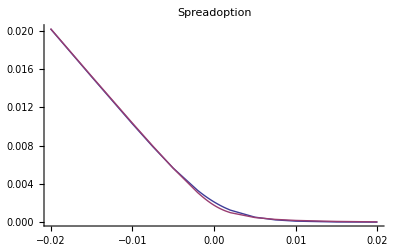
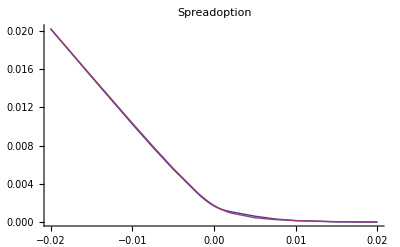
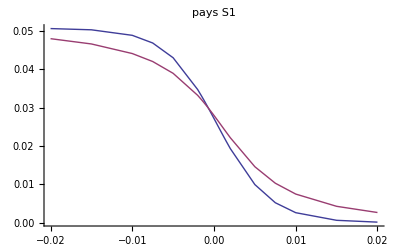
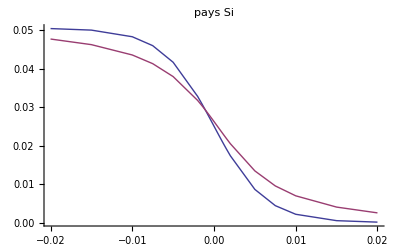
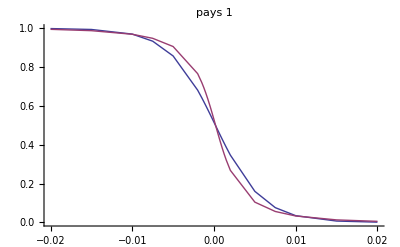
{239.828,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,
S1=0.0507,Si=0.0505,T=10,equivalentσ1,equivalentσi,equivalentρ,bilogdigitale,
bilogprices1,bilogSpreadoptionGRAPH,alphaSpreadoptionGRAPH,paysS1GRAPH,paysSiGRAPH,paysKGRAPH,paysdigitaleGRAPH,priceSpreadoption,BilogToHestonFlag,nbsteps=40,scale=8,microratio,WeightList,LimitGindinkin=10,printflag=1,prices1,pricesi,priced,priceK,commonν=0.01,bilogpices1,bilogpricesi,bilogpriceK,νcommun,Vsp,ρsp,νsp,Vopt,ρopt,νsopt,CompoundK,prices,digitaleprices,S1prices,S1digitaleprices,Siprices,Sidigitaleprices,CompoundminusK,shiftL,
optimisationStrikes={-0.005,-0.0025,0,0.0025,0.005},
KList={-0.02,-0.015,-0.01,-0.0075,-0.005,-0.002,-0.0015,-0.00125,-0.001,-0.00075,-0.0005,-0.0004,-0.00025,-0.0001,0,0.0001,0.00025,0.0004,0.0005,0.00075,0.001,0.00125,0.0015,0.002,0.005,0.0075,0.01,0.015,0.02}},τ=10;λ=0.1;LT=1;microratio=5 T^(1/2);shiftL=0.0001;
V1=1;V2=1;V3=1;V4=1;V5=0.0005;Vi=0.0005;
α11=0.07;α12=0.06;α13=0.03;α14=0.02;
αi1=0.07;αi2=0.06;αi3=0.03;αi4=0.02;
νcommun=2;BilogToHestonFlag=2;
ρ1=-0.5;ν1=νcommun;ρ2=-0.5;ν2=νcommun;ρ3=-0.5;ν3=νcommun;ρ4=-0.5;ν4=νcommun;ρ5=-0.5;ν5=νcommun √V5;ρi=-0.5;νi=νcommun √Vi;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
{{Vsp,ρsp,νsp},{Vopt,ρopt,νsopt}}=SmileAlphaDigitalesArbitrageFree4[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,T,printflag,optimisationStrikes];
bilogprices1=Table[S1 MesureQ1LogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
bilogpricesi=Table[Si MesureQ2LogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
bilogpriceK=Table[KList[[i]] MesureQTLogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
bilogdigitale=Table[ MesureQTLogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];

priceSpreadoption=DerivativeHestonNormalCall[ρsp,λ,LT,νsp,Vsp,S1-Si,KList,T,nbsteps,scale,microratio,0][[1]];
CompoundK=IntercalePrice[KList-shiftL,KList+shiftL];
prices=DerivativeHestonNormalCall[ρsp,λ,LT,νsp,Vsp,S1-Si,CompoundK,T,nbsteps,scale,microratio,0][[1]];
digitaleprices=Table[(prices[[2i-1]]-prices[[2i]])/(2shiftL),{i,1,Length[KList]}];
S1prices=DerivativeHestonNormalCall[ρopt,λ,LT,νsopt,Vopt,S1  ⅇ^(equivalentσ1^2 T) -Si ⅇ^(equivalentρ equivalentσ1 equivalentσi T) ,CompoundK,T,nbsteps,scale,microratio,0][[1]];
S1digitaleprices=Table[(S1prices[[2i-1]]-S1prices[[2i]])/(2shiftL),{i,1,Length[KList]}];
CompoundminusK=IntercalePrice[-KList-shiftL,-KList+shiftL];
Siprices=DerivativeHestonNormalCall[-ρopt,λ,LT,νsopt,Vopt,-(S1 ⅇ^(equivalentρ equivalentσ1 equivalentσi T)-Si ⅇ^(equivalentσi^2 T)) ,CompoundminusK,T,nbsteps,scale,microratio,0][[1]];
Sidigitaleprices=1-Table[(Siprices[[2i-1]]-Siprices[[2i]])/(2shiftL),{i,1,Length[KList]}];
priceK=Table[digitaleprices[[i]] KList[[i]],{i,Length[KList]}];
prices1=Table[S1digitaleprices[[i]] S1,{i,Length[KList]}];
pricesi=Table[Sidigitaleprices[[i]] Si,{i,Length[KList]}];
Print[" resultat de l'optimisation : ",{{Vsp,ρsp,νsp},{Vopt,ρopt,νsopt}}];
Print["test de l'optimisation :",TestDigitale[Vsp,ρsp,νsp,Vopt,ρopt,νsopt,S1,Si,equivalentσ1,equivalentσi,equivalentρ,λ,LT,T,optimisationStrikes]];
bilogSpreadoptionGRAPH=ListPlot[{Transpose[{KList,bilogprices1-bilogpricesi-bilogpriceK}],Transpose[{KList,priceSpreadoption}]},Joined->True,PlotLabel->"Spreadoption",PlotLegend->{"bilog","alpha"}, LegendPosition->{0.7,0.3}];
alphaSpreadoptionGRAPH=ListPlot[{Transpose[{KList,prices1-pricesi-priceK}],Transpose[{KList,priceSpreadoption}]},Joined->True,PlotLabel->"Spreadoption",PlotLegend->{"reconstitued alpha","authentic alpha"}, LegendPosition->{0.7,0.3}];
paysS1GRAPH=ListPlot[{Transpose[{KList,bilogprices1}],Transpose[{KList,prices1}]},Joined->True,PlotLabel->"pays S1",PlotLegend->{"bilog","alpha"}, LegendPosition->{0.7,0.3}];
paysSiGRAPH=ListPlot[{Transpose[{KList,bilogpricesi}],Transpose[{KList,pricesi}]},Joined->True,PlotLabel->"pays Si",PlotLegend->{"bilog","alpha"}, LegendPosition->{0.7,0.3}];
paysdigitaleGRAPH=ListPlot[{Transpose[{KList,bilogdigitale}],Transpose[{KList,digitaleprices}]},Joined->True,PlotLabel->"pays 1",PlotLegend->{"bilog","alpha"}, LegendPosition->{0.7,0.3}];
{bilogSpreadoptionGRAPH,alphaSpreadoptionGRAPH,paysS1GRAPH,paysSiGRAPH,paysdigitaleGRAPH}
]]]
```

## Generalisation (aux projections autre que normal Heston)

```mathematica
Soit Subscript[S, 1,T] la solution de (d Subscript[S, 1])/Subscript[S, 1]=Subscript[σ, 1] dW
```

```mathematica
Soit Subscript[S, 2,T] la solution de (d Subscript[S, 2])/Subscript[S, 2]=Subscript[σ, 2] dW
```

```mathematica
soit la fonctionnelle :
```

```mathematica
(Subscript[σ, 1],Subscript[S, 1,0],Subscript[σ, 2],Subscript[S, 2,0],K) ->E[SuperPlus[(Subscript[S, 1,T]- Subscript[S, 2,T]-K)]]=φ[G[Subscript[σ, 1],Subscript[σ, 2]],Subscript[S, 1,0],Subscript[S, 2,0],K]
```

```mathematica
or on a la relation d'arbitrage
```

```mathematica
E[SuperPlus[(Subscript[S, 1,T]-Subscript[S, 2,T]-K)]]=E[Subscript[S, 1,T] Subscript[1, Subscript[S, 1,T]-Subscript[S, 2,T]-K≥0]]-Subscript[S, 2,0]+E[Subscript[S, 2,T] Subscript[1, Subscript[S, 2,T]-Subscript[S, 1,T]+K≥0]]-K E[Subscript[1, Subscript[S, 1,T]-Subscript[S, 2,T]-K≥0]]
```

```mathematica
par changement de numeraire on a
```

```mathematica
E[Subscript[S, 1,T] Subscript[1, Subscript[S, 1,T]-Subscript[S, 2,T]-K≥0]]=Subscript[S, 1,0] D[(E^Subscript[Q, Subscript[S, 1]])[SuperPlus[(Subscript[S, 1,T]-Subscript[S, 2,T]-K)]], K]
```

```mathematica
E[Subscript[S, 2,T] Subscript[1, Subscript[S, 2,T]-Subscript[S, 1,T]+K≥0]]=Subscript[S, 2,0] D[(E^Subscript[Q, Subscript[S, 2]])[SuperPlus[(Subscript[S, 2,T]-Subscript[S, 1,T]+K)]], K]
```

```mathematica
E[Subscript[1, Subscript[S, 1]-Subscript[S, 2]-K≥0]]=D[φ[Subscript[σ, 1],Subscript[S, 1,0],Subscript[σ, 2],Subscript[S, 2,0],K], K]
```

```mathematica
On suppose que (E^Subscript[Q, Subscript[S, 1]])[SuperPlus[(Subscript[S, 1,T]-Subscript[S, 2,T]-K)]] = φ[Subscript[G, 1][Subscript[σ, 1],Subscript[σ, 2]],Subscript[H, 1][Subscript[S, 1,0],Subscript[σ, 1],Subscript[σ, 2]],Subscript[H, 2][Subscript[S, 2,0],Subscript[σ, 1],Subscript[σ, 2]],K]
```

```mathematica
On suppose que l'on connait Subscript[H, 1] et Subscript[H, 2] mais que l'on cherche a determiner Subscript[G, 1] et Subscript[G, 2]
```

```mathematica
on a aussi
```

```mathematica
(E^Subscript[Q, Subscript[S, 2]])[SuperPlus[(Subscript[S, 2,T]-Subscript[S, 1,T]+K)]]=φ[Subscript[G, 1][Subscript[σ, 2],Subscript[σ, 1]],Subscript[H, 1][Subscript[S, 2,0],Subscript[σ, 2],Subscript[σ, 1]],Subscript[H, 2][Subscript[S, 1,0],Subscript[σ, 2],Subscript[σ, 1]],-K]
```

```mathematica
on a donc la relation de non arbitrage:
```

```mathematica
φ[G[Subscript[σ, 1],Subscript[σ, 2]],Subscript[S, 1,0],Subscript[S, 2,0],K]+K D[φ[G[Subscript[σ, 1],Subscript[σ, 2]],Subscript[S, 1,0],Subscript[S, 2,0],K], K]=Subscript[S, 1,0] D[φ[Subscript[G, 1][Subscript[σ, 1],Subscript[σ, 2]],Subscript[H, 1][Subscript[S, 1,0],Subscript[σ, 1],Subscript[σ, 2]],Subscript[H, 2][Subscript[S, 2,0],Subscript[σ, 1],Subscript[σ, 2]],K], K]-Subscript[S, 2,0]+Subscript[S, 2,0] D[φ[Subscript[G, 1][Subscript[σ, 2],Subscript[σ, 1]],Subscript[H, 1][Subscript[S, 2,0],Subscript[σ, 2],Subscript[σ, 1]],Subscript[H, 2][Subscript[S, 1,0],Subscript[σ, 2],Subscript[σ, 1]],-K], K]
```

```mathematica
On suppose que pour un jeu de parametre, cette relation est trivialement verifiée avec OverBar[Subscript[σ, j]]  pour i,j∈{1,2}
```

```mathematica
φ[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[S, 1,0],Subscript[S, 2,0],K]+K D[φ[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[S, 1,0],Subscript[S, 2,0],K], K]=Subscript[S, 1,0] D[φ[Subscript[G, 1][OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[H, 1][Subscript[S, 1,0],OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[H, 2][Subscript[S, 2,0],OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],K], K]-Subscript[S, 2,0]+Subscript[S, 2,0] D[φ[Subscript[G, 1][OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],Subscript[H, 1][Subscript[S, 2,0],OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],Subscript[H, 2][Subscript[S, 1,0],OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],-K], K]
```

```mathematica
On developpe donc au pemier ordre autour de cette valeur
```

```mathematica
Subscript[σ, 1]=OverBar[Subscript[σ, 1]]+Subscript[Δσ, 1]  et Subscript[σ, 1]=OverBar[Subscript[σ, 2]]+Subscript[Δσ, 2]
```

```mathematica
pour la variation par rapport a Subscript[σ, 1]
```

```mathematica
(D[φ[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[S, 1,0],Subscript[S, 2,0],K], Subscript[σ, 1]]+K D[φ[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[S, 1,0],Subscript[S, 2,0],K], K,Subscript[σ, 1]])D[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]], Subscript[σ, 1]] Subscript[Δσ, 1]=(Subscript[S, 1,0] D[φ[Subscript[G, 1][OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[H, 1][Subscript[S, 1,0],OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[H, 2][Subscript[S, 2,0],OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],K], K,Subscript[σ, 1]]D[Subscript[G, 1][OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]], Subscript[σ, 1]]+Subscript[S, 2,0] D[φ[Subscript[G, 1][OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],Subscript[H, 1][Subscript[S, 2,0],OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],OverBar[Subscript[σ, 1]],Subscript[H, 2][Subscript[S, 1,0],OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],-K], K,Subscript[σ, 2]]D[Subscript[G, 1][OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]], Subscript[σ, 2]])Subscript[Δσ, 1]+
((...)D[Subscript[H, 1][Subscript[S, 1,0],OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]], Subscript[σ, 1]]+(...)D[Subscript[H, 2][Subscript[S, 2,0],OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]], Subscript[σ, 1]]+(...)D[Subscript[H, 1][Subscript[S, 1,0],OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]], Subscript[σ, 1]]+(...)D[Subscript[H, 2][Subscript[S, 2,0],OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]], Subscript[σ, 1]])Subscript[Δσ, 1]
```

```mathematica
Nous alloons nous restreindre seulement aux  cas  ou D[Subscript[H, j][Subscript[S, k,0],OverBar[Subscript[σ, u]],OverBar[Subscript[σ, v]]], Subscript[σ, i]]=0 qui correspond aux d'introduction de la vol de vol dans le modele
```

```mathematica
On suppose aussi que nous nous restreignions aux cas ou D[Subscript[G, 1][OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]], Subscript[σ, 1]]=D[Subscript[G, 1][OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]], Subscript[σ, 2]]
```

```mathematica
dans ce cas la  relation s'ecrit:
```

```mathematica
(D[φ[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[S, 1,0],Subscript[S, 2,0],K], Subscript[σ, 1]]+K D[φ[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[S, 1,0],Subscript[S, 2,0],K], K,Subscript[σ, 1]])D[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]], Subscript[σ, 1]]=(Subscript[S, 1,0] D[φ[Subscript[G, 1][OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[H, 1][Subscript[S, 1,0],OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[H, 2][Subscript[S, 2,0],OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],K], K,Subscript[σ, 1]]+Subscript[S, 2,0] D[φ[Subscript[G, 1][OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],Subscript[H, 1][Subscript[S, 2,0],OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],Subscript[H, 2][Subscript[S, 1,0],OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],-K], K,Subscript[σ, 2]])D[Subscript[G, 1][OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]], Subscript[σ, 1]]
```

```mathematica
la variation par rapport a Subscript[σ, 2] s'ecrit de meme
```

```mathematica
(D[φ[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[S, 1,0],Subscript[S, 2,0],K], Subscript[σ, 2]]+K D[φ[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[S, 1,0],Subscript[S, 2,0],K], K,Subscript[σ, 2]])D[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]], Subscript[σ, 2]]=(Subscript[S, 1,0] D[φ[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[H, 1][Subscript[S, 1,0],OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[H, 2][Subscript[S, 2,0],OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],K], K,Subscript[σ, 2]]+Subscript[S, 2,0] D[φ[Subscript[G, 1][OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],Subscript[H, 1][Subscript[S, 2,0],OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],Subscript[H, 2][Subscript[S, 1,0],OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],-K], K,Subscript[σ, 1]])D[Subscript[G, 1][OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]], Subscript[σ, 2]]
```

```mathematica
on a donc la solution sur la modification de la dynamique induite sur les digitale afin de respecter l'arbitrage:
```

```mathematica
D[Subscript[G, 1][OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]], Subscript[σ, 1]] = D[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]], Subscript[σ, 1]] R1
```

```mathematica
D[Subscript[G, 1][OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]], Subscript[σ, 2]] = D[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]], Subscript[σ, 2]] R2
```

```mathematica
ou
```

```mathematica
R1=(D[φ[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[S, 1,0],Subscript[S, 2,0],K], Subscript[σ, 1]]+K D[φ[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[S, 1,0],Subscript[S, 2,0],K], K,Subscript[σ, 1]])/(Subscript[S, 1,0] D[φ[Subscript[G, 1][OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[H, 1][Subscript[S, 1,0],OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[H, 2][Subscript[S, 2,0],OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],K], K,Subscript[σ, 1]]+Subscript[S, 2,0] D[φ[Subscript[G, 1][OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],Subscript[H, 1][Subscript[S, 2,0],OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],Subscript[H, 2][Subscript[S, 1,0],OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],-K], K,Subscript[σ, 2]])
```

```mathematica
R2=(D[φ[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[S, 1,0],Subscript[S, 2,0],K], Subscript[σ, 2]]+K D[φ[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[S, 1,0],Subscript[S, 2,0],K], K,Subscript[σ, 2]])/(Subscript[S, 1,0] D[φ[G[OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[H, 1][Subscript[S, 1,0],OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],Subscript[H, 2][Subscript[S, 2,0],OverBar[Subscript[σ, 1]],OverBar[Subscript[σ, 2]]],K], K,Subscript[σ, 2]]+Subscript[S, 2,0] D[φ[Subscript[G, 1][OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],Subscript[H, 1][Subscript[S, 2,0],OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],Subscript[H, 2][Subscript[S, 1,0],OverBar[Subscript[σ, 2]],OverBar[Subscript[σ, 1]]],-K], K,Subscript[σ, 1]])
```

## Annexes

## Interpolator 3 points

```mathematica
Solve[{a x1^2+b x1+c==y1,a x2^2+b x2+c==y2,a x3^2+b x3+c==y3},{a,b,c}]
```

{{a→-(-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3)/((x2-x3) (x1^2-x1 x2-x1 x3+x2 x3)),b→-(x2^2 y1-x3^2 y1-x1^2 y2+x3^2 y2+x1^2 y3-x2^2 y3)/((x1-x2) (x1-x3) (x2-x3)),c→-(-x2^2 x3 y1+x2 x3^2 y1+x1^2 x3 y2-x1 x3^2 y2-x1^2 x2 y3+x1 x2^2 y3)/((x2-x3) (x1^2-x1 x2-x1 x3+x2 x3))}}

```mathematica
FullSimplify[a x^2+b x+c /.{a->-(-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3)/((x2-x3) (x1^2-x1 x2-x1 x3+x2 x3)),b->-(x2^2 y1-x3^2 y1-x1^2 y2+x3^2 y2+x1^2 y3-x2^2 y3)/((x1-x2) (x1-x3) (x2-x3)),c->-(-x2^2 x3 y1+x2 x3^2 y1+x1^2 x3 y2-x1 x3^2 y2-x1^2 x2 y3+x1 x2^2 y3)/((x2-x3) (x1^2-x1 x2-x1 x3+x2 x3))}]
```

((x-x3) ((x-x2) (x2-x3) y1+(x-x1) (-x1+x3) y2)+(x-x1) (x-x2) (x1-x2) y3)/((x1-x2) (x1-x3) (x2-x3))

```mathematica
CForm[((x-x3) ((x-x2) (x2-x3) y1+(x-x1) (-x1+x3) y2)+(x-x1) (x-x2) (x1-x2) y3)/((x1-x2) (x1-x3) (x2-x3))]
```

((x - x3)*((x - x2)*(x2 - x3)*y1 + (x - x1)*(-x1 + x3)*y2) + 
     (x - x1)*(x - x2)*(x1 - x2)*y3)/((x1 - x2)*(x1 - x3)*(x2 - x3))

```mathematica
Interpolator3points[x1_,y1_,x2_,y2_,x3_,y3_,x_]:=((x-x3) ((x-x2) (x2-x3) y1+(x-x1) (-x1+x3) y2)+(x-x1) (x-x2) (x1-x2) y3)/((x1-x2) (x1-x3) (x2-x3))
```

## Interpolator 4 points

```mathematica
ss=Solve[{a x1^3+b x1^2+c x1+d==y1,a x2^3+b x2^2+c x2+d==y2,a x3^3+b x3^2+c x3+d==y3,a x4^3+b x4^2+c x4+d==y4},{a,b,c,d}]
```

{{a→y1/x1^3+(x2^3 x3^2 y1-x2^2 x3^3 y1-x2^3 x4^2 y1+x3^3 x4^2 y1+x2^2 x4^3 y1-x3^2 x4^3 y1-x1^3 x3^2 y2+x1^2 x3^3 y2+x1^3 x4^2 y2-x3^3 x4^2 y2-x1^2 x4^3 y2+x3^2 x4^3 y2+x1^3 x2^2 y3-x1^2 x2^3 y3-x1^3 x4^2 y3+x2^3 x4^2 y3+x1^2 x4^3 y3-x2^2 x4^3 y3-x1^3 x2^2 y4+x1^2 x2^3 y4+x1^3 x3^2 y4-x2^3 x3^2 y4-x1^2 x3^3 y4+x2^2 x3^3 y4)/(x1^2 (x1-x3) (x2-x3) (x2-x4) (-x3+x4) (x1^2-x1 x2-x1 x4+x2 x4))+(x2^3 x3^2 x4 y1-x2^2 x3^3 x4 y1-x2^3 x3 x4^2 y1+x2 x3^3 x4^2 y1+x2^2 x3 x4^3 y1-x2 x3^2 x4^3 y1-x1^3 x3^2 x4 y2+x1^2 x3^3 x4 y2+x1^3 x3 x4^2 y2-x1 x3^3 x4^2 y2-x1^2 x3 x4^3 y2+x1 x3^2 x4^3 y2+x1^3 x2^2 x4 y3-x1^2 x2^3 x4 y3-x1^3 x2 x4^2 y3+x1 x2^3 x4^2 y3+x1^2 x2 x4^3 y3-x1 x2^2 x4^3 y3-x1^3 x2^2 x3 y4+x1^2 x2^3 x3 y4+x1^3 x2 x3^2 y4-x1 x2^3 x3^2 y4-x1^2 x2 x3^3 y4+x1 x2^2 x3^3 y4)/(x1^3 (x3-x4) (x2^2-x2 x3-x2 x4+x3 x4) (x1^3-x1^2 x2-x1^2 x3+x1 x2 x3-x1^2 x4+x1 x2 x4+x1 x3 x4-x2 x3 x4))+1/x1((x2^3 y1-x1^3 y2)/(x1^3 x2^2-x1^2 x2^3)-((x1^3 x2-x1 x2^3) (x2^3 x3^2 y1-x2^2 x3^3 y1-x2^3 x4^2 y1+x3^3 x4^2 y1+x2^2 x4^3 y1-x3^2 x4^3 y1-x1^3 x3^2 y2+x1^2 x3^3 y2+x1^3 x4^2 y2-x3^3 x4^2 y2-x1^2 x4^3 y2+x3^2 x4^3 y2+x1^3 x2^2 y3-x1^2 x2^3 y3-x1^3 x4^2 y3+x2^3 x4^2 y3+x1^2 x4^3 y3-x2^2 x4^3 y3-x1^3 x2^2 y4+x1^2 x2^3 y4+x1^3 x3^2 y4-x2^3 x3^2 y4-x1^2 x3^3 y4+x2^2 x3^3 y4))/((x1^3 x2^2-x1^2 x2^3) (x1-x3) (x2-x3) (x2-x4) (-x3+x4) (x1^2-x1 x2-x1 x4+x2 x4))-((x1^3-x2^3) (x2^3 x3^2 x4 y1-x2^2 x3^3 x4 y1-x2^3 x3 x4^2 y1+x2 x3^3 x4^2 y1+x2^2 x3 x4^3 y1-x2 x3^2 x4^3 y1-x1^3 x3^2 x4 y2+x1^2 x3^3 x4 y2+x1^3 x3 x4^2 y2-x1 x3^3 x4^2 y2-x1^2 x3 x4^3 y2+x1 x3^2 x4^3 y2+x1^3 x2^2 x4 y3-x1^2 x2^3 x4 y3-x1^3 x2 x4^2 y3+x1 x2^3 x4^2 y3+x1^2 x2 x4^3 y3-x1 x2^2 x4^3 y3-x1^3 x2^2 x3 y4+x1^2 x2^3 x3 y4+x1^3 x2 x3^2 y4-x1 x2^3 x3^2 y4-x1^2 x2 x3^3 y4+x1 x2^2 x3^3 y4))/((x1^3 x2^2-x1^2 x2^3) (x3-x4) (x2^2-x2 x3-x2 x4+x3 x4) (x1^3-x1^2 x2-x1^2 x3+x1 x2 x3-x1^2 x4+x1 x2 x4+x1 x3 x4-x2 x3 x4))),b→-(x2^3 y1-x1^3 y2)/(x1^3 x2^2-x1^2 x2^3)+((x1^3 x2-x1 x2^3) (x2^3 x3^2 y1-x2^2 x3^3 y1-x2^3 x4^2 y1+x3^3 x4^2 y1+x2^2 x4^3 y1-x3^2 x4^3 y1-x1^3 x3^2 y2+x1^2 x3^3 y2+x1^3 x4^2 y2-x3^3 x4^2 y2-x1^2 x4^3 y2+x3^2 x4^3 y2+x1^3 x2^2 y3-x1^2 x2^3 y3-x1^3 x4^2 y3+x2^3 x4^2 y3+x1^2 x4^3 y3-x2^2 x4^3 y3-x1^3 x2^2 y4+x1^2 x2^3 y4+x1^3 x3^2 y4-x2^3 x3^2 y4-x1^2 x3^3 y4+x2^2 x3^3 y4))/((x1^3 x2^2-x1^2 x2^3) (x1-x3) (x2-x3) (x2-x4) (-x3+x4) (x1^2-x1 x2-x1 x4+x2 x4))+((x1^3-x2^3) (x2^3 x3^2 x4 y1-x2^2 x3^3 x4 y1-x2^3 x3 x4^2 y1+x2 x3^3 x4^2 y1+x2^2 x3 x4^3 y1-x2 x3^2 x4^3 y1-x1^3 x3^2 x4 y2+x1^2 x3^3 x4 y2+x1^3 x3 x4^2 y2-x1 x3^3 x4^2 y2-x1^2 x3 x4^3 y2+x1 x3^2 x4^3 y2+x1^3 x2^2 x4 y3-x1^2 x2^3 x4 y3-x1^3 x2 x4^2 y3+x1 x2^3 x4^2 y3+x1^2 x2 x4^3 y3-x1 x2^2 x4^3 y3-x1^3 x2^2 x3 y4+x1^2 x2^3 x3 y4+x1^3 x2 x3^2 y4-x1 x2^3 x3^2 y4-x1^2 x2 x3^3 y4+x1 x2^2 x3^3 y4))/((x1^3 x2^2-x1^2 x2^3) (x3-x4) (x2^2-x2 x3-x2 x4+x3 x4) (x1^3-x1^2 x2-x1^2 x3+x1 x2 x3-x1^2 x4+x1 x2 x4+x1 x3 x4-x2 x3 x4)),c→-(x2^3 x3^2 y1-x2^2 x3^3 y1-x2^3 x4^2 y1+x3^3 x4^2 y1+x2^2 x4^3 y1-x3^2 x4^3 y1-x1^3 x3^2 y2+x1^2 x3^3 y2+x1^3 x4^2 y2-x3^3 x4^2 y2-x1^2 x4^3 y2+x3^2 x4^3 y2+x1^3 x2^2 y3-x1^2 x2^3 y3-x1^3 x4^2 y3+x2^3 x4^2 y3+x1^2 x4^3 y3-x2^2 x4^3 y3-x1^3 x2^2 y4+x1^2 x2^3 y4+x1^3 x3^2 y4-x2^3 x3^2 y4-x1^2 x3^3 y4+x2^2 x3^3 y4)/((x1-x3) (x2-x3) (x2-x4) (-x3+x4) (x1^2-x1 x2-x1 x4+x2 x4)),d→-(x2^3 x3^2 x4 y1-x2^2 x3^3 x4 y1-x2^3 x3 x4^2 y1+x2 x3^3 x4^2 y1+x2^2 x3 x4^3 y1-x2 x3^2 x4^3 y1-x1^3 x3^2 x4 y2+x1^2 x3^3 x4 y2+x1^3 x3 x4^2 y2-x1 x3^3 x4^2 y2-x1^2 x3 x4^3 y2+x1 x3^2 x4^3 y2+x1^3 x2^2 x4 y3-x1^2 x2^3 x4 y3-x1^3 x2 x4^2 y3+x1 x2^3 x4^2 y3+x1^2 x2 x4^3 y3-x1 x2^2 x4^3 y3-x1^3 x2^2 x3 y4+x1^2 x2^3 x3 y4+x1^3 x2 x3^2 y4-x1 x2^3 x3^2 y4-x1^2 x2 x3^3 y4+x1 x2^2 x3^3 y4)/((x3-x4) (x2^2-x2 x3-x2 x4+x3 x4) (x1^3-x1^2 x2-x1^2 x3+x1 x2 x3-x1^2 x4+x1 x2 x4+x1 x3 x4-x2 x3 x4))}}

```mathematica
ff=FullSimplify[a x^3+b x^2+c x+d /.ss[[1]]]
```

(x1 (x1-x3) x3 (x1-x4) (x3-x4) x4 y2+x2 x4^2 (-x3^3 y1+x3^2 x4 y1+x1^2 (x1-x4) y3)+x1^2 x2 x3^2 (-x1+x3) y4+x2^3 (x4 (-x3^2 y1+x3 x4 y1+x1 (x1-x4) y3)+x1 x3 (-x1+x3) y4)+x2^2 (x1 x4 (-x1^2+x4^2) y3+x3^3 (x4 y1-x1 y4)+x3 (-x4^3 y1+x1^3 y4))+x^3 (x1 (x1-x4) x4 (y2-y3)+x3^2 (x4 (y1-y2)+x1 (y2-y4))+x2 (x4^2 (y1-y3)+x1^2 (y3-y4)+x3^2 (-y1+y4))+x3 (x4^2 (-y1+y2)+x1^2 (-y2+y4))+x2^2 (x4 (-y1+y3)+x3 (y1-y4)+x1 (-y3+y4)))+x (x1^2 (x1-x4) x4^2 (y2-y3)+x3^3 (x4^2 (y1-y2)+x1^2 (y2-y4))+x2^2 (x4^3 (y1-y3)+x1^3 (y3-y4)+x3^3 (-y1+y4))+x3^2 (x4^3 (-y1+y2)+x1^3 (-y2+y4))+x2^3 (x4^2 (-y1+y3)+x3^2 (y1-y4)+x1^2 (-y3+y4)))+x^2 (-x1 x4 (x1^2-x4^2) (y2-y3)+x3 (x4^3 (y1-y2)+x1^3 (y2-y4))+x2^3 (x4 (y1-y3)+x1 (y3-y4)+x3 (-y1+y4))+x3^3 (x4 (-y1+y2)+x1 (-y2+y4))+x2 (x4^3 (-y1+y3)+x3^3 (y1-y4)+x1^3 (-y3+y4))))/((x1-x2) (x1-x3) (x2-x3) (x1-x4) (x2-x4) (x3-x4))

```mathematica
ff1=Module[{xx3=x*x*x,xx2=x*x,x42=x4*x4,x32=x3*x3,x12=x1*x1,x13=x1*x1*x1,x33=x3*x3*x3,x43=x4*x4*x4,x23=x2*x2*x2,x22=x2*x2},(x1 (x1-x3) x3 (x1-x4) (x3-x4) x4 y2+x2 x42 (-x33 y1+x32 x4 y1+x12 (x1-x4) y3)+x12 x2 x32 (-x1+x3) y4+x23 (x4 (-x32 y1+x3 x4 y1+x1 (x1-x4) y3)+x1 x3 (-x1+x3) y4)+x22 (x1 x4 (-x12+x42) y3+x33 (x4 y1-x1 y4)+x3 (-x43 y1+x13 y4))+xx3 (x1 (x1-x4) x4 (y2-y3)+x32 (x4 (y1-y2)+x1 (y2-y4))+x2 (x42 (y1-y3)+x12 (y3-y4)+x32 (-y1+y4))+x3 (x42 (-y1+y2)+x12 (-y2+y4))+x22 (x4 (-y1+y3)+x3 (y1-y4)+x1 (-y3+y4)))+x (x12 (x1-x4) x42 (y2-y3)+x33 (x42 (y1-y2)+x12 (y2-y4))+x22 (x43 (y1-y3)+x13 (y3-y4)+x33 (-y1+y4))+x32 (x43 (-y1+y2)+x13 (-y2+y4))+x23 (x42 (-y1+y3)+x32 (y1-y4)+x12 (-y3+y4)))+xx2 (-x1 x4 (x12-x42) (y2-y3)+x3 (x43 (y1-y2)+x13 (y2-y4))+x23 (x4 (y1-y3)+x1 (y3-y4)+x3 (-y1+y4))+x33 (x4 (-y1+y2)+x1 (-y2+y4))+x2 (x43 (-y1+y3)+x33 (y1-y4)+x13 (-y3+y4))))/((x1-x2) (x1-x3) (x2-x3) (x1-x4) (x2-x4) (x3-x4))];
```

```mathematica
Simplify[ff-ff1]
```

0

```mathematica
CForm[(x1 (x1-x3) x3 (x1-x4) (x3-x4) x4 y2+x2 x42 (-x33 y1+x32 x4 y1+x12 (x1-x4) y3)+x12 x2 x32 (-x1+x3) y4+x23 (x4 (-x32 y1+x3 x4 y1+x1 (x1-x4) y3)+x1 x3 (-x1+x3) y4)+x22 (x1 x4 (-x12+x42) y3+x33 (x4 y1-x1 y4)+x3 (-x43 y1+x13 y4))+xx3 (x1 (x1-x4) x4 (y2-y3)+x32 (x4 (y1-y2)+x1 (y2-y4))+x2 (x42 (y1-y3)+x12 (y3-y4)+x32 (-y1+y4))+x3 (x42 (-y1+y2)+x12 (-y2+y4))+x22 (x4 (-y1+y3)+x3 (y1-y4)+x1 (-y3+y4)))+x (x12 (x1-x4) x42 (y2-y3)+x33 (x42 (y1-y2)+x12 (y2-y4))+x22 (x43 (y1-y3)+x13 (y3-y4)+x33 (-y1+y4))+x32 (x43 (-y1+y2)+x13 (-y2+y4))+x23 (x42 (-y1+y3)+x32 (y1-y4)+x12 (-y3+y4)))+xx2 (-x1 x4 (x12-x42) (y2-y3)+x3 (x43 (y1-y2)+x13 (y2-y4))+x23 (x4 (y1-y3)+x1 (y3-y4)+x3 (-y1+y4))+x33 (x4 (-y1+y2)+x1 (-y2+y4))+x2 (x43 (-y1+y3)+x33 (y1-y4)+x13 (-y3+y4))))/((x1-x2) (x1-x3) (x2-x3) (x1-x4) (x2-x4) (x3-x4))]
```

(x1*(x1 - x3)*x3*(x1 - x4)*(x3 - x4)*x4*y2 + x2*x42*(-(x33*y1) + x32*x4*y1 + x12*(x1 - x4)*y3) + x12*x2*(-x1 + x3)*x32*y4 + 
     x23*(x4*(-(x32*y1) + x3*x4*y1 + x1*(x1 - x4)*y3) + x1*x3*(-x1 + x3)*y4) + 
     x22*(x1*x4*(-x12 + x42)*y3 + x33*(x4*y1 - x1*y4) + x3*(-(x43*y1) + x13*y4)) + 
     xx3*(x1*(x1 - x4)*x4*(y2 - y3) + x32*(x4*(y1 - y2) + x1*(y2 - y4)) + 
        x2*(x42*(y1 - y3) + x12*(y3 - y4) + x32*(-y1 + y4)) + x3*(x42*(-y1 + y2) + x12*(-y2 + y4)) + 
        x22*(x4*(-y1 + y3) + x3*(y1 - y4) + x1*(-y3 + y4))) + 
     x*(x12*(x1 - x4)*x42*(y2 - y3) + x33*(x42*(y1 - y2) + x12*(y2 - y4)) + 
        x22*(x43*(y1 - y3) + x13*(y3 - y4) + x33*(-y1 + y4)) + x32*(x43*(-y1 + y2) + x13*(-y2 + y4)) + 
        x23*(x42*(-y1 + y3) + x32*(y1 - y4) + x12*(-y3 + y4))) + 
     xx2*(-(x1*x4*(x12 - x42)*(y2 - y3)) + x3*(x43*(y1 - y2) + x13*(y2 - y4)) + 
        x23*(x4*(y1 - y3) + x1*(y3 - y4) + x3*(-y1 + y4)) + x33*(x4*(-y1 + y2) + x1*(-y2 + y4)) + 
        x2*(x43*(-y1 + y3) + x33*(y1 - y4) + x13*(-y3 + y4))))/((x1 - x2)*(x1 - x3)*(x2 - x3)*(x1 - x4)*(x2 - x4)*(x3 - x4))

```mathematica
Interpolator4points[x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_,x_]:=Module[{xx3=x*x*x,xx2=x*x,x42=x4*x4,x32=x3*x3,x12=x1*x1,x13=x1*x1*x1,x33=x3*x3*x3,x43=x4*x4*x4,x23=x2*x2*x2,x22=x2*x2},(x1 (x1-x3) x3 (x1-x4) (x3-x4) x4 y2+x2 x42 (-x33 y1+x32 x4 y1+x12 (x1-x4) y3)+x12 x2 x32 (-x1+x3) y4+x23 (x4 (-x32 y1+x3 x4 y1+x1 (x1-x4) y3)+x1 x3 (-x1+x3) y4)+x22 (x1 x4 (-x12+x42) y3+x33 (x4 y1-x1 y4)+x3 (-x43 y1+x13 y4))+xx3 (x1 (x1-x4) x4 (y2-y3)+x32 (x4 (y1-y2)+x1 (y2-y4))+x2 (x42 (y1-y3)+x12 (y3-y4)+x32 (-y1+y4))+x3 (x42 (-y1+y2)+x12 (-y2+y4))+x22 (x4 (-y1+y3)+x3 (y1-y4)+x1 (-y3+y4)))+x (x12 (x1-x4) x42 (y2-y3)+x33 (x42 (y1-y2)+x12 (y2-y4))+x22 (x43 (y1-y3)+x13 (y3-y4)+x33 (-y1+y4))+x32 (x43 (-y1+y2)+x13 (-y2+y4))+x23 (x42 (-y1+y3)+x32 (y1-y4)+x12 (-y3+y4)))+xx2 (-x1 x4 (x12-x42) (y2-y3)+x3 (x43 (y1-y2)+x13 (y2-y4))+x23 (x4 (y1-y3)+x1 (y3-y4)+x3 (-y1+y4))+x33 (x4 (-y1+y2)+x1 (-y2+y4))+x2 (x43 (-y1+y3)+x33 (y1-y4)+x13 (-y3+y4))))/((x1-x2) (x1-x3) (x2-x3) (x1-x4) (x2-x4) (x3-x4))]
```

```mathematica
Interpolator5points[x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_,x5_,y5_,x_]:=Module[{},If[(x==x2) , x2,If[(x==x3) , x3,
If[(x>x3) , Interpolator4points[x2,y2,x3,y3,x4,y4,x5,y5,x],
 Interpolator4points[x1,y1,x2,y2,x3,y3,x4,y4,x]]]]]
```

```mathematica
Interpolator6points[x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_,x5_,y5_,x6_,y6_,x_]:=Module[{},If[(x==x2) , x2,If[(x==x3) , x3,
If[(x>x3) , Interpolator5points[x2,y2,x3,y3,x4,y4,x5,y5,x6,y6,x],
 Interpolator5points[x1,y1,x2,y2,x3,y3,x4,y4,x5,y5,x]]]]]
```

## Resolution des ricati

nous allons resoudre le systeme ou B_i[0]=B_(i,0)    pour le cas ou on a une time dependence (constant par morceaux)

df/dτ=κ^2/2 f^2-b f+c/2

with

So we compute the discriminant:Δ=b^2-κ^2  c

let ζ=√Δ

{x_1= (b-ζ)/κ^2
x_2= (b+ζ)/κ^2

on a bien sur : x_1 x_2=(2c)/κ^2=(-(ω^2-ⅈ ω))/κ^2  et   x_1+x_2=(-2b)/κ^2=2( λ+ⅈ ρ  ωκ)/κ^2  et   x1-x2=(-2ζ)/κ^2

donc   df/(( f-x1)(f-x2))=κ^2/2 dτ  et  1/( f-x1)-1/(f-x2)=(( f-x2)-( f-x1))/(( f-x1)(f-x2))=( x1-x2)/(( f-x1)(f-x2))

et      df (1/( f-x1)-1/(f-x2))=κ^2/2 (x1-x2)dτ

mais  a (x1-x2)=κ^2/2(-2ζ)/κ^2=-ζ

donc  Log[(B[τ]-x_1)/(B[τ]-x_2)]=-ζ τ+C  et   B[τ]-x_1=ⅇ^(-ζ  τ+C)(B[τ]-x_2)

donc

B[τ]=(x_1-ⅇ^(-ζ  τ+C)x_2)/(1-ⅇ^(-ζ  τ+C))

We determine C by :  B[0]=0 ⟺  x_1-ⅇ^C x_2=0  So  ⅇ^C(-x_2)=-x_1

ⅇ^C=x_1/x_2

donc B[τ]=(x_1-ⅇ^(-ζ  τ)x_1)/(1-ⅇ^(-ζ  τ)x_1/x_2)=(x_1 x_2(1-ⅇ^(-ζ  τ)))/(x_2-x_1 ⅇ^(-ζ  τ))

we create

ψp = -x_1 κ^2   et   ψm =   x_2 κ^2

donc x_1=-ψp/κ^2  et x_2=ψm/κ^2   ainsi que ψp +ψm =2ζ

et   B[τ]=((2c)/κ^2(1-ⅇ^(-ζ  τ)))/(ψm/κ^2--ψp/κ^2 ⅇ^(-ζ  τ))=(2c(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ))

maintenant on exploite : (∂A[τ])/(∂τ)=λ θ B[τ]        avec A[0]=0

```mathematica
Simplify[Integrate[λ θ((1-ⅇ^(-ζ  t)) 2c)/(ⅇ^(-ζ  t)ψp+ψm),{t,0,τ}] ]
```

-(2 c θ λ (ζ τ ψm+(ψm+ψp) Log[ψm+ψp]-(ψm+ψp) Log[ⅇ^(ζ τ) ψm+ψp]))/(ζ ψm ψp)

c' est a dire :

(ω (-ⅈ+ω) (ζ τ ψm+2ζ Log[(2ζ)/(ⅇ^(ζ τ) ψm+ψp)]))/(ζ ψm ψp)

```mathematica
-(2 c θ λ (ζ τ ψm+(ψm+ψp) Log[ψm+ψp]-(ψm+ψp) Log[ⅇ^(ζ τ) ψm+ψp]))/(ζ ψm ψp) /.{ ψp+ψm->2ζ,ψp ψm->κ^2   ω^2}
```

-(2 c θ λ (ζ τ ψm+2 ζ Log[2 ζ]-2 ζ Log[ⅇ^(ζ τ) ψm+ψp]))/(ζ ψm ψp)

donc

A[τ]=-(2 c θ λ ( τ ψm+2  Log[(2 ζ)/(ⅇ^(ζ τ) ψm+ψp)]))/(ψm ψp)=

Si on tient compte de :

x_1 x_2=(2c)/κ^2 donc    ψp ψm=-x_1 x_2 κ^4=-2 c κ^2

ψp = -x_1 κ^2   et   ψm =   x_2 κ^2

x1-x2=(-2ζ)/κ^2

donc

ψp + ψm = 2 ζ

on a :

A[τ]=-(2 c θ λ ( τ ψm+2  Log[(2 ζ)/(ⅇ^(ζ τ) ψm+ψp)]))/(ψm ψp)=(θ λ ( τ ψm+2  Log[(2 ζ)/(ⅇ^(ζ τ) ψm+ψp)]))/κ^2=-(θ λ ( -τ ψm-2  Log[(2 ζ ⅇ^(-ζ τ))/(ψm+ψp ⅇ^(-ζ τ))]))/κ^2

A[τ]=-(θ λ ( -τ ψm-2  Log[(2 ζ)/(ψm+ψp ⅇ^(-ζ τ))]+2ζ τ ))/κ^2=-(θ λ ( -τ ψm-2  Log[(2 ζ)/(ψm+ψp ⅇ^(-ζ τ))]+(ψp +ψm) τ ))/κ^2=-(θ λ ( τ ψp +2  Log[(ψm+ψp ⅇ^(-ζ τ))/(2 ζ)]))/κ^2

donc au total :

donc la solution de

```mathematica
df/dτ=κ^2/2 f^2-b f+c/2     avec f[0]=0
```

est

B[τ]=(c(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ))

A[τ]=-(θ λ ( τ ψp +2  Log[(ψm+ψp ⅇ^(-ζ τ))/(2 ζ)]))/κ^2+d τ

avec

{ψp= -b+ζ
ψm= b+ζ
 et   ζ=√(b^2-κ^2  c)

```mathematica
RiccatiSolve[κ_,b_,c_,λ_,θ_,τ_]:=Module[{ψp,ψm,ζ,A,B},
ζ=√(b^2-κ^2  c);
ψp= -b+ζ;
ψm= b+ζ;
A=-(θ λ ( τ ψp +2  Log[(ψm+ψp ⅇ^(-ζ τ))/(2 ζ)]))/κ^2;
B=(c(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
{A,B}
]
```

## Normal 1 Facteur : Comparaison de 3 mappers (n'apporte rien)

### Mapper x=(1/y)-1

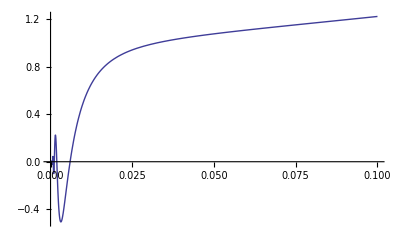

```mathematica
Module[{ρ=0.5,λ=0.1,L=0.5,ν=0.005171729,V0=1.17492*10^(-05),S0=0.002786743,k=0.005,T=3.41369863,KList={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},λS=0.15},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,(y-1)/y,λS][[1,2]](-1/(y)^2),{y,0,0.1},PlotRange->All]]
```

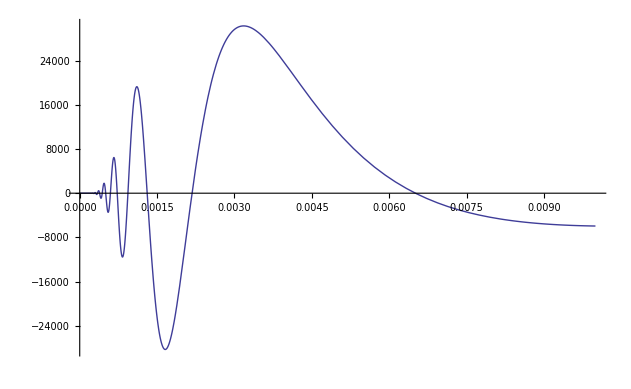

```mathematica
Module[{ρ=-0.000094075283,λ=0.1,L=0.5,ν=0.005171729,V0=1.17492*10^(-05),S0=0.002786743,k=0.005,T=3.41369863,KList={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},λS=0.15},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,(y-1)/y,λS][[2,2]](-1/(y)^2),{y,0,0.01},PlotRange->All]]
```

### Mapper x=-log[y]/C

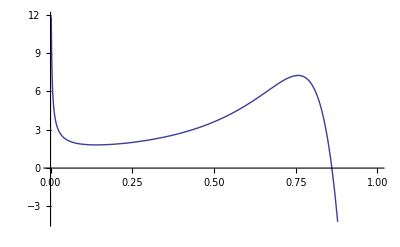

```mathematica
Module[{ρ=0.5,λ=0.1,L=0.5,ν=0.005171729,V0=1.17492*10^(-05),S0=0.002786743,k=0.005,T=3.41369863,KList={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},λS=0.15,CLog=1.},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,-Log[y]/CLog,λS][[1,2]](-1/(y CLog)),{y,0,1}]]
```

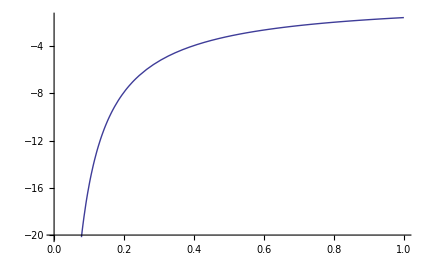

```mathematica
Module[{ρ=-0.000094075283,λ=0.1,L=0.5,ν=0.005171729,V0=1.17492*10^(-05),S0=0.002786743,k=0.005,T=3.41369863,KList={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},λS=0.15,CLog=1},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,-Log[y]/CLog,λS][[2,2]](-1/(y CLog)),{y,0,1}]]
```

### Mapper x=Tan[y π/2]

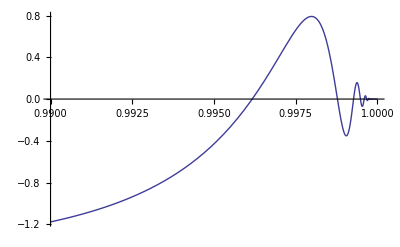

```mathematica
Module[{ρ=0.5,λ=0.1,L=0.5,ν=0.005171729,V0=1.17492*10^(-05),S0=0.002786743,k=0.005,T=3.41369863,KList={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},λS=0.15,CLog=1.},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,Tan[y π/2],λS][[1,2]] 1/2 π Cos[(π y)/2]^-2,{y,0.99,1},PlotRange->All]]
```

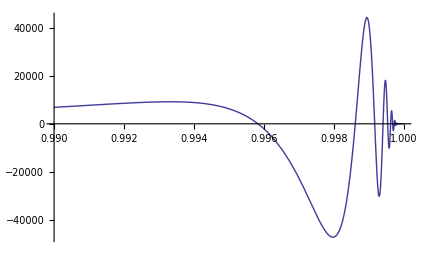

```mathematica
Module[{ρ=-0.000094075283,λ=0.1,L=0.5,ν=0.005171729,V0=1.17492*10^(-05),S0=0.002786743,k=0.005,T=3.41369863,KList={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},λS=0.15,CLog=1},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,Tan[y π/2],λS][[2,2]] 1/2 π Cos[(π y)/2]^-2,{y,0.99,1}]]
```

Conclusion 1 : Le mapping ne change pas le fait que si on a une integrale oscillante, les oscillation resteront et auront toujours besoin d' etre integrees.  De ce point de vue il est plus pratique d' avoir ces oscillation en 0 ainsi des une transformation rapidement calculable. de ce point de vue, le premier mapping est le meilleur.

Conclusion2 : Quand on veut integrer les oscillation, il vaut mieux les deplier et avoir un algorithme iteratif, car ces ocillation semeble avoir une frequnece constante. dans ce cas lemapping est inutile.

## Moments d'un Normal Heston et power option 1D

```mathematica
Simplify[∫_(k^(1/n))^∞ ⅇ^(ⅈ ω x1) (x1^n-k)ⅆx1]
```

If[Im[ω]>0&&(Im[k^(1/n)]≠0||k^(1/n)>0),-(ⅈ (ⅇ^(ⅈ k^(1/n) ω) k+(-(-ⅈ ω)^-n+(k^(1/n))^n (-ⅈ k^(1/n) ω)^-n) Gamma[1+n]-(k^(1/n))^n (-ⅈ k^(1/n) ω)^-n Gamma[1+n,-ⅈ k^(1/n) ω]))/ω,Integrate[-ⅇ^(ⅈ x1 ω) k+ⅇ^(ⅈ x1 ω) x1^n,{x1,k^(1/n),∞},Assumptions→k^(1/n)≤0||Im[ω]≤0]]

```mathematica
Simplify[∫_(-∞)^(k^(1/n)) ⅇ^(ⅈ ω x1) (k-x1^n)ⅆx1]
```

If[Im[ω]<0&&(Im[k^(1/n)]≠0||Sign[k^(1/n)]==-1),-(ⅈ (ⅇ^(ⅈ k^(1/n) ω) k+(-(-1)^n (ⅈ ω)^-n+(k^(1/n))^n (-ⅈ k^(1/n) ω)^-n) Gamma[1+n]-(k^(1/n))^n (-ⅈ k^(1/n) ω)^-n Gamma[1+n,-ⅈ k^(1/n) ω]))/ω,Integrate[ⅇ^(ⅈ x1 ω) k-ⅇ^(ⅈ x1 ω) x1^n,{x1,-∞,k^(1/n)},Assumptions→!(Im[ω]<0&&(Im[k^(1/n)]≠0||Sign[k^(1/n)]==-1))]]

```mathematica
Simplify[-(ⅈ (ⅇ^(ⅈ k^(1/n) ω) k+(-(-ⅈ ω)^-n+(k^(1/n))^n (-ⅈ k^(1/n) ω)^-n) Gamma[1+n]-(k^(1/n))^n (-ⅈ k^(1/n) ω)^-n Gamma[1+n,-ⅈ k^(1/n) ω]))/ω,k>0&& n>0]
```

-(ⅈ (ⅇ^(ⅈ k^(1/n) ω) k-(-ⅈ ω)^-n Gamma[1+n,-ⅈ k^(1/n) ω]))/ω

```mathematica
Simplify[∫_0^∞ ⅇ^(ⅈ ω x1) (x1^n)ⅆx1]
```

If[Im[ω]>0&&Re[n]>-1,(-ⅈ ω)^(-1-n) Gamma[1+n],Integrate[ⅇ^(ⅈ x1 ω) x1^n,{x1,0,∞},Assumptions→Im[ω]≤0||(Im[ω]>0&&Re[n]≤-1)]]

```mathematica
NormalPowerCallPayOffFourierTransform[k_,n_,ω_]:=If[k≠0,-(ⅈ (ⅇ^(ⅈ k^(1/n) ω) k-(-ⅈ ω)^-n Gamma[1+n,-ⅈ k^(1/n) ω]))/ω,(-ⅈ ω)^(-1-n) Gamma[1+n]]
```

### Implementation mathematica de reference

```mathematica
HestonPowerNormalCallN[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=n+0.5,ω},
NIntegrate[ⅇ^(-ⅈ (ω +λ ⅈ)S0)NormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω+ⅈ λ,T]NormalPowerCallPayOffFourierTransform[k,n,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
HestonPowerNormalPutN[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=-0.5,ω},
NIntegrate[ⅇ^(-ⅈ (ω +λ ⅈ)S0)NormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω+ⅈ λ,T]NormalPowerCallPayOffFourierTransform[k,n,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

### Implementation Operationnelle

```mathematica
HestonPowerNormalCallAux[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=n+0.5,ω},
AdaptativeIntegrate[Function[ω,ⅇ^(-ⅈ (ω +λ ⅈ)S0)NormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω +λ ⅈ,T]NormalPowerCallPayOffFourierTransform[k,n,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[20],
10/T,5/T,10^(-10),1000,1/T,LegendreCoeffs[60]][[2]]]]
```

```mathematica
HestonPowerNormalPutAux[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=-0.5,ω},
AdaptativeIntegrate[Function[ω,ⅇ^(-ⅈ (ω +λ ⅈ)S0)NormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω +λ ⅈ,T]NormalPowerCallPayOffFourierTransform[k,n,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[20],
10/T,5/T,10^(-10),1000,1/T,LegendreCoeffs[60]][[2]]]]
```

### Implementation Normalisée

```mathematica
HestonPowerNormalCall[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=Module[{θv1,κ1,V1,S01,k1,L,prix},
L=√(1./V);θv1=L^2 θv;κ1=L κ;V1=1.0;S01=L S0;k1=L^n k;
prix=HestonPowerNormalCallAux[ρ,λv,θv1,κ1,V1,S01,k1,n,T];
L^-n*prix]
```

```mathematica
HestonPowerNormalPut[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=Module[{θv1,κ1,V1,S01,k1,L,prix},
L=√(1./V);θv1=L^2 θv;κ1=L κ;V1=1.0;S01=L S0;k1=L^n k;
prix=HestonPowerNormalPutAux[ρ,λv,θv1,κ1,V1,S01,k1,n,T];
L^-n*prix]
```

```mathematica
HestonNormalVariance[ρ_,λv_,θv_,κ_,V_,S0_,T_]:=Module[{call,put},
call=HestonPowerNormalCall[ρ,λv,θv,κ,V,S0,S0^2,2,T];
put=HestonPowerNormalPut[ρ,λv,θv,κ,V,S0,S0^2,2,T];
call-put]
```

```mathematica
HestonNormalVarianceTrace[ρ_,λv_,θv_,κ_,V_,S0_,T_]:=Module[{call,put},
call=HestonPowerNormalCall[ρ,λv,θv,κ,V,S0,S0^2,2,T];
put=HestonPowerNormalPut[ρ,λv,θv,κ,V,S0,S0^2,2,T];
Print["T=",T," call=",call," put=",put];
call-put]
```

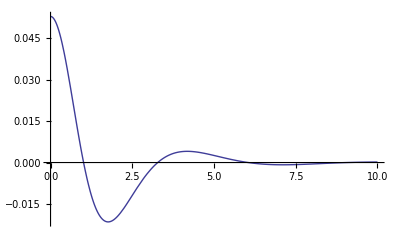
{0.344,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.1,λv=0.15,θv=0.01,κ=0.1,V=0.01,S0=0.001,λ1=2.5,T=10,k=1,n=2,ω},
Plot[{Re[ⅇ^(-ⅈ (ω+ⅈ λ1)  S0)NormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω+ⅈ λ1,T]NormalPowerCallPayOffFourierTransform[k,n,ω+ⅈ λ1]]},{ω,0,10},PlotRange->All]
]]
```

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.05,κ=0.1,V=0.05,S0=0.001,T=5},
HestonPowerNormalCallAux[ρ,λv,θv,κ,V,S0,0,2,T]]]
```

{0.141,-0.125389}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.001,κ=0.1,V=0.001,S0=0,T=5},
HestonNormalVariance[ρ,λv,θv,κ,V,S0,T]]]
```

{0.328,-0.000687706}

#### Moments a partir de la transformé de fourier

```mathematica
NormalHestonFondamentalTransformLog[ρ_,λv_,θv_,κ_,V_,ω_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ},
ζ=√((λv+ρ κ ⅈ ω)^2+κ^2( ω^2));
ψp =-(λv+ρ κ  ⅈ ω)+ζ;
ψm =(λv+ρ κ  ⅈ ω)+ζ;
A=-(θv λv (τ ψp+2 Log[(ψm+ⅇ^(-ζ τ) ψp)/(2ζ)]))/κ^2;
B=(-( ω^2)(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
A+B V]
```

```mathematica
D2=D[NormalHestonFondamentalTransformLog[ρ,λv,θv,κ,V,ω,τ],{ω,2}];
D2LogNormalHestonFondamentalTransform=Function[{ρ,λv,θv,κ,V,τ},Evaluate[1/ⅈ^2 D2/. ω->0]];
```

```mathematica
D2LogNormalHestonFondamentalTransform=Function[{ρ,λv,θv,κ,V,τ},Evaluate[Simplify[D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,τ],λv>0]]];
```

```mathematica
Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.01,ω=0,τ=30},
{D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,τ]}]
```

{1.00222}

La formule est en fait tres simple

```mathematica
D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,τ]
```

(V-ⅇ^(-λv τ) V+θv (-1+ⅇ^(-λv τ)+λv τ))/λv

```mathematica
et lorsque V=θv
```

```mathematica
Simplify[D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,τ] /. θv->V]
```

V τ

#### Comparaison entre les differents moyens de calculer la variance d'un normal Heston

ca marche pour des maturité inferieure a 2.5  an , pourquoi , mystere

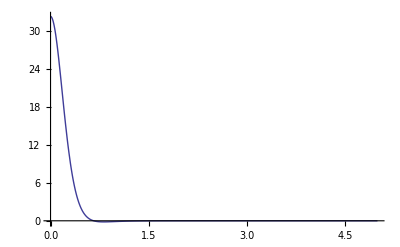
{0.406,{-Graphics-,{0.0195418,0.0462}}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.011,κ=0.05,V=0.011,S0=0,k,T=4.2,λ=0.5,L,θv1,κ1,V1,S01,k1},k=S0;
L=√(1./V);θv1=L^2 θv;κ1=L κ;V1=1.0;S01=L S0;k1=L^2 k;
{Plot[{Re[ⅇ^(-ⅈ (ω+ⅈ λ)  S01)NormalHestonFondamentalTransform[ρ,λv,θv1,κ1,V1,ω+ⅈ λ,T]NormalPowerCallPayOffFourierTransform[k1,2,ω +λ ⅈ]]},{ω,0,5},PlotRange->All],
{HestonNormalVariance[ρ,λv,θv,κ,V,S0,T]-S0^2,D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,T]}}]]
```

## Moments d'un LogNormal Heston et power option 1,2,3D

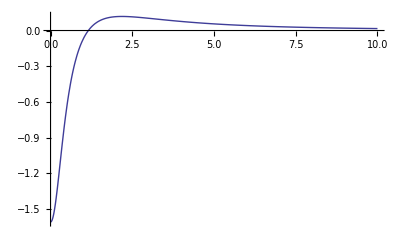
{0.156,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.1,λv=0.15,θv=0.01,κ=2,V=0.01,S0=1,λ1=2.5,T=10,k=1,n=2,ω,λ=2.5},
Plot[LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,n,T,ω +λ ⅈ],{ω,0,10},PlotRange->All]
]]
```

### Implementation mathematica de reference

```mathematica
PowerLogHestonNormalCallN[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=n+0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,n,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
PowerLogHestonNormalCallN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=n+0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,1,n,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
PowerLogHestonNormalCallN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=n+0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,1,n,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
PowerLogHestonNormalPutN[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=-0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,n,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
PowerLogHestonNormalPutN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=-0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,1,n,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
PowerLogHestonNormalPutN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=-0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,1,n,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
LogHestonNormalVarianceN[ρ_,λv_,θv_,κ_,V_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCallN[ρ,λv,θv,κ,V,S0,S0^2,2,T];
put=PowerLogHestonNormalPutN[ρ,λv,θv,κ,V,S0,S0^2,2,T];
call-put
]
```

```mathematica
LogHestonNormalVarianceN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCallN[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,S0^2,2,T];
put=PowerLogHestonNormalPutN[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,S0^2,2,T];
call-put
]
```

```mathematica
LogHestonNormalVarianceN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCallN[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,S0^2,2,T];
put=PowerLogHestonNormalPutN[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,S0^2,2,T];
call-put
]
```

### Implementation Operationnelle

```mathematica
PowerLogHestonNormalCallAux[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=n+0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,n,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
PowerLogHestonNormalCallAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=n+0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,1,n,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
PowerLogHestonNormalCallAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=n+0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,1,n,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
PowerLogHestonNormalPutAux[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=-0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,n,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
PowerLogHestonNormalPutAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=-0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,1,n,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
PowerLogHestonNormalPutAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=-0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,1,n,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

### Implementation Normalisée

```mathematica
PowerLogHestonNormalCall[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=Module[{},
S0^n PowerLogHestonNormalCallAux[ρ,λv,θv,κ,V,1,k/S0^n,n,T]
]
```

```mathematica
PowerLogHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,n_,T_]:=Module[{},
S0^n PowerLogHestonNormalCallAux[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,1,k/S0^n,n,T]
]
```

```mathematica
PowerLogHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,n_,T_]:=Module[{},
S0^n PowerLogHestonNormalCallAux[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,1,k/S0^n,n,T]
]
```

```mathematica
PowerLogHestonNormalPut[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=Module[{},
S0^n PowerLogHestonNormalPutAux[ρ,λv,θv,κ,V,1,k/S0^n,n,T]
]
```

```mathematica
PowerLogHestonNormalPut[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,n_,T_]:=Module[{},
S0^n PowerLogHestonNormalPutAux[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,1,k/S0^n,n,T]
]
```

```mathematica
PowerLogHestonNormalPut[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,n_,T_]:=Module[{},
S0^n PowerLogHestonNormalPutAux[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,1,k/S0^n,n,T]
]
```

```mathematica
LogHestonNormalVariance[ρ_,λv_,θv_,κ_,V_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCall[ρ,λv,θv,κ,V,S0,S0^2,2,T];
put=PowerLogHestonNormalPut[ρ,λv,θv,κ,V,S0,S0^2,2,T];
call-put
]
```

```mathematica
LogHestonNormalVariance[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,S0^2,2,T];
put=PowerLogHestonNormalPut[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,S0^2,2,T];
call-put
]
```

```mathematica
LogHestonNormalVariance[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,S0^2,2,T];
put=PowerLogHestonNormalPut[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,S0^2,2,T];
call-put
]
```

```mathematica
LogHestonNormalVarianceTrace[ρ_,λv_,θv_,κ_,V_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCall[ρ,λv,θv,κ,V,S0,S0^2,2,T];
put=PowerLogHestonNormalPut[ρ,λv,θv,κ,V,S0,S0^2,2,T];
Print["call=",call," put=",put];
call-put
]
```

```mathematica
LogHestonNormalVarianceTrace[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,S0^2,2,T];
put=PowerLogHestonNormalPut[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,S0^2,2,T];
Print["call=",call," put=",put];
call-put
]
```

```mathematica
LogHestonNormalVarianceTrace[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,S0^2,2,T];
put=PowerLogHestonNormalPut[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,S0^2,2,T];
Print["call=",call," put=",put];
call-put
]
```

```mathematica
Timing[Module[{ρ=-0.1,λv=0.15,θv=0.1,κ=2,V=0.1,S0=1,λ1=2.5,T=10,k=1,n=2,ω,λ=2.5},
{PowerLogHestonNormalCallN[ρ,λv,θv,κ,V,S0,k,n,T],PowerLogHestonNormalCall[ρ,λv,θv,κ,V,S0,k,n,T]}]]
```

{4.852,{1.22924,1.22924}}

```mathematica
Timing[Module[{ρ=-0.1,λv=0.15,θv=0.1,κ=2,V=0.1,S0=1,λ1=2.5,T=10,k=1,n=2,ω,λ=2.5},
{PowerLogHestonNormalPutN[ρ,λv,θv,κ,V,S0,k,n,T],PowerLogHestonNormalPut[ρ,λv,θv,κ,V,S0,k,n,T]}]]
```

{5.296,{1.1534,1.1534}}

#### Exemple de calcul de variance

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.05,κ=1.5,V=1,S0=0.04,T=1},
{LogHestonNormalVariance[ρ,λv,θv,κ,V,S0,T],S0^2 V T}]]
```

{0.078,{0.00554081,0.0016}}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.05,κ=0.1,V=0.05,S0=0.04,T=5},
{LogHestonNormalVariance[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,T],S0^2 V T}]]
```

{0.063,{-0.000609768,0.0004}}

#### Exemple de l'evolution de la volatilité moyenne

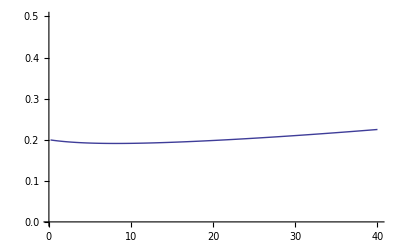
{12.89,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.04,κ=0.1,V=0.04,S0=1},
ListPlot[{#,√(LogHestonNormalVariance[ρ,λv,θv,κ,V,S0,#]/(S0 S0 #))}& /@ Table[i/5,{i,1,200}],Joined->True ,PlotRange->{0,0.5}]]]
```

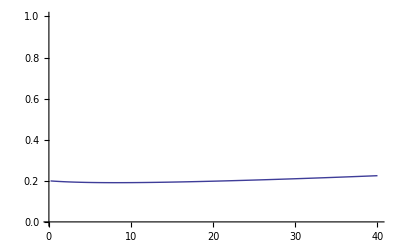
{19.672,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.02,κ=0.1,V=0.02,S0=1},
ListPlot[{#,√(LogHestonNormalVariance[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,#]/(S0 S0 #))}& /@ Table[i/5,{i,1,200}],Joined->True ,PlotRange->{0,1}]]]
```

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.02,κ=0.2,V=0.02,S0=1},
ListPlot[{#,√(LogHestonNormalVariance[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,#]/(S0 S0 #))}& /@ Table[i/5,{i,1,200}],Joined->True ,PlotRange->{0,1}]]]
```

{26.953,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.02,κ=0.5,V=0.02,S0=1},
ListPlot[{#,√(LogHestonNormalVariance[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,#]/(S0 S0 #))}& /@ Table[i/5,{i,1,200}],Joined->True ,PlotRange->{0,1}]]]
```

{46.531,-Graphics-}

#### Cassage de gueule a 40 ans !

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.04,κ=0.1,V=0.04,S0=1,T=40},
PowerLogHestonNormalCall[ρ,λv,θv,κ,V,S0,S0^2,2,T]]]
```

{0.016,-4.70278×10^7}

```mathematica
Timing[Module[{ρ=-0.1,λv=0.15,θv=0.05,κ=2,V=0.05,S0=1,λ1=2.5,T=40,k=1,n=2,ω,λ=-.5},
Plot[LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,n,T,ω +λ ⅈ],{ω,0,10},PlotRange->All]
]]
```

{0.094,-Graphics-}